Phonon Modes for Lattice Vibrations with One-Atom Basis

```mathematica
Manipulate[tick;
Dynamic@If[ tabNumber == dynTab,
dynPlot[tau],
If[tabNumber == freqTab,
frequencyPlot[ matrix, locDependentCalc, meshSize ],
plotSprings[springPlotH,springPlotNE,springPlotNW,springPlotV, locDependentCalc]  ] ]
,
TabView[{
"dynamics" ->  Column[
tabNumber = dynTab ;
{ 
Row[ {OverVector["q"], ", normalized to unit square:"}],
Row[{
(* q here in normalized coordinates, because of an order of operations issue.  This Grid appears to be evaluated before the Init section?  Not sure how to fix.  Would have to deal with that to allow one vs. two atom basis too (for the omegaIndex SetterBar). *)
Slider2D[Dynamic[qLoc,(
qLoc=#;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&], {{-1/2,-1/2}, {1/2,1/2}},
ContinuousAction->False], " ",  Dynamic[(NumberForm[qLoc, 5] // MatrixForm)]
}],
Row[{"Time, normalized to one period:"}],
Row[{Manipulator[Dynamic[tau,(tau=#;tick=Not[tick])&],{0,1},ImageSize->Tiny,ContinuousAction->True]}
, ImageSize->{200,60}],
Text["Angular frequency ω(q), selection:"],
SetterBar[Dynamic[omegaIndex,(
omegaIndex=#;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&], Range[2] ]

}]
, "ω(q⃗)" ->  Row[ tabNumber = freqTab ;{ "Mesh size ",
(* FIXME: Want to be able to select a plane here, 
   displaying both a plane plot and the 3D plot (or a checkbox for one or the other).*)
Manipulator[Dynamic[meshSize,(meshSize=#;tick=Not[tick])&],{2,20,2},ImageSize->Tiny,ContinuousAction->False]," ", Dynamic[meshSize] 
}]
, "parameters"->Column[ tabNumber = parametersTab ;{
Text[ "Spring constants:" ],
Grid[{
{
Row[{ "Horizontal: ",kLable[1], " || ", OverVector["a"]," "}],
Row[{
Manipulator[
Dynamic[k1,(
k1=#;
springPlotH = springLatticePlot[locDependentCalc, springLatticeData[[1]],k1/kMax]; 
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, mass]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
,
" ",Dynamic[NumberForm[k1,3]]
}]
},
{
Row[{ "Vertical: ",kLable[2], " || ", OverVector["b"]," "}],
Row[{Manipulator[
Dynamic[k2,(
k2=#;
springPlotV=springLatticePlot[locDependentCalc, springLatticeData[[2]],k2/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, mass]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k2,3]]
}] 
},
{
Row[{ "Diagonal: ",kLable[3], " || (",  OverVector["b"], " + ", OverVector["a"], ") "}],
Row[{Manipulator[
Dynamic[k3,(
k3=#;
springPlotNE=springLatticePlot[locDependentCalc, springLatticeData[[3]],k3/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, mass]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k3,3]]
}]
},
{
Row[{ "Diagonal: ",kLable[4], " || (",  OverVector["b"], " - ", OverVector["a"], ") "}],
Row[{Manipulator[
Dynamic[k4,(
k4=#;
springPlotNW=springLatticePlot[locDependentCalc, springLatticeData[[4]],k4/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, mass]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k4,3]]
}]
}
}], 
LocatorPane[
Dynamic[{aLoc, bLoc, mLoc},
({aLoc, bLoc, mLoc}=#; 
(* Lance, testing for me, managed to break the physical constants tab, by moving the points too close to the origin *)
aLoc = If[ aLoc. aLoc < lanceTestForceField, aLocDefault, aLoc ] ;
bLoc = If[ bLoc. bLoc < lanceTestForceField, bLocDefault, bLoc ] ;
locDependentCalc = locDependent[ aLoc, bLoc, mLoc ] ;
springPlotH=springLatticePlot[locDependentCalc, springLatticeData[[1]],k1/kMax]; springPlotV=springLatticePlot[locDependentCalc, springLatticeData[[2]],k2/kMax];springPlotNE=springLatticePlot[locDependentCalc, springLatticeData[[3]],k3/kMax];springPlotNW=springLatticePlot[locDependentCalc, springLatticeData[[4]],k4/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, mass]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,Dynamic@Graphics[ {
Arrow[{{0,0}, aLoc}]
,Arrow[{{0,0}, bLoc}]
,Text[OverVector["a"],aLoc/2 + {0.5, 0.5}]
,Text[OverVector["b"],bLoc/2 + {0.5, 0.5}]
,Text["m",mLoc + {0.5, 0.5}]
},PlotRange->{{-windowHalfWidth,windowHalfWidth},{-windowHalfWidth,windowHalfWidth}}]
,LocatorAutoCreate->True
,ContinuousAction->False
]
} ]
}, Dynamic @tabNumber ] 

,{{tick,False},None}

,{{k1,0.5},None}
,{{k2,0.5},None}
,{{k3,0.25},None}
,{{k4,0.25},None}
,{{aLoc,{2,1}}, None}
,{{bLoc,{-1/4,2}}, None}
,{{aLocDefault,{2,1}}, None}
,{{bLocDefault,{-1/4,2}}, None}
,{{mLoc,{1,2}}, None}
, {{lanceTestForceField, 0.1}, None}

,{{qLoc,{0.1,-0.1}},None}
,{{tau,0},None}
,{{omegaIndex, 1}, None}
,{{dynamics, {}}, None}
,{{scale, 0.1}, None}
,{{dynPlot, {}}, None}

,{{meshSize,8},None}
,{{tabNumber,1},None}
,{{locDependentCalc, {} }, None}


,{{springPlotH,{}},None}
,{{springPlotNE,{}},None}
,{{springPlotNW,{}},None}
,{{springPlotV,{}},None}
,{{matrix, {}}, None}

(*generic globals *)
,{{windowHalfWidth, 3}, None}
,{{springLatticeData,{
{Darker@Orange,1,0,0,0,0,1},
{Darker@Green,0,1,0,0,1,0},
{Darker@Purple,1,1,0,0,0,0},
{Darker@Cyan,-1,1,1,0,1,0} }
 } , None}
,{{kMax, 0.9}, None}
,{{primaryDisplaySize, 200}, None}
,{{mass, 10}, None}
,{{mMax, 30}, None}
,{{dynTab, 1}, None}
,{{freqTab, 2}, None}
,{{parametersTab, 3}, None}

,TrackedSymbols:>{tick}
,ControlPlacement->Left
,SaveDefinitions->True
,SynchronousInitialization->False
, Initialization:> { 
(* Based on a ListLinePlot version posted in: http://mathematica.stackexchange.com/a/37228/10 *)
ClearAll[springPoints] ;
springPoints::usage = "springPoints[ point1, point2, numberOfTurns, height, fractionToDrawAsLinesAtEnds ].  Example:

ListLinePlot[springPoints[{1,2},{3,5}], AspectRatio→Automatic, PlotStyle -> Darker[ Purple ] ]" ;
springPoints[ a1_List, a2_List, n_Integer:8,h_:.05, f_: 0.1 ] :=Module[{n1, d, nd, r, r1 },

n1 = Norm[a1] ;
d = a2 - a1 ;
nd = Norm[d] ;
r = RotationMatrix[ArcTan @@  d ] ;
r1 = r . {n1, 0} ;

{
Table[ a1 -r1 + r . { n1 + nd f + t (1 - 2f) nd, h Sin[ 2 Pi n t]}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 + nd f + (1 - 2f) nd + t f nd, 0}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 +t f nd, 0}, {t, 0, 1, 0.01 } ]
}
] ;

ClearAll[indexLable] ;
indexLable::usage = "k_i(or other character) in italic. indexLable['k', 1]" ;
indexLable = Subscript[Style[#1,Italic], #2] & ;

ClearAll[kLable] ;
kLable::usage = "k_i(or other character) in italic and colored by spring index. kLable[k]" ;
kLable = Style[ indexLable["k", #], FontColor->First[springLatticeData[[#]]] ] & ;

ClearAll[lineTable] ;
lineTable[ n_List, b_List, i_List ] :=Module[{first, second},
{first, second} = i ;
Table[
Line[
{-n[[first]]b[[first]] + j b[[second]],n[[first]]b[[first]] + j b[[second]]} 
] 
, {j, -n[[second]], n[[second]]}
]
] ;

ClearAll[ calcReciprocalBasis ] ;
calcReciprocalBasis::usage = "Return a reciprocal frame basis for a set of vectors.  This doesn't include the 2 π scaling that is common in solid state physics.  Example, displaying the desired Kronicker delta behaviour:

b = {{2,1},{-1/4, 2}} ;
g = calcReciprocalBasis[ b ] ;

{g[[1]].loc[[1]],
g[[1]].loc[[2]],
g[[2]].loc[[1]],
g[[2]].loc[[2]]}
" ;
calcReciprocalBasis[loc_List] := Inverse[ Transpose[ loc ] ] ;

ClearAll[ pointsTable ] ;
pointsTable[ mPosFirstCell_List, latticeBasis_List, numberLatticeLinesToDisplay_List ] := Table[ 
mPosFirstCell + {i,j}. latticeBasis
,{i, -numberLatticeLinesToDisplay[[1]],numberLatticeLinesToDisplay[[1]]}
,{j, -numberLatticeLinesToDisplay[[2]], numberLatticeLinesToDisplay[[2]]}
] ;

(* This could use some heavy optimization.  It doesn't make much sense to do all the springs separately, when one set of plot points could be calculated once for a given direction, and then just translated for the rest of the springs with that orientation.
*)
ClearAll[ springLatticePlot ] ;
springLatticePlot[ calcResults_List, {color_, iOff_Integer, jOff_Integer, iStartAdj_, jStartAdj_, iRangeAdj_Integer, jRangeAdj_Integer},springStrengthFraction_] := Module[{pointsDataTable, numberLatticeLinesToDisplay},

{pointsDataTable,numberLatticeLinesToDisplay}={"pointsDataTable","numberLatticeLinesToDisplay"} /. calcResults ;

ListLinePlot[
Flatten[Table[
springPoints[ pointsDataTable[[i,j]], pointsDataTable[[i+iOff,j + jOff]], Ceiling[8 springStrengthFraction] ],
{i, 1 + iStartAdj, numberLatticeLinesToDisplay[[1]] * 2 + iRangeAdj},
{j, 1 + jStartAdj, numberLatticeLinesToDisplay[[2]] * 2 + jRangeAdj}
], 2] ,
PlotStyle ->  color ]
];

locDependent[a_, b_, m_] := Module[{latticeBasis, numberLatticeLinesToDisplay,reciprocalBasis,mObliqueComponents, mPosFirstCell},
latticeBasis = {a, b} ;
numberLatticeLinesToDisplay = (Ceiling[  Abs[windowHalfWidth/ latticeBasis[[#]][[#]]]] & /@ Range[2]) ;
reciprocalBasis = calcReciprocalBasis[ latticeBasis ] ;
mObliqueComponents = ((m . reciprocalBasis[[#]]) &) /@ Range[2]  ;
mPosFirstCell = m - Floor[mObliqueComponents] . latticeBasis  ;

{
"aLoc"->a,"bLoc"->b,"mLoc"->m,
"latticeBasis"->latticeBasis,
"latticeNorms"->(Norm[latticeBasis[[#]]] & /@ Range[2]),
"latticeUnitVectors"->(Normalize[latticeBasis[[#]]] & /@ Range[2]),
"numberLatticeLinesToDisplay"-> numberLatticeLinesToDisplay,
"reciprocalBasis"-> reciprocalBasis,
"reciprocalNorms"-> (Norm[reciprocalBasis[[#]]] & /@ Range[2]),
"mObliqueComponents"-> mObliqueComponents,
"mPosFirstCell"-> mPosFirstCell,
"pointsDataTable"-> pointsTable[mPosFirstCell,latticeBasis,numberLatticeLinesToDisplay],
"lineTable" -> (lineTable[ numberLatticeLinesToDisplay, latticeBasis, # ] & /@ Permutations[{1,2}])
}
] ;

plotSprings[kp1_, kp2_, kp3_, kp4_, calcResults_] := Module[{latticeBasis,reciprocalBasis,pointsDataTable, numberLatticeLinesToDisplay, lines},

{latticeBasis,reciprocalBasis,pointsDataTable,numberLatticeLinesToDisplay, lines}={"latticeBasis","reciprocalBasis","pointsDataTable","numberLatticeLinesToDisplay", "lineTable"} /. calcResults ;

Show[{
Graphics[{
lines
,Blue,Arrow[{{0,0}, reciprocalBasis[[#]]}] & /@ Range[2]
,Thick,Arrowheads[0.05]
,Red,Arrow[{{0,0}, latticeBasis[[#]]}] & /@ Range[2]
,Blue
,PointSize[Sqrt[mass/mMax/500]]
,Point[ # ] & /@ pointsDataTable 
, Green, Point[ {0,0}]
}
,PlotRange -> {{-windowHalfWidth/2, windowHalfWidth}, {-windowHalfWidth/2, windowHalfWidth}}
,ImageSize->primaryDisplaySize
],
kp1,
kp2,
kp3,
kp4
}]
] ;

ClearAll[ projOp ] ;
projOp::usage = "given an input vector v⃗ = {v_x, v_y}, compute the projection matrix operator along the unit vector in that direction.

   projOp[{1, 0}] // MatrixForm = (1 | 0
0 | 0)
projOp[{0, 1}] // MatrixForm = (0 | 0
0 | 1)
projOp[{a,b}] // MatrixForm = (a^2/(a^2+b^2) | (a b)/(a^2+b^2)
(a b)/(a^2+b^2) | b^2/(a^2+b^2))
" ;
projOp[v_List] := {{v[[1]]^2, v[[1]]v[[2]]},{v[[1]]v[[2]], v[[2]]^2}}/(v. v) ;

ClearAll[ dynamicsMatrix ] ;
dynamicsMatrix::usage = "
The dynamics of the system are all contained in the matrix equation:

((ω^2 | 0
0 | ω^2)- dynamicsMatrix )ϵ⃗ = 0
 
where,

OverVector[u_n] = ϵ⃗ E^(I (OverVector[r_n] . q⃗ - ω t))
OverVector[r_n] = n_1 a⃗ + n_2b⃗ 

Examples:
Clear[d] 
d = dynamicsMatrix[{a_x,a_y}, {b_x,b_y}, k_1,k_2,k_3,k_4, m] ;
d[{q_x,q_y}] // MatrixForm // TraditionalForm 

Clear[d] 
d = dynamicsMatrix[ a{1, 0}, a{0, 1}, k_1,k_2,k_3,k_4, m] ;
d[{q_x,q_y}] // Factor  // MatrixForm // TraditionalForm

out: (*Cell[TextData[Cell[BoxData[
FormBox[
TagBox[
RowBox[{"(", "", GridBox[{
{
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{"2", " ", 
SubscriptBox["k", "1"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
FractionBox[
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "2"], ")"}]}]}], ")"}]}], "m"], 
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "-", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}]}], ")"}]}], "m"]},
{
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "-", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}]}], ")"}]}], "m"], 
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{"2", " ", 
SubscriptBox["k", "2"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
FractionBox[
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "2"], ")"}]}]}], ")"}]}], "m"]}
},
GridBoxAlignment->{"Columns" -> {{Center}}, "ColumnsIndexed" -> {}, "Rows" -> {{Baseline}}, "RowsIndexed" -> {}},
GridBoxSpacings->{"Columns" -> {
Offset[0.27999999999999997`], {
Offset[0.7]}, 
Offset[0.27999999999999997`]}, "ColumnsIndexed" -> {}, "Rows" -> {
Offset[0.2], {
Offset[0.4]}, 
Offset[0.2]}, "RowsIndexed" -> {}}], "", ")"}],
Function[BoxForm`e$, 
MatrixForm[BoxForm`e$]]], TraditionalForm]],
CellChangeTimes->{3.5990563268386803`*^9, {3.5990565758059196`*^9, 3.5990566126100254`*^9}, 3.599056660298753*^9, {3.599056905058752*^9, 3.599056911414116*^9}, 3.5990570494260097`*^9, 3.5990570802537727`*^9, {3.5990923676281567`*^9, 3.599092423296341*^9}}]]])

" ;
dynamicsMatrix[ a_List, b_List, kk1_, kk2_, kk3_, kk4_, mm_ ] := (4/mm)(
projOp[a]kk1 Sin[ a . # /2 ]^2 + projOp[b]kk2 Sin[ b . # /2 ]^2+ projOp[a + b]kk3 Sin[ (b + a) . # /2 ]^2+ projOp[b - a] kk4 Sin[ (b  -a) . # /2 ]^2) & ;

ClearAll[ frequencyPlot ] ;
frequencyPlot::usage = "frequencyPlot[ dynamicsMatrix[{1,0}, {0,1}, 8, { 2 Pi, 2 Pi }, 0.5, 0.5, 0.25, 0.25, 1][#] &, ld ]" ;
frequencyPlot[mat_, ld_, meshSz_] := Module[{eigTable, qMax, omegaPointList, range},

qMax = 2 Pi("reciprocalNorms" /. ld) ;

eigTable = Flatten[Re[Table[  {{qx, qy} ,Eigenvalues[ mat[ {qx, qy}  ] // N ]}, {qx, -qMax[[1]]/2, qMax[[1]]/2, qMax[[1]]/ meshSz}, {qy, -qMax[[2]]/2, qMax[[2]]/2, qMax[[2]]/ meshSz} ] ],1] ;

omegaPointList[nn_] := Flatten[{#[[1]],Sqrt[#[[2]]][[nn]]}]&/@ eigTable  ;

range = (Dimensions[mat[ {0,0}  ]] // First // Range) ;

ListPlot3D[ omegaPointList[#] &/@ range (*Table[{#[[1]][[1]], #[[1]][[2]], Sqrt[#[[2]][[j]]]} &/@ eigTable, {j, Range[2]}]*), PlotRange -> Full , ImageSize->primaryDisplaySize,(*ImagePadding->30,*) AxesLabel->{"q_x", "q_y"}]
] ;

ClearAll[ calcDynamics ] ;
calcDynamics[calcResults_List, dynmatrix_,ql_List] := Module[{reciprocalNorms, q, eigensystem},

{reciprocalNorms}={"reciprocalNorms"} /. calcResults ;

q=(2 Pi ql[[#]]reciprocalNorms[[#]] &/@ Range[2]) ;

eigensystem = ({Sqrt[#[[1]]], #[[2]]}&/@(Eigensystem[ dynmatrix[q] ] // Transpose)) ;

{q, eigensystem}
] ;

ClearAll[ showDynamics ] ;
showDynamics[calcResults_List, {q_, eigensystem_}, oi_Integer, scaleVar_, a_, b_ ] :=Module[{pointsDataTable,numberLatticeLinesToDisplay, e, omega, points, lines, nu},

{pointsDataTable,numberLatticeLinesToDisplay, lines}={"pointsDataTable","numberLatticeLinesToDisplay", "lineTable"} /. calcResults ;

{omega, e} = eigensystem[[oi]] ;

points = pointsDataTable + Table[ 
 scaleVar Re[e E^(I( q . (a i + b j) - omega #)) ]
,{i, -numberLatticeLinesToDisplay[[1]],numberLatticeLinesToDisplay[[1]]}
,{j, -numberLatticeLinesToDisplay[[2]], numberLatticeLinesToDisplay[[2]]}
] & ;

nu = 2 Pi If[ omega == 0, 1, 1/omega] ; 

(Show[{
ListPlot[ points[nu #]
,PlotRange -> {{-windowHalfWidth/2, windowHalfWidth}, {-windowHalfWidth/2, windowHalfWidth}}
,ImageSize->primaryDisplaySize
, PlotStyle->Directive[PointSize[Large]]
], 
Graphics[{
lines
}]
}] &)
] ;

locDependentCalc = locDependent[ aLoc, bLoc, mLoc ] ; 
springPlotH=springLatticePlot[locDependentCalc, springLatticeData[[1]],k1/kMax]; springPlotV=springLatticePlot[locDependentCalc, springLatticeData[[2]],k2/kMax];springPlotNE=springLatticePlot[locDependentCalc, springLatticeData[[3]],k3/kMax];springPlotNW=springLatticePlot[locDependentCalc, springLatticeData[[4]],k4/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, mass]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;

}
]
```

A lattice of atoms can be modelled as harmonic oscillators, with forces proportional to the displacements of the atoms from equilibrium positions.  The simplest such model introduces coupling for only the nearest neighbor atoms.  In this demonstration, a lattice cell containing a single atom is modelled, with nearest neighbor harmonic coupling to the mass in each nearby cell.  Normal mode solutions to these equations of motion are plotted.  Controls are provided to alter the coupling "spring constants" and other free parameters, as well as controls to select from the reciprocal space vectors, and angular frequencies associated with the normal mode solutions.  A time control is also provided to display changes of the lattice through one period of the lattice vibration.

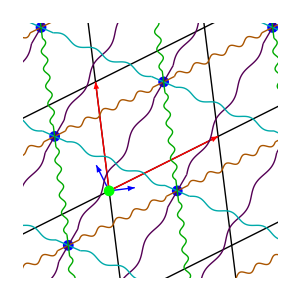

```mathematica
DynamicModule[{aLocDefault={2,1},aLoc={2.75,-0.5},bLocDefault={-1/4,2},bLoc={-0.5,2.0700000000000003},dynamics={{0.24584721225297884,-0.3226832673881821},{{0.31149685517209647,{-0.7789865215574577,0.627040667924986}},{0.13651820911389712,{-0.627040667924986,-0.7789865215574577}}}},dynPlot=Show[{ListPlot[points$37539[nu$37539 #1],PlotRange->{{-windowHalfWidth/2,windowHalfWidth},{-windowHalfWidth/2,windowHalfWidth}},ImageSize->primaryDisplaySize,PlotStyle->Directive[PointSize[Large]]],Graphics[{lines$37539}]}]&,dynTab=1,freqTab=2,k1=0.5,k2=0.5,k3=0.25,k4=0.25,kMax=0.9,lanceTestForceField=0.1,locDependentCalc={"aLoc"->{2.75,-0.5},"bLoc"->{-0.5,2.0700000000000003},"mLoc"->{0.8700000000000001,0.8200000000000003},"latticeBasis"->{{2.75,-0.5},{-0.5,2.0700000000000003}},"latticeNorms"->{2.795084971874737,2.1295304646799496},"latticeUnitVectors"->{{0.9838699100999077,-0.1788854381999832},{-0.2347935417186651,0.9720452627152736}},"numberLatticeLinesToDisplay"->{2,2},"reciprocalBasis"->{{0.3803399173174093,0.09186954524575101},{0.09186954524575101,0.5052824988516306}},"reciprocalNorms"->{0.39127799075423964,0.5135663705787297},"mObliqueComponents"->{0.406228755167662,0.4942581534221406},"mPosFirstCell"->{0.8700000000000001,0.8200000000000003},"pointsDataTable"->{{{-3.63,-2.3200000000000003},{-4.13,-0.25},{-4.63,1.8200000000000003},{-5.13,3.8900000000000006},{-5.63,5.960000000000001}},{{-0.8799999999999999,-2.8200000000000003},{-1.38,-0.75},{-1.88,1.3200000000000003},{-2.38,3.3900000000000006},{-2.88,5.460000000000001}},{{1.87,-3.3200000000000003},{1.37,-1.25},{0.8700000000000001,0.8200000000000003},{0.3700000000000001,2.8900000000000006},{-0.1299999999999999,4.960000000000001}},{{4.62,-3.8200000000000003},{4.12,-1.75},{3.62,0.3200000000000003},{3.12,2.3900000000000006},{2.62,4.460000000000001}},{{7.37,-4.32},{6.87,-2.25},{6.37,-0.17999999999999972},{5.87,1.8900000000000006},{5.37,3.960000000000001}}},"lineTable"->{{Line[{{-4.5,-3.1400000000000006},{6.5,-5.140000000000001}}],Line[{{-5.,-1.0700000000000003},{6.,-3.0700000000000003}}],Line[{{-5.5,1.},{5.5,-1.}}],Line[{{-6.,3.0700000000000003},{5.,1.0700000000000003}}],Line[{{-6.5,5.140000000000001},{4.5,3.1400000000000006}}]},{Line[{{-4.5,-3.1400000000000006},{-6.5,5.140000000000001}}],Line[{{-1.75,-3.6400000000000006},{-3.75,4.640000000000001}}],Line[{{1.,-4.140000000000001},{-1.,4.140000000000001}}],Line[{{3.75,-4.640000000000001},{1.75,3.6400000000000006}}],Line[{{6.5,-5.140000000000001},{4.5,3.1400000000000006}}]}}},mass=10,matrix=(4. 0.1) (projOp[{2.75,-0.5}] 0.5 Sin[0.5 {2.75,-0.5}.#1]^2+projOp[{-0.5,2.0700000000000003}] 0.5 Sin[0.5 {-0.5,2.0700000000000003}.#1]^2+projOp[{2.75,-0.5}+{-0.5,2.0700000000000003}] 0.25 Sin[0.5 {2.25,1.5700000000000003}.#1]^2+projOp[{-0.5,2.0700000000000003}-1. {2.75,-0.5}] 0.25 Sin[0.5 {-3.25,2.5700000000000003}.#1]^2)&,meshSize=8,mLoc={0.8700000000000001,0.8200000000000003},mMax=30,omegaIndex=1,parametersTab=3,primaryDisplaySize=200,qLoc={0.1,-0.1},scale=0.1,springLatticeData={{RGBColor[2/3,0.33333333333333337,0],1,0,0,0,0,1},{RGBColor[0,2/3,0],0,1,0,0,1,0},{RGBColor[0.33333333333333337,0,0.33333333333333337],1,1,0,0,0,0},{RGBColor[0,2/3,2/3],-1,1,1,0,1,0}},springPlotH=Graphics[{{},{{{},{},{Hue[0.67,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.3550000000000004,-2.37},{-3.330236067977501,-2.3587983738762492},{-3.3057426888788095,-2.349084788833448},{-3.2817639320225007,-2.3422016261237513},{-3.2584934919164796,-2.339214205540638},{-3.236055728090002,-2.3408065044950046},{-3.21449349191648,-2.347214205540638},{-3.1937639320225006,-2.3582016261237513},{-3.17374268887881,-2.373084788833448},{-3.154236067977501,-2.3907983738762493},{-3.1350000000000007,-2.41},{-3.1157639320225003,-2.4292016261237515},{-3.0962573111211924,-2.4469152111665524},{-3.0762360679775007,-2.461798373876249},{-3.0555065080835213,-2.4727857944593623},{-3.0339442719100003,-2.4791934955049957},{-3.0115065080835217,-2.4807857944593623},{-2.9882360679775006,-2.477798373876249},{-2.964257311121192,-2.4709152111665524},{-2.9397639320225,-2.4612016261237515},{-2.915,-2.45},{-2.8902360679775017,-2.438798373876249},{-2.86574268887881,-2.429084788833448},{-2.841763932022501,-2.4222016261237513},{-2.81849349191648,-2.419214205540638},{-2.7960557280900016,-2.4208065044950047},{-2.7744934919164796,-2.427214205540638},{-2.7537639320225002,-2.4382016261237514},{-2.7337426888788094,-2.453084788833448},{-2.7142360679775015,-2.470798373876249},{-2.695000000000001,-2.49},{-2.675763932022501,-2.509201626123751},{-2.656257311121192,-2.5269152111665525},{-2.6362360679775003,-2.541798373876249},{-2.615506508083522,-2.5527857944593624},{-2.59394427191,-2.5591934955049958},{-2.5715065080835213,-2.5607857944593624},{-2.548236067977501,-2.557798373876249},{-2.5242573111211914,-2.5509152111665525},{-2.4997639320225007,-2.541201626123751},{-2.4750000000000005,-2.5300000000000002},{-2.4502360679775013,-2.518798373876249},{-2.4257426888788096,-2.509084788833448},{-2.401763932022501,-2.5022016261237514},{-2.3784934919164797,-2.499214205540638},{-2.356055728090002,-2.5008065044950047},{-2.33449349191648,-2.507214205540638},{-2.3137639320225007,-2.5182016261237514},{-2.29374268887881,-2.5330847888334476},{-2.274236067977501,-2.5507983738762494},{-2.255000000000001,-2.5700000000000003},{-2.2357639320225005,-2.589201626123751},{-2.2162573111211916,-2.6069152111665526},{-2.1962360679775,-2.621798373876249},{-2.1755065080835214,-2.6327857944593624},{-2.1539442719100004,-2.6391934955049954},{-2.131506508083522,-2.6407857944593625},{-2.1082360679775007,-2.637798373876249},{-2.084257311121192,-2.6309152111665526},{-2.059763932022501,-2.621201626123751},{-2.035000000000001,-2.6100000000000003},{-2.0102360679775018,-2.598798373876249},{-1.9857426888788101,-2.589084788833448},{-1.9617639320225013,-2.5822016261237515},{-1.9384934919164802,-2.579214205540638},{-1.9160557280900017,-2.580806504495005},{-1.8944934919164798,-2.587214205540638},{-1.8737639320225012,-2.5982016261237515},{-1.8537426888788096,-2.613084788833448},{-1.8342360679775007,-2.6307983738762495},{-1.8150000000000004,-2.6500000000000004},{-1.795763932022501,-2.6692016261237512},{-1.7762573111211921,-2.6869152111665526},{-1.7562360679775004,-2.701798373876249},{-1.735506508083522,-2.7127857944593625},{-1.71394427191,-2.7191934955049955},{-1.6915065080835214,-2.7207857944593625},{-1.6682360679775003,-2.7177983738762492},{-1.6442573111211916,-2.7109152111665527},{-1.6197639320225008,-2.7012016261237513},{-1.5950000000000006,-2.6900000000000004},{-1.5702360679775014,-2.6787983738762486},{-1.5457426888788097,-2.6690847888334477},{-1.521763932022501,-2.6622016261237516},{-1.4984934919164798,-2.6592142055406383},{-1.4760557280900013,-2.660806504495005},{-1.4544934919164794,-2.6672142055406383},{-1.4337639320225009,-2.6782016261237516},{-1.41374268887881,-2.693084788833448},{-1.3942360679775012,-2.710798373876249},{-1.3750000000000009,-2.7300000000000004},{-1.3557639320225006,-2.7492016261237513},{-1.3362573111211917,-2.7669152111665527},{-1.3162360679775,-2.7817983738762493},{-1.2955065080835224,-2.792785794459362},{-1.2739442719100005,-2.7991934955049955},{-1.251506508083522,-2.8007857944593626},{-1.2282360679775008,-2.7977983738762493},{-1.204257311121192,-2.7909152111665527},{-1.1797639320225004,-2.7812016261237513},{-1.1550000000000011,-2.7700000000000005}}]},{Hue[0.9060679774997897,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.1550000000000011,-2.7700000000000005},{-1.1522500000000013,-2.7705},{-1.1495000000000006,-2.771},{-1.1467500000000017,-2.7715},{-1.144000000000001,-2.7720000000000002},{-1.1412500000000012,-2.7725},{-1.1385000000000005,-2.773},{-1.1357500000000016,-2.7735000000000003},{-1.133000000000001,-2.774},{-1.130250000000001,-2.7744999999999997},{-1.1275000000000004,-2.7750000000000004},{-1.1247500000000015,-2.7755},{-1.1220000000000008,-2.7760000000000002},{-1.1192500000000019,-2.7765000000000004},{-1.1165000000000003,-2.777},{-1.1137500000000014,-2.7775},{-1.1110000000000015,-2.778},{-1.1082500000000017,-2.7785},{-1.105500000000001,-2.779},{-1.1027500000000012,-2.7795},{-1.1000000000000014,-2.7800000000000002},{-1.0972500000000016,-2.7805},{-1.094500000000001,-2.781},{-1.091750000000001,-2.7815000000000003},{-1.0890000000000013,-2.782},{-1.0862500000000015,-2.7825},{-1.0835000000000017,-2.7830000000000004},{-1.080750000000001,-2.7835},{-1.0780000000000012,-2.784},{-1.0752500000000014,-2.7845000000000004},{-1.0725000000000016,-2.785},{-1.0697500000000009,-2.7855},{-1.067000000000001,-2.786},{-1.0642500000000013,-2.7865},{-1.0615000000000014,-2.787},{-1.0587500000000007,-2.7875},{-1.056000000000001,-2.7880000000000003},{-1.0532500000000011,-2.7885},{-1.0505000000000013,-2.789},{-1.0477500000000015,-2.7895000000000003},{-1.0450000000000008,-2.79},{-1.042250000000001,-2.7905},{-1.0395000000000012,-2.7910000000000004},{-1.0367500000000014,-2.7915},{-1.0340000000000007,-2.7920000000000003},{-1.0312500000000009,-2.7925000000000004},{-1.028500000000001,-2.793},{-1.0257500000000013,-2.7935},{-1.0230000000000006,-2.7940000000000005},{-1.0202500000000008,-2.7945},{-1.0175000000000018,-2.795},{-1.0147500000000012,-2.7955},{-1.0120000000000013,-2.7960000000000003},{-1.0092500000000006,-2.7965},{-1.0065000000000017,-2.7969999999999997},{-1.003750000000001,-2.7975000000000003},{-1.001000000000002,-2.798},{-0.9982500000000005,-2.7985},{-0.9955000000000016,-2.799},{-0.9927500000000009,-2.7995},{-0.990000000000002,-2.8},{-0.9872500000000004,-2.8005000000000004},{-0.9845000000000015,-2.801},{-0.9817500000000008,-2.8015},{-0.9790000000000019,-2.802},{-0.9762500000000012,-2.8025},{-0.9735000000000014,-2.803},{-0.9707500000000007,-2.8035},{-0.9680000000000017,-2.8040000000000003},{-0.965250000000001,-2.8045},{-0.9625000000000012,-2.805},{-0.9597500000000005,-2.8055000000000003},{-0.9570000000000016,-2.806},{-0.9542500000000009,-2.8065},{-0.9515000000000011,-2.8070000000000004},{-0.9487500000000004,-2.8075},{-0.9460000000000015,-2.808},{-0.9432500000000008,-2.8085000000000004},{-0.940500000000001,-2.809},{-0.9377500000000003,-2.8095000000000003},{-0.9350000000000014,-2.81},{-0.9322500000000007,-2.8105},{-0.9295000000000018,-2.811},{-0.9267500000000002,-2.8115000000000006},{-0.9240000000000013,-2.8120000000000003},{-0.9212500000000015,-2.8125},{-0.9185000000000016,-2.813},{-0.915750000000001,-2.8135000000000003},{-0.9130000000000011,-2.814},{-0.9102500000000013,-2.8145},{-0.9075000000000015,-2.8150000000000004},{-0.9047500000000008,-2.8155},{-0.902000000000001,-2.816},{-0.8992500000000012,-2.8165},{-0.8965000000000014,-2.817},{-0.8937500000000016,-2.8175},{-0.8910000000000009,-2.818},{-0.8882500000000011,-2.8185000000000002},{-0.8855000000000013,-2.819},{-0.8827500000000015,-2.8195},{-0.8800000000000008,-2.8200000000000003}}]},{Hue[0.1421359549995791,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.63,-2.3200000000000003},{-3.62725,-2.3205},{-3.6245000000000003,-2.321},{-3.6217500000000005,-2.3215000000000003},{-3.6190000000000007,-2.322},{-3.61625,-2.3225000000000002},{-3.6135,-2.3230000000000004},{-3.6107500000000003,-2.3235},{-3.6080000000000005,-2.3240000000000003},{-3.60525,-2.3245000000000005},{-3.6025,-2.325},{-3.5997500000000002,-2.3255000000000003},{-3.5970000000000004,-2.3260000000000005},{-3.5942499999999997,-2.3265000000000002},{-3.5915,-2.3270000000000004},{-3.58875,-2.3275000000000006},{-3.5860000000000003,-2.3280000000000003},{-3.5832500000000005,-2.3285000000000005},{-3.5805,-2.329},{-3.57775,-2.3295000000000003},{-3.575,-2.33},{-3.5722500000000004,-2.3305000000000002},{-3.5694999999999997,-2.3310000000000004},{-3.56675,-2.3315},{-3.564,-2.3320000000000003},{-3.5612500000000002,-2.3325000000000005},{-3.5584999999999996,-2.333},{-3.5557499999999997,-2.3335000000000004},{-3.553,-2.3340000000000005},{-3.55025,-2.3345000000000002},{-3.5475000000000003,-2.3350000000000004},{-3.5447499999999996,-2.3355000000000006},{-3.542,-2.3360000000000003},{-3.539250000000001,-2.3365},{-3.536500000000001,-2.337},{-3.5337500000000004,-2.3375000000000004},{-3.5310000000000006,-2.338},{-3.5282500000000008,-2.3385000000000002},{-3.525500000000001,-2.3390000000000004},{-3.5227500000000003,-2.3395},{-3.5200000000000005,-2.3400000000000003},{-3.5172500000000007,-2.3405000000000005},{-3.514500000000001,-2.341},{-3.511750000000001,-2.3415000000000004},{-3.5090000000000003,-2.342},{-3.5062500000000005,-2.3425000000000002},{-3.5035000000000007,-2.343},{-3.500750000000001,-2.3435},{-3.498,-2.3440000000000003},{-3.4952500000000004,-2.3445},{-3.4925000000000006,-2.345},{-3.489750000000001,-2.3455000000000004},{-3.487,-2.346},{-3.4842500000000003,-2.3465000000000003},{-3.4815000000000005,-2.3470000000000004},{-3.4787500000000007,-2.3475},{-3.476000000000001,-2.3480000000000003},{-3.47325,-2.3485000000000005},{-3.4705000000000004,-2.349},{-3.4677500000000006,-2.3495000000000004},{-3.4650000000000007,-2.35},{-3.46225,-2.3505000000000003},{-3.4595000000000002,-2.351},{-3.4567500000000004,-2.3515},{-3.4540000000000006,-2.3520000000000003},{-3.45125,-2.3525},{-3.4485,-2.353},{-3.4457500000000003,-2.3535000000000004},{-3.4430000000000005,-2.354},{-3.4402500000000007,-2.3545000000000003},{-3.4375,-2.3550000000000004},{-3.43475,-2.3555},{-3.4320000000000004,-2.3560000000000003},{-3.4292500000000006,-2.3565000000000005},{-3.4265,-2.357},{-3.42375,-2.3575000000000004},{-3.4210000000000003,-2.3580000000000005},{-3.4182500000000005,-2.3585000000000003},{-3.4154999999999998,-2.3590000000000004},{-3.41275,-2.3595},{-3.41,-2.3600000000000003},{-3.4072500000000003,-2.3605},{-3.4045000000000005,-2.361},{-3.40175,-2.3615000000000004},{-3.399,-2.362},{-3.39625,-2.3625000000000003},{-3.3935000000000004,-2.3630000000000004},{-3.3907499999999997,-2.3635},{-3.388,-2.3640000000000003},{-3.38525,-2.3645000000000005},{-3.3825000000000003,-2.365},{-3.3797499999999996,-2.3655000000000004},{-3.377,-2.3660000000000005},{-3.37425,-2.3665000000000003},{-3.3715,-2.3670000000000004},{-3.3687500000000004,-2.3675000000000006},{-3.3660000000000005,-2.3680000000000003},{-3.36325,-2.3685000000000005},{-3.360500000000001,-2.369},{-3.3577500000000002,-2.3695000000000004},{-3.3550000000000004,-2.37}}]},{Hue[0.37820393249936934,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.8550000000000004,-0.29999999999999993},{-3.8302360679775003,-0.28879837387624874},{-3.8057426888788086,-0.27908478883344756},{-3.7817639320225,-0.2722016261237511},{-3.7584934919164787,-0.2692142055406378},{-3.736055728090001,-0.27080650449500443},{-3.71449349191648,-0.2772142055406377},{-3.6937639320225006,-0.288201626123751},{-3.673742688878809,-0.30308478883344747},{-3.6542360679775,-0.32079837387624877},{-3.635,-0.33999999999999997},{-3.6157639320224995,-0.35920162612375117},{-3.5962573111211924,-0.37691521116655224},{-3.5762360679775007,-0.3917983738762487},{-3.5555065080835213,-0.402785794459362},{-3.5339442719099994,-0.4091934955049953},{-3.511506508083521,-0.41078579445936203},{-3.4882360679774997,-0.40779837387624873},{-3.464257311121191,-0.40091521116655227},{-3.4397639320225,-0.3912016261237512},{-3.415,-0.38},{-3.3902360679775008,-0.3687983738762487},{-3.365742688878809,-0.3590847888334475},{-3.3417639320225003,-0.35220162612375105},{-3.3184934919164792,-0.34921420554063776},{-3.2960557280900016,-0.3508065044950045},{-3.2744934919164796,-0.35721420554063776},{-3.2537639320225002,-0.36820162612375107},{-3.2337426888788086,-0.38308478883344754},{-3.2142360679775006,-0.4007983738762486},{-3.1950000000000003,-0.4199999999999998},{-3.1757639320225,-0.4392016261237509},{-3.156257311121192,-0.4569152111665523},{-3.1362360679775003,-0.4717983738762488},{-3.115506508083521,-0.4827857944593622},{-3.093944271909999,-0.48919349550499536},{-3.0715065080835204,-0.4907857944593622},{-3.0482360679775002,-0.4877983738762487},{-3.0242573111211914,-0.48091521116655234},{-2.9997639320225007,-0.47120162612375094},{-2.9750000000000005,-0.45999999999999985},{-2.9502360679775004,-0.44879837387624866},{-2.9257426888788087,-0.4390847888334476},{-2.9017639320225,-0.4322016261237511},{-2.878493491916479,-0.4292142055406377},{-2.856055728090002,-0.43080650449500446},{-2.83449349191648,-0.4372142055406377},{-2.8137639320225007,-0.44820162612375103},{-2.793742688878809,-0.4630847888334475},{-2.7742360679775,-0.4807983738762488},{-2.755,-0.4999999999999999},{-2.7357639320224996,-0.519201626123751},{-2.7162573111211916,-0.5369152111665524},{-2.6962360679775,-0.5517983738762487},{-2.6755065080835205,-0.562785794459362},{-2.6539442719099995,-0.5691934955049952},{-2.631506508083521,-0.5707857944593621},{-2.6082360679775,-0.5677983738762488},{-2.584257311121192,-0.5609152111665522},{-2.559763932022501,-0.551201626123751},{-2.535000000000001,-0.5399999999999997},{-2.510236067977501,-0.5287983738762486},{-2.4857426888788092,-0.5190847888334477},{-2.4617639320225004,-0.5122016261237511},{-2.4384934919164793,-0.5092142055406378},{-2.4160557280900017,-0.5108065044950046},{-2.3944934919164798,-0.5172142055406378},{-2.3737639320225004,-0.5282016261237511},{-2.3537426888788087,-0.5430847888334477},{-2.3342360679775,-0.5607983738762489},{-2.3149999999999995,-0.5800000000000002},{-2.2957639320225,-0.5992016261237508},{-2.276257311121192,-0.6169152111665522},{-2.2562360679775004,-0.6317983738762488},{-2.235506508083521,-0.6427857944593621},{-2.213944271909999,-0.6491934955049953},{-2.1915065080835205,-0.6507857944593621},{-2.1682360679774995,-0.6477983738762488},{-2.1442573111211916,-0.6409152111665523},{-2.119763932022501,-0.6312016261237509},{-2.0950000000000006,-0.6199999999999998},{-2.0702360679775005,-0.6087983738762485},{-2.045742688878809,-0.5990847888334475},{-2.0217639320225,-0.5922016261237512},{-1.998493491916479,-0.5892142055406379},{-1.9760557280900013,-0.5908065044950047},{-1.9544934919164794,-0.5972142055406379},{-1.9337639320225,-0.6082016261237512},{-1.9137426888788092,-0.6230847888334475},{-1.8942360679775003,-0.6407983738762487},{-1.875,-0.6599999999999998},{-1.8557639320225006,-0.6792016261237509},{-1.8362573111211917,-0.6969152111665525},{-1.8162360679775,-0.7117983738762489},{-1.7955065080835215,-0.722785794459362},{-1.7739442719099996,-0.7291934955049951},{-1.751506508083521,-0.730785794459362},{-1.7282360679775,-0.7277983738762487},{-1.704257311121192,-0.7209152111665521},{-1.6797639320225004,-0.7112016261237509},{-1.6550000000000002,-0.6999999999999998}}]},{Hue[0.6142719099991583,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.6550000000000002,-0.6999999999999998},{-1.6522500000000013,-0.7004999999999998},{-1.6494999999999997,-0.701},{-1.6467500000000008,-0.7014999999999997},{-1.6440000000000001,-0.7019999999999998},{-1.6412500000000012,-0.7024999999999998},{-1.6385000000000005,-0.703},{-1.6357500000000007,-0.7034999999999997},{-1.633,-0.7039999999999998},{-1.630250000000001,-0.7044999999999998},{-1.6275000000000004,-0.705},{-1.6247500000000006,-0.7054999999999999},{-1.6219999999999999,-0.7059999999999998},{-1.619250000000001,-0.7064999999999998},{-1.6165000000000003,-0.707},{-1.6137500000000005,-0.7074999999999999},{-1.6110000000000007,-0.7079999999999999},{-1.6082500000000008,-0.7084999999999998},{-1.605500000000001,-0.7089999999999997},{-1.6027500000000003,-0.7094999999999999},{-1.6000000000000005,-0.7099999999999999},{-1.5972500000000007,-0.7104999999999998},{-1.594500000000001,-0.7109999999999997},{-1.591750000000001,-0.7114999999999999},{-1.5890000000000004,-0.7119999999999999},{-1.5862500000000006,-0.7124999999999998},{-1.5835000000000008,-0.7129999999999997},{-1.580750000000001,-0.7134999999999999},{-1.5780000000000003,-0.7139999999999999},{-1.5752500000000005,-0.7144999999999998},{-1.5725000000000007,-0.7149999999999997},{-1.5697500000000009,-0.7154999999999999},{-1.5670000000000002,-0.7159999999999999},{-1.5642500000000004,-0.7164999999999998},{-1.5615000000000006,-0.7169999999999997},{-1.5587500000000007,-0.7174999999999999},{-1.556000000000001,-0.7179999999999999},{-1.5532500000000002,-0.7184999999999998},{-1.5505000000000004,-0.719},{-1.5477500000000006,-0.7194999999999999},{-1.5450000000000008,-0.7199999999999999},{-1.5422500000000001,-0.7204999999999998},{-1.5395000000000003,-0.721},{-1.5367500000000005,-0.7214999999999999},{-1.5340000000000007,-0.7219999999999999},{-1.53125,-0.7224999999999998},{-1.5285000000000002,-0.723},{-1.5257500000000004,-0.7234999999999999},{-1.5230000000000006,-0.7239999999999999},{-1.5202500000000008,-0.7244999999999998},{-1.517500000000001,-0.7249999999999998},{-1.5147500000000003,-0.7254999999999999},{-1.5120000000000013,-0.7259999999999996},{-1.5092500000000006,-0.7264999999999998},{-1.5065000000000008,-0.7269999999999998},{-1.5037500000000001,-0.7274999999999999},{-1.5010000000000012,-0.7279999999999996},{-1.4982500000000005,-0.7284999999999998},{-1.4955000000000007,-0.7289999999999998},{-1.49275,-0.7294999999999999},{-1.490000000000001,-0.7299999999999996},{-1.4872500000000004,-0.7304999999999998},{-1.4845000000000015,-0.7309999999999998},{-1.48175,-0.7314999999999999},{-1.479000000000001,-0.7319999999999999},{-1.4762500000000003,-0.7325},{-1.4735000000000014,-0.7329999999999998},{-1.4707499999999998,-0.7334999999999999},{-1.4680000000000009,-0.7339999999999999},{-1.4652500000000002,-0.7345},{-1.4625000000000012,-0.7349999999999998},{-1.4597499999999997,-0.7354999999999999},{-1.4570000000000007,-0.7359999999999999},{-1.45425,-0.7365},{-1.4515000000000011,-0.7369999999999998},{-1.4487500000000004,-0.7374999999999999},{-1.4460000000000006,-0.7379999999999999},{-1.44325,-0.7385},{-1.440500000000001,-0.7389999999999998},{-1.4377500000000003,-0.7394999999999999},{-1.4350000000000005,-0.7399999999999999},{-1.4322499999999998,-0.7405},{-1.4295000000000009,-0.7409999999999998},{-1.4267500000000002,-0.7414999999999999},{-1.4240000000000004,-0.7419999999999999},{-1.4212500000000006,-0.7424999999999998},{-1.4185000000000008,-0.7429999999999998},{-1.415750000000001,-0.7434999999999997},{-1.4130000000000011,-0.7439999999999999},{-1.4102500000000004,-0.7444999999999998},{-1.4075000000000006,-0.7449999999999998},{-1.4047500000000008,-0.7454999999999999},{-1.402000000000001,-0.7459999999999999},{-1.3992500000000003,-0.7464999999999998},{-1.3965000000000005,-0.7469999999999998},{-1.3937500000000007,-0.7474999999999999},{-1.391000000000001,-0.7479999999999999},{-1.3882500000000002,-0.7484999999999998},{-1.3855000000000004,-0.7489999999999998},{-1.3827500000000006,-0.7494999999999999},{-1.3800000000000008,-0.7499999999999999}}]},{Hue[0.8503398874989481,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.13,-0.25},{-4.12725,-0.25049999999999994},{-4.124499999999999,-0.251},{-4.12175,-0.25149999999999995},{-4.119,-0.252},{-4.11625,-0.25249999999999995},{-4.113499999999999,-0.253},{-4.1107499999999995,-0.25350000000000006},{-4.108,-0.254},{-4.10525,-0.25450000000000006},{-4.1025,-0.255},{-4.099749999999999,-0.25550000000000006},{-4.0969999999999995,-0.256},{-4.09425,-0.25650000000000006},{-4.0915,-0.257},{-4.088749999999999,-0.25750000000000006},{-4.085999999999999,-0.258},{-4.08325,-0.25850000000000006},{-4.0805,-0.259},{-4.077749999999999,-0.25950000000000006},{-4.074999999999999,-0.26},{-4.0722499999999995,-0.26050000000000006},{-4.0695,-0.261},{-4.06675,-0.26150000000000007},{-4.063999999999999,-0.262},{-4.061249999999999,-0.26250000000000007},{-4.0584999999999996,-0.263},{-4.05575,-0.26350000000000007},{-4.052999999999999,-0.264},{-4.050249999999999,-0.26450000000000007},{-4.047499999999999,-0.265},{-4.04475,-0.26550000000000007},{-4.041999999999999,-0.266},{-4.03925,-0.26649999999999996},{-4.0365,-0.2669999999999999},{-4.03375,-0.26749999999999996},{-4.031000000000001,-0.2679999999999999},{-4.02825,-0.26849999999999996},{-4.0255,-0.2689999999999999},{-4.02275,-0.26949999999999996},{-4.0200000000000005,-0.2699999999999999},{-4.01725,-0.27049999999999996},{-4.0145,-0.2709999999999999},{-4.01175,-0.27149999999999996},{-4.009,-0.2719999999999999},{-4.00625,-0.27249999999999996},{-4.0035,-0.2729999999999999},{-4.00075,-0.27349999999999997},{-3.998,-0.2739999999999999},{-3.9952500000000004,-0.27449999999999997},{-3.9924999999999997,-0.2749999999999999},{-3.98975,-0.27549999999999997},{-3.987,-0.2759999999999999},{-3.9842500000000003,-0.27649999999999997},{-3.9814999999999996,-0.2769999999999999},{-3.97875,-0.27749999999999997},{-3.976,-0.2779999999999999},{-3.97325,-0.27849999999999997},{-3.9704999999999995,-0.2789999999999999},{-3.9677499999999997,-0.27949999999999997},{-3.965,-0.28},{-3.96225,-0.28049999999999997},{-3.9595000000000002,-0.281},{-3.9567499999999995,-0.2815},{-3.9539999999999997,-0.28200000000000003},{-3.95125,-0.2825},{-3.9485,-0.28300000000000003},{-3.9457499999999994,-0.2835},{-3.9429999999999996,-0.28400000000000003},{-3.94025,-0.2845},{-3.9375,-0.28500000000000003},{-3.9347499999999993,-0.2855},{-3.9319999999999995,-0.28600000000000003},{-3.9292499999999997,-0.2865},{-3.9265,-0.28700000000000003},{-3.92375,-0.2875},{-3.9209999999999994,-0.28800000000000003},{-3.9182499999999996,-0.2885},{-3.9154999999999998,-0.28900000000000003},{-3.91275,-0.2895},{-3.9099999999999993,-0.29000000000000004},{-3.9072499999999994,-0.2905},{-3.9044999999999996,-0.29100000000000004},{-3.90175,-0.2915},{-3.898999999999999,-0.29200000000000004},{-3.8962499999999993,-0.2925},{-3.8934999999999995,-0.29300000000000004},{-3.8907499999999997,-0.2935},{-3.888,-0.29400000000000004},{-3.885249999999999,-0.2945000000000001},{-3.8824999999999994,-0.29500000000000004},{-3.8797499999999996,-0.2955000000000001},{-3.877,-0.29600000000000004},{-3.874249999999999,-0.2965000000000001},{-3.8714999999999993,-0.29700000000000004},{-3.8687499999999995,-0.2975000000000001},{-3.8660000000000005,-0.29799999999999993},{-3.863249999999999,-0.2985000000000001},{-3.8605,-0.29899999999999993},{-3.8577499999999993,-0.2995000000000001},{-3.8550000000000004,-0.29999999999999993}}]},{Hue[0.08640786499873876,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.3549999999999995,1.7700000000000005},{-4.330236067977499,1.7812016261237515},{-4.305742688878808,1.7909152111665527},{-4.281763932022499,1.7977983738762493},{-4.258493491916479,1.8007857944593626},{-4.236055728090001,1.799193495504996},{-4.214493491916479,1.7927857944593626},{-4.1937639320225,1.7817983738762493},{-4.173742688878808,1.7669152111665527},{-4.154236067977499,1.7492016261237517},{-4.135,1.7300000000000004},{-4.1157639320224995,1.7107983738762491},{-4.0962573111211915,1.6930847888334482},{-4.0762360679775,1.6782016261237518},{-4.05550650808352,1.6672142055406383},{-4.0339442719099985,1.660806504495005},{-4.01150650808352,1.6592142055406383},{-3.9882360679774997,1.6622016261237516},{-3.964257311121191,1.669084788833448},{-3.9397639320224993,1.6787983738762493},{-3.914999999999999,1.6900000000000004},{-3.8902360679775,1.7012016261237515},{-3.8657426888788082,1.7109152111665527},{-3.8417639320224994,1.7177983738762492},{-3.8184934919164792,1.7207857944593625},{-3.7960557280900007,1.719193495504996},{-3.7744934919164788,1.7127857944593625},{-3.7537639320224994,1.7017983738762492},{-3.7337426888788077,1.6869152111665526},{-3.7142360679774997,1.6692016261237517},{-3.6950000000000003,1.6500000000000006},{-3.6757639320225,1.6307983738762493},{-3.656257311121191,1.613084788833448},{-3.6362360679774994,1.5982016261237515},{-3.61550650808352,1.5872142055406382},{-3.593944271909998,1.580806504495005},{-3.5715065080835195,1.5792142055406382},{-3.5482360679775002,1.5822016261237517},{-3.5242573111211906,1.589084788833448},{-3.4997639320225,1.5987983738762495},{-3.4749999999999996,1.6100000000000005},{-3.4502360679774995,1.6212016261237516},{-3.425742688878808,1.6309152111665526},{-3.4017639320225,1.6377983738762492},{-3.378493491916479,1.6407857944593625},{-3.356055728090001,1.6391934955049958},{-3.3344934919164793,1.6327857944593627},{-3.3137639320225,1.6217983738762494},{-3.293742688878808,1.6069152111665528},{-3.2742360679774993,1.5892016261237516},{-3.255,1.5700000000000005},{-3.2357639320224996,1.5507983738762492},{-3.2162573111211907,1.533084788833448},{-3.196236067977499,1.5182016261237514},{-3.1755065080835196,1.5072142055406381},{-3.1539442719099986,1.5008065044950052},{-3.13150650808352,1.4992142055406383},{-3.1082360679775,1.5022016261237516},{-3.084257311121191,1.5090847888334482},{-3.0597639320225003,1.5187983738762492},{-3.035,1.5300000000000005},{-3.0102360679775,1.5412016261237516},{-2.9857426888788083,1.5509152111665527},{-2.9617639320225004,1.5577983738762493},{-2.9384934919164793,1.5607857944593626},{-2.916055728090001,1.5591934955049958},{-2.894493491916479,1.5527857944593626},{-2.8737639320224995,1.5417983738762493},{-2.8537426888788078,1.5269152111665527},{-2.834236067977499,1.5092016261237515},{-2.8149999999999995,1.4900000000000002},{-2.7957639320225,1.4707983738762493},{-2.7762573111211912,1.4530847888334482},{-2.7562360679774995,1.4382016261237516},{-2.73550650808352,1.4272142055406383},{-2.713944271909998,1.4208065044950051},{-2.6915065080835205,1.4192142055406383},{-2.6682360679774995,1.4222016261237516},{-2.6442573111211907,1.4290847888334481},{-2.6197639320225,1.4387983738762493},{-2.5949999999999998,1.4500000000000004},{-2.5702360679774996,1.4612016261237517},{-2.545742688878808,1.4709152111665529},{-2.5217639320225,1.4777983738762492},{-2.498493491916479,1.4807857944593625},{-2.4760557280900004,1.4791934955049957},{-2.4544934919164785,1.4727857944593625},{-2.433763932022499,1.4617983738762492},{-2.4137426888788083,1.4469152111665526},{-2.3942360679774994,1.4292016261237515},{-2.375,1.4100000000000004},{-2.3557639320224997,1.3907983738762493},{-2.336257311121191,1.3730847888334479},{-2.316236067977499,1.3582016261237515},{-2.2955065080835206,1.3472142055406384},{-2.2739442719099987,1.3408065044950053},{-2.251506508083521,1.3392142055406384},{-2.2282360679775,1.3422016261237517},{-2.204257311121191,1.349084788833448},{-2.1797639320224995,1.3587983738762492},{-2.1549999999999994,1.3700000000000003}}]},{Hue[0.3224758424985268,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.1549999999999994,1.3700000000000003},{-2.1522500000000004,1.3695000000000006},{-2.1494999999999997,1.3690000000000004},{-2.14675,1.3685000000000005},{-2.1439999999999992,1.3680000000000003},{-2.1412500000000003,1.3675000000000006},{-2.1384999999999996,1.3670000000000004},{-2.1357500000000007,1.3665000000000005},{-2.132999999999999,1.3660000000000003},{-2.13025,1.3655000000000006},{-2.1274999999999995,1.3650000000000004},{-2.1247500000000006,1.3645000000000005},{-2.121999999999999,1.3640000000000003},{-2.11925,1.3635000000000006},{-2.1164999999999994,1.3630000000000004},{-2.1137500000000005,1.3625000000000005},{-2.1109999999999998,1.3620000000000005},{-2.10825,1.3615000000000006},{-2.1055,1.3610000000000004},{-2.1027500000000003,1.3605000000000005},{-2.1000000000000005,1.3600000000000005},{-2.09725,1.3595000000000006},{-2.0945,1.3590000000000004},{-2.09175,1.3585000000000005},{-2.0890000000000004,1.3580000000000005},{-2.0862499999999997,1.3575000000000006},{-2.0835,1.3570000000000004},{-2.08075,1.3565000000000005},{-2.0780000000000003,1.3560000000000005},{-2.0752499999999996,1.3555000000000006},{-2.0725,1.3550000000000004},{-2.06975,1.3545000000000005},{-2.067,1.3540000000000005},{-2.0642500000000004,1.3535000000000004},{-2.0614999999999997,1.3530000000000004},{-2.05875,1.3525000000000005},{-2.056,1.3520000000000005},{-2.0532500000000002,1.3515000000000004},{-2.0504999999999995,1.3510000000000004},{-2.0477499999999997,1.3505000000000005},{-2.045,1.3500000000000005},{-2.04225,1.3495000000000004},{-2.0394999999999994,1.3490000000000004},{-2.0367499999999996,1.3485000000000005},{-2.034,1.3480000000000005},{-2.03125,1.3475000000000004},{-2.0285,1.3470000000000004},{-2.0257499999999995,1.3465000000000005},{-2.0229999999999997,1.3460000000000005},{-2.02025,1.3455000000000004},{-2.017500000000001,1.3450000000000006},{-2.0147499999999994,1.3445000000000005},{-2.0120000000000005,1.3440000000000005},{-2.0092499999999998,1.3435000000000004},{-2.006500000000001,1.3430000000000006},{-2.0037499999999993,1.3425000000000005},{-2.0010000000000003,1.3420000000000005},{-1.9982499999999996,1.3415000000000004},{-1.9955000000000007,1.3410000000000006},{-1.99275,1.3405000000000005},{-1.9900000000000002,1.3400000000000005},{-1.9872499999999995,1.3395000000000004},{-1.9845000000000006,1.3390000000000006},{-1.98175,1.3385000000000005},{-1.979,1.3380000000000005},{-1.9762499999999994,1.3375000000000004},{-1.9735000000000005,1.3370000000000006},{-1.9707499999999998,1.3365000000000005},{-1.968,1.3360000000000005},{-1.9652499999999993,1.3355000000000004},{-1.9625000000000004,1.3350000000000006},{-1.9597499999999997,1.3345000000000005},{-1.9570000000000007,1.3340000000000005},{-1.9542499999999992,1.3335000000000004},{-1.9515000000000002,1.3330000000000006},{-1.9487499999999995,1.3325000000000005},{-1.9460000000000006,1.3320000000000005},{-1.943249999999999,1.3315000000000003},{-1.9405000000000001,1.3310000000000006},{-1.9377499999999994,1.3305000000000005},{-1.9350000000000005,1.3300000000000005},{-1.932249999999999,1.3295000000000003},{-1.9295,1.3290000000000006},{-1.9267499999999993,1.3285000000000005},{-1.9240000000000004,1.3280000000000005},{-1.9212500000000006,1.3275000000000006},{-1.9184999999999999,1.3270000000000004},{-1.91575,1.3265000000000005},{-1.9130000000000003,1.3260000000000005},{-1.9102500000000004,1.3255000000000006},{-1.9074999999999998,1.3250000000000004},{-1.90475,1.3245000000000005},{-1.9020000000000001,1.3240000000000005},{-1.8992500000000003,1.3235000000000006},{-1.8964999999999996,1.3230000000000004},{-1.8937499999999998,1.3225000000000005},{-1.891,1.3220000000000005},{-1.8882500000000002,1.3215000000000006},{-1.8855000000000004,1.3210000000000004},{-1.8827499999999997,1.3205000000000005},{-1.88,1.3200000000000005}}]},{Hue[0.5585438199983166,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.629999999999999,1.8200000000000003},{-4.627249999999999,1.8195000000000003},{-4.624499999999999,1.8190000000000004},{-4.621749999999999,1.8185000000000002},{-4.618999999999999,1.8180000000000003},{-4.616249999999999,1.8175000000000003},{-4.613499999999999,1.8170000000000002},{-4.610749999999999,1.8165000000000004},{-4.607999999999999,1.8160000000000003},{-4.605249999999999,1.8155000000000003},{-4.602499999999999,1.8150000000000004},{-4.599749999999999,1.8145000000000002},{-4.596999999999999,1.8140000000000003},{-4.594249999999999,1.8135000000000003},{-4.591499999999999,1.8130000000000002},{-4.588749999999999,1.8125000000000004},{-4.5859999999999985,1.8120000000000003},{-4.583249999999999,1.8115000000000003},{-4.580499999999999,1.8110000000000004},{-4.577749999999999,1.8105000000000002},{-4.574999999999998,1.8100000000000003},{-4.572249999999999,1.8095000000000003},{-4.569499999999999,1.8090000000000002},{-4.566749999999999,1.8085000000000004},{-4.563999999999999,1.8080000000000003},{-4.5612499999999985,1.8075000000000003},{-4.558499999999999,1.8070000000000004},{-4.555749999999999,1.8065000000000002},{-4.552999999999999,1.8060000000000003},{-4.550249999999998,1.8055000000000003},{-4.5474999999999985,1.8050000000000002},{-4.544749999999999,1.8045000000000002},{-4.541999999999999,1.8040000000000003},{-4.539249999999999,1.8035000000000005},{-4.536499999999999,1.8030000000000004},{-4.5337499999999995,1.8025000000000004},{-4.531,1.8020000000000005},{-4.52825,1.8015000000000003},{-4.525499999999999,1.8010000000000004},{-4.522749999999999,1.8005000000000004},{-4.52,1.8000000000000003},{-4.51725,1.7995000000000005},{-4.514499999999999,1.7990000000000004},{-4.511749999999999,1.7985000000000004},{-4.5089999999999995,1.7980000000000005},{-4.50625,1.7975000000000003},{-4.503499999999999,1.7970000000000004},{-4.500749999999999,1.7965000000000004},{-4.497999999999999,1.7960000000000003},{-4.4952499999999995,1.7955000000000005},{-4.4925,1.7950000000000004},{-4.489749999999999,1.7945000000000004},{-4.486999999999999,1.7940000000000005},{-4.484249999999999,1.7935000000000003},{-4.4815,1.7930000000000004},{-4.478749999999999,1.7925000000000004},{-4.475999999999999,1.7920000000000003},{-4.473249999999999,1.7915000000000003},{-4.4704999999999995,1.7910000000000004},{-4.467749999999999,1.7905000000000002},{-4.464999999999999,1.7900000000000005},{-4.462249999999999,1.7895000000000003},{-4.459499999999999,1.7890000000000004},{-4.4567499999999995,1.7885000000000004},{-4.453999999999999,1.7880000000000003},{-4.451249999999999,1.7875000000000003},{-4.448499999999999,1.7870000000000004},{-4.445749999999999,1.7865000000000002},{-4.442999999999999,1.7860000000000005},{-4.440249999999999,1.7855000000000003},{-4.437499999999999,1.7850000000000004},{-4.434749999999999,1.7845000000000004},{-4.431999999999999,1.7840000000000003},{-4.429249999999999,1.7835000000000003},{-4.426499999999999,1.7830000000000004},{-4.423749999999999,1.7825000000000002},{-4.420999999999999,1.7820000000000005},{-4.418249999999999,1.7815000000000003},{-4.415499999999999,1.7810000000000004},{-4.412749999999999,1.7805000000000004},{-4.409999999999999,1.7800000000000002},{-4.407249999999999,1.7795000000000003},{-4.404499999999999,1.7790000000000004},{-4.401749999999999,1.7785000000000002},{-4.398999999999999,1.7780000000000002},{-4.396249999999998,1.7775000000000003},{-4.393499999999999,1.7770000000000001},{-4.390749999999999,1.7765000000000004},{-4.387999999999999,1.7760000000000002},{-4.385249999999999,1.7755000000000003},{-4.3824999999999985,1.7750000000000004},{-4.379749999999999,1.7745000000000002},{-4.376999999999999,1.7740000000000002},{-4.374249999999999,1.7735000000000003},{-4.371499999999998,1.7730000000000001},{-4.368749999999999,1.7725000000000004},{-4.366,1.7720000000000005},{-4.363249999999999,1.7715000000000003},{-4.360499999999999,1.7710000000000004},{-4.3577499999999985,1.7705000000000002},{-4.3549999999999995,1.7700000000000005}}]},{Hue[0.7946117974981064,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-4.855000000000001,3.8400000000000003},{-4.830236067977501,3.8512016261237516},{-4.8057426888788095,3.8609152111665526},{-4.781763932022501,3.867798373876249},{-4.75849349191648,3.870785794459362},{-4.736055728090002,3.8691934955049954},{-4.714493491916481,3.8627857944593624},{-4.6937639320225015,3.851798373876249},{-4.67374268887881,3.8369152111665525},{-4.654236067977501,3.8192016261237516},{-4.635000000000001,3.8000000000000003},{-4.6157639320225,3.780798373876249},{-4.596257311121192,3.763084788833448},{-4.576236067977502,3.7482016261237514},{-4.555506508083522,3.737214205540638},{-4.53394427191,3.730806504495005},{-4.511506508083522,3.729214205540638},{-4.488236067977501,3.7322016261237514},{-4.464257311121192,3.7390847888334475},{-4.439763932022501,3.748798373876249},{-4.415000000000001,3.7600000000000002},{-4.390236067977502,3.7712016261237515},{-4.36574268887881,3.7809152111665525},{-4.341763932022501,3.787798373876249},{-4.31849349191648,3.7907857944593624},{-4.296055728090002,3.7891934955049953},{-4.2744934919164805,3.7827857944593624},{-4.253763932022501,3.771798373876249},{-4.2337426888788094,3.7569152111665525},{-4.2142360679775015,3.7392016261237515},{-4.195000000000001,3.72},{-4.175763932022501,3.700798373876249},{-4.156257311121193,3.683084788833448},{-4.136236067977501,3.6682016261237513},{-4.115506508083522,3.657214205540638},{-4.09394427191,3.650806504495005},{-4.071506508083521,3.649214205540638},{-4.048236067977501,3.6522016261237518},{-4.0242573111211914,3.659084788833448},{-3.9997639320225016,3.6687983738762493},{-3.9750000000000014,3.68},{-3.9502360679775013,3.6912016261237515},{-3.9257426888788096,3.7009152111665524},{-3.901763932022501,3.707798373876249},{-3.8784934919164797,3.7107857944593623},{-3.856055728090002,3.7091934955049957},{-3.834493491916481,3.7027857944593627},{-3.8137639320225016,3.6917983738762494},{-3.79374268887881,3.676915211166553},{-3.774236067977501,3.6592016261237514},{-3.755000000000001,3.64},{-3.7357639320225005,3.620798373876249},{-3.7162573111211925,3.603084788833448},{-3.696236067977501,3.5882016261237513},{-3.6755065080835214,3.577214205540638},{-3.6539442719100004,3.570806504495005},{-3.631506508083522,3.5692142055406384},{-3.6082360679775007,3.5722016261237517},{-3.584257311121193,3.5790847888334483},{-3.559763932022502,3.588798373876249},{-3.535000000000002,3.6000000000000005},{-3.5102360679775018,3.6112016261237514},{-3.48574268887881,3.620915211166553},{-3.4617639320225013,3.6277983738762494},{-3.4384934919164802,3.6307857944593627},{-3.416055728090001,3.6291934955049956},{-3.3944934919164798,3.6227857944593627},{-3.3737639320225004,3.6117983738762494},{-3.3537426888788087,3.5969152111665528},{-3.3342360679775016,3.5792016261237514},{-3.3150000000000013,3.5599999999999996},{-3.295763932022501,3.5407983738762487},{-3.276257311121192,3.523084788833448},{-3.256236067977502,3.5082016261237516},{-3.235506508083523,3.4972142055406383},{-3.21394427191,3.490806504495005},{-3.1915065080835205,3.489214205540638},{-3.1682360679775012,3.4922016261237516},{-3.1442573111211924,3.499084788833448},{-3.119763932022501,3.508798373876249},{-3.0950000000000006,3.5200000000000005},{-3.0702360679775005,3.5312016261237513},{-3.0457426888788106,3.5409152111665527},{-3.021763932022502,3.5477983738762493},{-2.9984934919164807,3.5507857944593626},{-2.9760557280900013,3.5491934955049955},{-2.9544934919164803,3.5427857944593626},{-2.933763932022501,3.5317983738762493},{-2.913742688878809,3.5169152111665527},{-2.8942360679775003,3.4992016261237513},{-2.8750000000000018,3.4800000000000004},{-2.8557639320225015,3.4607983738762496},{-2.8362573111211926,3.443084788833448},{-2.816236067977501,3.4282016261237516},{-2.7955065080835215,3.4172142055406383},{-2.7739442719100023,3.410806504495005},{-2.751506508083523,3.4092142055406383},{-2.7282360679775017,3.4122016261237516},{-2.704257311121193,3.419084788833448},{-2.6797639320225013,3.428798373876249},{-2.655000000000001,3.4400000000000004}}]},{Hue[0.030679774997896203,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.655000000000001,3.4400000000000004},{-2.652250000000002,3.4395000000000007},{-2.6495000000000015,3.439},{-2.6467500000000026,3.4385000000000003},{-2.644,3.438},{-2.641250000000001,3.4375000000000004},{-2.6385000000000005,3.4370000000000003},{-2.6357500000000016,3.4365000000000006},{-2.633000000000001,3.436},{-2.630250000000002,3.4355},{-2.6275000000000013,3.4350000000000005},{-2.6247500000000024,3.4345000000000003},{-2.6220000000000017,3.434},{-2.619250000000001,3.4335000000000004},{-2.6165000000000003,3.4330000000000003},{-2.6137500000000014,3.4325},{-2.6110000000000007,3.4320000000000004},{-2.6082500000000017,3.4315000000000007},{-2.605500000000003,3.4310000000000005},{-2.602750000000002,3.4305000000000003},{-2.6000000000000014,3.43},{-2.5972500000000007,3.4295},{-2.594500000000002,3.4290000000000003},{-2.591750000000001,3.4285000000000005},{-2.5890000000000004,3.428},{-2.5862500000000015,3.4275},{-2.5835000000000026,3.4270000000000005},{-2.580750000000002,3.4265000000000003},{-2.578000000000001,3.426},{-2.5752500000000023,3.4255000000000004},{-2.5725000000000016,3.4250000000000007},{-2.569750000000001,3.4245},{-2.567,3.4240000000000004},{-2.5642500000000013,3.4235},{-2.5615000000000023,3.4230000000000005},{-2.5587500000000016,3.4225000000000003},{-2.556000000000001,3.422},{-2.553250000000002,3.4215},{-2.550500000000003,3.4210000000000003},{-2.5477500000000006,3.4205000000000005},{-2.545,3.42},{-2.542250000000001,3.4195},{-2.539500000000002,3.4190000000000005},{-2.5367500000000014,3.4185000000000003},{-2.5340000000000007,3.418},{-2.5312500000000018,3.4175000000000004},{-2.528500000000003,3.4170000000000007},{-2.5257500000000004,3.4165},{-2.5229999999999997,3.4160000000000004},{-2.5202500000000008,3.4155},{-2.517500000000002,3.4150000000000005},{-2.514750000000001,3.4145000000000003},{-2.5120000000000022,3.4140000000000006},{-2.5092500000000015,3.4135},{-2.5065000000000026,3.4130000000000003},{-2.503750000000002,3.4125000000000005},{-2.5010000000000012,3.4120000000000004},{-2.4982500000000005,3.4115},{-2.4955000000000016,3.4110000000000005},{-2.492750000000001,3.4105000000000003},{-2.490000000000002,3.41},{-2.4872500000000013,3.4095000000000004},{-2.4845000000000024,3.4090000000000007},{-2.4817500000000017,3.4085},{-2.4790000000000028,3.4080000000000004},{-2.4762500000000003,3.4075},{-2.4735000000000014,3.4070000000000005},{-2.4707500000000007,3.4065000000000003},{-2.4680000000000017,3.4060000000000006},{-2.465250000000001,3.4055},{-2.462500000000002,3.4050000000000002},{-2.4597500000000014,3.4045000000000005},{-2.4570000000000025,3.4040000000000004},{-2.45425,3.4035},{-2.451500000000001,3.4030000000000005},{-2.4487500000000004,3.4025000000000003},{-2.4460000000000015,3.402},{-2.443250000000001,3.4015000000000004},{-2.440500000000002,3.4010000000000002},{-2.437750000000001,3.4005},{-2.4350000000000023,3.4000000000000004},{-2.4322500000000016,3.3995},{-2.429500000000001,3.399},{-2.42675,3.3985000000000003},{-2.4240000000000013,3.3980000000000006},{-2.4212500000000023,3.3975000000000004},{-2.4185000000000016,3.3970000000000002},{-2.415750000000001,3.3965},{-2.413000000000002,3.3960000000000004},{-2.410250000000003,3.3955},{-2.4075000000000024,3.3950000000000005},{-2.40475,3.3945},{-2.402000000000001,3.394},{-2.399250000000002,3.3935000000000004},{-2.3965000000000014,3.3930000000000002},{-2.3937500000000007,3.3925},{-2.391000000000002,3.3920000000000003},{-2.388250000000003,3.3915000000000006},{-2.385500000000002,3.391},{-2.3827499999999997,3.3905000000000003},{-2.380000000000001,3.3900000000000006}}]},{Hue[0.266747752497686,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.130000000000001,3.89},{-5.127250000000001,3.8895},{-5.1245,3.8890000000000002},{-5.1217500000000005,3.8885},{-5.119000000000001,3.888},{-5.116250000000001,3.8875},{-5.1135,3.8870000000000005},{-5.11075,3.8865},{-5.1080000000000005,3.886},{-5.105250000000001,3.8855000000000004},{-5.1025,3.8850000000000002},{-5.09975,3.8845},{-5.097,3.8840000000000003},{-5.094250000000001,3.8835},{-5.091500000000001,3.883},{-5.08875,3.8825000000000003},{-5.086,3.882},{-5.0832500000000005,3.8815},{-5.080500000000001,3.8810000000000002},{-5.07775,3.8805},{-5.075,3.88},{-5.07225,3.8795},{-5.069500000000001,3.879},{-5.06675,3.8785},{-5.064,3.878},{-5.06125,3.8775000000000004},{-5.0585,3.877},{-5.055750000000001,3.8765},{-5.053,3.8760000000000003},{-5.05025,3.8755},{-5.0475,3.875},{-5.0447500000000005,3.8745000000000003},{-5.042,3.874},{-5.039250000000001,3.8735},{-5.036500000000001,3.873},{-5.033750000000001,3.8725000000000005},{-5.031000000000001,3.8720000000000003},{-5.028250000000001,3.8715},{-5.025500000000001,3.8710000000000004},{-5.022750000000001,3.8705000000000003},{-5.020000000000001,3.87},{-5.017250000000001,3.8695000000000004},{-5.014500000000001,3.869},{-5.011750000000001,3.8685},{-5.009000000000001,3.8680000000000003},{-5.0062500000000005,3.8675},{-5.003500000000001,3.867},{-5.000750000000001,3.8665000000000003},{-4.998000000000001,3.866},{-4.99525,3.8655},{-4.992500000000001,3.865},{-4.989750000000001,3.8645000000000005},{-4.987000000000001,3.864},{-4.984250000000001,3.8635},{-4.9815000000000005,3.8630000000000004},{-4.978750000000001,3.8625000000000003},{-4.976000000000001,3.862},{-4.973250000000001,3.8615000000000004},{-4.9705,3.861},{-4.9677500000000006,3.8605},{-4.965000000000001,3.8600000000000003},{-4.962250000000001,3.8595},{-4.9595,3.859},{-4.95675,3.8585000000000003},{-4.954000000000001,3.858},{-4.951250000000001,3.8575},{-4.948500000000001,3.857},{-4.94575,3.8565000000000005},{-4.9430000000000005,3.856},{-4.940250000000001,3.8555},{-4.937500000000001,3.8550000000000004},{-4.93475,3.8545000000000003},{-4.932,3.854},{-4.929250000000001,3.8535000000000004},{-4.926500000000001,3.853},{-4.92375,3.8525},{-4.921,3.8520000000000003},{-4.9182500000000005,3.8515},{-4.915500000000001,3.851},{-4.912750000000001,3.8505000000000003},{-4.91,3.85},{-4.90725,3.8495},{-4.9045000000000005,3.849},{-4.901750000000001,3.8485},{-4.899,3.848},{-4.89625,3.8475},{-4.8935,3.8470000000000004},{-4.890750000000001,3.8465},{-4.888,3.846},{-4.88525,3.8455000000000004},{-4.8825,3.845},{-4.8797500000000005,3.8445},{-4.877000000000001,3.8440000000000003},{-4.87425,3.8435},{-4.8715,3.843},{-4.86875,3.8425000000000002},{-4.866000000000001,3.8420000000000005},{-4.86325,3.8415},{-4.860500000000001,3.841},{-4.85775,3.8405},{-4.855000000000001,3.8400000000000003}}]},{Hue[0.5028157299974758,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.355,5.910000000000001},{-5.3302360679775,5.921201626123752},{-5.305742688878809,5.930915211166553},{-5.2817639320225,5.93779837387625},{-5.258493491916479,5.940785794459363},{-5.236055728089999,5.9391934955049965},{-5.214493491916478,5.932785794459363},{-5.193763932022499,5.92179837387625},{-5.173742688878809,5.906915211166554},{-5.1542360679775,5.889201626123753},{-5.135,5.870000000000001},{-5.115763932022501,5.85079837387625},{-5.096257311121192,5.833084788833449},{-5.076236067977501,5.818201626123752},{-5.055506508083521,5.807214205540639},{-5.03394427191,5.8008065044950055},{-5.011506508083521,5.799214205540639},{-4.9882360679775,5.802201626123752},{-4.964257311121191,5.809084788833449},{-4.939763932022499,5.81879837387625},{-4.914999999999999,5.830000000000001},{-4.890236067977499,5.841201626123752},{-4.865742688878807,5.850915211166553},{-4.8417639320224986,5.85779837387625},{-4.818493491916479,5.860785794459363},{-4.796055728090002,5.8591934955049965},{-4.7744934919164805,5.852785794459363},{-4.753763932022501,5.84179837387625},{-4.7337426888788094,5.826915211166554},{-4.714236067977501,5.809201626123753},{-4.695,5.790000000000001},{-4.6757639320225,5.77079837387625},{-4.656257311121191,5.753084788833449},{-4.636236067977499,5.738201626123752},{-4.61550650808352,5.727214205540639},{-4.593944271909999,5.720806504495005},{-4.5715065080835195,5.719214205540639},{-4.5482360679774985,5.722201626123752},{-4.5242573111211914,5.729084788833449},{-4.4997639320225,5.73879837387625},{-4.475,5.750000000000001},{-4.4502360679774995,5.761201626123753},{-4.42574268887881,5.770915211166553},{-4.401763932022501,5.77779837387625},{-4.37849349191648,5.780785794459364},{-4.35605572809,5.779193495504996},{-4.334493491916479,5.772785794459363},{-4.3137639320225,5.76179837387625},{-4.293742688878808,5.746915211166554},{-4.274236067977499,5.729201626123753},{-4.254999999999999,5.710000000000001},{-4.2357639320225005,5.69079837387625},{-4.216257311121192,5.673084788833449},{-4.1962360679775,5.658201626123752},{-4.1755065080835205,5.647214205540639},{-4.1539442719099995,5.640806504495005},{-4.13150650808352,5.639214205540639},{-4.108236067977499,5.642201626123752},{-4.084257311121192,5.649084788833449},{-4.0597639320225,5.65879837387625},{-4.035,5.670000000000002},{-4.0102360679775,5.681201626123753},{-3.9857426888788083,5.690915211166553},{-3.9617639320224995,5.69779837387625},{-3.9384934919164802,5.700785794459364},{-3.916055728090001,5.699193495504996},{-3.8944934919164798,5.692785794459363},{-3.8737639320225004,5.68179837387625},{-3.8537426888788087,5.666915211166554},{-3.8342360679775,5.6492016261237525},{-3.8149999999999995,5.630000000000001},{-3.795763932022501,5.61079837387625},{-3.776257311121192,5.593084788833449},{-3.7562360679775004,5.578201626123753},{-3.735506508083521,5.5672142055406395},{-3.71394427191,5.560806504495006},{-3.6915065080835205,5.5592142055406395},{-3.6682360679775012,5.562201626123752},{-3.6442573111211924,5.5690847888334485},{-3.619763932022501,5.57879837387625},{-3.5950000000000006,5.590000000000002},{-3.5702360679775005,5.6012016261237525},{-3.545742688878809,5.610915211166554},{-3.5217639320225,5.61779837387625},{-3.498493491916479,5.620785794459364},{-3.4760557280899995,5.619193495504996},{-3.4544934919164785,5.612785794459363},{-3.433763932022499,5.60179837387625},{-3.4137426888788074,5.586915211166554},{-3.3942360679774985,5.5692016261237525},{-3.375,5.550000000000001},{-3.3557639320224997,5.53079837387625},{-3.336257311121191,5.513084788833448},{-3.316236067977499,5.498201626123752},{-3.2955065080835215,5.487214205540639},{-3.2739442719100005,5.480806504495006},{-3.251506508083521,5.479214205540639},{-3.2282360679775,5.482201626123752},{-3.204257311121191,5.489084788833448},{-3.1797639320224995,5.49879837387625},{-3.1549999999999994,5.510000000000002}}]},{Hue[0.7388837074972656,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.1549999999999994,5.510000000000002},{-3.1522500000000004,5.509500000000001},{-3.1494999999999997,5.509000000000001},{-3.146750000000001,5.5085000000000015},{-3.144,5.508000000000001},{-3.141250000000001,5.507500000000001},{-3.1385000000000005,5.5070000000000014},{-3.13575,5.506500000000001},{-3.132999999999999,5.506000000000001},{-3.13025,5.505500000000001},{-3.1274999999999995,5.505000000000001},{-3.1247500000000006,5.504500000000001},{-3.122,5.504000000000001},{-3.119250000000001,5.503500000000002},{-3.1165000000000003,5.503000000000001},{-3.1137500000000014,5.502500000000001},{-3.1110000000000007,5.502000000000002},{-3.10825,5.501500000000002},{-3.1054999999999993,5.501000000000001},{-3.1027500000000003,5.5005000000000015},{-3.1000000000000014,5.500000000000002},{-3.0972500000000007,5.499500000000001},{-3.0945,5.499000000000001},{-3.091750000000001,5.498500000000002},{-3.0890000000000004,5.498000000000001},{-3.0862499999999997,5.497500000000001},{-3.083499999999999,5.497000000000001},{-3.08075,5.496500000000001},{-3.078000000000001,5.496000000000001},{-3.0752500000000005,5.495500000000002},{-3.0725,5.495000000000001},{-3.069750000000001,5.494500000000001},{-3.067000000000002,5.4940000000000015},{-3.0642499999999995,5.493500000000001},{-3.0614999999999988,5.493000000000001},{-3.05875,5.4925000000000015},{-3.056000000000001,5.492000000000001},{-3.0532500000000002,5.491500000000001},{-3.0504999999999995,5.491000000000001},{-3.0477500000000006,5.490500000000001},{-3.0450000000000017,5.490000000000001},{-3.042250000000001,5.489500000000001},{-3.0394999999999985,5.489000000000001},{-3.0367499999999996,5.488500000000001},{-3.0340000000000007,5.488000000000001},{-3.03125,5.487500000000001},{-3.0284999999999993,5.487000000000001},{-3.0257500000000004,5.486500000000001},{-3.0230000000000015,5.4860000000000015},{-3.0202500000000008,5.485500000000001},{-3.0175,5.485000000000001},{-3.0147499999999994,5.4845000000000015},{-3.0120000000000005,5.484000000000002},{-3.0092499999999998,5.483500000000001},{-3.006500000000001,5.483000000000001},{-3.00375,5.482500000000002},{-3.0010000000000012,5.482000000000001},{-2.9982500000000005,5.481500000000001},{-2.9955000000000016,5.481000000000002},{-2.992749999999999,5.480500000000001},{-2.99,5.480000000000001},{-2.9872499999999995,5.479500000000002},{-2.9845000000000006,5.479000000000001},{-2.98175,5.478500000000001},{-2.979000000000001,5.4780000000000015},{-2.9762500000000003,5.477500000000001},{-2.9735000000000014,5.477000000000001},{-2.9707500000000007,5.4765000000000015},{-2.968,5.476000000000001},{-2.9652499999999993,5.475500000000001},{-2.9625000000000004,5.475000000000001},{-2.9597499999999997,5.474500000000001},{-2.9570000000000007,5.474000000000001},{-2.95425,5.473500000000001},{-2.951500000000001,5.473000000000001},{-2.9487500000000004,5.472500000000001},{-2.9459999999999997,5.472000000000001},{-2.943249999999999,5.471500000000001},{-2.9405,5.471000000000001},{-2.9377499999999994,5.470500000000001},{-2.9350000000000005,5.4700000000000015},{-2.93225,5.469500000000001},{-2.929500000000001,5.469000000000001},{-2.92675,5.468500000000001},{-2.9240000000000013,5.468000000000002},{-2.921249999999999,5.467500000000001},{-2.9185,5.467000000000001},{-2.915750000000001,5.466500000000002},{-2.9130000000000003,5.466000000000001},{-2.9102499999999996,5.465500000000001},{-2.9075000000000006,5.465000000000002},{-2.9047500000000017,5.464500000000001},{-2.902000000000001,5.464000000000001},{-2.8992500000000003,5.463500000000002},{-2.8964999999999996,5.463000000000001},{-2.8937500000000007,5.462500000000001},{-2.891,5.4620000000000015},{-2.8882499999999993,5.461500000000001},{-2.8855000000000004,5.461000000000001},{-2.8827500000000015,5.4605000000000015},{-2.880000000000001,5.460000000000001}}]},{Hue[0.9749516849970554,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-5.629999999999999,5.960000000000001},{-5.62725,5.959500000000001},{-5.624499999999999,5.959000000000001},{-5.6217500000000005,5.958500000000001},{-5.619,5.958000000000001},{-5.616250000000001,5.957500000000001},{-5.6135,5.957000000000001},{-5.6107499999999995,5.956500000000001},{-5.607999999999999,5.956000000000001},{-5.60525,5.955500000000002},{-5.602499999999999,5.955000000000001},{-5.59975,5.954500000000001},{-5.5969999999999995,5.954000000000001},{-5.594250000000001,5.953500000000002},{-5.5915,5.953000000000001},{-5.588750000000001,5.9525000000000015},{-5.5859999999999985,5.952000000000001},{-5.58325,5.951500000000001},{-5.580499999999999,5.951000000000001},{-5.57775,5.950500000000002},{-5.574999999999999,5.950000000000001},{-5.57225,5.949500000000001},{-5.5695,5.949000000000001},{-5.566750000000001,5.948500000000001},{-5.563999999999998,5.948000000000001},{-5.561249999999999,5.947500000000002},{-5.558499999999999,5.947000000000001},{-5.55575,5.946500000000001},{-5.552999999999999,5.9460000000000015},{-5.55025,5.945500000000001},{-5.547499999999999,5.945000000000001},{-5.5447500000000005,5.9445000000000014},{-5.542,5.944000000000001},{-5.539249999999999,5.943500000000001},{-5.536499999999998,5.943000000000001},{-5.5337499999999995,5.942500000000001},{-5.530999999999999,5.942000000000001},{-5.52825,5.941500000000001},{-5.525499999999999,5.941000000000001},{-5.52275,5.940500000000001},{-5.52,5.940000000000001},{-5.517250000000001,5.939500000000001},{-5.514499999999998,5.939000000000001},{-5.511749999999999,5.938500000000001},{-5.508999999999999,5.938000000000001},{-5.50625,5.937500000000001},{-5.503499999999999,5.937000000000001},{-5.50075,5.936500000000001},{-5.497999999999999,5.936000000000001},{-5.49525,5.935500000000001},{-5.492499999999998,5.9350000000000005},{-5.489749999999999,5.934500000000002},{-5.486999999999998,5.934000000000001},{-5.484249999999999,5.933500000000001},{-5.481499999999999,5.933000000000001},{-5.47875,5.932500000000001},{-5.475999999999999,5.932000000000001},{-5.47325,5.9315000000000015},{-5.4704999999999995,5.931000000000001},{-5.467749999999999,5.930500000000001},{-5.464999999999998,5.9300000000000015},{-5.462249999999999,5.929500000000001},{-5.4594999999999985,5.929000000000001},{-5.4567499999999995,5.928500000000001},{-5.453999999999999,5.928000000000001},{-5.45125,5.927500000000001},{-5.448500000000001,5.927000000000001},{-5.44575,5.926500000000001},{-5.443,5.926000000000001},{-5.440249999999999,5.925500000000001},{-5.4375,5.925000000000001},{-5.434749999999999,5.924500000000001},{-5.432,5.924000000000001},{-5.42925,5.923500000000001},{-5.426500000000001,5.923000000000001},{-5.42375,5.922500000000001},{-5.420999999999999,5.9220000000000015},{-5.418249999999999,5.921500000000001},{-5.4155,5.921000000000001},{-5.412749999999999,5.9205000000000005},{-5.41,5.920000000000002},{-5.4072499999999994,5.919500000000001},{-5.4045000000000005,5.919000000000001},{-5.40175,5.918500000000001},{-5.399000000000001,5.918000000000001},{-5.396249999999998,5.917500000000001},{-5.3934999999999995,5.917000000000002},{-5.390749999999999,5.916500000000001},{-5.388,5.916000000000001},{-5.385249999999999,5.9155000000000015},{-5.3825,5.915000000000001},{-5.37975,5.914500000000001},{-5.377000000000001,5.9140000000000015},{-5.37425,5.913500000000001},{-5.371499999999999,5.913000000000001},{-5.368749999999999,5.912500000000001},{-5.366,5.912000000000001},{-5.363249999999999,5.911500000000001},{-5.3605,5.911000000000001},{-5.357749999999999,5.910500000000001},{-5.355,5.910000000000001}}]},{Hue[0.21101966249684523,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.605,-2.8700000000000006},{-0.5802360679774994,-2.8587983738762492},{-0.5557426888788091,-2.849084788833448},{-0.5317639320225003,-2.8422016261237517},{-0.5084934919164796,-2.8392142055406384},{-0.4860557280900011,-2.840806504495005},{-0.4644934919164796,-2.8472142055406384},{-0.4437639320225002,-2.8582016261237517},{-0.42374268887880895,-2.873084788833448},{-0.40423606797749967,-2.8907983738762493},{-0.3849999999999998,-2.9100000000000006},{-0.3657639320225008,-2.9292016261237515},{-0.3462573111211915,-2.946915211166553},{-0.3262360679774998,-2.9617983738762494},{-0.30550650808352,-2.9727857944593628},{-0.2839442719099994,-2.9791934955049957},{-0.2615065080835204,-2.9807857944593623},{-0.23823606797749974,-2.9777983738762495},{-0.21425731112119184,-2.970915211166553},{-0.18976393202250064,-2.9612016261237515},{-0.16500000000000004,-2.95},{-0.14023606797749988,-2.9387983738762493},{-0.11574268887880867,-2.929084788833448},{-0.09176393202249988,-2.922201626123752},{-0.06849349191647969,-2.919214205540638},{-0.046055728090001136,-2.920806504495005},{-0.02449349191647965,-2.927214205540638},{-0.0037639320225002493,-2.9382016261237514},{0.016257311121190998,-2.953084788833448},{0.03576393202250028,-2.9707983738762493},{0.05500000000000016,-2.99},{0.07423606797749915,-3.0092016261237515},{0.09374268887880843,-3.026915211166553},{0.11376393202250012,-3.041798373876249},{0.13449349191647952,-3.052785794459363},{0.15605572809000057,-3.0591934955049958},{0.17849349191647956,-3.060785794459363},{0.2017639320225002,-3.057798373876249},{0.225742688878809,-3.050915211166553},{0.25023606797749975,-3.0412016261237516},{0.2749999999999999,-3.0300000000000002},{0.29976393202250007,-3.0187983738762494},{0.3242573111211908,-3.009084788833448},{0.3482360679774996,-3.0022016261237514},{0.3715065080835207,-2.999214205540638},{0.39394427190999926,-3.0008065044950047},{0.4155065080835203,-3.007214205540638},{0.4362360679774997,-3.0182016261237514},{0.4562573111211914,-3.033084788833448},{0.4757639320225002,-3.0507983738762494},{0.49499999999999966,-3.0700000000000003},{0.5142360679775,-3.0892016261237516},{0.5337426888788088,-3.1069152111665526},{0.5537639320224996,-3.121798373876249},{0.574493491916479,-3.1327857944593624},{0.596055728090001,-3.139193495504996},{0.6184934919164795,-3.1407857944593625},{0.6417639320225006,-3.137798373876249},{0.6657426888788085,-3.1309152111665526},{0.6902360679774993,-3.1212016261237516},{0.7149999999999994,-3.1100000000000003},{0.7397639320224996,-3.0987983738762495},{0.7642573111211912,-3.089084788833448},{0.7882360679775,-3.0822016261237515},{0.8115065080835211,-3.079214205540638},{0.8339442719099996,-3.080806504495005},{0.8555065080835207,-3.087214205540638},{0.8762360679774992,-3.0982016261237515},{0.8962573111211909,-3.113084788833448},{0.9157639320224997,-3.1307983738762495},{0.935,-3.1500000000000004},{0.9542360679774995,-3.1692016261237512},{0.9737426888788074,-3.1869152111665526},{0.9937639320224991,-3.201798373876249},{1.0144934919164785,-3.2127857944593625},{1.0360557280900005,-3.219193495504996},{1.058493491916479,-3.2207857944593625},{1.0817639320225,-3.2177983738762492},{1.1057426888788089,-3.2109152111665527},{1.1302360679774996,-3.2012016261237517},{1.1549999999999998,-3.1900000000000004},{1.1797639320225,-3.178798373876249},{1.2042573111211916,-3.169084788833448},{1.2282360679775004,-3.1622016261237516},{1.2515065080835206,-3.1592142055406383},{1.2739442719099991,-3.160806504495005},{1.2955065080835202,-3.1672142055406383},{1.3162360679774996,-3.1782016261237516},{1.3362573111211913,-3.193084788833448},{1.3557639320225001,-3.2107983738762496},{1.3749999999999996,-3.2300000000000004},{1.3942360679774999,-3.2492016261237513},{1.4137426888788078,-3.2669152111665527},{1.4337639320224995,-3.2817983738762493},{1.454493491916479,-3.2927857944593626},{1.4760557280900009,-3.299193495504996},{1.4984934919164794,-3.3007857944593626},{1.5217639320225005,-3.2977983738762493},{1.5457426888788093,-3.2909152111665527},{1.5702360679775,-3.2812016261237518},{1.5949999999999993,-3.2700000000000005}}]},{Hue[0.44708763999663503,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.5949999999999993,-3.2700000000000005},{1.5977499999999991,-3.2705},{1.6004999999999998,-3.2710000000000004},{1.6032499999999996,-3.2715000000000005},{1.6059999999999994,-3.2720000000000002},{1.6087499999999992,-3.2725000000000004},{1.6115,-3.2730000000000006},{1.6142499999999997,-3.2735000000000003},{1.6169999999999995,-3.2740000000000005},{1.6197499999999994,-3.2745000000000006},{1.6225,-3.2750000000000004},{1.6252499999999999,-3.2755000000000005},{1.6279999999999997,-3.2760000000000002},{1.6307499999999995,-3.2765000000000004},{1.6334999999999993,-3.2770000000000006},{1.63625,-3.2775000000000003},{1.638999999999999,-3.2780000000000005},{1.6417499999999996,-3.2785},{1.6444999999999985,-3.2790000000000004},{1.64725,-3.2795000000000005},{1.649999999999999,-3.2800000000000002},{1.6527499999999997,-3.2805000000000004},{1.6554999999999986,-3.281},{1.6582500000000002,-3.2815000000000003},{1.6609999999999991,-3.282},{1.6637499999999998,-3.2825000000000006},{1.6664999999999988,-3.2830000000000004},{1.6692499999999995,-3.2835000000000005},{1.6719999999999993,-3.2840000000000003},{1.67475,-3.2845000000000004},{1.6774999999999989,-3.285},{1.6802499999999996,-3.2855000000000003},{1.6829999999999994,-3.2860000000000005},{1.68575,-3.2865},{1.688499999999999,-3.2870000000000004},{1.6912499999999997,-3.2875000000000005},{1.6939999999999995,-3.2880000000000003},{1.6967500000000002,-3.2885000000000004},{1.6994999999999991,-3.2890000000000006},{1.7022499999999998,-3.2895000000000003},{1.7049999999999987,-3.2900000000000005},{1.7077500000000003,-3.2905000000000006},{1.7104999999999992,-3.2910000000000004},{1.71325,-3.2915000000000005},{1.7159999999999989,-3.2920000000000003},{1.7187500000000004,-3.2925000000000004},{1.7214999999999994,-3.293},{1.72425,-3.2935000000000008},{1.726999999999999,-3.2940000000000005},{1.7297500000000006,-3.2945},{1.7324999999999995,-3.2950000000000004},{1.7352499999999993,-3.2955000000000005},{1.737999999999999,-3.2960000000000003},{1.740749999999999,-3.2965000000000004},{1.7434999999999996,-3.2970000000000006},{1.7462499999999994,-3.2975000000000003},{1.7489999999999992,-3.298},{1.751749999999999,-3.2985000000000007},{1.7544999999999997,-3.2990000000000004},{1.7572499999999995,-3.2995},{1.7599999999999993,-3.3000000000000003},{1.7627499999999992,-3.3005000000000004},{1.7654999999999998,-3.301},{1.7682499999999997,-3.3015000000000003},{1.7709999999999995,-3.3020000000000005},{1.7737499999999993,-3.3025},{1.776499999999999,-3.3030000000000004},{1.7792499999999998,-3.3035000000000005},{1.7819999999999996,-3.3040000000000003},{1.7847499999999994,-3.3045000000000004},{1.7874999999999992,-3.3050000000000006},{1.79025,-3.3055000000000003},{1.7929999999999997,-3.3060000000000005},{1.7957499999999995,-3.3065000000000007},{1.7984999999999993,-3.3070000000000004},{1.80125,-3.3075},{1.8039999999999998,-3.3080000000000007},{1.8067499999999996,-3.3085000000000004},{1.8094999999999994,-3.309},{1.8122499999999993,-3.3095000000000003},{1.815,-3.3100000000000005},{1.8177499999999998,-3.3105},{1.8204999999999996,-3.3110000000000004},{1.8232499999999994,-3.3115000000000006},{1.826,-3.3120000000000003},{1.828749999999999,-3.3125},{1.8314999999999997,-3.3130000000000006},{1.8342499999999986,-3.3135000000000003},{1.8370000000000002,-3.3140000000000005},{1.839749999999999,-3.3145000000000002},{1.8424999999999998,-3.3150000000000004},{1.8452499999999987,-3.3155},{1.8479999999999994,-3.3160000000000007},{1.8507499999999992,-3.3165000000000004},{1.8535,-3.317},{1.8562499999999988,-3.3175000000000003},{1.8589999999999995,-3.3180000000000005},{1.8617499999999993,-3.3185000000000002},{1.8645,-3.3190000000000004},{1.867249999999999,-3.3195000000000006},{1.8699999999999997,-3.3200000000000003}}]},{Hue[0.6831556174964248,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.8799999999999999,-2.8200000000000003},{-0.8772500000000001,-2.8205000000000005},{-0.8744999999999998,-2.8210000000000006},{-0.87175,-2.8215000000000003},{-0.8690000000000002,-2.8220000000000005},{-0.86625,-2.8225000000000007},{-0.8635000000000002,-2.8230000000000004},{-0.8607499999999999,-2.8235000000000006},{-0.8580000000000001,-2.8240000000000007},{-0.8552499999999998,-2.8245000000000005},{-0.8525,-2.8250000000000006},{-0.8497499999999998,-2.8255000000000003},{-0.847,-2.8260000000000005},{-0.8442499999999997,-2.8265000000000002},{-0.8414999999999999,-2.8270000000000004},{-0.8387499999999997,-2.8275000000000006},{-0.8359999999999999,-2.8280000000000003},{-0.8332500000000005,-2.8285000000000005},{-0.8305000000000002,-2.8290000000000006},{-0.8277500000000004,-2.8295000000000003},{-0.8250000000000002,-2.8300000000000005},{-0.8222500000000004,-2.8305000000000007},{-0.8195000000000001,-2.8310000000000004},{-0.8167500000000003,-2.8315000000000006},{-0.8140000000000001,-2.8320000000000003},{-0.8112500000000002,-2.8325000000000005},{-0.8085,-2.833},{-0.8057500000000002,-2.8335000000000004},{-0.8029999999999999,-2.8340000000000005},{-0.8002500000000001,-2.8345000000000002},{-0.7975000000000003,-2.8350000000000004},{-0.7947500000000001,-2.8355000000000006},{-0.7920000000000003,-2.8360000000000003},{-0.78925,-2.8365000000000005},{-0.7865000000000002,-2.8370000000000006},{-0.78375,-2.8375000000000004},{-0.7810000000000001,-2.8380000000000005},{-0.7782499999999999,-2.8385000000000007},{-0.7755000000000001,-2.8390000000000004},{-0.7727499999999998,-2.8395000000000006},{-0.77,-2.8400000000000003},{-0.7672499999999998,-2.8405000000000005},{-0.7645,-2.841},{-0.7617500000000001,-2.8415000000000004},{-0.7589999999999999,-2.8420000000000005},{-0.7562500000000001,-2.8425000000000002},{-0.7534999999999998,-2.8430000000000004},{-0.75075,-2.8435000000000006},{-0.7480000000000002,-2.8440000000000003},{-0.7452500000000004,-2.8445000000000005},{-0.7425000000000002,-2.8450000000000006},{-0.7397500000000004,-2.8455000000000004},{-0.7370000000000001,-2.8460000000000005},{-0.7342500000000003,-2.8465000000000003},{-0.7315,-2.8470000000000004},{-0.7287500000000002,-2.8475},{-0.7260000000000004,-2.8480000000000003},{-0.7232500000000002,-2.8485000000000005},{-0.7205000000000004,-2.849},{-0.7177500000000001,-2.8495000000000004},{-0.7150000000000003,-2.8500000000000005},{-0.71225,-2.8505000000000003},{-0.7095000000000002,-2.8510000000000004},{-0.70675,-2.8515000000000006},{-0.7040000000000002,-2.8520000000000003},{-0.7012499999999999,-2.8525000000000005},{-0.6985000000000001,-2.8530000000000006},{-0.6957499999999999,-2.8535000000000004},{-0.6930000000000001,-2.8540000000000005},{-0.6902500000000003,-2.8545000000000007},{-0.6875,-2.8550000000000004},{-0.6847500000000002,-2.8555000000000006},{-0.6819999999999999,-2.8560000000000003},{-0.6792500000000001,-2.8565000000000005},{-0.6764999999999999,-2.857},{-0.6737500000000001,-2.8575000000000004},{-0.6709999999999998,-2.8580000000000005},{-0.66825,-2.8585000000000003},{-0.6654999999999998,-2.8590000000000004},{-0.66275,-2.8595000000000006},{-0.6599999999999997,-2.8600000000000003},{-0.6572499999999999,-2.8605000000000005},{-0.6545000000000001,-2.8610000000000007},{-0.6517499999999998,-2.8615000000000004},{-0.6490000000000005,-2.8620000000000005},{-0.6462500000000002,-2.8625000000000003},{-0.6435000000000004,-2.8630000000000004},{-0.6407500000000002,-2.8635},{-0.6380000000000003,-2.8640000000000003},{-0.6352500000000001,-2.8645000000000005},{-0.6325000000000003,-2.865},{-0.62975,-2.8655000000000004},{-0.6270000000000002,-2.8660000000000005},{-0.62425,-2.8665000000000003},{-0.6215000000000002,-2.8670000000000004},{-0.6187499999999999,-2.8675000000000006},{-0.6160000000000001,-2.8680000000000003},{-0.6132500000000003,-2.8685000000000005},{-0.6105,-2.8690000000000007},{-0.6077500000000002,-2.8695000000000004},{-0.605,-2.8700000000000006}}]},{Hue[0.9192235949962146,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.105,-0.8},{-1.0802360679774996,-0.788798373876249},{-1.0557426888788086,-0.7790847888334477},{-1.0317639320225003,-0.7722016261237512},{-1.0084934919164794,-0.7692142055406378},{-0.9860557280900006,-0.7708065044950047},{-0.9644934919164794,-0.7772142055406378},{-0.9437639320225002,-0.7882016261237511},{-0.9237426888788085,-0.8030847888334476},{-0.9042360679774997,-0.8207983738762488},{-0.8849999999999998,-0.8400000000000001},{-0.8657639320225003,-0.8592016261237512},{-0.8462573111211915,-0.8769152111665524},{-0.8262360679774998,-0.8917983738762489},{-0.80550650808352,-0.9027857944593622},{-0.7839442719099989,-0.9091934955049954},{-0.7615065080835204,-0.9107857944593623},{-0.7382360679774997,-0.9077983738762488},{-0.714257311121191,-0.9009152111665524},{-0.6897639320225002,-0.8912016261237512},{-0.665,-0.88},{-0.6402360679774994,-0.8687983738762488},{-0.6157426888788087,-0.8590847888334476},{-0.5917639320225003,-0.852201626123751},{-0.5684934919164797,-0.8492142055406378},{-0.5460557280900011,-0.8508065044950046},{-0.5244934919164796,-0.8572142055406378},{-0.5037639320224998,-0.8682016261237512},{-0.48374268887880856,-0.8830847888334477},{-0.4642360679774997,-0.9007983738762488},{-0.4450000000000003,-0.9199999999999999},{-0.4257639320225004,-0.9392016261237511},{-0.40625731112119157,-0.9569152111665523},{-0.3862360679774999,-0.9717983738762488},{-0.36550650808352003,-0.9827857944593622},{-0.343944271909999,-0.9891934955049955},{-0.32150650808352044,-0.9907857944593622},{-0.2982360679774998,-0.9877983738762489},{-0.274257311121191,-0.9809152111665523},{-0.24976393202250025,-0.9712016261237512},{-0.2250000000000001,-0.96},{-0.2002360679774995,-0.9487983738762489},{-0.17574268887880873,-0.9390847888334477},{-0.15176393202249994,-0.9322016261237512},{-0.12849349191647974,-0.9292142055406378},{-0.10605572809000119,-0.9308065044950047},{-0.0844934919164797,-0.9372142055406378},{-0.0637639320225003,-0.9482016261237511},{-0.04374268887880861,-0.9630847888334476},{-0.024236067977499776,-0.9807983738762489},{-0.004999999999999893,-1.},{0.014236067977499989,-1.019201626123751},{0.033742688878808824,-1.0369152111665523},{0.05376393202250007,-1.0517983738762489},{0.07449349191647991,-1.0627857944593622},{0.09605572809000051,-1.0691934955049953},{0.11849349191647951,-1.0707857944593622},{0.14176393202250015,-1.0677983738762489},{0.1657426888788085,-1.0609152111665523},{0.19023606797749926,-1.0512016261237513},{0.21499999999999986,-1.04},{0.23976393202250046,-1.028798373876249},{0.2642573111211908,-1.0190847888334478},{0.28823606797749957,-1.0122016261237512},{0.3115065080835202,-1.009214205540638},{0.33394427190999876,-1.0108065044950045},{0.35550650808352025,-1.017214205540638},{0.3762360679775001,-1.0282016261237512},{0.39625731112119134,-1.0430847888334478},{0.41576393202250017,-1.0607983738762488},{0.43500000000000005,-1.08},{0.4542360679774995,-1.099201626123751},{0.4737426888788083,-1.1169152111665521},{0.4937639320225,-1.1317983738762487},{0.5144934919164799,-1.1427857944593622},{0.5360557280900009,-1.1491934955049954},{0.5584934919164799,-1.1507857944593622},{0.5817639320225005,-1.147798373876249},{0.6057426888788089,-1.1409152111665524},{0.6302360679774996,-1.131201626123751},{0.6550000000000002,-1.12},{0.6797639320225004,-1.1087983738762488},{0.7042573111211912,-1.0990847888334474},{0.7282360679775,-1.0922016261237513},{0.7515065080835206,-1.089214205540638},{0.7739442719099987,-1.0908065044950046},{0.7955065080835202,-1.0972142055406378},{0.8162360679775,-1.108201626123751},{0.8362573111211908,-1.1230847888334476},{0.8557639320225001,-1.1407983738762488},{0.875,-1.1600000000000001},{0.8942360679774994,-1.179201626123751},{0.9137426888788087,-1.1969152111665524},{0.9337639320225004,-1.211798373876249},{0.9544934919164798,-1.222785794459362},{0.9760557280900009,-1.2291934955049955},{0.9984934919164794,-1.2307857944593623},{1.0217639320225,-1.227798373876249},{1.0457426888788084,-1.2209152111665522},{1.0702360679774996,-1.211201626123751},{1.0950000000000002,-1.2000000000000002}}]},{Hue[0.15529157249600445,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.0950000000000002,-1.2000000000000002},{1.0977499999999991,-1.2005},{1.1004999999999998,-1.201},{1.1032499999999996,-1.2014999999999998},{1.1060000000000003,-1.202},{1.1087499999999992,-1.2025},{1.1115,-1.203},{1.1142499999999989,-1.2035},{1.1170000000000004,-1.2040000000000002},{1.1197499999999994,-1.2045},{1.1225,-1.205},{1.125249999999999,-1.2054999999999998},{1.1280000000000006,-1.206},{1.1307499999999995,-1.2065},{1.1335000000000002,-1.207},{1.136249999999999,-1.2075},{1.1389999999999998,-1.2079999999999997},{1.1417499999999996,-1.2085},{1.1444999999999994,-1.209},{1.1472499999999992,-1.2094999999999998},{1.149999999999999,-1.21},{1.1527499999999997,-1.2105},{1.1554999999999995,-1.2109999999999999},{1.1582499999999993,-1.2115},{1.1609999999999991,-1.212},{1.1637499999999998,-1.2125},{1.1664999999999996,-1.213},{1.1692499999999995,-1.2134999999999998},{1.1719999999999993,-1.214},{1.17475,-1.2145},{1.1774999999999998,-1.2149999999999999},{1.1802499999999996,-1.2155},{1.1829999999999994,-1.216},{1.1857499999999992,-1.2165},{1.1885,-1.217},{1.1912499999999997,-1.2174999999999998},{1.1939999999999995,-1.218},{1.1967499999999993,-1.2185},{1.1995,-1.2189999999999999},{1.2022499999999998,-1.2195},{1.2049999999999996,-1.22},{1.2077499999999994,-1.2205},{1.2105000000000001,-1.221},{1.21325,-1.2214999999999998},{1.2159999999999997,-1.222},{1.2187499999999996,-1.2225},{1.2214999999999994,-1.2229999999999999},{1.22425,-1.2235},{1.2269999999999999,-1.224},{1.2297499999999997,-1.2245},{1.2324999999999986,-1.2249999999999999},{1.2352500000000002,-1.2255},{1.237999999999999,-1.226},{1.2407499999999998,-1.2265000000000001},{1.2434999999999987,-1.2269999999999999},{1.2462500000000003,-1.2275},{1.2489999999999992,-1.2279999999999998},{1.25175,-1.2285},{1.2544999999999988,-1.2289999999999999},{1.2572499999999995,-1.2295},{1.2599999999999993,-1.23},{1.26275,-1.2305000000000001},{1.265499999999999,-1.2309999999999999},{1.2682499999999997,-1.2315},{1.2709999999999995,-1.2319999999999998},{1.2737500000000002,-1.2325},{1.276499999999999,-1.2329999999999999},{1.2792499999999998,-1.2335},{1.2819999999999996,-1.234},{1.2847500000000003,-1.2345000000000002},{1.2874999999999992,-1.2349999999999999},{1.29025,-1.2355},{1.2929999999999997,-1.2359999999999998},{1.2957500000000004,-1.2365},{1.2984999999999993,-1.2369999999999999},{1.30125,-1.2375},{1.303999999999999,-1.238},{1.3067500000000005,-1.2385000000000002},{1.3094999999999994,-1.2389999999999999},{1.3122500000000001,-1.2395},{1.314999999999999,-1.2399999999999998},{1.3177500000000006,-1.2405},{1.3204999999999996,-1.2409999999999999},{1.3232500000000003,-1.2415},{1.3259999999999992,-1.242},{1.3287499999999999,-1.2425},{1.3314999999999997,-1.2429999999999999},{1.3342499999999995,-1.2435},{1.3369999999999993,-1.2439999999999998},{1.339749999999999,-1.2445},{1.3424999999999998,-1.2449999999999999},{1.3452499999999996,-1.2454999999999998},{1.3479999999999994,-1.246},{1.3507499999999992,-1.2465},{1.3535,-1.2469999999999999},{1.3562499999999997,-1.2475},{1.3589999999999995,-1.2479999999999998},{1.3617499999999993,-1.2485},{1.3645,-1.2489999999999999},{1.3672499999999999,-1.2494999999999998},{1.3699999999999997,-1.25}}]},{Hue[0.39135954999579425,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.38,-0.75},{-1.3772499999999999,-0.7505},{-1.3744999999999998,-0.751},{-1.37175,-0.7515000000000001},{-1.369,-0.752},{-1.36625,-0.7525},{-1.3635,-0.753},{-1.36075,-0.7535000000000001},{-1.3579999999999999,-0.754},{-1.35525,-0.7545},{-1.3525,-0.755},{-1.34975,-0.7555000000000001},{-1.347,-0.756},{-1.34425,-0.7565},{-1.3415,-0.757},{-1.3387499999999999,-0.7575000000000001},{-1.3359999999999999,-0.758},{-1.33325,-0.7585},{-1.3305,-0.759},{-1.32775,-0.7595000000000001},{-1.325,-0.76},{-1.32225,-0.7605},{-1.3195,-0.761},{-1.3167499999999999,-0.7615000000000001},{-1.314,-0.762},{-1.31125,-0.7625},{-1.3085,-0.763},{-1.30575,-0.7635000000000001},{-1.303,-0.764},{-1.30025,-0.7645},{-1.2975,-0.765},{-1.29475,-0.7655000000000001},{-1.292,-0.766},{-1.28925,-0.7665},{-1.2865,-0.767},{-1.28375,-0.7675000000000001},{-1.281,-0.768},{-1.2782499999999999,-0.7685},{-1.2754999999999999,-0.769},{-1.2727499999999998,-0.7695000000000001},{-1.2699999999999998,-0.77},{-1.2672499999999998,-0.7705},{-1.2645,-0.7709999999999999},{-1.2617500000000001,-0.7715},{-1.2590000000000001,-0.772},{-1.25625,-0.7725},{-1.2535,-0.7729999999999999},{-1.25075,-0.7735000000000001},{-1.248,-0.774},{-1.24525,-0.7745},{-1.2425,-0.775},{-1.23975,-0.7755000000000001},{-1.2369999999999999,-0.776},{-1.2342499999999998,-0.7765},{-1.2314999999999998,-0.777},{-1.2287499999999998,-0.7775000000000001},{-1.226,-0.778},{-1.22325,-0.7785},{-1.2205000000000001,-0.7789999999999999},{-1.21775,-0.7795},{-1.215,-0.78},{-1.21225,-0.7805},{-1.2095,-0.7809999999999999},{-1.20675,-0.7815},{-1.204,-0.782},{-1.20125,-0.7825},{-1.1985,-0.7829999999999999},{-1.1957499999999999,-0.7835000000000001},{-1.1929999999999998,-0.784},{-1.19025,-0.7845},{-1.1875,-0.785},{-1.18475,-0.7855000000000001},{-1.182,-0.786},{-1.1792500000000001,-0.7865},{-1.1765,-0.7869999999999999},{-1.1737499999999998,-0.7875000000000001},{-1.1709999999999998,-0.788},{-1.16825,-0.7885},{-1.1655,-0.7889999999999999},{-1.16275,-0.7895},{-1.16,-0.79},{-1.15725,-0.7905},{-1.1544999999999999,-0.7909999999999999},{-1.15175,-0.7915},{-1.149,-0.792},{-1.14625,-0.7925},{-1.1435,-0.7929999999999999},{-1.14075,-0.7935000000000001},{-1.138,-0.794},{-1.1352499999999999,-0.7945},{-1.1325,-0.7949999999999999},{-1.12975,-0.7955},{-1.127,-0.796},{-1.12425,-0.7965},{-1.1215,-0.7969999999999999},{-1.11875,-0.7975},{-1.116,-0.798},{-1.11325,-0.7985},{-1.1105,-0.7989999999999999},{-1.10775,-0.7995},{-1.105,-0.8}}]},{Hue[0.6274275274955841,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.605,1.2700000000000002},{-1.5802360679774994,1.2812016261237513},{-1.5557426888788082,1.2909152111665525},{-1.5317639320224998,1.297798373876249},{-1.5084934919164796,1.3007857944593624},{-1.4860557280900006,1.2991934955049955},{-1.4644934919164796,1.2927857944593624},{-1.4437639320225002,1.281798373876249},{-1.4237426888788085,1.2669152111665525},{-1.4042360679774992,1.2492016261237513},{-1.3849999999999998,1.23},{-1.3657639320225003,1.2107983738762491},{-1.346257311121191,1.1930847888334477},{-1.3262360679774994,1.1782016261237513},{-1.30550650808352,1.1672142055406378},{-1.283944271909999,1.1608065044950049},{-1.26150650808352,1.159214205540638},{-1.2382360679774997,1.1622016261237513},{-1.214257311121191,1.1690847888334477},{-1.1897639320224997,1.1787983738762489},{-1.165,1.1900000000000002},{-1.1402360679774994,1.2012016261237513},{-1.1157426888788082,1.2109152111665527},{-1.0917639320225003,1.217798373876249},{-1.0684934919164797,1.2207857944593623},{-1.0460557280900007,1.2191934955049955},{-1.0244934919164792,1.2127857944593623},{-1.0037639320224998,1.201798373876249},{-0.9837426888788086,1.1869152111665526},{-0.9642360679774993,1.1692016261237512},{-0.9450000000000003,1.1500000000000004},{-0.9257639320225004,1.130798373876249},{-0.9062573111211911,1.1130847888334479},{-0.8862360679774999,1.0982016261237513},{-0.86550650808352,1.0872142055406377},{-0.8439442719099985,1.0808065044950048},{-0.82150650808352,1.079214205540638},{-0.7982360679774998,1.0822016261237515},{-0.774257311121191,1.0890847888334476},{-0.7497639320224998,1.098798373876249},{-0.7250000000000001,1.1100000000000003},{-0.7002360679774995,1.1212016261237514},{-0.6757426888788083,1.1309152111665526},{-0.6517639320224999,1.137798373876249},{-0.6284934919164797,1.1407857944593625},{-0.6060557280900007,1.1391934955049956},{-0.5844934919164797,1.1327857944593624},{-0.5637639320225003,1.1217983738762491},{-0.5437426888788086,1.1069152111665526},{-0.5242360679774993,1.0892016261237512},{-0.5049999999999999,1.0700000000000003},{-0.4857639320225,1.050798373876249},{-0.46625731112119073,1.033084788833448},{-0.44623606797749993,1.0182016261237514},{-0.4255065080835201,1.0072142055406381},{-0.40394427190999904,1.0008065044950047},{-0.3815065080835205,0.9992142055406379},{-0.35823606797749985,1.0022016261237514},{-0.33425731112119106,1.0090847888334478},{-0.3097639320225003,1.018798373876249},{-0.28500000000000014,1.0300000000000002},{-0.26023606797749954,1.0412016261237511},{-0.23574268887880878,1.0509152111665525},{-0.21176393202250043,1.057798373876249},{-0.1884934919164798,1.0607857944593624},{-0.1660557280900008,1.0591934955049958},{-0.14449349191647975,1.0527857944593624},{-0.12376393202249947,1.041798373876249},{-0.10374268887880866,1.0269152111665525},{-0.08423606797750072,1.0092016261237513},{-0.06500000000000039,0.9900000000000001},{-0.045763932022500065,0.9707983738762492},{-0.02625731112119123,0.953084788833448},{-0.0062360679774995376,0.9382016261237515},{0.014493491916479861,0.927214205540638},{0.036055728090000905,0.9208065044950048},{0.058493491916479456,0.9192142055406378},{0.08176393202250054,0.9222016261237512},{0.10574268887880933,0.9290847888334478},{0.13023606797750098,0.938798373876249},{0.15500000000000114,0.9500000000000001},{0.17976393202249952,0.9612016261237515},{0.20425731112119117,0.9709152111665527},{0.22823606797749996,0.977798373876249},{0.25150650808352104,0.9807857944593623},{0.2739442719099987,0.9791934955049957},{0.29550650808352064,0.9727857944593625},{0.31623606797750003,0.9617983738762492},{0.33625731112119084,0.9469152111665525},{0.3557639320224997,0.9292016261237512},{0.375,0.9100000000000001},{0.3942360679775003,0.8907983738762492},{0.41374268887880916,0.8730847888334476},{0.43376393202250085,0.8582016261237513},{0.45449349191647936,0.847214205540638},{0.4760557280900013,0.8408065044950047},{0.49849349191647896,0.839214205540638},{0.5217639320225,0.8422016261237513},{0.5457426888788088,0.849084788833448},{0.5702360679775005,0.858798373876249},{0.5949999999999998,0.8700000000000002}}]},{Hue[0.8634955049953739,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.5949999999999998,0.8700000000000003},{0.5977500000000004,0.8695000000000002},{0.6004999999999994,0.8690000000000003},{0.6032500000000001,0.8685000000000002},{0.605999999999999,0.8680000000000003},{0.6087500000000006,0.8675000000000002},{0.6114999999999995,0.8670000000000003},{0.6142500000000002,0.8665000000000002},{0.6169999999999991,0.8660000000000003},{0.6197500000000007,0.8655000000000002},{0.6224999999999996,0.8650000000000003},{0.6252500000000003,0.8645000000000002},{0.6279999999999992,0.8640000000000003},{0.6307500000000008,0.8635000000000002},{0.6334999999999997,0.8630000000000003},{0.6362500000000004,0.8625000000000002},{0.6389999999999993,0.8620000000000002},{0.6417499999999992,0.8615000000000003},{0.6444999999999999,0.8610000000000002},{0.6472499999999997,0.8605000000000003},{0.6499999999999995,0.8600000000000002},{0.6527499999999993,0.8595000000000003},{0.6555,0.8590000000000002},{0.6582499999999998,0.8585000000000003},{0.6609999999999996,0.8580000000000002},{0.6637499999999994,0.8575000000000003},{0.6665000000000001,0.8570000000000002},{0.6692499999999999,0.8565000000000003},{0.6719999999999997,0.8560000000000002},{0.6747499999999995,0.8555000000000003},{0.6774999999999993,0.8550000000000002},{0.68025,0.8545000000000003},{0.6829999999999998,0.8540000000000002},{0.6857499999999996,0.8535000000000003},{0.6884999999999994,0.8530000000000002},{0.6912500000000001,0.8525000000000003},{0.694,0.8520000000000002},{0.6967499999999998,0.8515000000000003},{0.6994999999999996,0.8510000000000002},{0.7022500000000003,0.8505000000000003},{0.7050000000000001,0.8500000000000002},{0.7077499999999999,0.8495000000000003},{0.7104999999999997,0.8490000000000002},{0.7132499999999995,0.8485000000000001},{0.7160000000000002,0.8480000000000002},{0.71875,0.8475000000000001},{0.7214999999999998,0.8470000000000002},{0.7242499999999996,0.8465000000000001},{0.7270000000000003,0.8460000000000002},{0.7297500000000001,0.8455000000000001},{0.7324999999999999,0.8450000000000002},{0.7352499999999988,0.8445000000000004},{0.7380000000000004,0.8440000000000002},{0.7407499999999994,0.8435000000000004},{0.7435,0.8430000000000002},{0.746249999999999,0.8425000000000004},{0.7489999999999997,0.8420000000000002},{0.7517499999999995,0.8415000000000004},{0.7545000000000002,0.8410000000000002},{0.7572499999999991,0.8405000000000004},{0.7599999999999998,0.8400000000000002},{0.7627499999999996,0.8395000000000004},{0.7655000000000003,0.8390000000000002},{0.7682499999999992,0.8385000000000004},{0.7709999999999999,0.8380000000000002},{0.7737499999999997,0.8375000000000004},{0.7765000000000004,0.8370000000000002},{0.7792499999999993,0.8365000000000002},{0.782,0.8360000000000002},{0.7847499999999998,0.8355000000000002},{0.7875000000000005,0.8350000000000002},{0.7902499999999995,0.8345000000000002},{0.7930000000000001,0.8340000000000001},{0.7957499999999991,0.8335000000000002},{0.7985000000000007,0.8330000000000001},{0.8012499999999996,0.8325000000000002},{0.8040000000000003,0.8320000000000001},{0.8067499999999992,0.8315000000000002},{0.8095000000000008,0.8310000000000001},{0.8122499999999997,0.8305000000000002},{0.8150000000000004,0.8300000000000001},{0.8177499999999993,0.8295000000000002},{0.8205,0.8290000000000001},{0.8232499999999998,0.8285000000000002},{0.8259999999999996,0.8280000000000003},{0.8287499999999994,0.8275000000000002},{0.8314999999999992,0.8270000000000003},{0.8342499999999999,0.8265000000000002},{0.8369999999999997,0.8260000000000003},{0.8397499999999996,0.8255000000000002},{0.8424999999999994,0.8250000000000003},{0.8452500000000001,0.8245000000000002},{0.8479999999999999,0.8240000000000003},{0.8507499999999997,0.8235000000000002},{0.8534999999999995,0.8230000000000003},{0.8562500000000002,0.8225000000000002},{0.859,0.8220000000000002},{0.8617499999999998,0.8215000000000002},{0.8644999999999996,0.8210000000000002},{0.8672499999999994,0.8205000000000002},{0.8700000000000001,0.8200000000000002}}]},{Hue[0.09956348249516367,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.88,1.3200000000000003},{-1.8772499999999996,1.3195000000000001},{-1.8744999999999998,1.3190000000000002},{-1.8717499999999996,1.3185000000000002},{-1.8689999999999998,1.318},{-1.8662499999999995,1.3175000000000001},{-1.8634999999999997,1.3170000000000002},{-1.86075,1.3165000000000002},{-1.8579999999999997,1.3160000000000003},{-1.8552499999999998,1.3155000000000001},{-1.8524999999999996,1.3150000000000002},{-1.8497499999999998,1.3145000000000002},{-1.8469999999999995,1.314},{-1.8442499999999997,1.3135000000000001},{-1.8414999999999995,1.3130000000000002},{-1.8387499999999997,1.3125},{-1.8359999999999999,1.3120000000000003},{-1.83325,1.3115},{-1.8304999999999998,1.3110000000000002},{-1.82775,1.3105000000000002},{-1.8250000000000002,1.3100000000000003},{-1.82225,1.3095000000000003},{-1.8195000000000001,1.3090000000000002},{-1.8167499999999999,1.3085000000000002},{-1.814,1.3080000000000003},{-1.8112499999999998,1.3075},{-1.8085,1.3070000000000002},{-1.8057499999999997,1.3065000000000002},{-1.803,1.306},{-1.8002499999999997,1.3055},{-1.7974999999999999,1.3050000000000002},{-1.7947499999999996,1.3045000000000002},{-1.7919999999999998,1.3040000000000003},{-1.78925,1.3035},{-1.7864999999999998,1.3030000000000002},{-1.78375,1.3025000000000002},{-1.7809999999999997,1.302},{-1.7782499999999999,1.3015},{-1.7754999999999996,1.3010000000000002},{-1.7727499999999998,1.3005000000000002},{-1.7699999999999996,1.3000000000000003},{-1.7672499999999998,1.2995},{-1.7644999999999995,1.2990000000000002},{-1.7617499999999997,1.2985000000000002},{-1.7589999999999995,1.298},{-1.7562499999999996,1.2975},{-1.7534999999999998,1.2970000000000002},{-1.7507499999999996,1.2965000000000002},{-1.7479999999999998,1.2960000000000003},{-1.7452499999999995,1.2955},{-1.7425000000000002,1.2950000000000002},{-1.73975,1.2945000000000002},{-1.737,1.2940000000000003},{-1.7342499999999998,1.2935000000000003},{-1.7315,1.2930000000000001},{-1.7287499999999998,1.2925000000000002},{-1.726,1.2920000000000003},{-1.7232499999999997,1.2915},{-1.7205,1.2910000000000001},{-1.7177499999999997,1.2905000000000002},{-1.7149999999999999,1.2900000000000003},{-1.71225,1.2895000000000003},{-1.7094999999999998,1.2890000000000001},{-1.70675,1.2885000000000002},{-1.7039999999999997,1.2880000000000003},{-1.70125,1.2875},{-1.6984999999999997,1.2870000000000001},{-1.6957499999999999,1.2865000000000002},{-1.6929999999999996,1.286},{-1.6902499999999998,1.2855},{-1.6874999999999996,1.2850000000000001},{-1.6847499999999997,1.2845000000000002},{-1.6819999999999995,1.2840000000000003},{-1.6792499999999997,1.2835},{-1.6764999999999999,1.2830000000000001},{-1.6737499999999996,1.2825000000000002},{-1.6709999999999998,1.282},{-1.6682499999999996,1.2815},{-1.6654999999999998,1.2810000000000001},{-1.6627499999999995,1.2805000000000002},{-1.6599999999999997,1.2800000000000002},{-1.6572499999999994,1.2795},{-1.6544999999999996,1.2790000000000001},{-1.6517499999999994,1.2785000000000002},{-1.649,1.2780000000000002},{-1.6462499999999998,1.2775000000000003},{-1.6435,1.2770000000000001},{-1.6407500000000002,1.2765000000000002},{-1.638,1.2760000000000002},{-1.63525,1.2755},{-1.6324999999999998,1.2750000000000001},{-1.62975,1.2745000000000002},{-1.6269999999999998,1.2740000000000002},{-1.62425,1.2735000000000003},{-1.6214999999999997,1.2730000000000001},{-1.61875,1.2725000000000002},{-1.6159999999999997,1.2720000000000002},{-1.6132499999999999,1.2715},{-1.6104999999999996,1.2710000000000001},{-1.6077499999999998,1.2705000000000002},{-1.605,1.2700000000000002}}]},{Hue[0.3356314599949535,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.1050000000000004,3.3400000000000007},{-2.0802360679775003,3.3512016261237516},{-2.0557426888788086,3.360915211166553},{-2.0317639320225,3.3677983738762496},{-2.0084934919164796,3.370785794459363},{-1.986055728090002,3.3691934955049962},{-1.96449349191648,3.362785794459363},{-1.9437639320225006,3.3517983738762496},{-1.923742688878809,3.336915211166553},{-1.9042360679775001,3.3192016261237516},{-1.8850000000000007,3.3000000000000007},{-1.8657639320225003,3.2807983738762494},{-1.8462573111211924,3.2630847888334484},{-1.8262360679775007,3.248201626123752},{-1.8055065080835213,3.2372142055406385},{-1.7839442719099994,3.230806504495005},{-1.7615065080835208,3.2292142055406385},{-1.7382360679775006,3.232201626123752},{-1.7142573111211918,3.2390847888334484},{-1.6897639320225002,3.2487983738762494},{-1.665,3.2600000000000007},{-1.6402360679775008,3.2712016261237515},{-1.6157426888788091,3.280915211166553},{-1.5917639320225012,3.2877983738762495},{-1.5684934919164801,3.290785794459363},{-1.5460557280900016,3.289193495504996},{-1.5244934919164796,3.282785794459363},{-1.5037639320225002,3.2717983738762495},{-1.4837426888788086,3.256915211166553},{-1.4642360679775006,3.239201626123752},{-1.4450000000000012,3.2200000000000006},{-1.4257639320225008,3.2007983738762498},{-1.406257311121192,3.1830847888334484},{-1.3862360679775003,3.168201626123752},{-1.365506508083521,3.1572142055406385},{-1.343944271909999,3.150806504495005},{-1.3215065080835204,3.1492142055406385},{-1.2982360679775011,3.1522016261237518},{-1.2742573111211914,3.1590847888334483},{-1.2497639320225007,3.1687983738762497},{-1.2250000000000005,3.1800000000000006},{-1.2002360679775004,3.191201626123752},{-1.1757426888788087,3.200915211166553},{-1.1517639320225008,3.2077983738762494},{-1.1284934919164797,3.2107857944593627},{-1.106055728090002,3.209193495504996},{-1.0844934919164801,3.2027857944593627},{-1.0637639320225007,3.1917983738762494},{-1.043742688878809,3.176915211166553},{-1.0242360679775002,3.1592016261237514},{-1.0050000000000008,3.1400000000000006},{-0.9857639320225005,3.1207983738762497},{-0.9662573111211916,3.1030847888334483},{-0.9462360679774999,3.0882016261237517},{-0.9255065080835205,3.0772142055406384},{-0.9039442719099995,3.070806504495005},{-0.8815065080835218,3.0692142055406384},{-0.8582360679775007,3.0722016261237517},{-0.834257311121192,3.0790847888334483},{-0.8097639320225012,3.0887983738762497},{-0.785000000000001,3.1000000000000005},{-0.7602360679775009,3.111201626123752},{-0.7357426888788092,3.120915211166553},{-0.7117639320225013,3.1277983738762494},{-0.6884934919164802,3.1307857944593627},{-0.6660557280900017,3.129193495504996},{-0.6444934919164798,3.1227857944593627},{-0.6237639320225004,3.1117983738762494},{-0.6037426888788087,3.0969152111665528},{-0.5842360679775007,3.0792016261237514},{-0.5650000000000004,3.0600000000000005},{-0.545763932022501,3.0407983738762496},{-0.5262573111211921,3.0230847888334482},{-0.5062360679775004,3.0082016261237516},{-0.485506508083521,2.9972142055406383},{-0.4639442719099991,2.990806504495005},{-0.44150650808352143,2.9892142055406383},{-0.41823606797750035,2.9922016261237516},{-0.39425731112119156,2.999084788833448},{-0.3697639320225008,3.0087983738762496},{-0.34500000000000064,3.0200000000000005},{-0.3202360679775005,3.031201626123752},{-0.29574268887880883,3.0409152111665527},{-0.27176393202250093,3.0477983738762493},{-0.24849349191647985,3.0507857944593626},{-0.2260557280900013,3.049193495504996},{-0.20449349191647936,3.0427857944593626},{-0.18376393202249997,3.0317983738762493},{-0.16374268887880916,3.0169152111665527},{-0.14423606797750121,2.9992016261237517},{-0.1250000000000009,2.9800000000000004},{-0.10576393202250056,2.9607983738762496},{-0.08625731112119173,2.943084788833448},{-0.06623606797750003,2.9282016261237516},{-0.045506508083521524,2.9172142055406383},{-0.023944271909999593,2.9108065044950053},{-0.0015065080835219291,2.9092142055406383},{0.021763932022499155,2.9122016261237516},{0.04574268887880795,2.919084788833448},{0.0702360679774996,2.9287983738762495},{0.09499999999999975,2.9400000000000004}}]},{Hue[0.5716994374947433,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.09499999999999975,2.9400000000000004},{0.09774999999999867,2.9395000000000007},{0.10049999999999937,2.9390000000000005},{0.10324999999999918,2.938500000000001},{0.10599999999999987,2.9380000000000006},{0.10874999999999879,2.937500000000001},{0.11149999999999949,2.9370000000000003},{0.11424999999999841,2.9365000000000006},{0.11699999999999999,2.936000000000001},{0.11974999999999891,2.9355000000000007},{0.12249999999999961,2.9350000000000005},{0.12524999999999853,2.9345000000000008},{0.1280000000000001,2.9340000000000006},{0.13074999999999903,2.9335000000000004},{0.13349999999999973,2.9330000000000007},{0.13624999999999865,2.9325000000000006},{0.13899999999999935,2.9320000000000004},{0.14174999999999915,2.9315000000000007},{0.14449999999999896,2.931000000000001},{0.14724999999999877,2.9305000000000003},{0.14999999999999858,2.9300000000000006},{0.15274999999999928,2.929500000000001},{0.15549999999999908,2.9290000000000007},{0.1582499999999989,2.9285000000000005},{0.1609999999999987,2.928000000000001},{0.1637499999999994,2.9275000000000007},{0.1664999999999992,2.9270000000000005},{0.169249999999999,2.9265000000000008},{0.17199999999999882,2.9260000000000006},{0.17474999999999952,2.9255000000000004},{0.17749999999999932,2.9250000000000007},{0.18024999999999913,2.9245000000000005},{0.18299999999999894,2.9240000000000004},{0.18574999999999875,2.9235000000000007},{0.18849999999999945,2.923000000000001},{0.19124999999999925,2.9225000000000003},{0.19399999999999906,2.9220000000000006},{0.19674999999999887,2.921500000000001},{0.19949999999999957,2.9210000000000007},{0.20224999999999937,2.9205000000000005},{0.20499999999999918,2.920000000000001},{0.207749999999999,2.9195000000000007},{0.2104999999999997,2.9190000000000005},{0.2132499999999995,2.9185000000000008},{0.2159999999999993,2.9180000000000006},{0.2187499999999991,2.9175000000000004},{0.22149999999999892,2.9170000000000007},{0.22424999999999962,2.9165000000000005},{0.22699999999999942,2.9160000000000004},{0.22974999999999923,2.9155000000000006},{0.23249999999999815,2.915000000000001},{0.23524999999999974,2.9145000000000003},{0.23799999999999866,2.9140000000000006},{0.24074999999999935,2.913500000000001},{0.24349999999999827,2.9130000000000007},{0.24624999999999986,2.9125000000000005},{0.24899999999999878,2.912000000000001},{0.2517499999999995,2.9115000000000006},{0.2544999999999984,2.9110000000000005},{0.2572499999999991,2.9105000000000008},{0.2599999999999989,2.910000000000001},{0.2627499999999996,2.9095000000000004},{0.2654999999999985,2.9090000000000007},{0.2682499999999992,2.9085000000000005},{0.270999999999999,2.908000000000001},{0.2737499999999997,2.9075000000000006},{0.27649999999999864,2.907000000000001},{0.27924999999999933,2.9065000000000003},{0.28199999999999914,2.9060000000000006},{0.28474999999999984,2.905500000000001},{0.28749999999999876,2.9050000000000007},{0.29024999999999945,2.9045000000000005},{0.2929999999999984,2.904000000000001},{0.29574999999999996,2.9035},{0.2984999999999989,2.9030000000000005},{0.3012499999999996,2.9025000000000007},{0.3039999999999985,2.9020000000000006},{0.3067500000000001,2.9015000000000004},{0.309499999999999,2.9010000000000007},{0.3122499999999997,2.9005000000000005},{0.3149999999999986,2.9000000000000004},{0.3177500000000002,2.8995000000000006},{0.3204999999999991,2.899000000000001},{0.3232499999999998,2.8985000000000003},{0.32599999999999874,2.8980000000000006},{0.32874999999999854,2.897500000000001},{0.33149999999999924,2.8970000000000007},{0.33424999999999905,2.8965000000000005},{0.33699999999999886,2.896000000000001},{0.33974999999999866,2.8955000000000006},{0.34249999999999936,2.8950000000000005},{0.34524999999999917,2.8945000000000007},{0.347999999999999,2.8940000000000006},{0.3507499999999988,2.8935000000000004},{0.3534999999999995,2.8930000000000007},{0.3562499999999993,2.8925000000000005},{0.3589999999999991,2.8920000000000003},{0.3617499999999989,2.8915000000000006},{0.3644999999999987,2.891000000000001},{0.3672499999999994,2.8905000000000003},{0.3699999999999992,2.8900000000000006}}]},{Hue[0.8077674149945295,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.38,3.3900000000000006},{-2.37725,3.3895000000000004},{-2.3745000000000003,3.3890000000000002},{-2.3717499999999996,3.3885000000000005},{-2.3689999999999998,3.3880000000000003},{-2.36625,3.3875000000000006},{-2.3635,3.3870000000000005},{-2.3607500000000003,3.3865000000000007},{-2.3579999999999997,3.3860000000000006},{-2.35525,3.3855000000000004},{-2.3525,3.3850000000000007},{-2.3497500000000002,3.3845000000000005},{-2.3469999999999995,3.3840000000000003},{-2.3442499999999997,3.3835000000000006},{-2.3415,3.3830000000000005},{-2.33875,3.3825000000000003},{-2.3359999999999994,3.3820000000000006},{-2.3332499999999996,3.3815000000000004},{-2.3305,3.3810000000000002},{-2.32775,3.3805000000000005},{-2.325,3.3800000000000003},{-2.3222499999999995,3.3795},{-2.3194999999999997,3.3790000000000004},{-2.31675,3.3785000000000003},{-2.314,3.3780000000000006},{-2.3112499999999994,3.3775000000000004},{-2.3084999999999996,3.3770000000000007},{-2.3057499999999997,3.3765000000000005},{-2.303,3.3760000000000003},{-2.3002499999999992,3.3755000000000006},{-2.2974999999999994,3.3750000000000004},{-2.2947499999999996,3.3745000000000003},{-2.292,3.3740000000000006},{-2.289250000000001,3.373500000000001},{-2.2865,3.3730000000000007},{-2.2837500000000004,3.3725000000000005},{-2.2810000000000006,3.3720000000000008},{-2.2782500000000008,3.3715000000000006},{-2.2755,3.3710000000000004},{-2.2727500000000003,3.3705000000000007},{-2.2700000000000005,3.3700000000000006},{-2.2672500000000007,3.3695000000000004},{-2.2645,3.3690000000000007},{-2.26175,3.3685000000000005},{-2.2590000000000003,3.3680000000000003},{-2.2562500000000005,3.3675000000000006},{-2.2535000000000007,3.3670000000000004},{-2.25075,3.3665000000000003},{-2.248,3.3660000000000005},{-2.2452500000000004,3.3655000000000004},{-2.2425000000000006,3.3650000000000007},{-2.23975,3.3645000000000005},{-2.237,3.3640000000000008},{-2.2342500000000003,3.3635000000000006},{-2.2315000000000005,3.3630000000000004},{-2.22875,3.3625000000000007},{-2.226,3.3620000000000005},{-2.22325,3.3615000000000004},{-2.2205000000000004,3.3610000000000007},{-2.2177500000000006,3.3605000000000005},{-2.215,3.3600000000000003},{-2.21225,3.3595000000000006},{-2.2095000000000002,3.3590000000000004},{-2.2067500000000004,3.3585000000000003},{-2.2039999999999997,3.3580000000000005},{-2.20125,3.3575000000000004},{-2.1985,3.357},{-2.1957500000000003,3.3565000000000005},{-2.1929999999999996,3.3560000000000003},{-2.19025,3.3555000000000006},{-2.1875,3.3550000000000004},{-2.18475,3.3545000000000007},{-2.1820000000000004,3.3540000000000005},{-2.1792499999999997,3.3535000000000004},{-2.1765,3.3530000000000006},{-2.17375,3.3525000000000005},{-2.1710000000000003,3.3520000000000003},{-2.1682499999999996,3.3515000000000006},{-2.1654999999999998,3.3510000000000004},{-2.16275,3.3505000000000003},{-2.16,3.3500000000000005},{-2.1572499999999994,3.3495000000000004},{-2.1544999999999996,3.349},{-2.15175,3.3485000000000005},{-2.149,3.3480000000000003},{-2.14625,3.3475000000000006},{-2.1434999999999995,3.3470000000000004},{-2.1407499999999997,3.3465000000000007},{-2.138,3.3460000000000005},{-2.13525,3.3455000000000004},{-2.1324999999999994,3.3450000000000006},{-2.1297499999999996,3.3445000000000005},{-2.127,3.3440000000000003},{-2.12425,3.3435000000000006},{-2.1214999999999993,3.3430000000000004},{-2.1187499999999995,3.3425000000000002},{-2.1160000000000005,3.3420000000000005},{-2.11325,3.3415000000000004},{-2.1105,3.3410000000000006},{-2.1077499999999993,3.3405000000000005},{-2.1050000000000004,3.3400000000000007}}]},{Hue[0.04383539249432289,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.6050000000000004,5.410000000000001},{-2.5802360679775003,5.421201626123752},{-2.5557426888788095,5.430915211166553},{-2.5317639320225007,5.43779837387625},{-2.5084934919164796,5.440785794459363},{-2.486055728090002,5.4391934955049965},{-2.46449349191648,5.432785794459363},{-2.4437639320225006,5.42179837387625},{-2.42374268887881,5.406915211166553},{-2.404236067977501,5.389201626123752},{-2.3850000000000007,5.370000000000001},{-2.3657639320225003,5.35079837387625},{-2.3462573111211924,5.333084788833449},{-2.3262360679775007,5.318201626123752},{-2.3055065080835213,5.307214205540639},{-2.2839442719100003,5.3008065044950055},{-2.2615065080835217,5.299214205540639},{-2.2382360679775006,5.302201626123752},{-2.214257311121192,5.309084788833449},{-2.1897639320225,5.31879837387625},{-2.165,5.330000000000001},{-2.1402360679775008,5.341201626123752},{-2.11574268887881,5.350915211166553},{-2.091763932022501,5.35779837387625},{-2.06849349191648,5.360785794459363},{-2.0460557280900016,5.3591934955049965},{-2.0244934919164796,5.352785794459363},{-2.0037639320225002,5.34179837387625},{-1.9837426888788094,5.326915211166553},{-1.9642360679775015,5.309201626123752},{-1.9450000000000012,5.290000000000001},{-1.9257639320225008,5.27079837387625},{-1.906257311121192,5.253084788833449},{-1.8862360679775003,5.238201626123752},{-1.865506508083521,5.227214205540639},{-1.8439442719099999,5.220806504495005},{-1.8215065080835213,5.219214205540639},{-1.7982360679775011,5.222201626123752},{-1.7742573111211914,5.229084788833449},{-1.7497639320225007,5.23879837387625},{-1.7250000000000005,5.250000000000001},{-1.7002360679775013,5.261201626123752},{-1.6757426888788096,5.270915211166553},{-1.6517639320225008,5.27779837387625},{-1.6284934919164797,5.280785794459363},{-1.606055728090002,5.279193495504996},{-1.5844934919164801,5.272785794459363},{-1.5637639320225007,5.26179837387625},{-1.54374268887881,5.246915211166553},{-1.524236067977501,5.229201626123752},{-1.5050000000000008,5.210000000000001},{-1.4857639320225005,5.19079837387625},{-1.4662573111211916,5.173084788833449},{-1.4462360679775,5.158201626123752},{-1.4255065080835214,5.147214205540639},{-1.4039442719100004,5.140806504495005},{-1.3815065080835218,5.139214205540639},{-1.3582360679775007,5.142201626123752},{-1.334257311121192,5.149084788833449},{-1.3097639320225012,5.15879837387625},{-1.285000000000001,5.170000000000001},{-1.2602360679775018,5.181201626123752},{-1.2357426888788101,5.190915211166553},{-1.2117639320225013,5.19779837387625},{-1.1884934919164802,5.200785794459363},{-1.1660557280900017,5.199193495504996},{-1.1444934919164798,5.192785794459363},{-1.1237639320225004,5.18179837387625},{-1.1037426888788096,5.166915211166553},{-1.0842360679775007,5.149201626123752},{-1.0650000000000004,5.130000000000001},{-1.0457639320225018,5.11079837387625},{-1.026257311121193,5.0930847888334485},{-1.0062360679775013,5.078201626123752},{-0.9855065080835228,5.067214205540639},{-0.9639442719100009,5.060806504495005},{-0.9415065080835223,5.059214205540639},{-0.9182360679775012,5.062201626123752},{-0.8942573111211924,5.0690847888334485},{-0.8697639320225008,5.07879837387625},{-0.8450000000000006,5.090000000000001},{-0.8202360679775005,5.1012016261237525},{-0.7957426888788088,5.110915211166553},{-0.7717639320225,5.11779837387625},{-0.7484934919164807,5.120785794459363},{-0.7260557280900013,5.119193495504996},{-0.7044934919164803,5.112785794459363},{-0.6837639320225009,5.10179837387625},{-0.6637426888788092,5.086915211166553},{-0.6442360679775003,5.069201626123752},{-0.625,5.050000000000001},{-0.6057639320224997,5.03079837387625},{-0.5862573111211908,5.013084788833448},{-0.5662360679774991,4.998201626123752},{-0.5455065080835215,4.9872142055406385},{-0.5239442719100005,4.980806504495005},{-0.501506508083521,4.9792142055406385},{-0.47823606797750173,4.982201626123752},{-0.45425731112119294,4.989084788833448},{-0.4297639320225013,4.99879837387625},{-0.40500000000000114,5.010000000000001}}]},{Hue[0.27990336999410914,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.40500000000000114,5.010000000000001},{-0.4022500000000022,5.009500000000001},{-0.3995000000000015,5.009},{-0.3967500000000008,5.0085000000000015},{-0.39400000000000013,5.008000000000001},{-0.3912500000000012,5.007500000000001},{-0.3885000000000005,5.007000000000001},{-0.3857500000000016,5.006500000000001},{-0.3830000000000009,5.006000000000001},{-0.380250000000002,5.005500000000001},{-0.3775000000000013,5.005000000000001},{-0.3747500000000006,5.004500000000001},{-0.3719999999999999,5.004000000000001},{-0.36925000000000097,5.003500000000001},{-0.36650000000000027,5.003000000000001},{-0.36375000000000135,5.002500000000001},{-0.36100000000000243,5.002000000000001},{-0.35825000000000173,5.001500000000001},{-0.35550000000000104,5.001000000000001},{-0.3527500000000021,5.000500000000001},{-0.3500000000000014,5.000000000000001},{-0.3472500000000007,4.999500000000001},{-0.34450000000000003,4.9990000000000006},{-0.3417500000000011,4.998500000000001},{-0.3390000000000022,4.998000000000001},{-0.3362500000000015,4.9975000000000005},{-0.3335000000000008,4.997000000000001},{-0.3307500000000019,4.996500000000001},{-0.3280000000000012,4.996000000000001},{-0.3252500000000005,4.995500000000001},{-0.3224999999999998,4.995000000000001},{-0.31975000000000087,4.9945},{-0.31700000000000195,4.9940000000000015},{-0.31425000000000125,4.993500000000001},{-0.31150000000000055,4.993},{-0.30875000000000163,4.992500000000001},{-0.3060000000000027,4.992000000000001},{-0.30325000000000024,4.991500000000001},{-0.30049999999999955,4.9910000000000005},{-0.2977500000000006,4.990500000000001},{-0.2950000000000017,4.990000000000001},{-0.292250000000001,4.989500000000001},{-0.2895000000000003,4.989000000000001},{-0.2867500000000014,4.988500000000001},{-0.2840000000000025,4.988000000000001},{-0.2812500000000018,4.987500000000001},{-0.2784999999999993,4.987000000000001},{-0.2757500000000004,4.986500000000001},{-0.27300000000000146,4.986000000000001},{-0.27025000000000077,4.985500000000001},{-0.26750000000000185,4.985000000000001},{-0.26475000000000115,4.984500000000001},{-0.26200000000000223,4.984000000000001},{-0.25925000000000153,4.983500000000001},{-0.25650000000000084,4.9830000000000005},{-0.25375000000000014,4.982500000000001},{-0.2510000000000012,4.982000000000001},{-0.24825000000000053,4.9815000000000005},{-0.2455000000000016,4.981000000000001},{-0.2427500000000009,4.980500000000001},{-0.240000000000002,4.980000000000001},{-0.2372500000000013,4.979500000000001},{-0.23450000000000237,4.979000000000001},{-0.2317499999999999,4.9785},{-0.22900000000000098,4.9780000000000015},{-0.22625000000000028,4.977500000000001},{-0.22350000000000136,4.977000000000001},{-0.22075000000000067,4.976500000000001},{-0.21800000000000175,4.976000000000001},{-0.21525000000000105,4.975500000000001},{-0.21250000000000213,4.975000000000001},{-0.20975000000000144,4.974500000000001},{-0.20700000000000074,4.974000000000001},{-0.20425000000000004,4.973500000000001},{-0.20150000000000112,4.973000000000001},{-0.19875000000000043,4.972500000000001},{-0.1960000000000015,4.972000000000001},{-0.1932500000000008,4.971500000000001},{-0.1905000000000019,4.971000000000001},{-0.1877500000000012,4.970500000000001},{-0.1850000000000005,4.970000000000001},{-0.1822499999999998,4.969500000000001},{-0.17950000000000088,4.969000000000001},{-0.17675000000000018,4.968500000000001},{-0.17400000000000126,4.968000000000001},{-0.17125000000000057,4.967500000000001},{-0.16850000000000165,4.9670000000000005},{-0.16575000000000273,4.966500000000001},{-0.16300000000000203,4.966000000000001},{-0.16024999999999956,4.9655000000000005},{-0.15750000000000064,4.965000000000001},{-0.15475000000000172,4.964500000000001},{-0.15200000000000102,4.964},{-0.14925000000000033,4.963500000000001},{-0.1465000000000014,4.963000000000001},{-0.1437500000000025,4.962500000000001},{-0.1410000000000018,4.962000000000001},{-0.1382500000000011,4.961500000000001},{-0.1355000000000004,4.961000000000001},{-0.13275000000000148,4.9605000000000015},{-0.13000000000000078,4.960000000000001}}]},{Hue[0.5159713474939025,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.88,5.460000000000001},{-2.87725,5.4595},{-2.8745000000000003,5.4590000000000005},{-2.8717500000000005,5.458500000000001},{-2.8690000000000007,5.458000000000001},{-2.86625,5.4575000000000005},{-2.8635,5.457000000000001},{-2.8607500000000003,5.456500000000001},{-2.8580000000000005,5.456000000000001},{-2.85525,5.455500000000001},{-2.8525,5.455000000000001},{-2.8497500000000002,5.454500000000001},{-2.8470000000000004,5.454000000000001},{-2.8442499999999997,5.453500000000001},{-2.8415,5.453000000000001},{-2.83875,5.452500000000001},{-2.8360000000000003,5.452000000000001},{-2.8332500000000005,5.451500000000001},{-2.8305,5.4510000000000005},{-2.82775,5.450500000000001},{-2.825,5.450000000000001},{-2.8222500000000004,5.4495000000000005},{-2.8194999999999997,5.449000000000001},{-2.81675,5.448500000000001},{-2.814,5.448},{-2.8112500000000002,5.447500000000001},{-2.8084999999999996,5.447000000000001},{-2.8057499999999997,5.4465},{-2.803,5.446000000000001},{-2.80025,5.445500000000001},{-2.7975000000000003,5.445},{-2.7947499999999996,5.444500000000001},{-2.792,5.444000000000001},{-2.789250000000001,5.443500000000001},{-2.786500000000001,5.443000000000001},{-2.7837500000000004,5.442500000000001},{-2.7810000000000006,5.442000000000001},{-2.7782500000000008,5.441500000000001},{-2.775500000000001,5.441000000000001},{-2.7727500000000003,5.440500000000001},{-2.7700000000000005,5.440000000000001},{-2.7672500000000007,5.439500000000001},{-2.764500000000001,5.439000000000001},{-2.76175,5.438500000000001},{-2.7590000000000003,5.438000000000001},{-2.7562500000000005,5.437500000000001},{-2.7535000000000007,5.437000000000001},{-2.750750000000001,5.4365000000000006},{-2.748,5.436000000000001},{-2.7452500000000004,5.435500000000001},{-2.7425000000000006,5.4350000000000005},{-2.739750000000001,5.434500000000001},{-2.737,5.434000000000001},{-2.7342500000000003,5.4335},{-2.7315000000000005,5.433000000000001},{-2.7287500000000007,5.432500000000001},{-2.726,5.432},{-2.72325,5.431500000000001},{-2.7205000000000004,5.431000000000001},{-2.7177500000000006,5.4305},{-2.7150000000000007,5.430000000000001},{-2.71225,5.429500000000001},{-2.7095000000000002,5.429},{-2.7067500000000004,5.4285000000000005},{-2.7040000000000006,5.428000000000001},{-2.70125,5.427500000000001},{-2.6985,5.4270000000000005},{-2.6957500000000003,5.426500000000001},{-2.6930000000000005,5.426000000000001},{-2.69025,5.425500000000001},{-2.6875,5.425000000000001},{-2.68475,5.424500000000001},{-2.6820000000000004,5.424000000000001},{-2.6792500000000006,5.423500000000001},{-2.6765,5.423000000000001},{-2.67375,5.422500000000001},{-2.6710000000000003,5.422000000000001},{-2.6682500000000005,5.421500000000001},{-2.6654999999999998,5.421000000000001},{-2.66275,5.4205000000000005},{-2.66,5.420000000000001},{-2.6572500000000003,5.419500000000001},{-2.6544999999999996,5.4190000000000005},{-2.65175,5.418500000000001},{-2.649,5.418000000000001},{-2.64625,5.4175},{-2.6435000000000004,5.417000000000001},{-2.6407499999999997,5.416500000000001},{-2.638,5.416},{-2.63525,5.415500000000001},{-2.6325000000000003,5.415000000000001},{-2.6297499999999996,5.4145},{-2.627,5.414000000000001},{-2.62425,5.413500000000001},{-2.6215,5.413},{-2.6187499999999995,5.4125000000000005},{-2.6160000000000005,5.412000000000001},{-2.61325,5.4115},{-2.610500000000001,5.411000000000001},{-2.6077500000000002,5.410500000000001},{-2.6050000000000004,5.410000000000001}}]},{Hue[0.7520393249936888,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.144999999999999,-3.37},{2.1697639320224993,-3.3587983738762492},{2.194257311121191,-3.349084788833448},{2.2182360679774997,-3.3422016261237517},{2.24150650808352,-3.339214205540638},{2.2639442719099985,-3.340806504495005},{2.2855065080835204,-3.347214205540638},{2.306236067977499,-3.3582016261237513},{2.3262573111211906,-3.373084788833448},{2.3457639320224994,-3.3907983738762493},{2.3649999999999998,-3.41},{2.3842360679775,-3.429201626123752},{2.403742688878809,-3.446915211166553},{2.4237639320224997,-3.461798373876249},{2.4444934919164782,-3.4727857944593623},{2.46605572809,-3.4791934955049957},{2.4884934919164787,-3.4807857944593623},{2.5117639320225,-3.477798373876249},{2.5357426888788086,-3.470915211166553},{2.5602360679775003,-3.4612016261237515},{2.5849999999999995,-3.45},{2.609763932022499,-3.4387983738762493},{2.6342573111211904,-3.429084788833448},{2.6582360679774992,-3.4222016261237513},{2.6815065080835203,-3.419214205540638},{2.703944271909999,-3.420806504495005},{2.725506508083521,-3.427214205540638},{2.7462360679774993,-3.4382016261237514},{2.766257311121191,-3.453084788833448},{2.785763932022499,-3.4707983738762493},{2.8049999999999993,-3.49},{2.8242360679774996,-3.5092016261237515},{2.8437426888788084,-3.5269152111665525},{2.8637639320224992,-3.541798373876249},{2.8844934919164786,-3.552785794459363},{2.9060557280900006,-3.5591934955049958},{2.9284934919164782,-3.5607857944593624},{2.9517639320224993,-3.557798373876249},{2.975742688878808,-3.5509152111665525},{3.0002360679774998,-3.5412016261237516},{3.024999999999999,-3.5300000000000002},{3.049763932022499,-3.5187983738762494},{3.074257311121191,-3.509084788833448},{3.0982360679774996,-3.5022016261237514},{3.1215065080835207,-3.499214205540638},{3.1439442719099993,-3.500806504495005},{3.165506508083521,-3.507214205540638},{3.186236067977499,-3.5182016261237514},{3.2062573111211905,-3.533084788833448},{3.2257639320224993,-3.5507983738762494},{3.2449999999999997,-3.5700000000000003},{3.2642360679775,-3.5892016261237516},{3.283742688878809,-3.6069152111665526},{3.3037639320224987,-3.621798373876249},{3.324493491916478,-3.6327857944593624},{3.34605572809,-3.639193495504996},{3.3684934919164786,-3.6407857944593625},{3.3917639320224997,-3.637798373876249},{3.4157426888788085,-3.6309152111665526},{3.4402360679775,-3.6212016261237516},{3.4649999999999994,-3.6100000000000003},{3.4897639320224996,-3.5987983738762495},{3.5142573111211903,-3.589084788833448},{3.538236067977499,-3.5822016261237515},{3.56150650808352,-3.579214205540638},{3.5839442719099988,-3.580806504495005},{3.60550650808352,-3.587214205540638},{3.626236067977499,-3.5982016261237515},{3.646257311121191,-3.613084788833448},{3.665763932022499,-3.6307983738762495},{3.684999999999999,-3.6500000000000004},{3.7042360679774995,-3.6692016261237512},{3.7237426888788083,-3.6869152111665526},{3.743763932022499,-3.701798373876249},{3.7644934919164785,-3.7127857944593625},{3.7860557280900005,-3.719193495504996},{3.808493491916479,-3.7207857944593625},{3.8317639320225,-3.7177983738762492},{3.855742688878809,-3.7109152111665527},{3.8802360679774996,-3.7012016261237513},{3.905,-3.6900000000000004},{3.929763932022499,-3.678798373876249},{3.9542573111211907,-3.669084788833448},{3.9782360679774995,-3.6622016261237516},{4.001506508083521,-3.6592142055406383},{4.023944271909999,-3.660806504495005},{4.04550650808352,-3.6672142055406383},{4.066236067977499,-3.6782016261237516},{4.086257311121191,-3.693084788833448},{4.1057639320225,-3.7107983738762496},{4.125,-3.7300000000000004},{4.1442360679775,-3.7492016261237513},{4.163742688878809,-3.7669152111665527},{4.183763932022499,-3.7817983738762493},{4.2044934919164785,-3.7927857944593626},{4.226055728090001,-3.799193495504996},{4.248493491916479,-3.8007857944593626},{4.2717639320225,-3.7977983738762493},{4.295742688878809,-3.7909152111665527},{4.320236067977499,-3.7812016261237513},{4.344999999999999,-3.7700000000000005}}]},{Hue[0.9881073024934821,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{4.344999999999999,-3.7700000000000005},{4.34775,-3.7705},{4.3504999999999985,-3.7710000000000004},{4.353249999999999,-3.7715000000000005},{4.355999999999998,-3.7720000000000002},{4.358749999999999,-3.7725000000000004},{4.3614999999999995,-3.7730000000000006},{4.36425,-3.7735000000000003},{4.366999999999999,-3.774},{4.36975,-3.7745000000000006},{4.372499999999999,-3.7750000000000004},{4.375249999999999,-3.7755000000000005},{4.377999999999998,-3.7760000000000002},{4.380749999999999,-3.7765000000000004},{4.3835,-3.777},{4.38625,-3.7775000000000007},{4.388999999999999,-3.7780000000000005},{4.391749999999998,-3.7785},{4.394499999999999,-3.7790000000000004},{4.39725,-3.7795000000000005},{4.399999999999999,-3.7800000000000002},{4.402749999999999,-3.7805},{4.405499999999998,-3.7810000000000006},{4.408249999999999,-3.7815000000000003},{4.411,-3.782},{4.4137499999999985,-3.7825},{4.416499999999999,-3.7830000000000004},{4.41925,-3.7835},{4.421999999999999,-3.7840000000000003},{4.4247499999999995,-3.7845000000000004},{4.427499999999998,-3.785},{4.430249999999999,-3.7855000000000003},{4.433,-3.7860000000000005},{4.435749999999999,-3.7865},{4.4384999999999994,-3.7870000000000004},{4.441249999999998,-3.7875000000000005},{4.443999999999999,-3.7880000000000003},{4.44675,-3.7885000000000004},{4.449499999999999,-3.7890000000000006},{4.452249999999999,-3.7895000000000003},{4.455,-3.79},{4.457749999999999,-3.7905000000000006},{4.4605,-3.7910000000000004},{4.463249999999999,-3.7915},{4.465999999999999,-3.7920000000000003},{4.46875,-3.7925000000000004},{4.471499999999999,-3.793},{4.47425,-3.7935000000000003},{4.4769999999999985,-3.7940000000000005},{4.479749999999999,-3.7945},{4.4825,-3.7950000000000004},{4.485249999999999,-3.7955},{4.4879999999999995,-3.7960000000000003},{4.4907499999999985,-3.7965},{4.493499999999999,-3.7970000000000006},{4.496249999999998,-3.7975000000000003},{4.498999999999999,-3.798},{4.5017499999999995,-3.7985},{4.5045,-3.7990000000000004},{4.507249999999999,-3.7995},{4.51,-3.8000000000000007},{4.512749999999999,-3.8005000000000004},{4.515499999999999,-3.801},{4.518249999999998,-3.8015000000000003},{4.520999999999999,-3.8020000000000005},{4.523749999999998,-3.8025},{4.5265,-3.8030000000000004},{4.529249999999999,-3.8035000000000005},{4.532,-3.8040000000000003},{4.534749999999999,-3.8045},{4.5375,-3.8050000000000006},{4.540249999999999,-3.8055000000000003},{4.542999999999999,-3.8060000000000005},{4.545749999999998,-3.8065},{4.548499999999999,-3.8070000000000004},{4.55125,-3.8075},{4.554,-3.8080000000000007},{4.556749999999999,-3.8085000000000004},{4.5595,-3.809},{4.562249999999999,-3.8095000000000003},{4.5649999999999995,-3.8100000000000005},{4.567749999999998,-3.8105},{4.570499999999999,-3.8110000000000004},{4.57325,-3.8115000000000006},{4.575999999999999,-3.8120000000000003},{4.578749999999999,-3.8125},{4.581499999999998,-3.8130000000000006},{4.584249999999999,-3.8135000000000003},{4.587,-3.814},{4.589749999999999,-3.8145000000000002},{4.592499999999999,-3.8150000000000004},{4.595249999999998,-3.8155},{4.597999999999999,-3.8160000000000003},{4.60075,-3.8165000000000004},{4.603499999999999,-3.817},{4.606249999999999,-3.8175000000000003},{4.609,-3.8180000000000005},{4.611749999999999,-3.8185000000000002},{4.6145,-3.8190000000000004},{4.6172499999999985,-3.8195000000000006},{4.619999999999999,-3.8200000000000003}}]},{Hue[0.22417527999326836,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.87,-3.3200000000000003},{1.87275,-3.3205000000000005},{1.8755000000000002,-3.3210000000000006},{1.87825,-3.3215000000000003},{1.8810000000000002,-3.3220000000000005},{1.88375,-3.3225000000000007},{1.8865000000000003,-3.3230000000000004},{1.88925,-3.3235000000000006},{1.892,-3.3240000000000007},{1.8947500000000002,-3.3245000000000005},{1.8975,-3.3250000000000006},{1.9002500000000002,-3.3255000000000003},{1.903,-3.3260000000000005},{1.9057500000000003,-3.3265000000000002},{1.9085,-3.3270000000000004},{1.9112500000000003,-3.3275000000000006},{1.9140000000000001,-3.3280000000000003},{1.91675,-3.3285000000000005},{1.9194999999999998,-3.3290000000000006},{1.92225,-3.3295000000000003},{1.9249999999999998,-3.3300000000000005},{1.9277499999999996,-3.3305000000000007},{1.9304999999999999,-3.3310000000000004},{1.9332499999999997,-3.3315000000000006},{1.936,-3.3320000000000003},{1.9387499999999998,-3.3325000000000005},{1.9415,-3.333},{1.9442499999999998,-3.3335000000000004},{1.947,-3.3340000000000005},{1.9497499999999999,-3.3345000000000002},{1.9525000000000001,-3.3350000000000004},{1.95525,-3.3355000000000006},{1.9580000000000002,-3.3360000000000003},{1.96075,-3.3365000000000005},{1.9634999999999998,-3.3370000000000006},{1.96625,-3.3375000000000004},{1.9689999999999999,-3.3380000000000005},{1.9717500000000001,-3.3385000000000007},{1.9745,-3.3390000000000004},{1.9772500000000002,-3.3395000000000006},{1.98,-3.3400000000000007},{1.9827500000000002,-3.3405000000000005},{1.9855,-3.3410000000000006},{1.9882500000000003,-3.3415000000000004},{1.991,-3.3420000000000005},{1.9937500000000004,-3.3425000000000002},{1.9965000000000002,-3.3430000000000004},{1.99925,-3.3435000000000006},{2.002,-3.3440000000000003},{2.0047499999999996,-3.3445000000000005},{2.0075,-3.3450000000000006},{2.0102499999999996,-3.3455000000000004},{2.013,-3.3460000000000005},{2.0157499999999997,-3.3465000000000007},{2.0185,-3.3470000000000004},{2.0212499999999998,-3.3475000000000006},{2.024,-3.3480000000000003},{2.02675,-3.3485000000000005},{2.0295,-3.349},{2.03225,-3.3495000000000004},{2.0349999999999997,-3.3500000000000005},{2.03775,-3.3505000000000003},{2.0404999999999998,-3.3510000000000004},{2.04325,-3.3515000000000006},{2.046,-3.3520000000000003},{2.04875,-3.3525000000000005},{2.0515,-3.3530000000000006},{2.05425,-3.3535000000000004},{2.057,-3.3540000000000005},{2.05975,-3.3545000000000007},{2.0625,-3.3550000000000004},{2.0652500000000003,-3.3555000000000006},{2.068,-3.3560000000000003},{2.07075,-3.3565000000000005},{2.0735,-3.357},{2.07625,-3.3575000000000004},{2.079,-3.3580000000000005},{2.08175,-3.3585000000000003},{2.0845000000000002,-3.3590000000000004},{2.08725,-3.3595000000000006},{2.0900000000000003,-3.3600000000000003},{2.09275,-3.3605000000000005},{2.0955000000000004,-3.3610000000000007},{2.09825,-3.3615000000000004},{2.1010000000000004,-3.3620000000000005},{2.1037500000000002,-3.3625000000000007},{2.1065,-3.3630000000000004},{2.1092500000000003,-3.3635000000000006},{2.112,-3.3640000000000008},{2.1147500000000004,-3.3645000000000005},{2.1175,-3.3650000000000007},{2.1202500000000004,-3.3655000000000004},{2.1230000000000007,-3.3660000000000005},{2.1257500000000005,-3.3665000000000003},{2.1285000000000003,-3.3670000000000004},{2.13125,-3.3675000000000006},{2.134000000000001,-3.3680000000000003},{2.1367499999999997,-3.3685000000000005},{2.1395000000000004,-3.3690000000000007},{2.1422499999999993,-3.3695000000000004},{2.144999999999999,-3.37}}]},{Hue[0.4602432574930617,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.6449999999999996,-1.2999999999999998},{1.6697639320225002,-1.2887983738762487},{1.6942573111211914,-1.2790847888334476},{1.7182360679774997,-1.272201626123751},{1.74150650808352,-1.2692142055406377},{1.763944271909999,-1.2708065044950045},{1.78550650808352,-1.2772142055406377},{1.8062360679774994,-1.288201626123751},{1.826257311121191,-1.3030847888334476},{1.8457639320225003,-1.3207983738762488},{1.8649999999999998,-1.3399999999999999},{1.8842360679774992,-1.3592016261237512},{1.9037426888788085,-1.3769152111665521},{1.9237639320225002,-1.3917983738762487},{1.9444934919164796,-1.4027857944593622},{1.9660557280900006,-1.4091934955049954},{1.9884934919164796,-1.410785794459362},{2.0117639320225,-1.4077983738762487},{2.0357426888788086,-1.4009152111665524},{2.0602360679775,-1.3912016261237512},{2.0849999999999995,-1.38},{2.1097639320225,-1.3687983738762488},{2.1342573111211913,-1.3590847888334476},{2.1582360679774992,-1.352201626123751},{2.18150650808352,-1.3492142055406378},{2.203944271909999,-1.3508065044950046},{2.2255065080835204,-1.3572142055406378},{2.2462360679774998,-1.368201626123751},{2.266257311121191,-1.3830847888334477},{2.2857639320225003,-1.4007983738762486},{2.3049999999999993,-1.42},{2.324236067977499,-1.439201626123751},{2.3437426888788084,-1.4569152111665522},{2.3637639320224997,-1.4717983738762488},{2.3844934919164795,-1.482785794459362},{2.406055728090001,-1.4891934955049955},{2.4284934919164796,-1.490785794459362},{2.4517639320224998,-1.4877983738762488},{2.4757426888788086,-1.4809152111665522},{2.5002360679774998,-1.471201626123751},{2.5249999999999995,-1.46},{2.5497639320225,-1.4487983738762487},{2.5742573111211913,-1.4390847888334477},{2.5982360679774996,-1.4322016261237511},{2.62150650808352,-1.4292142055406376},{2.643944271909999,-1.4308065044950045},{2.6655065080835203,-1.4372142055406378},{2.6862360679774993,-1.4482016261237511},{2.706257311121191,-1.4630847888334475},{2.7257639320225002,-1.4807983738762487},{2.7449999999999997,-1.5},{2.7642360679774995,-1.519201626123751},{2.783742688878809,-1.5369152111665523},{2.8037639320224996,-1.5517983738762489},{2.8244934919164795,-1.5627857944593622},{2.8460557280900005,-1.5691934955049953},{2.868493491916479,-1.5707857944593622},{2.8917639320224997,-1.5677983738762489},{2.9157426888788085,-1.5609152111665523},{2.9402360679774993,-1.5512016261237513},{2.9649999999999994,-1.54},{2.9897639320225,-1.5287983738762487},{3.0142573111211908,-1.5190847888334476},{3.038236067977499,-1.5122016261237512},{3.0615065080835198,-1.509214205540638},{3.0839442719099988,-1.5108065044950045},{3.10550650808352,-1.5172142055406377},{3.1262360679774996,-1.5282016261237512},{3.1462573111211913,-1.5430847888334478},{3.1657639320225,-1.5607983738762488},{3.1849999999999996,-1.58},{3.204236067977499,-1.599201626123751},{3.2237426888788083,-1.616915211166552},{3.2437639320224996,-1.6317983738762485},{3.2644934919164794,-1.6427857944593622},{3.286055728090001,-1.6491934955049954},{3.3084934919164795,-1.6507857944593622},{3.3317639320225,-1.647798373876249},{3.355742688878809,-1.6409152111665524},{3.380236067977499,-1.631201626123751},{3.405,-1.62},{3.4297639320225,-1.6087983738762486},{3.454257311121191,-1.5990847888334474},{3.4782360679774995,-1.592201626123751},{3.50150650808352,-1.589214205540638},{3.5239442719099983,-1.5908065044950044},{3.5455065080835197,-1.5972142055406375},{3.566236067977499,-1.6082016261237508},{3.586257311121191,-1.6230847888334476},{3.6057639320224997,-1.6407983738762488},{3.625,-1.66},{3.6442360679774994,-1.679201626123751},{3.6637426888788083,-1.6969152111665524},{3.6837639320225,-1.7117983738762488},{3.7044934919164794,-1.7227857944593623},{3.7260557280900013,-1.7291934955049955},{3.748493491916479,-1.730785794459362},{3.7717639320225,-1.727798373876249},{3.795742688878808,-1.7209152111665522},{3.8202360679774996,-1.711201626123751},{3.844999999999999,-1.7}}]},{Hue[0.696311234992848,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{3.844999999999999,-1.6999999999999997},{3.8477499999999996,-1.7005},{3.8504999999999994,-1.7009999999999998},{3.85325,-1.7015},{3.855999999999999,-1.702},{3.8587499999999997,-1.7025000000000001},{3.8614999999999986,-1.7029999999999998},{3.86425,-1.7035},{3.866999999999999,-1.7039999999999997},{3.86975,-1.7045},{3.8724999999999987,-1.7049999999999998},{3.8752500000000003,-1.7055},{3.8779999999999992,-1.706},{3.88075,-1.7065000000000001},{3.883499999999999,-1.7069999999999999},{3.8862500000000004,-1.7075},{3.8889999999999993,-1.7079999999999997},{3.891749999999999,-1.7085},{3.894499999999999,-1.7089999999999999},{3.8972499999999988,-1.7094999999999998},{3.8999999999999995,-1.71},{3.9027499999999993,-1.7104999999999997},{3.905499999999999,-1.7109999999999999},{3.908249999999999,-1.7115},{3.9109999999999996,-1.7119999999999997},{3.9137499999999994,-1.7125},{3.916499999999999,-1.7129999999999999},{3.919249999999999,-1.7134999999999998},{3.9219999999999997,-1.714},{3.9247499999999995,-1.7145},{3.9274999999999993,-1.7149999999999999},{3.930249999999999,-1.7155},{3.932999999999999,-1.7159999999999997},{3.9357499999999996,-1.7165},{3.9384999999999994,-1.7169999999999999},{3.9412499999999993,-1.7174999999999998},{3.943999999999999,-1.718},{3.9467499999999998,-1.7185},{3.9494999999999996,-1.7189999999999999},{3.9522499999999994,-1.7195},{3.954999999999999,-1.7199999999999998},{3.95775,-1.7205},{3.9604999999999997,-1.7209999999999999},{3.9632499999999995,-1.7214999999999998},{3.9659999999999993,-1.722},{3.968749999999999,-1.7225},{3.9715,-1.7229999999999999},{3.9742499999999996,-1.7235},{3.9769999999999994,-1.7239999999999998},{3.9797499999999992,-1.7245},{3.9825,-1.7249999999999999},{3.985249999999999,-1.7254999999999998},{3.9879999999999995,-1.726},{3.9907499999999985,-1.7264999999999997},{3.9935,-1.7269999999999999},{3.996249999999999,-1.7274999999999998},{3.9989999999999997,-1.728},{4.001749999999999,-1.7285},{4.004499999999999,-1.729},{4.007249999999999,-1.7294999999999998},{4.01,-1.73},{4.012749999999999,-1.7304999999999997},{4.015499999999999,-1.7309999999999999},{4.018249999999999,-1.7314999999999998},{4.021,-1.732},{4.023749999999999,-1.7325},{4.0264999999999995,-1.733},{4.029249999999999,-1.7334999999999998},{4.032,-1.734},{4.034749999999999,-1.7344999999999997},{4.0375,-1.7349999999999999},{4.040249999999999,-1.7354999999999998},{4.043,-1.736},{4.045749999999999,-1.7365},{4.0485,-1.737},{4.051249999999999,-1.7374999999999998},{4.054,-1.738},{4.056749999999999,-1.7384999999999997},{4.0595,-1.7389999999999999},{4.062249999999999,-1.7394999999999998},{4.065,-1.74},{4.067749999999999,-1.7405},{4.0705,-1.741},{4.073249999999999,-1.7414999999999998},{4.075999999999999,-1.742},{4.078749999999999,-1.7424999999999997},{4.081499999999999,-1.7429999999999999},{4.084249999999999,-1.7434999999999998},{4.086999999999999,-1.7439999999999998},{4.0897499999999996,-1.7445},{4.092499999999999,-1.7449999999999999},{4.095249999999999,-1.7454999999999998},{4.097999999999999,-1.746},{4.10075,-1.7464999999999997},{4.1034999999999995,-1.7469999999999999},{4.106249999999999,-1.7474999999999998},{4.108999999999999,-1.7479999999999998},{4.111749999999999,-1.7485},{4.1145,-1.7489999999999999},{4.117249999999999,-1.7494999999999998},{4.119999999999999,-1.75}}]},{Hue[0.9323792124926413,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.37,-1.25},{1.37275,-1.2505},{1.3755,-1.251},{1.37825,-1.2515},{1.381,-1.252},{1.38375,-1.2525},{1.3865,-1.2530000000000001},{1.38925,-1.2535},{1.392,-1.254},{1.39475,-1.2545},{1.3975,-1.255},{1.40025,-1.2555},{1.403,-1.256},{1.40575,-1.2565},{1.4084999999999999,-1.257},{1.41125,-1.2574999999999998},{1.414,-1.258},{1.41675,-1.2585},{1.4195,-1.259},{1.42225,-1.2595},{1.425,-1.26},{1.42775,-1.2605},{1.4305,-1.2610000000000001},{1.4332500000000001,-1.2615},{1.4360000000000002,-1.262},{1.43875,-1.2625},{1.4415,-1.263},{1.4442499999999998,-1.2635},{1.4469999999999998,-1.264},{1.4497499999999999,-1.2645},{1.4525,-1.265},{1.45525,-1.2654999999999998},{1.458,-1.266},{1.46075,-1.2665},{1.4635,-1.267},{1.46625,-1.2675},{1.469,-1.268},{1.4717500000000001,-1.2685},{1.4745000000000001,-1.269},{1.4772500000000002,-1.2694999999999999},{1.48,-1.27},{1.48275,-1.2705},{1.4854999999999998,-1.271},{1.4882499999999999,-1.2715},{1.4909999999999999,-1.272},{1.49375,-1.2725},{1.4965,-1.273},{1.49925,-1.2734999999999999},{1.502,-1.274},{1.50475,-1.2745},{1.5075,-1.275},{1.51025,-1.2755},{1.5130000000000001,-1.276},{1.51575,-1.2765},{1.5185,-1.277},{1.52125,-1.2774999999999999},{1.524,-1.278},{1.52675,-1.2785},{1.5295,-1.279},{1.5322500000000001,-1.2795},{1.5350000000000001,-1.28},{1.5377500000000002,-1.2805},{1.5405000000000002,-1.2810000000000001},{1.5432500000000002,-1.2815},{1.5460000000000003,-1.282},{1.54875,-1.2825},{1.5515000000000003,-1.283},{1.5542499999999997,-1.2834999999999999},{1.557,-1.2839999999999998},{1.5597499999999997,-1.2845},{1.5625,-1.285},{1.5652499999999998,-1.2854999999999999},{1.568,-1.286},{1.5707499999999999,-1.2865},{1.5734999999999997,-1.287},{1.57625,-1.2875},{1.5789999999999997,-1.288},{1.58175,-1.2885},{1.5844999999999998,-1.289},{1.58725,-1.2894999999999999},{1.5899999999999999,-1.29},{1.59275,-1.2905},{1.5955,-1.291},{1.5982500000000002,-1.2915},{1.601,-1.292},{1.6037500000000002,-1.2925},{1.6065,-1.293},{1.6092499999999998,-1.2934999999999999},{1.612,-1.294},{1.61475,-1.2945},{1.6175000000000002,-1.295},{1.62025,-1.2955},{1.6230000000000002,-1.296},{1.62575,-1.2965},{1.6285000000000003,-1.297},{1.63125,-1.2974999999999999},{1.634,-1.298},{1.6367499999999997,-1.2985},{1.6395,-1.299},{1.6422499999999998,-1.2994999999999999},{1.6449999999999996,-1.2999999999999998}}]},{Hue[0.16844718999242758,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.145,0.7700000000000002},{1.1697639320225004,0.7812016261237514},{1.1942573111211914,0.7909152111665526},{1.2182360679775,0.7977983738762492},{1.2415065080835206,0.8007857944593626},{1.2639442719099994,0.7991934955049956},{1.2855065080835206,0.7927857944593626},{1.3062360679775,0.7817983738762491},{1.3262573111211915,0.7669152111665527},{1.3457639320225003,0.7492016261237515},{1.365,0.7300000000000003},{1.3842360679775,0.7107983738762491},{1.4037426888788087,0.6930847888334479},{1.4237639320225004,0.6782016261237515},{1.4444934919164796,0.667214205540638},{1.4660557280900006,0.660806504495005},{1.4884934919164796,0.6592142055406381},{1.5117639320225003,0.6622016261237514},{1.5357426888788086,0.6690847888334479},{1.5602360679775,0.6787983738762491},{1.585,0.6900000000000004},{1.6097639320225003,0.7012016261237515},{1.6342573111211913,0.7109152111665527},{1.6582360679775,0.7177983738762492},{1.6815065080835205,0.7207857944593625},{1.7039442719099993,0.7191934955049957},{1.7255065080835204,0.7127857944593625},{1.7462360679774998,0.7017983738762492},{1.7662573111211914,0.6869152111665526},{1.7857639320225003,0.6692016261237514},{1.8050000000000002,0.6500000000000004},{1.8242360679774996,0.6307983738762493},{1.8437426888788084,0.6130847888334481},{1.8637639320225001,0.5982016261237515},{1.88449349191648,0.5872142055406381},{1.906055728090001,0.580806504495005},{1.9284934919164796,0.5792142055406381},{1.9517639320225002,0.5822016261237515},{1.975742688878809,0.5890847888334478},{2.0002360679774998,0.5987983738762492},{2.0250000000000004,0.6100000000000003},{2.0497639320225005,0.6212016261237515},{2.0742573111211913,0.6309152111665526},{2.0982360679774996,0.6377983738762492},{2.1215065080835203,0.6407857944593626},{2.1439442719099993,0.6391934955049956},{2.1655065080835203,0.6327857944593624},{2.1862360679775,0.6217983738762491},{2.2062573111211914,0.6069152111665528},{2.2257639320225002,0.5892016261237514},{2.2449999999999997,0.5700000000000005},{2.2642360679774995,0.5507983738762493},{2.2837426888788084,0.533084788833448},{2.3037639320225,0.5182016261237514},{2.32449349191648,0.5072142055406381},{2.3460557280900014,0.5008065044950049},{2.36849349191648,0.4992142055406381},{2.3917639320225006,0.5022016261237514},{2.4157426888788085,0.509084788833448},{2.4402360679774993,0.518798373876249},{2.465,0.5300000000000004},{2.4897639320225005,0.5412016261237513},{2.514257311121191,0.5509152111665527},{2.5382360679775,0.557798373876249},{2.56150650808352,0.5607857944593626},{2.5839442719099988,0.5591934955049958},{2.6055065080835202,0.5527857944593626},{2.6262360679774996,0.5417983738762492},{2.6462573111211913,0.5269152111665526},{2.6657639320225,0.5092016261237514},{2.685,0.4900000000000002},{2.7042360679774995,0.47079837387624934},{2.7237426888788083,0.45308478883344816},{2.7437639320224996,0.4382016261237517},{2.7644934919164794,0.42721420554063827},{2.786055728090001,0.4208065044950049},{2.80849349191648,0.41921420554063804},{2.8317639320225,0.42220162612375145},{2.855742688878809,0.429084788833448},{2.8802360679774996,0.4387983738762492},{2.9050000000000002,0.4500000000000003},{2.929763932022501,0.4612016261237516},{2.9542573111211916,0.47091521116655277},{2.9782360679775004,0.477798373876249},{3.00150650808352,0.48078579445936254},{3.0239442719099987,0.4791934955049958},{3.04550650808352,0.47278579445936264},{3.0662360679775,0.4617983738762492},{3.0862573111211913,0.44691521116655253},{3.1057639320225006,0.42920162612375135},{3.125,0.41000000000000036},{3.1442360679775,0.3907983738762494},{3.1637426888788087,0.37308478883344776},{3.1837639320225004,0.3582016261237514},{3.20449349191648,0.3472142055406382},{3.226055728090001,0.34080650449500494},{3.2484934919164794,0.3392142055406381},{3.2717639320225,0.3422016261237514},{3.2957426888788084,0.34908478883344807},{3.3202360679774996,0.35879837387624924},{3.3449999999999998,0.3700000000000002}}]},{Hue[0.40451516749222094,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{3.3449999999999998,0.37000000000000033},{3.3477499999999996,0.3695000000000004},{3.3505,0.3690000000000003},{3.3532499999999996,0.3685000000000004},{3.356,0.3680000000000003},{3.3587499999999997,0.3675000000000004},{3.3615,0.3670000000000003},{3.3642499999999997,0.3665000000000004},{3.367,0.3660000000000003},{3.36975,0.3655000000000004},{3.3724999999999996,0.3650000000000003},{3.37525,0.3645000000000004},{3.3779999999999997,0.3640000000000003},{3.38075,0.3635000000000004},{3.3834999999999997,0.3630000000000003},{3.38625,0.3625000000000004},{3.3889999999999993,0.36200000000000043},{3.3917499999999996,0.3615000000000004},{3.3944999999999994,0.36100000000000043},{3.3972499999999997,0.3605000000000004},{3.3999999999999995,0.36000000000000043},{3.4027499999999997,0.3595000000000004},{3.4054999999999995,0.35900000000000043},{3.40825,0.3585000000000004},{3.4109999999999996,0.35800000000000043},{3.4137499999999994,0.3575000000000004},{3.4164999999999996,0.35700000000000043},{3.4192499999999995,0.35650000000000037},{3.4219999999999997,0.3560000000000004},{3.4247499999999995,0.35550000000000037},{3.4274999999999998,0.3550000000000004},{3.4302499999999996,0.35450000000000037},{3.433,0.3540000000000004},{3.4357499999999996,0.35350000000000037},{3.4385,0.3530000000000003},{3.4412499999999997,0.35250000000000037},{3.444,0.3520000000000003},{3.4467499999999998,0.35150000000000037},{3.4494999999999996,0.3510000000000003},{3.45225,0.35050000000000037},{3.4549999999999996,0.3500000000000003},{3.45775,0.34950000000000037},{3.4604999999999997,0.3490000000000003},{3.46325,0.34850000000000037},{3.4659999999999997,0.3480000000000003},{3.46875,0.34750000000000036},{3.4715,0.3470000000000003},{3.47425,0.34650000000000036},{3.477,0.3460000000000003},{3.47975,0.34550000000000036},{3.4824999999999995,0.3450000000000004},{3.4852499999999993,0.34450000000000036},{3.4879999999999995,0.3440000000000004},{3.4907499999999994,0.34350000000000036},{3.4934999999999996,0.3430000000000004},{3.4962499999999994,0.34250000000000036},{3.4989999999999997,0.3420000000000004},{3.5017499999999995,0.34150000000000036},{3.5044999999999997,0.3410000000000004},{3.5072499999999995,0.34050000000000036},{3.51,0.3400000000000004},{3.5127499999999996,0.33950000000000036},{3.5155,0.3390000000000004},{3.5182499999999997,0.33850000000000036},{3.5209999999999995,0.3380000000000004},{3.5237499999999997,0.33750000000000036},{3.5264999999999995,0.3370000000000004},{3.5292499999999998,0.33650000000000035},{3.5319999999999996,0.3360000000000004},{3.53475,0.33550000000000035},{3.5374999999999996,0.3350000000000004},{3.54025,0.33450000000000035},{3.5429999999999997,0.3340000000000004},{3.54575,0.33350000000000035},{3.5484999999999998,0.3330000000000004},{3.55125,0.33250000000000035},{3.554,0.3320000000000003},{3.5567499999999996,0.33150000000000035},{3.5595,0.3310000000000003},{3.5622499999999997,0.33050000000000035},{3.565,0.3300000000000003},{3.5677499999999998,0.32950000000000035},{3.5705,0.3290000000000003},{3.57325,0.32850000000000035},{3.5759999999999996,0.3280000000000004},{3.5787499999999994,0.32750000000000046},{3.5814999999999997,0.3270000000000004},{3.5842499999999995,0.32650000000000035},{3.5869999999999997,0.3260000000000004},{3.5897499999999996,0.32550000000000034},{3.5924999999999994,0.3250000000000004},{3.5952499999999996,0.32450000000000034},{3.5979999999999994,0.3240000000000004},{3.6007499999999997,0.32350000000000034},{3.6034999999999995,0.3230000000000004},{3.6062499999999997,0.32250000000000034},{3.6089999999999995,0.3220000000000004},{3.61175,0.32150000000000034},{3.6144999999999996,0.3210000000000004},{3.61725,0.32050000000000034},{3.6199999999999997,0.3200000000000004}}]},{Hue[0.6405831449920072,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.8700000000000001,0.8200000000000003},{0.8727500000000001,0.8195000000000003},{0.8755000000000002,0.8190000000000003},{0.8782500000000002,0.8185000000000003},{0.8810000000000002,0.8180000000000003},{0.8837500000000003,0.8175000000000003},{0.8865000000000003,0.8170000000000003},{0.8892500000000001,0.8165000000000003},{0.8920000000000001,0.8160000000000003},{0.8947499999999999,0.8155000000000003},{0.8975,0.8150000000000004},{0.90025,0.8145000000000003},{0.903,0.8140000000000003},{0.90575,0.8135000000000003},{0.9085000000000001,0.8130000000000004},{0.9112500000000001,0.8125000000000003},{0.9140000000000001,0.8120000000000003},{0.9167500000000002,0.8115000000000003},{0.9195000000000002,0.8110000000000003},{0.9222500000000002,0.8105000000000003},{0.925,0.8100000000000003},{0.9277500000000001,0.8095000000000003},{0.9305000000000001,0.8090000000000003},{0.9332500000000001,0.8085000000000003},{0.9359999999999999,0.8080000000000003},{0.93875,0.8075000000000003},{0.9415,0.8070000000000004},{0.94425,0.8065000000000003},{0.9470000000000001,0.8060000000000003},{0.9497500000000001,0.8055000000000003},{0.9525000000000001,0.8050000000000004},{0.9552500000000002,0.8045000000000003},{0.9580000000000002,0.8040000000000003},{0.96075,0.8035000000000003},{0.9635,0.8030000000000004},{0.96625,0.8025000000000003},{0.9690000000000001,0.8020000000000003},{0.9717500000000001,0.8015000000000003},{0.9745000000000001,0.8010000000000003},{0.9772500000000002,0.8005000000000003},{0.9800000000000002,0.8000000000000003},{0.9827500000000002,0.7995000000000003},{0.9855,0.7990000000000004},{0.9882500000000001,0.7985000000000003},{0.9910000000000001,0.7980000000000003},{0.9937500000000001,0.7975000000000003},{0.9965000000000002,0.7970000000000004},{0.99925,0.7965000000000003},{1.002,0.7960000000000003},{1.00475,0.7955000000000003},{1.0075,0.7950000000000004},{1.01025,0.7945000000000003},{1.0130000000000001,0.7940000000000003},{1.0157500000000002,0.7935000000000003},{1.0185000000000002,0.7930000000000004},{1.0212500000000002,0.7925000000000003},{1.0240000000000002,0.7920000000000003},{1.0267500000000003,0.7915000000000003},{1.0295,0.7910000000000004},{1.0322500000000001,0.7905000000000003},{1.035,0.7900000000000004},{1.03775,0.7895000000000003},{1.0405,0.7890000000000004},{1.04325,0.7885000000000003},{1.046,0.7880000000000003},{1.04875,0.7875000000000003},{1.0515,0.7870000000000004},{1.0542500000000001,0.7865000000000003},{1.0570000000000002,0.7860000000000003},{1.0597500000000002,0.7855000000000003},{1.0625000000000002,0.7850000000000004},{1.0652500000000003,0.7845000000000003},{1.0680000000000003,0.7840000000000003},{1.0707499999999999,0.7835000000000003},{1.0735,0.7830000000000004},{1.0762500000000002,0.7825000000000003},{1.0790000000000002,0.7820000000000003},{1.08175,0.7815000000000003},{1.0845,0.7810000000000004},{1.08725,0.7805000000000003},{1.09,0.7800000000000002},{1.09275,0.7795000000000003},{1.0955000000000001,0.7790000000000004},{1.0982500000000002,0.7785000000000003},{1.1010000000000002,0.7780000000000002},{1.1037500000000002,0.7775000000000003},{1.1065,0.7770000000000004},{1.10925,0.7765000000000003},{1.112,0.7760000000000002},{1.1147500000000001,0.7755000000000003},{1.1175,0.7750000000000004},{1.12025,0.7745000000000004},{1.123,0.7740000000000004},{1.12575,0.7735000000000003},{1.1285,0.7730000000000004},{1.13125,0.7725000000000004},{1.1340000000000001,0.7720000000000002},{1.1367500000000001,0.7715000000000003},{1.1395000000000002,0.7710000000000004},{1.14225,0.7705000000000003},{1.145,0.7700000000000002}}]},{Hue[0.8766511224918005,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.645,2.8400000000000003},{0.6697639320225006,2.8512016261237516},{0.6942573111211914,2.860915211166553},{0.7182360679774997,2.867798373876249},{0.7415065080835204,2.8707857944593624},{0.7639442719099989,2.869193495504996},{0.78550650808352,2.862785794459363},{0.8062360679774998,2.851798373876249},{0.826257311121191,2.836915211166553},{0.8457639320225003,2.8192016261237516},{0.8650000000000002,2.8000000000000003},{0.8842360679774997,2.7807983738762494},{0.9037426888788085,2.763084788833448},{0.9237639320225002,2.7482016261237514},{0.94449349191648,2.737214205540638},{0.9660557280900006,2.730806504495005},{0.9884934919164796,2.7292142055406385},{1.0117639320225003,2.7322016261237514},{1.0357426888788086,2.739084788833448},{1.0602360679774998,2.748798373876249},{1.085,2.7600000000000007},{1.1097639320225001,2.7712016261237515},{1.1342573111211913,2.780915211166553},{1.1582360679774997,2.7877983738762495},{1.1815065080835203,2.790785794459363},{1.2039442719099989,2.7891934955049957},{1.2255065080835204,2.782785794459363},{1.2462360679775002,2.771798373876249},{1.266257311121191,2.756915211166553},{1.2857639320225003,2.7392016261237515},{1.3049999999999997,2.7200000000000006},{1.3242360679774992,2.7007983738762493},{1.3437426888788084,2.683084788833448},{1.3637639320225001,2.668201626123752},{1.38449349191648,2.657214205540638},{1.406055728090001,2.650806504495005},{1.4284934919164796,2.649214205540638},{1.4517639320224998,2.6522016261237518},{1.475742688878809,2.659084788833448},{1.5002360679774993,2.6687983738762493},{1.525,2.6800000000000006},{1.5497639320225,2.6912016261237515},{1.5742573111211917,2.700915211166553},{1.5982360679774996,2.7077983738762494},{1.6215065080835207,2.7107857944593627},{1.6439442719099984,2.709193495504996},{1.6655065080835203,2.7027857944593627},{1.6862360679774997,2.6917983738762494},{1.7062573111211914,2.676915211166553},{1.7257639320224993,2.6592016261237514},{1.7449999999999997,2.6400000000000006},{1.7642360679775,2.6207983738762493},{1.7837426888788088,2.6030847888334483},{1.8037639320225005,2.5882016261237517},{1.82449349191648,2.5772142055406384},{1.846055728090001,2.570806504495005},{1.8684934919164786,2.5692142055406384},{1.8917639320224997,2.5722016261237517},{1.9157426888788085,2.5790847888334483},{1.9402360679774993,2.5887983738762492},{1.9649999999999994,2.6000000000000005},{1.9897639320224996,2.6112016261237514},{2.014257311121191,2.620915211166553},{2.038236067977499,2.6277983738762494},{2.06150650808352,2.6307857944593627},{2.0839442719099988,2.629193495504996},{2.1055065080835207,2.6227857944593627},{2.1262360679775,2.6117983738762494},{2.146257311121192,2.5969152111665528},{2.1657639320224997,2.5792016261237514},{2.185,2.5600000000000005},{2.2042360679774995,2.5407983738762496},{2.2237426888788083,2.5230847888334482},{2.2437639320225,2.5082016261237516},{2.2644934919164794,2.4972142055406383},{2.2860557280900013,2.490806504495005},{2.308493491916479,2.4892142055406383},{2.3317639320225,2.4922016261237516},{2.355742688878809,2.499084788833448},{2.3802360679774996,2.5087983738762496},{2.405,2.5200000000000005},{2.4297639320225,2.5312016261237518},{2.4542573111211907,2.5409152111665527},{2.4782360679774995,2.5477983738762493},{2.5015065080835206,2.5507857944593626},{2.523944271909999,2.549193495504996},{2.545506508083521,2.5427857944593626},{2.5662360679775005,2.5317983738762493},{2.5862573111211913,2.5169152111665527},{2.6057639320224992,2.4992016261237513},{2.6249999999999996,2.4800000000000004},{2.6442360679775,2.4607983738762496},{2.6637426888788087,2.443084788833448},{2.6837639320225004,2.4282016261237516},{2.704493491916479,2.4172142055406383},{2.726055728090001,2.410806504495005},{2.7484934919164785,2.4092142055406383},{2.7717639320224996,2.4122016261237516},{2.7957426888788084,2.419084788833448},{2.8202360679775,2.4287983738762495},{2.845,2.4400000000000004}}]},{Hue[0.1127190999915868,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.845,2.4400000000000004},{2.847749999999999,2.4395000000000007},{2.8505,2.4390000000000005},{2.8532499999999987,2.4385000000000003},{2.8560000000000003,2.4380000000000006},{2.8587499999999992,2.4375000000000004},{2.8615,2.4370000000000003},{2.864249999999999,2.4365000000000006},{2.8670000000000004,2.4360000000000004},{2.8697499999999994,2.4355000000000007},{2.8725,2.4350000000000005},{2.875249999999999,2.4345000000000008},{2.8780000000000006,2.434},{2.8807499999999995,2.4335000000000004},{2.8835,2.4330000000000003},{2.886249999999999,2.4325000000000006},{2.888999999999999,2.4320000000000004},{2.8917499999999996,2.4315000000000007},{2.8944999999999994,2.4310000000000005},{2.897249999999999,2.4305000000000003},{2.899999999999999,2.4300000000000006},{2.9027499999999997,2.4295000000000004},{2.9054999999999995,2.4290000000000003},{2.9082499999999993,2.4285000000000005},{2.910999999999999,2.4280000000000004},{2.91375,2.4275},{2.9164999999999996,2.4270000000000005},{2.9192499999999995,2.4265000000000003},{2.9219999999999993,2.4260000000000006},{2.924749999999999,2.4255000000000004},{2.9274999999999998,2.4250000000000007},{2.9302499999999996,2.4245000000000005},{2.9329999999999994,2.4240000000000004},{2.935749999999999,2.4235000000000007},{2.9385,2.4230000000000005},{2.9412499999999997,2.4225000000000003},{2.9439999999999995,2.4220000000000006},{2.9467499999999993,2.4215000000000004},{2.9495,2.4210000000000003},{2.95225,2.4205000000000005},{2.9549999999999996,2.4200000000000004},{2.9577499999999994,2.4195},{2.9604999999999992,2.4190000000000005},{2.96325,2.4185000000000003},{2.9659999999999997,2.4180000000000006},{2.9687499999999996,2.4175000000000004},{2.9714999999999994,2.4170000000000007},{2.97425,2.4165000000000005},{2.977,2.4160000000000004},{2.9797499999999997,2.4155000000000006},{2.9824999999999986,2.4150000000000005},{2.98525,2.4145000000000003},{2.987999999999999,2.4140000000000006},{2.99075,2.4135000000000004},{2.9934999999999987,2.4130000000000007},{2.9962499999999994,2.4125000000000005},{2.998999999999999,2.412000000000001},{3.00175,2.4115},{3.004499999999999,2.4110000000000005},{3.0072499999999995,2.4105000000000003},{3.0099999999999993,2.4100000000000006},{3.01275,2.4095000000000004},{3.015499999999999,2.4090000000000007},{3.0182499999999997,2.4085},{3.0209999999999995,2.4080000000000004},{3.02375,2.4075000000000006},{3.026499999999999,2.4070000000000005},{3.0292499999999998,2.4065000000000003},{3.0319999999999987,2.4060000000000006},{3.0347500000000003,2.4055000000000004},{3.037499999999999,2.4050000000000002},{3.04025,2.4045000000000005},{3.042999999999999,2.404000000000001},{3.0457500000000004,2.4035},{3.0484999999999993,2.4030000000000005},{3.05125,2.4025000000000003},{3.053999999999999,2.4020000000000006},{3.0567500000000005,2.4015000000000004},{3.0594999999999994,2.4010000000000007},{3.06225,2.4005},{3.064999999999999,2.4000000000000004},{3.0677499999999998,2.3995000000000006},{3.0704999999999996,2.3990000000000005},{3.0732500000000003,2.3985000000000003},{3.075999999999999,2.3980000000000006},{3.078749999999999,2.3975000000000004},{3.0814999999999997,2.3970000000000002},{3.0842499999999995,2.3965000000000005},{3.0869999999999993,2.396000000000001},{3.089749999999999,2.3955},{3.0925,2.3950000000000005},{3.0952499999999996,2.3945000000000007},{3.0979999999999994,2.3940000000000006},{3.1007499999999992,2.3935000000000004},{3.103499999999999,2.3930000000000007},{3.1062499999999997,2.3925000000000005},{3.1089999999999995,2.3920000000000003},{3.1117499999999993,2.3915000000000006},{3.114499999999999,2.3910000000000005},{3.11725,2.3905000000000003},{3.1199999999999997,2.3900000000000006}}]},{Hue[0.34878707749138016,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.3700000000000001,2.8900000000000006},{0.3727499999999999,2.8895000000000004},{0.37550000000000017,2.8890000000000002},{0.37825,2.8885000000000005},{0.3809999999999998,2.8880000000000003},{0.38375000000000004,2.8875},{0.38649999999999984,2.8870000000000005},{0.3892500000000001,2.8865000000000003},{0.3919999999999999,2.886},{0.39475000000000016,2.8855000000000004},{0.39749999999999996,2.8850000000000002},{0.4002500000000002,2.8845000000000005},{0.403,2.8840000000000003},{0.4057500000000003,2.8835000000000006},{0.4085000000000001,2.8830000000000005},{0.41125000000000034,2.8825000000000003},{0.4139999999999997,2.8820000000000006},{0.4167499999999995,2.8815000000000004},{0.41949999999999976,2.8810000000000002},{0.42224999999999957,2.8805000000000005},{0.4249999999999998,2.8800000000000003},{0.42774999999999963,2.8795},{0.4304999999999999,2.8790000000000004},{0.4332499999999997,2.8785000000000003},{0.43599999999999994,2.8780000000000006},{0.43874999999999975,2.8775000000000004},{0.4415,2.8770000000000007},{0.4442499999999998,2.8765000000000005},{0.44700000000000006,2.8760000000000003},{0.44974999999999987,2.8755000000000006},{0.4524999999999997,2.8750000000000004},{0.45524999999999993,2.8745000000000003},{0.45799999999999974,2.8740000000000006},{0.46075,2.8735000000000004},{0.4634999999999998,2.873},{0.46625000000000005,2.8725000000000005},{0.46899999999999986,2.8720000000000003},{0.4717500000000001,2.8715},{0.4744999999999999,2.8710000000000004},{0.4772500000000002,2.8705000000000003},{0.48,2.8700000000000006},{0.48275000000000023,2.8695000000000004},{0.48550000000000004,2.8690000000000007},{0.48824999999999985,2.8685000000000005},{0.4910000000000001,2.8680000000000003},{0.4937499999999999,2.8675000000000006},{0.49650000000000016,2.8670000000000004},{0.49924999999999997,2.8665000000000003},{0.5020000000000002,2.8660000000000005},{0.50475,2.8655000000000004},{0.5074999999999998,2.865},{0.5102499999999996,2.8645000000000005},{0.5129999999999999,2.8640000000000003},{0.5157499999999997,2.8635000000000006},{0.5185,2.8630000000000004},{0.5212499999999998,2.8625000000000007},{0.524,2.8620000000000005},{0.5267499999999998,2.8615000000000004},{0.5294999999999996,2.8610000000000007},{0.5322499999999999,2.8605000000000005},{0.5349999999999997,2.8600000000000003},{0.53775,2.8595000000000006},{0.5404999999999998,2.8590000000000004},{0.54325,2.8585000000000003},{0.5459999999999998,2.8580000000000005},{0.5487500000000001,2.8575000000000004},{0.5514999999999999,2.857},{0.5542500000000001,2.8565000000000005},{0.5569999999999999,2.8560000000000003},{0.5597500000000002,2.8555},{0.5625,2.8550000000000004},{0.5652499999999998,2.8545000000000003},{0.5680000000000001,2.8540000000000005},{0.5707499999999999,2.8535000000000004},{0.5735000000000001,2.8530000000000006},{0.5762499999999999,2.8525000000000005},{0.5790000000000002,2.8520000000000003},{0.58175,2.8515000000000006},{0.5845000000000002,2.8510000000000004},{0.58725,2.8505000000000003},{0.5900000000000003,2.8500000000000005},{0.5927500000000001,2.8495000000000004},{0.5955000000000004,2.849},{0.5982500000000002,2.8485000000000005},{0.6009999999999995,2.8480000000000003},{0.6037499999999998,2.8475000000000006},{0.6064999999999996,2.8470000000000004},{0.6092499999999998,2.8465000000000007},{0.6119999999999997,2.8460000000000005},{0.6147499999999999,2.8455000000000004},{0.6174999999999997,2.8450000000000006},{0.62025,2.8445000000000005},{0.6229999999999998,2.8440000000000003},{0.62575,2.8435000000000006},{0.6284999999999998,2.8430000000000004},{0.6312500000000001,2.8425000000000002},{0.6339999999999999,2.8420000000000005},{0.6367499999999997,2.8415000000000004},{0.6395,2.841},{0.6422499999999998,2.8405000000000005},{0.645,2.8400000000000003}}]},{Hue[0.5848550549911664,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.14499999999999957,4.910000000000001},{0.16976393202249973,4.921201626123752},{0.19425731112119138,4.930915211166553},{0.21823606797749928,4.93779837387625},{0.24150650808352037,4.940785794459363},{0.26394427190999803,4.9391934955049965},{0.28550650808351996,4.932785794459363},{0.30623606797749936,4.92179837387625},{0.32625731112119105,4.906915211166553},{0.3457639320224999,4.889201626123752},{0.3649999999999993,4.870000000000001},{0.38423606797749965,4.85079837387625},{0.4037426888788076,4.833084788833449},{0.4237639320224993,4.818201626123752},{0.4444934919164787,4.807214205540639},{0.4660557280900006,4.8008065044950055},{0.48849349191647917,4.799214205540639},{0.5117639320224994,4.802201626123752},{0.5357426888788082,4.809084788833449},{0.5602360679774998,4.81879837387625},{0.585,4.830000000000001},{0.6097639320224992,4.841201626123752},{0.6342573111211909,4.850915211166553},{0.6582360679774988,4.85779837387625},{0.6815065080835199,4.860785794459363},{0.7039442719099984,4.8591934955049965},{0.7255065080835204,4.852785794459363},{0.7462360679774998,4.84179837387625},{0.7662573111211914,4.826915211166553},{0.7857639320224994,4.809201626123752},{0.8049999999999988,4.790000000000001},{0.8242360679774992,4.77079837387625},{0.843742688878808,4.753084788833449},{0.8637639320224997,4.738201626123752},{0.8844934919164791,4.727214205540639},{0.906055728090001,4.720806504495005},{0.9284934919164787,4.719214205540639},{0.9517639320224989,4.722201626123752},{0.9757426888788086,4.729084788833449},{1.0002360679774993,4.73879837387625},{1.0249999999999995,4.750000000000001},{1.0497639320224996,4.761201626123753},{1.0742573111211913,4.770915211166553},{1.0982360679774992,4.77779837387625},{1.1215065080835203,4.780785794459363},{1.143944271909998,4.779193495504996},{1.1655065080835199,4.772785794459363},{1.1862360679774993,4.76179837387625},{1.206257311121191,4.746915211166553},{1.2257639320224998,4.729201626123752},{1.2449999999999992,4.710000000000001},{1.2642360679774995,4.69079837387625},{1.2837426888788084,4.673084788833449},{1.3037639320225,4.658201626123752},{1.3244934919164795,4.647214205540639},{1.3460557280900005,4.640806504495005},{1.3684934919164782,4.639214205540639},{1.3917639320224993,4.642201626123752},{1.415742688878808,4.649084788833449},{1.4402360679774988,4.65879837387625},{1.464999999999999,4.670000000000001},{1.4897639320224991,4.681201626123752},{1.5142573111211908,4.690915211166553},{1.5382360679774987,4.69779837387625},{1.5615065080835198,4.700785794459363},{1.5839442719099983,4.699193495504996},{1.6055065080835202,4.692785794459363},{1.6262360679774996,4.68179837387625},{1.6462573111211913,4.666915211166553},{1.6657639320224993,4.649201626123752},{1.6849999999999996,4.630000000000001},{1.704236067977499,4.61079837387625},{1.7237426888788079,4.5930847888334485},{1.7437639320224996,4.578201626123752},{1.764493491916479,4.567214205540639},{1.786055728090001,4.560806504495005},{1.8084934919164786,4.559214205540639},{1.8317639320224997,4.562201626123752},{1.8557426888788084,4.5690847888334485},{1.8802360679774992,4.57879837387625},{1.9049999999999994,4.590000000000001},{1.9297639320224995,4.6012016261237525},{1.9542573111211903,4.610915211166553},{1.978236067977499,4.61779837387625},{2.00150650808352,4.620785794459363},{2.0239442719099987,4.619193495504996},{2.0455065080835206,4.612785794459363},{2.0662360679775,4.60179837387625},{2.086257311121191,4.586915211166554},{2.105763932022499,4.569201626123752},{2.124999999999999,4.550000000000001},{2.1442360679774994,4.53079837387625},{2.1637426888788083,4.513084788833448},{2.1837639320225,4.498201626123752},{2.2044934919164785,4.4872142055406385},{2.2260557280900004,4.480806504495006},{2.248493491916478,4.479214205540639},{2.271763932022499,4.482201626123752},{2.295742688878808,4.489084788833448},{2.3202360679774996,4.49879837387625},{2.3449999999999998,4.510000000000001}}]},{Hue[0.8209230324909598,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.3449999999999998,4.510000000000001},{2.3477499999999987,4.509500000000001},{2.3504999999999994,4.509000000000001},{2.3532499999999983,4.5085000000000015},{2.356,4.508000000000001},{2.358749999999999,4.507500000000001},{2.3614999999999995,4.5070000000000014},{2.3642499999999984,4.506500000000001},{2.367,4.506000000000001},{2.369749999999999,4.505500000000001},{2.3724999999999996,4.505000000000001},{2.3752499999999985,4.504500000000001},{2.378,4.504000000000001},{2.380749999999999,4.503500000000001},{2.3834999999999997,4.503000000000001},{2.3862499999999986,4.502500000000001},{2.3889999999999985,4.502000000000001},{2.391749999999999,4.501500000000001},{2.394499999999999,4.501000000000001},{2.3972499999999988,4.500500000000001},{2.3999999999999986,4.500000000000001},{2.4027499999999993,4.499500000000001},{2.405499999999999,4.4990000000000006},{2.408249999999999,4.498500000000001},{2.4109999999999987,4.498000000000001},{2.4137499999999994,4.497500000000001},{2.416499999999999,4.497000000000001},{2.419249999999999,4.496500000000001},{2.421999999999999,4.496000000000001},{2.4247499999999986,4.495500000000002},{2.4274999999999993,4.495000000000001},{2.430249999999999,4.494500000000001},{2.432999999999999,4.4940000000000015},{2.4357499999999987,4.493500000000001},{2.4384999999999994,4.493000000000001},{2.4412499999999993,4.4925000000000015},{2.443999999999999,4.492000000000001},{2.446749999999999,4.491500000000001},{2.4494999999999996,4.491000000000001},{2.4522499999999994,4.490500000000001},{2.454999999999999,4.490000000000001},{2.457749999999999,4.489500000000001},{2.460499999999999,4.489000000000001},{2.4632499999999995,4.488500000000001},{2.4659999999999993,4.488000000000001},{2.468749999999999,4.487500000000001},{2.471499999999999,4.487000000000001},{2.4742499999999996,4.486500000000001},{2.4769999999999994,4.486000000000001},{2.4797499999999992,4.485500000000001},{2.482499999999998,4.485000000000001},{2.4852499999999997,4.484500000000001},{2.4879999999999987,4.484000000000001},{2.4907499999999994,4.483500000000001},{2.4934999999999983,4.483000000000001},{2.496249999999999,4.482500000000001},{2.4989999999999988,4.482000000000001},{2.5017499999999995,4.4815000000000005},{2.5044999999999984,4.481000000000002},{2.507249999999999,4.480500000000001},{2.509999999999999,4.480000000000001},{2.5127499999999996,4.479500000000001},{2.5154999999999985,4.479000000000001},{2.518249999999999,4.478500000000001},{2.520999999999999,4.4780000000000015},{2.5237499999999997,4.477500000000001},{2.5264999999999986,4.477000000000001},{2.5292499999999993,4.4765000000000015},{2.5319999999999983,4.476000000000001},{2.53475,4.475500000000001},{2.5374999999999988,4.475000000000001},{2.5402499999999995,4.474500000000001},{2.5429999999999984,4.474000000000001},{2.54575,4.473500000000001},{2.548499999999999,4.473000000000001},{2.5512499999999996,4.472500000000001},{2.5539999999999985,4.472000000000001},{2.55675,4.471500000000001},{2.559499999999999,4.471000000000001},{2.5622499999999997,4.470500000000001},{2.5649999999999986,4.470000000000001},{2.5677499999999993,4.469500000000001},{2.570499999999999,4.469000000000001},{2.57325,4.468500000000001},{2.5759999999999987,4.468000000000001},{2.5787499999999985,4.467500000000001},{2.5814999999999992,4.467000000000001},{2.584249999999999,4.466500000000001},{2.586999999999999,4.466000000000001},{2.5897499999999987,4.465500000000001},{2.5924999999999994,4.465000000000002},{2.595249999999999,4.464500000000001},{2.597999999999999,4.464000000000001},{2.600749999999999,4.463500000000002},{2.6034999999999986,4.463000000000001},{2.6062499999999993,4.462500000000001},{2.608999999999999,4.4620000000000015},{2.611749999999999,4.461500000000001},{2.6144999999999987,4.461000000000001},{2.6172499999999994,4.4605000000000015},{2.619999999999999,4.460000000000001}}]},{Hue[0.05699100999074602,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.1299999999999999,4.960000000000001},{-0.12725000000000009,4.959500000000001},{-0.12450000000000028,4.959000000000001},{-0.12174999999999958,4.958500000000001},{-0.11899999999999977,4.958000000000001},{-0.11624999999999996,4.957500000000001},{-0.11350000000000016,4.957000000000001},{-0.11075000000000035,4.956500000000001},{-0.10799999999999965,4.956000000000001},{-0.10524999999999984,4.955500000000001},{-0.10250000000000004,4.955000000000001},{-0.09975000000000023,4.954500000000001},{-0.09699999999999953,4.954000000000001},{-0.09424999999999972,4.953500000000001},{-0.09149999999999991,4.953000000000001},{-0.0887500000000001,4.952500000000001},{-0.08599999999999941,4.952000000000001},{-0.0832499999999996,4.951500000000001},{-0.0804999999999998,4.9510000000000005},{-0.07774999999999999,4.950500000000001},{-0.07500000000000018,4.950000000000001},{-0.07224999999999948,4.9495000000000005},{-0.06949999999999967,4.949000000000001},{-0.06674999999999986,4.948500000000001},{-0.06400000000000006,4.948},{-0.06124999999999936,4.947500000000001},{-0.05849999999999955,4.947000000000001},{-0.055749999999999744,4.946500000000001},{-0.052999999999999936,4.946000000000001},{-0.05024999999999924,4.945500000000001},{-0.04749999999999943,4.945000000000001},{-0.04474999999999962,4.944500000000001},{-0.041999999999999815,4.944000000000001},{-0.039250000000000895,4.943500000000001},{-0.0365000000000002,4.943000000000001},{-0.03375000000000039,4.942500000000001},{-0.031000000000000583,4.942000000000001},{-0.028250000000000774,4.941500000000001},{-0.025500000000000078,4.941000000000001},{-0.02275000000000027,4.940500000000001},{-0.020000000000000462,4.940000000000001},{-0.017250000000000654,4.939500000000001},{-0.014499999999999957,4.939000000000001},{-0.01175000000000015,4.938500000000001},{-0.009000000000000341,4.938000000000001},{-0.006250000000000533,4.937500000000001},{-0.0035000000000007248,4.937000000000001},{-0.0007500000000000284,4.9365000000000006},{0.0019999999999997797,4.936000000000001},{0.004749999999999588,4.935500000000001},{0.007499999999999396,4.9350000000000005},{0.010250000000000092,4.934500000000001},{0.0129999999999999,4.934000000000001},{0.01574999999999971,4.933500000000001},{0.018499999999999517,4.933000000000001},{0.021250000000000213,4.932500000000001},{0.02400000000000002,4.932000000000001},{0.02674999999999983,4.931500000000001},{0.029499999999999638,4.931000000000001},{0.032249999999999446,4.930500000000001},{0.03500000000000014,4.930000000000001},{0.03774999999999995,4.929500000000001},{0.04049999999999976,4.929000000000001},{0.04324999999999957,4.9285000000000005},{0.04600000000000026,4.928000000000001},{0.04875000000000007,4.927500000000001},{0.05149999999999988,4.927000000000001},{0.05424999999999969,4.926500000000001},{0.057000000000000384,4.926000000000001},{0.05975000000000019,4.925500000000001},{0.0625,4.925000000000001},{0.06524999999999981,4.924500000000001},{0.06799999999999962,4.924000000000001},{0.07075000000000031,4.923500000000001},{0.07350000000000012,4.923000000000001},{0.07624999999999993,4.922500000000001},{0.07899999999999974,4.922000000000001},{0.08175000000000043,4.921500000000001},{0.08450000000000024,4.921000000000001},{0.08725000000000005,4.9205000000000005},{0.08999999999999986,4.920000000000001},{0.09275000000000055,4.919500000000001},{0.09550000000000036,4.9190000000000005},{0.09825000000000017,4.918500000000001},{0.10099999999999998,4.918000000000001},{0.10374999999999979,4.9175},{0.10650000000000048,4.917000000000001},{0.10925000000000029,4.916500000000001},{0.1120000000000001,4.916000000000001},{0.11474999999999991,4.915500000000001},{0.1175000000000006,4.915000000000001},{0.12025000000000041,4.914500000000001},{0.12300000000000022,4.914000000000001},{0.12575000000000003,4.913500000000001},{0.12850000000000072,4.913000000000001},{0.13125000000000053,4.9125000000000005},{0.13399999999999945,4.912000000000001},{0.13675000000000015,4.911500000000001},{0.13949999999999907,4.911000000000001},{0.14225000000000065,4.910500000000001},{0.14499999999999957,4.910000000000001}}]},{Hue[0.2930589874905394,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{4.8950000000000005,-3.87},{4.9197639320225,-3.8587983738762492},{4.944257311121191,-3.849084788833448},{4.9682360679775,-3.8422016261237513},{4.991506508083521,-3.839214205540638},{5.013944271909999,-3.8408065044950046},{5.035506508083521,-3.847214205540638},{5.056236067977499,-3.8582016261237513},{5.076257311121191,-3.873084788833448},{5.0957639320225,-3.890798373876249},{5.115,-3.91},{5.1342360679775005,-3.929201626123751},{5.1537426888788085,-3.9469152111665524},{5.1737639320225,-3.961798373876249},{5.194493491916479,-3.9727857944593623},{5.216055728090001,-3.9791934955049952},{5.238493491916479,-3.9807857944593623},{5.2617639320225,-3.977798373876249},{5.285742688878809,-3.9709152111665524},{5.310236067977501,-3.961201626123751},{5.335,-3.95},{5.359763932022499,-3.938798373876249},{5.384257311121191,-3.929084788833448},{5.4082360679775,-3.9222016261237513},{5.431506508083521,-3.919214205540638},{5.453944271909999,-3.9208065044950047},{5.475506508083521,-3.927214205540638},{5.4962360679775,-3.9382016261237514},{5.516257311121191,-3.953084788833448},{5.535763932022499,-3.970798373876249},{5.555,-3.99},{5.5742360679775,-4.009201626123751},{5.593742688878809,-4.0269152111665525},{5.613763932022501,-4.041798373876249},{5.634493491916479,-4.052785794459362},{5.656055728090001,-4.059193495504996},{5.67849349191648,-4.060785794459362},{5.7017639320225,-4.057798373876249},{5.725742688878809,-4.0509152111665525},{5.7502360679775,-4.041201626123751},{5.7749999999999995,-4.03},{5.7997639320225,-4.0187983738762485},{5.824257311121191,-4.009084788833448},{5.8482360679775,-4.002201626123751},{5.871506508083521,-3.999214205540638},{5.893944271909999,-4.000806504495005},{5.915506508083521,-4.007214205540638},{5.936236067977499,-4.018201626123751},{5.956257311121191,-4.033084788833448},{5.9757639320225,-4.050798373876249},{5.995,-4.07},{6.0142360679775,-4.089201626123751},{6.033742688878809,-4.106915211166553},{6.0537639320225,-4.121798373876249},{6.0744934919164795,-4.1327857944593624},{6.0960557280900005,-4.139193495504995},{6.118493491916479,-4.140785794459362},{6.1417639320225,-4.137798373876249},{6.165742688878809,-4.130915211166553},{6.1902360679775,-4.121201626123751},{6.214999999999999,-4.109999999999999},{6.239763932022499,-4.098798373876249},{6.264257311121191,-4.089084788833448},{6.2882360679775,-4.0822016261237515},{6.311506508083521,-4.079214205540637},{6.333944271909999,-4.080806504495005},{6.35550650808352,-4.087214205540638},{6.3762360679775,-4.0982016261237515},{6.396257311121191,-4.113084788833448},{6.4157639320225,-4.1307983738762495},{6.4350000000000005,-4.15},{6.4542360679775,-4.169201626123751},{6.473742688878809,-4.186915211166552},{6.4937639320225,-4.201798373876249},{6.514493491916479,-4.2127857944593625},{6.536055728090001,-4.219193495504995},{6.5584934919164795,-4.220785794459362},{6.5817639320225005,-4.217798373876249},{6.605742688878808,-4.210915211166553},{6.6302360679775,-4.201201626123751},{6.654999999999999,-4.1899999999999995},{6.6797639320224995,-4.178798373876249},{6.704257311121191,-4.169084788833447},{6.7282360679775,-4.1622016261237516},{6.751506508083521,-4.159214205540637},{6.7739442719100005,-4.160806504495005},{6.7955065080835215,-4.167214205540638},{6.816236067977501,-4.178201626123752},{6.836257311121193,-4.193084788833448},{6.8557639320225,-4.21079837387625},{6.874999999999998,-4.2299999999999995},{6.8942360679774985,-4.249201626123751},{6.913742688878807,-4.266915211166552},{6.933763932022499,-4.281798373876248},{6.9544934919164785,-4.292785794459363},{6.9760557280899995,-4.299193495504995},{6.998493491916479,-4.300785794459362},{7.0217639320225,-4.297798373876249},{7.045742688878809,-4.290915211166553},{7.0702360679775005,-4.281201626123751},{7.095000000000001,-4.27}}]},{Hue[0.5291269649903256,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{7.095000000000001,-4.27},{7.09775,-4.2705},{7.1005,-4.271},{7.103249999999999,-4.2715},{7.106,-4.272},{7.108749999999999,-4.2725},{7.1114999999999995,-4.273},{7.114249999999998,-4.2735},{7.117000000000001,-4.274},{7.11975,-4.2745},{7.1225000000000005,-4.275},{7.125249999999999,-4.2755},{7.128,-4.276},{7.130749999999999,-4.2765},{7.1335,-4.277},{7.136249999999999,-4.2775},{7.139000000000001,-4.2780000000000005},{7.14175,-4.2785},{7.144499999999999,-4.279},{7.14725,-4.2795},{7.15,-4.28},{7.152749999999999,-4.2805},{7.155499999999998,-4.281},{7.158249999999999,-4.281499999999999},{7.161,-4.282},{7.16375,-4.2825},{7.166499999999999,-4.2829999999999995},{7.16925,-4.2835},{7.172000000000001,-4.284},{7.1747499999999995,-4.2844999999999995},{7.177499999999998,-4.285},{7.180249999999999,-4.2855},{7.183,-4.286},{7.185749999999999,-4.2865},{7.1884999999999994,-4.287},{7.19125,-4.2875},{7.194000000000001,-4.288},{7.19675,-4.2885},{7.199499999999999,-4.289},{7.202249999999999,-4.2895},{7.205,-4.29},{7.207749999999999,-4.2905},{7.2105,-4.2909999999999995},{7.21325,-4.2915},{7.216000000000001,-4.292},{7.21875,-4.2925},{7.221499999999999,-4.292999999999999},{7.22425,-4.2935},{7.227,-4.2940000000000005},{7.229749999999999,-4.2945},{7.232499999999998,-4.295},{7.235250000000001,-4.2955},{7.2379999999999995,-4.295999999999999},{7.24075,-4.2965},{7.243499999999999,-4.297},{7.24625,-4.2975},{7.248999999999999,-4.298},{7.2517499999999995,-4.2985},{7.254499999999998,-4.2989999999999995},{7.257249999999999,-4.2995},{7.26,-4.3},{7.2627500000000005,-4.3004999999999995},{7.265499999999999,-4.301},{7.26825,-4.3015},{7.270999999999999,-4.302},{7.27375,-4.3025},{7.276499999999999,-4.303},{7.279249999999999,-4.3035},{7.282,-4.304},{7.284750000000001,-4.3045},{7.2875,-4.305},{7.29025,-4.3055},{7.292999999999999,-4.306},{7.29575,-4.3065},{7.298499999999999,-4.307},{7.30125,-4.3075},{7.3039999999999985,-4.308},{7.306750000000001,-4.3085},{7.3095,-4.309},{7.312250000000001,-4.3095},{7.3149999999999995,-4.31},{7.31775,-4.3105},{7.320499999999999,-4.311},{7.32325,-4.3115000000000006},{7.325999999999999,-4.311999999999999},{7.328749999999999,-4.3125},{7.3315,-4.313},{7.334250000000001,-4.3135},{7.337,-4.314},{7.339749999999999,-4.3145},{7.342499999999999,-4.3149999999999995},{7.34525,-4.3155},{7.347999999999999,-4.316},{7.350749999999998,-4.3165},{7.3535,-4.317},{7.356250000000001,-4.3175},{7.359,-4.318},{7.361749999999999,-4.3185},{7.3645,-4.319},{7.36725,-4.3195},{7.369999999999999,-4.32}}]},{Hue[0.765194942490119,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{4.62,-3.8200000000000003},{4.622750000000001,-3.8205},{4.625500000000001,-3.821},{4.62825,-3.8215000000000003},{4.631,-3.822},{4.633750000000001,-3.8225},{4.636500000000001,-3.8230000000000004},{4.6392500000000005,-3.8235},{4.642,-3.824},{4.64475,-3.8245},{4.647500000000001,-3.825},{4.650250000000001,-3.8255},{4.6530000000000005,-3.826},{4.65575,-3.8265000000000002},{4.658500000000001,-3.827},{4.661250000000001,-3.8275},{4.664000000000001,-3.8280000000000003},{4.66675,-3.8285},{4.669500000000001,-3.829},{4.672250000000001,-3.8295000000000003},{4.675000000000001,-3.83},{4.6777500000000005,-3.8305},{4.6805,-3.8310000000000004},{4.683250000000001,-3.8315},{4.686000000000001,-3.832},{4.688750000000001,-3.8325000000000005},{4.6915000000000004,-3.833},{4.694250000000001,-3.8335},{4.697000000000001,-3.834},{4.699750000000001,-3.8345000000000002},{4.702500000000001,-3.835},{4.705250000000001,-3.8355},{4.708000000000001,-3.8360000000000003},{4.71075,-3.8365},{4.7135,-3.8369999999999997},{4.71625,-3.8375},{4.719,-3.838},{4.72175,-3.8385},{4.7245,-3.839},{4.72725,-3.8395},{4.73,-3.84},{4.73275,-3.8405},{4.7355,-3.841},{4.73825,-3.8415},{4.7410000000000005,-3.842},{4.74375,-3.8425000000000002},{4.7465,-3.843},{4.74925,-3.8434999999999997},{4.752,-3.8440000000000003},{4.7547500000000005,-3.8445},{4.7575,-3.8449999999999998},{4.76025,-3.8455000000000004},{4.763,-3.846},{4.765750000000001,-3.8465},{4.7685,-3.847},{4.77125,-3.8475},{4.774,-3.848},{4.776750000000001,-3.8485},{4.7795000000000005,-3.849},{4.78225,-3.8495},{4.785,-3.85},{4.78775,-3.8505000000000003},{4.790500000000001,-3.851},{4.7932500000000005,-3.8515},{4.796,-3.8520000000000003},{4.79875,-3.8525},{4.801500000000001,-3.8529999999999998},{4.804250000000001,-3.8535000000000004},{4.807,-3.854},{4.80975,-3.8545},{4.812500000000001,-3.855},{4.815250000000001,-3.8555},{4.8180000000000005,-3.856},{4.82075,-3.8565},{4.8235,-3.857},{4.826250000000001,-3.8575},{4.829000000000001,-3.858},{4.83175,-3.8585000000000003},{4.8345,-3.859},{4.837250000000001,-3.8595},{4.840000000000001,-3.8600000000000003},{4.8427500000000006,-3.8605},{4.8455,-3.861},{4.848250000000001,-3.8615000000000004},{4.851000000000001,-3.862},{4.853750000000001,-3.8625},{4.8565000000000005,-3.8630000000000004},{4.85925,-3.8635},{4.862000000000001,-3.864},{4.864750000000001,-3.8645},{4.867500000000001,-3.865},{4.87025,-3.8655},{4.873000000000001,-3.866},{4.875750000000001,-3.8665000000000003},{4.878500000000001,-3.867},{4.8812500000000005,-3.8675},{4.884,-3.868},{4.886750000000001,-3.8685},{4.8895,-3.8689999999999998},{4.892250000000001,-3.8695000000000004},{4.8950000000000005,-3.87}}]},{Hue[0.0012629199899052423,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{4.395,-1.7999999999999998},{4.4197639320225,-1.7887983738762487},{4.444257311121191,-1.7790847888334476},{4.4682360679775,-1.772201626123751},{4.491506508083521,-1.7692142055406377},{4.513944271909998,-1.7708065044950043},{4.53550650808352,-1.7772142055406377},{4.556236067977499,-1.788201626123751},{4.576257311121191,-1.8030847888334476},{4.5957639320225,-1.8207983738762485},{4.615,-1.8399999999999999},{4.6342360679775005,-1.8592016261237512},{4.653742688878808,-1.8769152111665521},{4.673763932022499,-1.8917983738762487},{4.694493491916479,-1.902785794459362},{4.716055728090001,-1.9091934955049954},{4.738493491916479,-1.910785794459362},{4.7617639320225,-1.9077983738762487},{4.785742688878809,-1.9009152111665522},{4.8102360679775,-1.8912016261237512},{4.835,-1.88},{4.859763932022499,-1.8687983738762486},{4.884257311121191,-1.8590847888334474},{4.9082360679775,-1.852201626123751},{4.931506508083521,-1.8492142055406378},{4.953944271909998,-1.8508065044950044},{4.97550650808352,-1.8572142055406378},{4.9962360679775,-1.868201626123751},{5.016257311121191,-1.8830847888334477},{5.035763932022499,-1.9007983738762486},{5.055,-1.92},{5.0742360679775,-1.9392016261237508},{5.093742688878808,-1.9569152111665522},{5.1137639320225,-1.9717983738762488},{5.134493491916479,-1.982785794459362},{5.156055728090001,-1.9891934955049955},{5.17849349191648,-1.990785794459362},{5.2017639320225,-1.9877983738762488},{5.2257426888788086,-1.9809152111665522},{5.250236067977499,-1.9712016261237508},{5.2749999999999995,-1.96},{5.2997639320225,-1.9487983738762487},{5.324257311121191,-1.9390847888334475},{5.3482360679775,-1.9322016261237511},{5.371506508083521,-1.9292142055406376},{5.393944271909998,-1.9308065044950045},{5.41550650808352,-1.9372142055406378},{5.436236067977499,-1.9482016261237511},{5.456257311121191,-1.9630847888334477},{5.4757639320225,-1.9807983738762487},{5.495,-2.},{5.5142360679775,-2.019201626123751},{5.533742688878808,-2.0369152111665523},{5.5537639320225,-2.051798373876249},{5.5744934919164795,-2.062785794459362},{5.5960557280900005,-2.069193495504995},{5.618493491916479,-2.070785794459362},{5.6417639320225,-2.067798373876249},{5.665742688878808,-2.0609152111665523},{5.690236067977499,-2.051201626123751},{5.714999999999999,-2.0399999999999996},{5.739763932022499,-2.0287983738762487},{5.764257311121191,-2.0190847888334473},{5.7882360679775,-2.012201626123751},{5.811506508083521,-2.009214205540638},{5.833944271909998,-2.0108065044950045},{5.85550650808352,-2.017214205540638},{5.8762360679775,-2.028201626123751},{5.896257311121191,-2.043084788833448},{5.9157639320225,-2.0607983738762488},{5.9350000000000005,-2.08},{5.954236067977499,-2.099201626123751},{5.973742688878808,-2.116915211166552},{5.9937639320225,-2.131798373876249},{6.014493491916479,-2.1427857944593622},{6.036055728090001,-2.149193495504995},{6.0584934919164795,-2.1507857944593622},{6.0817639320225005,-2.147798373876249},{6.105742688878808,-2.1409152111665524},{6.130236067977499,-2.131201626123751},{6.154999999999999,-2.1199999999999997},{6.1797639320224995,-2.1087983738762484},{6.204257311121191,-2.0990847888334474},{6.2282360679775,-2.0922016261237513},{6.25150650808352,-2.089214205540638},{6.273944271909999,-2.0908065044950046},{6.295506508083521,-2.097214205540638},{6.3162360679775,-2.1082016261237513},{6.336257311121191,-2.1230847888334474},{6.3557639320225,-2.140798373876249},{6.375,-2.1599999999999997},{6.394236067977499,-2.179201626123751},{6.413742688878808,-2.1969152111665524},{6.4337639320225,-2.211798373876249},{6.4544934919164785,-2.222785794459362},{6.47605572809,-2.2291934955049952},{6.498493491916479,-2.230785794459362},{6.5217639320225,-2.2277983738762486},{6.545742688878808,-2.220915211166552},{6.5702360679775,-2.211201626123751},{6.595,-2.1999999999999997}}]},{Hue[0.2373308974896915,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{6.595,-2.1999999999999997},{6.597749999999999,-2.2005},{6.6005,-2.201},{6.603249999999999,-2.2015},{6.606,-2.202},{6.608749999999999,-2.2024999999999997},{6.6114999999999995,-2.203},{6.614249999999999,-2.2034999999999996},{6.617,-2.2039999999999997},{6.619749999999999,-2.2045},{6.6225,-2.205},{6.625249999999999,-2.2055},{6.628,-2.206},{6.630749999999999,-2.2064999999999997},{6.6335,-2.207},{6.6362499999999995,-2.2074999999999996},{6.638999999999999,-2.2079999999999997},{6.641749999999999,-2.2085},{6.644499999999999,-2.2089999999999996},{6.647249999999999,-2.2095},{6.6499999999999995,-2.21},{6.652749999999999,-2.2104999999999997},{6.655499999999999,-2.211},{6.658249999999999,-2.2115},{6.661,-2.2119999999999997},{6.663749999999999,-2.2125},{6.666499999999999,-2.2129999999999996},{6.669249999999999,-2.2135},{6.672,-2.214},{6.6747499999999995,-2.2144999999999997},{6.677499999999999,-2.215},{6.680249999999999,-2.2155},{6.682999999999999,-2.2159999999999997},{6.68575,-2.2165},{6.6884999999999994,-2.2169999999999996},{6.691249999999999,-2.2175},{6.693999999999999,-2.218},{6.69675,-2.2184999999999997},{6.6995,-2.219},{6.702249999999999,-2.2195},{6.704999999999999,-2.2199999999999998},{6.70775,-2.2205},{6.7105,-2.2209999999999996},{6.7132499999999995,-2.2215},{6.715999999999999,-2.222},{6.718749999999999,-2.2224999999999997},{6.7215,-2.223},{6.72425,-2.2235},{6.726999999999999,-2.2239999999999998},{6.729749999999999,-2.2245},{6.732499999999999,-2.2249999999999996},{6.73525,-2.2255},{6.737999999999999,-2.2259999999999995},{6.740749999999999,-2.2264999999999997},{6.743499999999999,-2.227},{6.74625,-2.2275},{6.748999999999999,-2.2279999999999998},{6.7517499999999995,-2.2285},{6.754499999999998,-2.2289999999999996},{6.75725,-2.2295},{6.759999999999999,-2.2299999999999995},{6.76275,-2.2304999999999997},{6.7654999999999985,-2.231},{6.76825,-2.2315},{6.770999999999999,-2.2319999999999998},{6.77375,-2.2325},{6.776499999999999,-2.2329999999999997},{6.77925,-2.2335},{6.781999999999999,-2.2339999999999995},{6.78475,-2.2344999999999997},{6.787499999999999,-2.235},{6.7902499999999995,-2.2355},{6.792999999999999,-2.2359999999999998},{6.79575,-2.2365},{6.798499999999999,-2.2369999999999997},{6.80125,-2.2375},{6.803999999999999,-2.238},{6.80675,-2.2385},{6.809499999999999,-2.239},{6.81225,-2.2395},{6.8149999999999995,-2.2399999999999998},{6.81775,-2.2405},{6.820499999999999,-2.2409999999999997},{6.82325,-2.2415},{6.825999999999999,-2.242},{6.828749999999999,-2.2424999999999997},{6.831499999999999,-2.243},{6.834249999999999,-2.2434999999999996},{6.836999999999999,-2.2439999999999998},{6.8397499999999996,-2.2445},{6.842499999999999,-2.2449999999999997},{6.845249999999999,-2.2455},{6.847999999999999,-2.246},{6.85075,-2.2464999999999997},{6.8534999999999995,-2.247},{6.856249999999999,-2.2474999999999996},{6.858999999999999,-2.2479999999999998},{6.861749999999999,-2.2485},{6.8645,-2.2489999999999997},{6.867249999999999,-2.2495},{6.869999999999999,-2.25}}]},{Hue[0.47339887498948485,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{4.12,-1.75},{4.12275,-1.7505},{4.125500000000001,-1.751},{4.12825,-1.7515},{4.131,-1.752},{4.13375,-1.7525},{4.136500000000001,-1.7530000000000001},{4.1392500000000005,-1.7534999999999998},{4.142,-1.754},{4.14475,-1.7545},{4.1475,-1.755},{4.150250000000001,-1.7555},{4.1530000000000005,-1.756},{4.15575,-1.7565},{4.1585,-1.7570000000000001},{4.161250000000001,-1.7574999999999998},{4.164000000000001,-1.758},{4.16675,-1.7585},{4.1695,-1.759},{4.172250000000001,-1.7595},{4.175000000000001,-1.76},{4.1777500000000005,-1.7605},{4.1805,-1.7610000000000001},{4.18325,-1.7615},{4.186000000000001,-1.762},{4.188750000000001,-1.7625000000000002},{4.1915000000000004,-1.763},{4.19425,-1.7635},{4.197000000000001,-1.764},{4.199750000000001,-1.7645},{4.202500000000001,-1.7650000000000001},{4.20525,-1.7655},{4.208000000000001,-1.766},{4.21075,-1.7664999999999997},{4.2135,-1.767},{4.21625,-1.7674999999999998},{4.218999999999999,-1.7679999999999998},{4.22175,-1.7685},{4.2245,-1.769},{4.22725,-1.7694999999999999},{4.2299999999999995,-1.77},{4.23275,-1.7704999999999997},{4.2355,-1.771},{4.23825,-1.7715},{4.241,-1.7719999999999998},{4.24375,-1.7725},{4.2465,-1.773},{4.24925,-1.7734999999999999},{4.252,-1.774},{4.25475,-1.7745},{4.2575,-1.775},{4.26025,-1.7755},{4.263,-1.7759999999999998},{4.26575,-1.7765},{4.2685,-1.777},{4.27125,-1.7774999999999999},{4.274,-1.778},{4.27675,-1.7785},{4.2795000000000005,-1.779},{4.28225,-1.7795},{4.285,-1.7799999999999998},{4.28775,-1.7805},{4.2905,-1.781},{4.2932500000000005,-1.7814999999999999},{4.296,-1.782},{4.29875,-1.7825},{4.3015,-1.783},{4.304250000000001,-1.7835},{4.307,-1.7839999999999998},{4.30975,-1.7845},{4.3125,-1.785},{4.315250000000001,-1.7854999999999999},{4.3180000000000005,-1.786},{4.32075,-1.7865},{4.3235,-1.787},{4.32625,-1.7875},{4.329000000000001,-1.788},{4.33175,-1.7885},{4.3345,-1.7890000000000001},{4.33725,-1.7894999999999999},{4.340000000000001,-1.79},{4.3427500000000006,-1.7905},{4.3455,-1.791},{4.34825,-1.7915},{4.351000000000001,-1.792},{4.353750000000001,-1.7925},{4.3565000000000005,-1.7930000000000001},{4.35925,-1.7934999999999999},{4.362,-1.794},{4.364750000000001,-1.7945},{4.367500000000001,-1.795},{4.37025,-1.7955},{4.373,-1.796},{4.375750000000001,-1.7965},{4.378500000000001,-1.7970000000000002},{4.3812500000000005,-1.7974999999999999},{4.3839999999999995,-1.798},{4.386750000000001,-1.7985},{4.3895,-1.799},{4.392250000000001,-1.7995},{4.395,-1.7999999999999998}}]},{Hue[0.7094668524892711,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{3.895,0.27000000000000035},{3.9197639320225006,0.28120162612375155},{3.9442573111211914,0.2909152111665527},{3.9682360679774997,0.2977983738762492},{3.991506508083521,0.3007857944593624},{4.013944271909999,0.29919349550499585},{4.03550650808352,0.2927857944593625},{4.056236067977499,0.2817983738762492},{4.076257311121191,0.2669152111665527},{4.0957639320225,0.24920162612375152},{4.115,0.23000000000000032},{4.1342360679775005,0.2107983738762491},{4.1537426888788085,0.19308478883344804},{4.1737639320225,0.17820162612375157},{4.194493491916479,0.16721420554063826},{4.216055728090001,0.160806504495005},{4.238493491916479,0.15921420554063814},{4.2617639320225,0.16220162612375144},{4.285742688878809,0.1690847888334479},{4.310236067977501,0.17879837387624908},{4.335,0.19000000000000028},{4.359763932022499,0.2012016261237516},{4.384257311121191,0.21091521116655276},{4.4082360679775,0.21779837387624923},{4.431506508083521,0.22078579445936253},{4.453944271909999,0.21919349550499578},{4.475506508083521,0.2127857944593624},{4.4962360679775,0.2017983738762491},{4.516257311121191,0.18691521116655263},{4.535763932022499,0.16920162612375156},{4.555,0.15000000000000036},{4.5742360679775,0.13079837387624926},{4.593742688878809,0.11308478883344797},{4.613763932022501,0.0982016261237515},{4.634493491916479,0.08721420554063808},{4.656055728090001,0.08080650449500493},{4.67849349191648,0.07921420554063796},{4.7017639320225,0.08220162612375159},{4.725742688878809,0.08908478883344784},{4.7502360679775,0.09879837387624935},{4.7749999999999995,0.11000000000000032},{4.7997639320225,0.12120162612375152},{4.824257311121191,0.1309152111665527},{4.8482360679775,0.13779837387624916},{4.871506508083521,0.14078579445936257},{4.893944271909999,0.13919349550499582},{4.915506508083521,0.13278579445936256},{4.936236067977499,0.12179837387624926},{4.956257311121191,0.10691521116655278},{4.9757639320225,0.08920162612375149},{4.995,0.07000000000000028},{5.0142360679775,0.05079837387624919},{5.033742688878809,0.03308478883344801},{5.0537639320225,0.018201626123751424},{5.0744934919164795,0.007214205540638119},{5.0960557280900005,0.0008065044950049671},{5.118493491916479,-0.0007857944593617772},{5.1417639320225,0.002201626123751521},{5.165742688878809,0.009084788833447988},{5.1902360679775,0.018798373876249164},{5.214999999999999,0.03000000000000047},{5.239763932022499,0.041201626123751556},{5.264257311121191,0.05091521116655273},{5.2882360679775,0.05779837387624909},{5.311506508083521,0.0607857944593625},{5.333944271909999,0.05919349550499575},{5.355506508083521,0.0527857944593626},{5.3762360679775,0.041798373876249184},{5.396257311121191,0.0269152111665526},{5.4157639320225,0.009201626123751416},{5.4350000000000005,-0.009999999999999898},{5.4542360679775,-0.029201626123750546},{5.473742688878809,-0.04691521116655173},{5.4937639320225,-0.061798373876248536},{5.514493491916479,-0.07278579445936184},{5.536055728090001,-0.07919349550499499},{5.5584934919164795,-0.08078579445936185},{5.5817639320225005,-0.07779837387624855},{5.605742688878809,-0.07091521116655197},{5.6302360679775,-0.061201626123750796},{5.654999999999999,-0.04999999999999971},{5.6797639320224995,-0.038798373876248404},{5.704257311121191,-0.029084788833447228},{5.7282360679775,-0.022201626123750873},{5.751506508083521,-0.019214205540637574},{5.77394427191,-0.02080650449500432},{5.795506508083521,-0.02721420554063747},{5.8162360679775,-0.03820162612375089},{5.836257311121191,-0.05308478883344725},{5.8557639320225,-0.07079837387624843},{5.875,-0.08999999999999975},{5.8942360679775,-0.10920162612375084},{5.913742688878809,-0.12691521116655224},{5.9337639320225,-0.1417983738762486},{5.9544934919164785,-0.1527857944593617},{5.97605572809,-0.15919349550499484},{5.998493491916479,-0.1607857944593617},{6.0217639320225,-0.1577983738762484},{6.045742688878809,-0.15091521116655182},{6.0702360679775005,-0.14120162612375065},{6.095,-0.12999999999999978}}]},{Hue[0.9455348299890574,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{6.095,-0.12999999999999978},{6.09775,-0.1304999999999995},{6.1005,-0.13099999999999967},{6.103249999999999,-0.13149999999999962},{6.106,-0.13199999999999978},{6.10875,-0.1324999999999995},{6.1115,-0.13299999999999967},{6.114249999999999,-0.13349999999999962},{6.117,-0.13399999999999979},{6.119749999999999,-0.1344999999999995},{6.1225000000000005,-0.13499999999999968},{6.125249999999999,-0.13549999999999962},{6.128,-0.1359999999999998},{6.130749999999999,-0.1364999999999995},{6.133500000000001,-0.13699999999999968},{6.1362499999999995,-0.13749999999999962},{6.138999999999999,-0.13799999999999957},{6.141749999999999,-0.1384999999999995},{6.1445,-0.13899999999999968},{6.14725,-0.13949999999999962},{6.1499999999999995,-0.13999999999999957},{6.152749999999999,-0.14049999999999951},{6.155499999999999,-0.14099999999999968},{6.15825,-0.14149999999999963},{6.161,-0.14199999999999957},{6.163749999999999,-0.14249999999999952},{6.166499999999999,-0.14299999999999968},{6.16925,-0.14349999999999963},{6.172,-0.14399999999999957},{6.1747499999999995,-0.14449999999999952},{6.177499999999999,-0.14499999999999968},{6.18025,-0.14549999999999963},{6.183,-0.14599999999999957},{6.18575,-0.14649999999999952},{6.1884999999999994,-0.1469999999999997},{6.191249999999999,-0.14749999999999963},{6.194,-0.14799999999999958},{6.19675,-0.14849999999999952},{6.1995,-0.1489999999999997},{6.202249999999999,-0.14949999999999963},{6.205,-0.14999999999999958},{6.20775,-0.15049999999999952},{6.2105,-0.1509999999999997},{6.2132499999999995,-0.15149999999999963},{6.216,-0.15199999999999958},{6.21875,-0.15249999999999952},{6.2215,-0.1529999999999997},{6.22425,-0.15349999999999964},{6.226999999999999,-0.15399999999999958},{6.22975,-0.15449999999999975},{6.232499999999999,-0.15499999999999947},{6.23525,-0.15549999999999964},{6.237999999999999,-0.15599999999999958},{6.24075,-0.15649999999999975},{6.243499999999999,-0.15699999999999947},{6.24625,-0.15749999999999964},{6.248999999999999,-0.15799999999999959},{6.25175,-0.15849999999999975},{6.254499999999999,-0.15899999999999948},{6.25725,-0.15949999999999964},{6.259999999999999,-0.1599999999999996},{6.26275,-0.16049999999999975},{6.265499999999999,-0.16099999999999948},{6.26825,-0.16149999999999964},{6.270999999999999,-0.1619999999999996},{6.27375,-0.16249999999999976},{6.2764999999999995,-0.16299999999999948},{6.27925,-0.16349999999999965},{6.281999999999999,-0.1639999999999996},{6.28475,-0.16449999999999976},{6.2875,-0.16499999999999948},{6.29025,-0.16549999999999965},{6.292999999999999,-0.1659999999999996},{6.29575,-0.16649999999999976},{6.298499999999999,-0.16699999999999948},{6.3012500000000005,-0.16749999999999965},{6.303999999999999,-0.1679999999999996},{6.30675,-0.16849999999999976},{6.309499999999999,-0.16899999999999948},{6.312250000000001,-0.16949999999999965},{6.3149999999999995,-0.1699999999999996},{6.31775,-0.17049999999999976},{6.320499999999999,-0.17099999999999949},{6.323250000000001,-0.17149999999999965},{6.326,-0.1719999999999996},{6.328749999999999,-0.17249999999999954},{6.331499999999999,-0.1729999999999995},{6.334249999999999,-0.17349999999999965},{6.337,-0.1739999999999996},{6.3397499999999996,-0.17449999999999954},{6.342499999999999,-0.1749999999999995},{6.345249999999999,-0.17549999999999966},{6.348,-0.1759999999999996},{6.35075,-0.17649999999999955},{6.3534999999999995,-0.1769999999999995},{6.356249999999999,-0.17749999999999966},{6.359,-0.1779999999999996},{6.36175,-0.17849999999999955},{6.3645,-0.1789999999999995},{6.367249999999999,-0.17949999999999966},{6.369999999999999,-0.1799999999999996}}]},{Hue[0.18160280748885782,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{3.62,0.3200000000000003},{3.62275,0.31950000000000034},{3.6255,0.3190000000000003},{3.62825,0.31850000000000034},{3.6310000000000002,0.3180000000000003},{3.63375,0.31750000000000034},{3.636500000000000
```

```mathematica
DynamicModule[{aLocDefault={2,1},aLoc={2,1},bLocDefault={-1/4,2},bLoc={-1/4,2},dynamics={{0.2979803495694366,-0.33057951675485775},{{0.19588172323357697,{-0.47993354382299364,0.8773048463980481}},{0.13945652296521083,{-0.8773048463980481,-0.47993354382299364}}}},dynPlot=Show[{ListPlot[points$36327[nu$36327 #1],PlotRange->{{-windowHalfWidth/2,windowHalfWidth},{-windowHalfWidth/2,windowHalfWidth}},ImageSize->primaryDisplaySize,PlotStyle->Directive[PointSize[Large]]],Graphics[{lines$36327}]}]&,dynTab=1,freqTab=2,k1=0.5,k2=0.5,k3=0.25,k4=0.25,kMax=0.9,lanceTestForceField=0.1,locDependentCalc={"aLoc"->{2,1},"bLoc"->{-1/4,2},"mLoc"->{1,2},"latticeBasis"->{{2,1},{-1/4,2}},"latticeNorms"->{√5,(√65)/4},"latticeUnitVectors"->{{2/(√5),1/(√5)},{-1/(√65),8/(√65)}},"numberLatticeLinesToDisplay"->{2,2},"reciprocalBasis"->{{8/17,1/17},{-4/17,8/17}},"reciprocalNorms"->{(√65)/17,(4 √5)/17},"mObliqueComponents"->{10/17,12/17},"mPosFirstCell"->{1,2},"pointsDataTable"->{{{-5/2,-4},{-11/4,-2},{-3,0},{-13/4,2},{-7/2,4}},{{-1/2,-3},{-3/4,-1},{-1,1},{-5/4,3},{-3/2,5}},{{3/2,-2},{5/4,0},{1,2},{3/4,4},{1/2,6}},{{7/2,-1},{13/4,1},{3,3},{11/4,5},{5/2,7}},{{11/2,0},{21/4,2},{5,4},{19/4,6},{9/2,8}}},"lineTable"->{{Line[{{-7/2,-6},{9/2,-2}}],Line[{{-15/4,-4},{17/4,0}}],Line[{{-4,-2},{4,2}}],Line[{{-17/4,0},{15/4,4}}],Line[{{-9/2,2},{7/2,6}}]},{Line[{{-7/2,-6},{-9/2,2}}],Line[{{-3/2,-5},{-5/2,3}}],Line[{{1/2,-4},{-1/2,4}}],Line[{{5/2,-3},{3/2,5}}],Line[{{9/2,-2},{7/2,6}}]}}},mass=10,matrix=(4. 0.1) (projOp[{2.,1.}] 0.5 Sin[0.5 {2.,1.}.#1]^2+projOp[{-0.25,2.}] 0.5 Sin[0.5 {-0.25,2.}.#1]^2+projOp[{2.,1.}+{-0.25,2.}] 0.25 Sin[0.5 {1.75,3.}.#1]^2+projOp[{-0.25,2.}-1. {2.,1.}] 0.25 Sin[0.5 {-2.25,1.}.#1]^2)&,meshSize=8,mLoc={1,2},mMax=30,omegaIndex=1,parametersTab=3,primaryDisplaySize=200,qLoc={0.1,-0.1},scale=0.1,springLatticeData={{RGBColor[2/3,0.33333333333333337,0],1,0,0,0,0,1},{RGBColor[0,2/3,0],0,1,0,0,1,0},{RGBColor[0.33333333333333337,0,0.33333333333333337],1,1,0,0,0,0},{RGBColor[0,2/3,2/3],-1,1,1,0,1,0}},springPlotH=Graphics[{{},{{{},{},{Hue[0.67,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.3,-3.8999999999999995},{-2.2909098300562505,-3.8781803398874986},{-2.281143277802979,-3.8577134443940433},{-2.2700901699437495,-3.8398196601125005},{-2.2572662702088007,-3.8254674595823976},{-2.2423606797749986,-3.815278640450004},{-2.2252662702088006,-3.8094674595823976},{-2.2060901699437494,-3.8078196601125005},{-2.185143277802979,-3.8097134443940432},{-2.1629098300562513,-3.814180339887499},{-2.1399999999999997,-3.8199999999999994},{-2.11709016994375,-3.8258196601125007},{-2.0948567221970213,-3.830286555605956},{-2.07390983005625,-3.8321803398874983},{-2.0547337297911996,-3.8305325404176016},{-2.0376393202250025,-3.824721359549996},{-2.0227337297911987,-3.814532540417601},{-2.009909830056251,-3.8001803398874987},{-1.9988567221970222,-3.7822865556059564},{-1.9890901699437489,-3.7618196601125002},{-1.9800000000000004,-3.7399999999999998},{-1.970909830056251,-3.718180339887499},{-1.9611432778029787,-3.697713444394043},{-1.95009016994375,-3.679819660112501},{-1.9372662702088013,-3.665467459582398},{-1.9223606797749975,-3.6552786404500033},{-1.9052662702088012,-3.649467459582398},{-1.88609016994375,-3.647819660112501},{-1.8651432778029786,-3.649713444394043},{-1.842909830056251,-3.654180339887499},{-1.8200000000000003,-3.6599999999999997},{-1.7970901699437496,-3.6658196601125006},{-1.774856722197021,-3.670286555605956},{-1.7539098300562506,-3.6721803398874986},{-1.7347337297911993,-3.670532540417602},{-1.7176393202250022,-3.6647213595499957},{-1.7027337297911993,-3.654532540417602},{-1.6899098300562505,-3.6401803398874986},{-1.678856722197021,-3.622286555605956},{-1.6690901699437495,-3.6018196601125005},{-1.6600000000000001,-3.5799999999999996},{-1.6509098300562508,-3.5581803398874987},{-1.6411432778029784,-3.537713444394043},{-1.6300901699437498,-3.5198196601125007},{-1.617266270208801,-3.5054674595823974},{-1.602360679774998,-3.4952786404500036},{-1.585266270208801,-3.489467459582398},{-1.5660901699437497,-3.4878196601125007},{-1.5451432778029783,-3.489713444394043},{-1.5229098300562507,-3.4941803398874987},{-1.5,-3.4999999999999996},{-1.4770901699437493,-3.5058196601125005},{-1.4548567221970217,-3.510286555605956},{-1.4339098300562503,-3.5121803398874984},{-1.414733729791199,-3.5105325404176013},{-1.397639320225002,-3.5047213595499955},{-1.382733729791199,-3.4945325404176013},{-1.3699098300562502,-3.4801803398874984},{-1.3588567221970225,-3.4622865556059566},{-1.3490901699437492,-3.441819660112501},{-1.3399999999999999,-3.4199999999999995},{-1.3309098300562514,-3.398180339887499},{-1.321143277802979,-3.3777134443940433},{-1.3100901699437495,-3.3598196601125006},{-1.2972662702088016,-3.345467459582398},{-1.2823606797749978,-3.3352786404500034},{-1.2652662702088007,-3.329467459582397},{-1.2460901699437503,-3.327819660112501},{-1.225143277802979,-3.3297134443940433},{-1.2029098300562504,-3.3341803398874985},{-1.1800000000000006,-3.34},{-1.15709016994375,-3.3458196601125008},{-1.1348567221970214,-3.350286555605956},{-1.1139098300562509,-3.3521803398874988},{-1.0947337297911997,-3.3505325404176016},{-1.0776393202250016,-3.3447213595499954},{-1.0627337297911987,-3.3345325404176016},{-1.04990983005625,-3.3201803398874983},{-1.0388567221970213,-3.302286555605956},{-1.029090169943749,-3.2818196601125003},{-1.0200000000000005,-3.26},{-1.0109098300562502,-3.238180339887498},{-1.0011432778029778,-3.2177134443940427},{-0.9900901699437501,-3.199819660112501},{-0.9772662702088004,-3.1854674595823975},{-0.9623606797749975,-3.1752786404500033},{-0.9452662702088013,-3.169467459582398},{-0.92609016994375,-3.167819660112501},{-0.9051432778029778,-3.1697134443940427},{-0.882909830056251,-3.174180339887499},{-0.8600000000000003,-3.1799999999999997},{-0.8370901699437487,-3.1858196601125},{-0.814856722197022,-3.1902865556059563},{-0.7939098300562506,-3.1921803398874986},{-0.7747337297911994,-3.1905325404176015},{-0.7576393202250022,-3.1847213595499957},{-0.7427337297911993,-3.1745325404176015},{-0.7299098300562505,-3.1601803398874986},{-0.7188567221970219,-3.1422865556059563},{-0.7090901699437495,-3.1218196601125006},{-0.7000000000000002,-3.0999999999999996}}]},{Hue[0.9060679774997897,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.7000000000000002,-3.0999999999999996},{-0.6979999999999995,-3.0989999999999993},{-0.6959999999999997,-3.0979999999999994},{-0.694,-3.0969999999999995},{-0.6919999999999993,-3.095999999999999},{-0.6900000000000004,-3.0949999999999998},{-0.6879999999999997,-3.0939999999999994},{-0.6859999999999999,-3.0929999999999995},{-0.6840000000000002,-3.0919999999999996},{-0.6819999999999995,-3.0909999999999993},{-0.6800000000000006,-3.09},{-0.6779999999999999,-3.0889999999999995},{-0.6760000000000002,-3.0879999999999996},{-0.6740000000000004,-3.0869999999999997},{-0.6719999999999997,-3.0859999999999994},{-0.6699999999999999,-3.0849999999999995},{-0.6680000000000001,-3.0839999999999996},{-0.6659999999999995,-3.0829999999999993},{-0.6640000000000006,-3.082},{-0.661999999999999,-3.080999999999999},{-0.6600000000000001,-3.0799999999999996},{-0.6580000000000004,-3.0789999999999997},{-0.6559999999999997,-3.0779999999999994},{-0.6540000000000008,-3.077},{-0.6519999999999992,-3.075999999999999},{-0.6500000000000004,-3.0749999999999997},{-0.6479999999999997,-3.0739999999999994},{-0.6459999999999999,-3.0729999999999995},{-0.6440000000000001,-3.0719999999999996},{-0.6419999999999995,-3.0709999999999993},{-0.6399999999999997,-3.0699999999999994},{-0.6379999999999999,-3.0689999999999995},{-0.6359999999999992,-3.067999999999999},{-0.6340000000000003,-3.0669999999999997},{-0.6319999999999997,-3.0659999999999994},{-0.6299999999999999,-3.0649999999999995},{-0.6280000000000001,-3.0639999999999996},{-0.6259999999999994,-3.0629999999999993},{-0.6240000000000006,-3.062},{-0.6219999999999999,-3.0609999999999995},{-0.6200000000000001,-3.0599999999999996},{-0.6179999999999994,-3.0589999999999993},{-0.6159999999999997,-3.0579999999999994},{-0.6139999999999999,-3.0569999999999995},{-0.6120000000000001,-3.0559999999999996},{-0.6099999999999994,-3.0549999999999993},{-0.6079999999999997,-3.0539999999999994},{-0.6059999999999999,-3.0529999999999995},{-0.6040000000000001,-3.0519999999999996},{-0.6020000000000003,-3.0509999999999997},{-0.5999999999999996,-3.0499999999999994},{-0.5980000000000008,-3.049},{-0.5959999999999992,-3.047999999999999},{-0.5940000000000003,-3.0469999999999997},{-0.5919999999999996,-3.0459999999999994},{-0.5899999999999999,-3.0449999999999995},{-0.5880000000000001,-3.0439999999999996},{-0.5859999999999994,-3.0429999999999993},{-0.5839999999999996,-3.0419999999999994},{-0.5819999999999999,-3.0409999999999995},{-0.5800000000000001,-3.0399999999999996},{-0.5780000000000003,-3.0389999999999997},{-0.5759999999999996,-3.0379999999999994},{-0.5739999999999998,-3.0369999999999995},{-0.5720000000000001,-3.0359999999999996},{-0.5699999999999994,-3.0349999999999993},{-0.5680000000000005,-3.034},{-0.565999999999999,-3.032999999999999},{-0.5640000000000001,-3.0319999999999996},{-0.5619999999999994,-3.0309999999999993},{-0.5599999999999996,-3.0299999999999994},{-0.5579999999999998,-3.0289999999999995},{-0.556,-3.0279999999999996},{-0.5540000000000003,-3.0269999999999997},{-0.5519999999999996,-3.0259999999999994},{-0.5499999999999998,-3.0249999999999995},{-0.548,-3.0239999999999996},{-0.5460000000000003,-3.0229999999999997},{-0.5439999999999996,-3.0219999999999994},{-0.5419999999999998,-3.0209999999999995},{-0.5399999999999991,-3.019999999999999},{-0.5380000000000003,-3.0189999999999997},{-0.5359999999999996,-3.0179999999999993},{-0.5339999999999998,-3.0169999999999995},{-0.532,-3.0159999999999996},{-0.5299999999999994,-3.0149999999999992},{-0.5280000000000005,-3.014},{-0.5259999999999998,-3.0129999999999995},{-0.524,-3.0119999999999996},{-0.5220000000000002,-3.0109999999999997},{-0.5199999999999996,-3.0099999999999993},{-0.5179999999999998,-3.0089999999999995},{-0.516,-3.0079999999999996},{-0.5139999999999993,-3.0069999999999992},{-0.5120000000000005,-3.006},{-0.5099999999999998,-3.0049999999999994},{-0.508,-3.0039999999999996},{-0.5060000000000002,-3.0029999999999997},{-0.5039999999999996,-3.0019999999999993},{-0.5020000000000007,-3.001},{-0.4999999999999991,-2.999999999999999}}]},{Hue[0.1421359549995791,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.5,-3.9999999999999996},{-2.498,-3.9989999999999997},{-2.4959999999999996,-3.9979999999999993},{-2.4940000000000007,-3.997},{-2.492,-3.9959999999999996},{-2.49,-3.9949999999999997},{-2.4879999999999995,-3.9939999999999993},{-2.4859999999999998,-3.9929999999999994},{-2.484,-3.9919999999999995},{-2.482,-3.9909999999999997},{-2.4800000000000004,-3.9899999999999998},{-2.4779999999999998,-3.9889999999999994},{-2.476000000000001,-3.988},{-2.474,-3.9869999999999997},{-2.4720000000000004,-3.9859999999999998},{-2.4699999999999998,-3.9849999999999994},{-2.468,-3.9839999999999995},{-2.466,-3.9829999999999997},{-2.4640000000000004,-3.9819999999999998},{-2.4619999999999997,-3.9809999999999994},{-2.46,-3.9799999999999995},{-2.458,-3.9789999999999996},{-2.4560000000000004,-3.9779999999999998},{-2.4540000000000006,-3.977},{-2.452,-3.9759999999999995},{-2.45,-3.9749999999999996},{-2.4480000000000004,-3.9739999999999998},{-2.4460000000000006,-3.973},{-2.444,-3.9719999999999995},{-2.442,-3.9709999999999996},{-2.4399999999999995,-3.9699999999999993},{-2.4380000000000006,-3.969},{-2.436,-3.9679999999999995},{-2.434,-3.9669999999999996},{-2.4320000000000004,-3.9659999999999997},{-2.4299999999999997,-3.9649999999999994},{-2.428000000000001,-3.964},{-2.426,-3.9629999999999996},{-2.4240000000000004,-3.9619999999999997},{-2.4219999999999997,-3.9609999999999994},{-2.42,-3.9599999999999995},{-2.418,-3.9589999999999996},{-2.4160000000000004,-3.9579999999999997},{-2.4139999999999997,-3.9569999999999994},{-2.412,-3.9559999999999995},{-2.41,-3.9549999999999996},{-2.4080000000000004,-3.9539999999999997},{-2.4060000000000006,-3.953},{-2.404,-3.9519999999999995},{-2.402,-3.9509999999999996},{-2.4000000000000004,-3.9499999999999997},{-2.3980000000000006,-3.949},{-2.396,-3.9479999999999995},{-2.394,-3.9469999999999996},{-2.3919999999999995,-3.9459999999999993},{-2.3900000000000006,-3.945},{-2.388,-3.9439999999999995},{-2.386,-3.9429999999999996},{-2.3840000000000003,-3.9419999999999997},{-2.3820000000000006,-3.941},{-2.380000000000001,-3.94},{-2.378,-3.9389999999999996},{-2.3760000000000003,-3.9379999999999997},{-2.3739999999999997,-3.9369999999999994},{-2.3720000000000008,-3.936},{-2.37,-3.9349999999999996},{-2.3680000000000003,-3.9339999999999997},{-2.3659999999999997,-3.9329999999999994},{-2.364,-3.9319999999999995},{-2.362,-3.9309999999999996},{-2.3600000000000003,-3.9299999999999997},{-2.3580000000000005,-3.929},{-2.356,-3.9279999999999995},{-2.354000000000001,-3.927},{-2.3520000000000003,-3.9259999999999997},{-2.3500000000000005,-3.925},{-2.348,-3.9239999999999995},{-2.346,-3.9229999999999996},{-2.3440000000000003,-3.9219999999999997},{-2.3420000000000005,-3.921},{-2.34,-3.9199999999999995},{-2.338,-3.9189999999999996},{-2.3360000000000003,-3.9179999999999997},{-2.3340000000000005,-3.917},{-2.3320000000000007,-3.916},{-2.33,-3.9149999999999996},{-2.3280000000000003,-3.9139999999999997},{-2.3259999999999996,-3.9129999999999994},{-2.3240000000000007,-3.912},{-2.322,-3.9109999999999996},{-2.3200000000000003,-3.9099999999999997},{-2.3179999999999996,-3.9089999999999994},{-2.316,-3.9079999999999995},{-2.314,-3.9069999999999996},{-2.3120000000000003,-3.9059999999999997},{-2.3099999999999996,-3.9049999999999994},{-2.308,-3.9039999999999995},{-2.306000000000001,-3.903},{-2.3040000000000003,-3.9019999999999997},{-2.3020000000000005,-3.901},{-2.3,-3.8999999999999995}}]},{Hue[0.37820393249936934,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.5499999999999994,-1.8999999999999997},{-2.54090983005625,-1.8781803398874986},{-2.5311432778029777,-1.857713444394043},{-2.520090169943749,-1.8398196601125008},{-2.5072662702088,-1.8254674595823976},{-2.4923606797749973,-1.8152786404500039},{-2.4752662702088,-1.8094674595823976},{-2.456090169943749,-1.8078196601125007},{-2.4351432778029776,-1.809713444394043},{-2.41290983005625,-1.8141803398874985},{-2.3899999999999992,-1.8199999999999996},{-2.3670901699437485,-1.8258196601125007},{-2.344856722197021,-1.8302865556059562},{-2.32390983005625,-1.8321803398874987},{-2.3047337297911983,-1.8305325404176016},{-2.287639320225001,-1.8247213595499954},{-2.2727337297911987,-1.8145325404176018},{-2.2599098300562495,-1.8001803398874985},{-2.248856722197021,-1.7822865556059564},{-2.239090169943749,-1.761819660112501},{-2.229999999999999,-1.7399999999999995},{-2.2209098300562498,-1.7181803398874984},{-2.211143277802978,-1.6977134443940431},{-2.200090169943749,-1.6798196601125008},{-2.1872662702088,-1.6654674595823975},{-2.172360679774997,-1.6552786404500037},{-2.1552662702088003,-1.6494674595823977},{-2.1360901699437496,-1.647819660112501},{-2.1151432778029773,-1.6497134443940429},{-2.09290983005625,-1.6541803398874986},{-2.069999999999999,-1.6599999999999995},{-2.0470901699437483,-1.6658196601125006},{-2.024856722197021,-1.6702865556059563},{-2.0039098300562497,-1.6721803398874986},{-1.984733729791198,-1.6705325404176015},{-1.9676393202250013,-1.6647213595499954},{-1.9527337297911984,-1.6545325404176017},{-1.9399098300562492,-1.6401803398874983},{-1.928856722197021,-1.6222865556059562},{-1.9190901699437486,-1.6018196601125005},{-1.9099999999999988,-1.5799999999999994},{-1.90090983005625,-1.5581803398874985},{-1.8911432778029775,-1.537713444394043},{-1.8800901699437484,-1.5198196601125002},{-1.8672662702088,-1.5054674595823974},{-1.8523606797749972,-1.4952786404500036},{-1.8352662702088005,-1.4894674595823978},{-1.8160901699437488,-1.4878196601125007},{-1.7951432778029774,-1.489713444394043},{-1.7729098300562498,-1.4941803398874987},{-1.7499999999999991,-1.4999999999999996},{-1.7270901699437484,-1.5058196601125005},{-1.7048567221970208,-1.5102865556059561},{-1.6839098300562503,-1.512180339887499},{-1.6647337297911982,-1.5105325404176013},{-1.647639320225001,-1.5047213595499955},{-1.6327337297911981,-1.4945325404176013},{-1.6199098300562493,-1.4801803398874984},{-1.6088567221970207,-1.462286555605956},{-1.5990901699437492,-1.4418196601125013},{-1.5899999999999999,-1.42},{-1.5809098300562496,-1.3981803398874986},{-1.5711432778029781,-1.3777134443940433},{-1.5600901699437486,-1.3598196601125006},{-1.5472662702087998,-1.3454674595823977},{-1.5323606797749978,-1.3352786404500039},{-1.5152662702088007,-1.329467459582398},{-1.4960901699437485,-1.3278196601125005},{-1.4751432778029772,-1.3297134443940428},{-1.4529098300562504,-1.334180339887499},{-1.4299999999999988,-1.3399999999999994},{-1.4070901699437481,-1.3458196601125003},{-1.3848567221970214,-1.3502865556059565},{-1.36390983005625,-1.3521803398874988},{-1.3447337297911979,-1.3505325404176012},{-1.3276393202250016,-1.3447213595499958},{-1.3127337297911978,-1.3345325404176016},{-1.299909830056249,-1.3201803398874983},{-1.2888567221970213,-1.3022865556059564},{-1.279090169943749,-1.2818196601125007},{-1.2699999999999987,-1.2599999999999993},{-1.2609098300562502,-1.2381803398874984},{-1.251143277802977,-1.2177134443940427},{-1.2400901699437483,-1.1998196601125004},{-1.2272662702088004,-1.185467459582398},{-1.2123606797749975,-1.1752786404500037},{-1.1952662702088004,-1.169467459582398},{-1.1760901699437492,-1.1678196601125008},{-1.1551432778029778,-1.1697134443940431},{-1.1329098300562492,-1.1741803398874984},{-1.1099999999999994,-1.1799999999999997},{-1.0870901699437487,-1.1858196601125006},{-1.064856722197021,-1.1902865556059563},{-1.0439098300562497,-1.1921803398874986},{-1.0247337297911985,-1.1905325404176015},{-1.0076393202250005,-1.1847213595499952},{-0.9927337297911976,-1.1745325404176015},{-0.9799098300562497,-1.1601803398874986},{-0.968856722197021,-1.1422865556059563},{-0.9590901699437486,-1.1218196601125006},{-0.9499999999999993,-1.0999999999999996}}]},{Hue[0.6142719099991583,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.9499999999999993,-1.0999999999999996},{-0.9479999999999986,-1.0989999999999993},{-0.9459999999999997,-1.0979999999999999},{-0.9439999999999982,-1.096999999999999},{-0.9419999999999993,-1.0959999999999996},{-0.9399999999999986,-1.0949999999999993},{-0.9379999999999988,-1.0939999999999994},{-0.935999999999999,-1.0929999999999995},{-0.9339999999999984,-1.0919999999999992},{-0.9319999999999995,-1.0909999999999997},{-0.9299999999999988,-1.0899999999999994},{-0.927999999999999,-1.0889999999999995},{-0.9259999999999993,-1.0879999999999996},{-0.9239999999999995,-1.0869999999999997},{-0.9219999999999988,-1.0859999999999994},{-0.919999999999999,-1.0849999999999995},{-0.9179999999999984,-1.0839999999999992},{-0.9159999999999995,-1.0829999999999997},{-0.9139999999999988,-1.0819999999999994},{-0.911999999999999,-1.0809999999999995},{-0.9099999999999993,-1.0799999999999996},{-0.9079999999999986,-1.0789999999999993},{-0.9059999999999997,-1.0779999999999998},{-0.903999999999999,-1.0769999999999995},{-0.9019999999999992,-1.0759999999999996},{-0.8999999999999995,-1.0749999999999997},{-0.8979999999999988,-1.0739999999999994},{-0.895999999999999,-1.0729999999999995},{-0.8939999999999992,-1.0719999999999996},{-0.8919999999999986,-1.0709999999999993},{-0.8899999999999997,-1.0699999999999998},{-0.887999999999999,-1.0689999999999995},{-0.8859999999999992,-1.0679999999999996},{-0.8839999999999995,-1.0669999999999997},{-0.8819999999999988,-1.0659999999999994},{-0.8799999999999999,-1.065},{-0.8779999999999983,-1.0639999999999992},{-0.8759999999999994,-1.0629999999999997},{-0.8739999999999988,-1.0619999999999994},{-0.871999999999999,-1.0609999999999995},{-0.8699999999999992,-1.0599999999999996},{-0.8679999999999986,-1.0589999999999993},{-0.8659999999999988,-1.0579999999999994},{-0.863999999999999,-1.0569999999999995},{-0.8619999999999992,-1.0559999999999996},{-0.8599999999999994,-1.0549999999999997},{-0.8579999999999988,-1.0539999999999994},{-0.855999999999999,-1.0529999999999995},{-0.8539999999999992,-1.0519999999999996},{-0.8519999999999985,-1.0509999999999993},{-0.8499999999999996,-1.0499999999999998},{-0.847999999999999,-1.0489999999999995},{-0.8459999999999992,-1.0479999999999996},{-0.8439999999999985,-1.0469999999999993},{-0.8419999999999987,-1.0459999999999994},{-0.839999999999999,-1.0449999999999995},{-0.8379999999999992,-1.0439999999999996},{-0.8359999999999994,-1.0429999999999997},{-0.8339999999999996,-1.0419999999999998},{-0.831999999999999,-1.0409999999999995},{-0.8299999999999992,-1.0399999999999996},{-0.8279999999999994,-1.0389999999999997},{-0.8259999999999987,-1.0379999999999994},{-0.8239999999999998,-1.037},{-0.8219999999999983,-1.0359999999999991},{-0.8199999999999994,-1.0349999999999997},{-0.8179999999999987,-1.0339999999999994},{-0.815999999999999,-1.0329999999999995},{-0.8139999999999992,-1.0319999999999996},{-0.8119999999999985,-1.0309999999999993},{-0.8099999999999996,-1.0299999999999998},{-0.8079999999999989,-1.0289999999999995},{-0.8059999999999992,-1.0279999999999996},{-0.8039999999999994,-1.0269999999999997},{-0.8019999999999987,-1.0259999999999994},{-0.7999999999999989,-1.0249999999999995},{-0.7979999999999992,-1.0239999999999996},{-0.7959999999999985,-1.0229999999999992},{-0.7939999999999996,-1.0219999999999998},{-0.791999999999998,-1.020999999999999},{-0.7899999999999991,-1.0199999999999996},{-0.7879999999999985,-1.0189999999999992},{-0.7859999999999987,-1.0179999999999993},{-0.7839999999999989,-1.0169999999999995},{-0.7819999999999991,-1.0159999999999996},{-0.7799999999999994,-1.0149999999999997},{-0.7779999999999987,-1.0139999999999993},{-0.7759999999999989,-1.0129999999999995},{-0.7739999999999991,-1.0119999999999996},{-0.7719999999999994,-1.0109999999999997},{-0.7699999999999987,-1.0099999999999993},{-0.7679999999999998,-1.009},{-0.7659999999999982,-1.0079999999999991},{-0.7639999999999993,-1.0069999999999997},{-0.7619999999999987,-1.0059999999999993},{-0.7599999999999989,-1.0049999999999994},{-0.7579999999999991,-1.0039999999999996},{-0.7559999999999985,-1.0029999999999992},{-0.7539999999999996,-1.0019999999999998},{-0.7519999999999989,-1.0009999999999994},{-0.7499999999999991,-0.9999999999999996}}]},{Hue[0.8503398874989481,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.749999999999999,-1.9999999999999996},{-2.7479999999999993,-1.9989999999999997},{-2.7459999999999996,-1.9979999999999998},{-2.7439999999999993,-1.9969999999999997},{-2.7419999999999995,-1.9959999999999998},{-2.7399999999999993,-1.9949999999999997},{-2.7379999999999995,-1.9939999999999998},{-2.7359999999999993,-1.9929999999999997},{-2.733999999999999,-1.9919999999999995},{-2.7319999999999993,-1.9909999999999997},{-2.729999999999999,-1.9899999999999995},{-2.7279999999999993,-1.9889999999999997},{-2.725999999999999,-1.9879999999999995},{-2.7239999999999993,-1.9869999999999997},{-2.7219999999999995,-1.9859999999999998},{-2.7199999999999993,-1.9849999999999997},{-2.7179999999999995,-1.9839999999999998},{-2.7159999999999993,-1.9829999999999997},{-2.7139999999999995,-1.9819999999999998},{-2.7119999999999993,-1.9809999999999997},{-2.709999999999999,-1.9799999999999995},{-2.7079999999999993,-1.9789999999999996},{-2.705999999999999,-1.9779999999999995},{-2.7039999999999993,-1.9769999999999996},{-2.701999999999999,-1.9759999999999995},{-2.6999999999999993,-1.9749999999999996},{-2.6979999999999995,-1.9739999999999998},{-2.6959999999999993,-1.9729999999999996},{-2.6939999999999995,-1.9719999999999998},{-2.6919999999999993,-1.9709999999999996},{-2.6899999999999995,-1.9699999999999998},{-2.6879999999999993,-1.9689999999999996},{-2.6859999999999995,-1.9679999999999997},{-2.6839999999999993,-1.9669999999999996},{-2.681999999999999,-1.9659999999999995},{-2.6799999999999993,-1.9649999999999996},{-2.677999999999999,-1.9639999999999995},{-2.6759999999999993,-1.9629999999999996},{-2.6739999999999995,-1.9619999999999997},{-2.6719999999999997,-1.9609999999999999},{-2.6699999999999995,-1.9599999999999997},{-2.6679999999999993,-1.9589999999999996},{-2.6659999999999995,-1.9579999999999997},{-2.6639999999999993,-1.9569999999999996},{-2.6619999999999995,-1.9559999999999997},{-2.6599999999999993,-1.9549999999999996},{-2.657999999999999,-1.9539999999999995},{-2.6559999999999993,-1.9529999999999996},{-2.653999999999999,-1.9519999999999995},{-2.6519999999999992,-1.9509999999999996},{-2.649999999999999,-1.9499999999999995},{-2.6479999999999997,-1.9489999999999998},{-2.6459999999999995,-1.9479999999999997},{-2.6439999999999992,-1.9469999999999996},{-2.6419999999999995,-1.9459999999999997},{-2.6399999999999992,-1.9449999999999996},{-2.6379999999999995,-1.9439999999999997},{-2.6359999999999992,-1.9429999999999996},{-2.6339999999999995,-1.9419999999999997},{-2.6319999999999992,-1.9409999999999996},{-2.629999999999999,-1.9399999999999995},{-2.6279999999999992,-1.9389999999999996},{-2.625999999999999,-1.9379999999999995},{-2.623999999999999,-1.9369999999999996},{-2.6219999999999994,-1.9359999999999997},{-2.6199999999999997,-1.9349999999999998},{-2.6179999999999994,-1.9339999999999997},{-2.615999999999999,-1.9329999999999996},{-2.6139999999999994,-1.9319999999999997},{-2.611999999999999,-1.9309999999999996},{-2.6099999999999994,-1.9299999999999997},{-2.607999999999999,-1.9289999999999996},{-2.6059999999999994,-1.9279999999999997},{-2.603999999999999,-1.9269999999999996},{-2.601999999999999,-1.9259999999999995},{-2.599999999999999,-1.9249999999999996},{-2.5979999999999994,-1.9239999999999997},{-2.5959999999999996,-1.9229999999999998},{-2.5939999999999994,-1.9219999999999997},{-2.591999999999999,-1.9209999999999996},{-2.5899999999999994,-1.9199999999999997},{-2.587999999999999,-1.9189999999999996},{-2.5859999999999994,-1.9179999999999997},{-2.583999999999999,-1.9169999999999996},{-2.5819999999999994,-1.9159999999999997},{-2.579999999999999,-1.9149999999999996},{-2.577999999999999,-1.9139999999999995},{-2.575999999999999,-1.9129999999999996},{-2.5739999999999994,-1.9119999999999997},{-2.5719999999999996,-1.9109999999999998},{-2.5699999999999994,-1.9099999999999997},{-2.5679999999999996,-1.9089999999999998},{-2.5659999999999994,-1.9079999999999997},{-2.563999999999999,-1.9069999999999996},{-2.5619999999999994,-1.9059999999999997},{-2.559999999999999,-1.9049999999999996},{-2.5579999999999994,-1.9039999999999997},{-2.555999999999999,-1.9029999999999996},{-2.5539999999999994,-1.9019999999999997},{-2.551999999999999,-1.9009999999999996},{-2.5499999999999994,-1.8999999999999997}}]},{Hue[0.08640786499873876,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.8000000000000003,0.10000000000000009},{-2.790909830056251,0.12181966011250123},{-2.781143277802979,0.1422865556059565},{-2.77009016994375,0.16018033988749902},{-2.7572662702088016,0.1745325404176019},{-2.742360679774998,0.1847213595499959},{-2.725266270208801,0.19053254041760215},{-2.7060901699437503,0.19218033988749883},{-2.6851432778029785,0.19028655560595675},{-2.6629098300562513,0.18581966011250106},{-2.6400000000000006,0.17999999999999994},{-2.6170901699437494,0.17418033988749904},{-2.5948567221970222,0.16971344439404334},{-2.573909830056251,0.16781966011250105},{-2.554733729791199,0.16946745958239817},{-2.5376393202250025,0.1752786404500042},{-2.5227337297911996,0.18546745958239796},{-2.509909830056251,0.19981966011250107},{-2.498856722197022,0.21771344439404317},{-2.4890901699437493,0.2381803398874991},{-2.4800000000000004,0.26},{-2.470909830056251,0.28181966011250115},{-2.4611432778029783,0.30228655560595685},{-2.45009016994375,0.32018033988749894},{-2.4372662702088013,0.33453254041760205},{-2.4223606797749984,0.34472135954999583},{-2.4052662702088012,0.35053254041760207},{-2.38609016994375,0.35218033988749897},{-2.3651432778029786,0.3502865556059567},{-2.342909830056251,0.3458196601125012},{-2.3200000000000003,0.3400000000000001},{-2.2970901699437496,0.33418033988749896},{-2.274856722197022,0.3297134443940435},{-2.2539098300562506,0.3278196601125012},{-2.2347337297911993,0.3294674595823981},{-2.217639320225002,0.33527864045000433},{-2.2027337297911993,0.3454674595823981},{-2.189909830056251,0.359819660112501},{-2.1788567221970223,0.3777134443940433},{-2.1690901699437495,0.39818033988749924},{-2.16,0.42000000000000015},{-2.150909830056251,0.4418196601125013},{-2.1411432778029784,0.4622865556059568},{-2.1300901699437502,0.48018033988749886},{-2.1172662702088014,0.494532540417602},{-2.102360679774998,0.504721359549996},{-2.0852662702088014,0.510532540417602},{-2.06609016994375,0.5121803398874989},{-2.0451432778029783,0.5102865556059568},{-2.022909830056251,0.5058196601125009},{-2.0000000000000004,0.5},{-1.9770901699437493,0.4941803398874993},{-1.9548567221970221,0.4897134443940434},{-1.9339098300562507,0.4878196601125011},{-1.914733729791199,0.48946745958239823},{-1.897639320225002,0.49527864045000447},{-1.8827337297911995,0.505467459582398},{-1.869909830056251,0.5198196601125009},{-1.8588567221970225,0.5377134443940432},{-1.8490901699437496,0.5581803398874989},{-1.8400000000000007,0.5799999999999998},{-1.8309098300562505,0.6018196601125012},{-1.8211432778029786,0.6222865556059567},{-1.81009016994375,0.6401803398874988},{-1.7972662702088016,0.6545325404176019},{-1.7823606797749982,0.6647213595499959},{-1.7652662702088011,0.6705325404176021},{-1.7460901699437494,0.6721803398874993},{-1.7251432778029785,0.6702865556059565},{-1.7029098300562509,0.6658196601125013},{-1.6800000000000006,0.6599999999999999},{-1.65709016994375,0.654180339887499},{-1.6348567221970223,0.6497134443940433},{-1.6139098300562509,0.647819660112501},{-1.5947337297911988,0.6494674595823984},{-1.5776393202250025,0.6552786404500042},{-1.5627337297911996,0.6654674595823977},{-1.54990983005625,0.6798196601125015},{-1.5388567221970222,0.6977134443940434},{-1.5290901699437498,0.7181803398874991},{-1.5199999999999996,0.7400000000000004},{-1.5109098300562511,0.7618196601125014},{-1.5011432778029787,0.7822865556059566},{-1.49009016994375,0.8001803398874989},{-1.4772662702088013,0.8145325404176018},{-1.4623606797749984,0.824721359549996},{-1.4452662702088013,0.8305325404176023},{-1.42609016994375,0.832180339887499},{-1.4051432778029787,0.8302865556059567},{-1.382909830056251,0.825819660112501},{-1.3600000000000003,0.8200000000000001},{-1.3370901699437496,0.8141803398874992},{-1.314856722197022,0.8097134443940435},{-1.2939098300562497,0.8078196601125016},{-1.2747337297911994,0.8094674595823983},{-1.2576393202250022,0.8152786404500041},{-1.2427337297911993,0.8254674595823979},{-1.2299098300562514,0.8398196601125008},{-1.218856722197022,0.8577134443940435},{-1.2090901699437495,0.8781803398874992},{-1.2000000000000002,0.9000000000000001}}]},{Hue[0.3224758424985268,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.2000000000000002,0.9000000000000001},{-1.1980000000000004,0.901},{-1.1960000000000006,0.9019999999999999},{-1.194,0.9030000000000002},{-1.1920000000000002,0.9040000000000001},{-1.1899999999999995,0.9050000000000005},{-1.1880000000000006,0.9059999999999999},{-1.186,0.9070000000000003},{-1.1840000000000002,0.9080000000000001},{-1.1820000000000004,0.909},{-1.1799999999999997,0.9100000000000004},{-1.1780000000000008,0.9109999999999998},{-1.1760000000000002,0.9120000000000001},{-1.1740000000000004,0.913},{-1.1720000000000006,0.9139999999999999},{-1.1700000000000008,0.9149999999999998},{-1.1680000000000001,0.9160000000000001},{-1.1660000000000004,0.917},{-1.1639999999999997,0.9180000000000004},{-1.1620000000000008,0.9189999999999998},{-1.1600000000000001,0.9200000000000002},{-1.1580000000000004,0.921},{-1.1560000000000006,0.9219999999999999},{-1.154,0.9230000000000003},{-1.152000000000001,0.9239999999999997},{-1.1500000000000004,0.925},{-1.1480000000000006,0.9259999999999999},{-1.146,0.9270000000000003},{-1.1440000000000001,0.9280000000000002},{-1.1420000000000003,0.929},{-1.1400000000000006,0.9299999999999999},{-1.138,0.9310000000000003},{-1.1360000000000001,0.9320000000000002},{-1.1339999999999995,0.9330000000000005},{-1.1320000000000006,0.9339999999999999},{-1.1300000000000008,0.9349999999999998},{-1.1280000000000001,0.9360000000000002},{-1.1260000000000003,0.937},{-1.1239999999999997,0.9380000000000004},{-1.1220000000000008,0.9389999999999998},{-1.12,0.9400000000000002},{-1.1180000000000003,0.9410000000000001},{-1.1160000000000005,0.942},{-1.1139999999999999,0.9430000000000003},{-1.112,0.9440000000000002},{-1.1100000000000003,0.9450000000000001},{-1.1079999999999997,0.9460000000000004},{-1.1060000000000008,0.9469999999999998},{-1.104,0.9480000000000002},{-1.1020000000000003,0.9490000000000001},{-1.1000000000000005,0.95},{-1.0979999999999999,0.9510000000000003},{-1.096000000000001,0.9519999999999997},{-1.0940000000000003,0.9530000000000001},{-1.0920000000000005,0.954},{-1.0899999999999999,0.9550000000000003},{-1.088,0.9560000000000002},{-1.0860000000000003,0.9570000000000001},{-1.0840000000000005,0.958},{-1.0819999999999999,0.9590000000000003},{-1.08,0.9600000000000002},{-1.0780000000000003,0.9610000000000001},{-1.0760000000000005,0.962},{-1.0740000000000007,0.9629999999999999},{-1.072,0.9640000000000002},{-1.0700000000000003,0.9650000000000001},{-1.0679999999999996,0.9660000000000004},{-1.0660000000000007,0.9669999999999999},{-1.064,0.9680000000000002},{-1.0620000000000003,0.9690000000000001},{-1.0599999999999996,0.9700000000000004},{-1.0579999999999998,0.9710000000000003},{-1.056,0.9720000000000002},{-1.0540000000000003,0.9730000000000001},{-1.0520000000000005,0.974},{-1.0500000000000007,0.9749999999999999},{-1.048,0.9760000000000002},{-1.0460000000000003,0.9770000000000001},{-1.0440000000000005,0.978},{-1.0419999999999998,0.9790000000000003},{-1.040000000000001,0.9799999999999998},{-1.0379999999999994,0.9810000000000005},{-1.0360000000000005,0.982},{-1.0339999999999998,0.9830000000000003},{-1.032,0.9840000000000002},{-1.0300000000000002,0.9850000000000001},{-1.0280000000000005,0.986},{-1.0260000000000007,0.9869999999999999},{-1.024,0.9880000000000002},{-1.0220000000000002,0.9890000000000001},{-1.0200000000000005,0.99},{-1.0180000000000007,0.9909999999999999},{-1.016,0.9920000000000002},{-1.0140000000000002,0.9930000000000001},{-1.0119999999999996,0.9940000000000004},{-1.0100000000000007,0.9949999999999999},{-1.008,0.9960000000000002},{-1.0060000000000002,0.9970000000000001},{-1.0040000000000004,0.998},{-1.0019999999999998,0.9990000000000003},{-1.0000000000000009,0.9999999999999998}}]},{Hue[0.5585438199983166,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.0000000000000004,0.},{-2.998,0.001000000000000112},{-2.9960000000000004,0.0020000000000000018},{-2.9940000000000007,0.0029999999999998916},{-2.992000000000001,0.0039999999999997815},{-2.9900000000000007,0.004999999999999893},{-2.988000000000001,0.005999999999999783},{-2.9860000000000007,0.006999999999999895},{-2.9840000000000004,0.008000000000000007},{-2.9820000000000007,0.008999999999999897},{-2.9800000000000004,0.010000000000000009},{-2.9780000000000006,0.010999999999999899},{-2.9760000000000004,0.01200000000000001},{-2.9740000000000006,0.0129999999999999},{-2.9720000000000004,0.014000000000000012},{-2.97,0.015000000000000124},{-2.968000000000001,0.015999999999999792},{-2.9660000000000006,0.016999999999999904},{-2.964000000000001,0.017999999999999794},{-2.9620000000000006,0.018999999999999906},{-2.9600000000000004,0.020000000000000018},{-2.9580000000000006,0.020999999999999908},{-2.9560000000000004,0.02200000000000002},{-2.9540000000000006,0.02299999999999991},{-2.9520000000000004,0.02400000000000002},{-2.9500000000000006,0.02499999999999991},{-2.9480000000000004,0.026000000000000023},{-2.946,0.027000000000000135},{-2.9440000000000004,0.028000000000000025},{-2.9420000000000006,0.028999999999999915},{-2.940000000000001,0.029999999999999805},{-2.9380000000000006,0.030999999999999917},{-2.936000000000001,0.031999999999999806},{-2.9340000000000006,0.03299999999999992},{-2.9320000000000004,0.03400000000000003},{-2.9300000000000006,0.03499999999999992},{-2.9280000000000004,0.03600000000000003},{-2.9260000000000006,0.03699999999999992},{-2.9240000000000004,0.038000000000000034},{-2.922,0.039000000000000146},{-2.9200000000000004,0.040000000000000036},{-2.9180000000000006,0.040999999999999925},{-2.916000000000001,0.041999999999999815},{-2.9140000000000006,0.04299999999999993},{-2.912000000000001,0.04399999999999982},{-2.9100000000000006,0.04499999999999993},{-2.9080000000000004,0.04600000000000004},{-2.9060000000000006,0.04699999999999993},{-2.9040000000000004,0.04800000000000004},{-2.9020000000000006,0.04899999999999993},{-2.9000000000000004,0.050000000000000044},{-2.8980000000000006,0.050999999999999934},{-2.8960000000000004,0.052000000000000046},{-2.8940000000000006,0.052999999999999936},{-2.892000000000001,0.053999999999999826},{-2.8900000000000006,0.05499999999999994},{-2.888000000000001,0.05599999999999983},{-2.8860000000000006,0.05699999999999994},{-2.884000000000001,0.05799999999999983},{-2.8820000000000006,0.05899999999999994},{-2.8800000000000003,0.06000000000000005},{-2.8780000000000006,0.06099999999999994},{-2.8760000000000003,0.062000000000000055},{-2.8740000000000006,0.06299999999999994},{-2.8720000000000003,0.06400000000000006},{-2.8700000000000006,0.06499999999999995},{-2.8680000000000008,0.06599999999999984},{-2.8660000000000005,0.06699999999999995},{-2.8640000000000008,0.06799999999999984},{-2.8620000000000005,0.06899999999999995},{-2.8600000000000008,0.06999999999999984},{-2.8580000000000005,0.07099999999999995},{-2.8560000000000008,0.07199999999999984},{-2.8540000000000005,0.07299999999999995},{-2.8520000000000003,0.07400000000000007},{-2.8500000000000005,0.07499999999999996},{-2.8480000000000003,0.07600000000000007},{-2.8460000000000005,0.07699999999999996},{-2.8440000000000003,0.07800000000000007},{-2.8420000000000005,0.07899999999999996},{-2.8400000000000007,0.07999999999999985},{-2.8380000000000005,0.08099999999999996},{-2.8360000000000007,0.08199999999999985},{-2.8340000000000005,0.08299999999999996},{-2.8320000000000007,0.08399999999999985},{-2.8300000000000005,0.08499999999999996},{-2.8280000000000003,0.08600000000000008},{-2.8260000000000005,0.08699999999999997},{-2.8240000000000003,0.08800000000000008},{-2.8220000000000005,0.08899999999999997},{-2.8200000000000003,0.09000000000000008},{-2.8180000000000005,0.09099999999999997},{-2.8160000000000007,0.09199999999999986},{-2.8140000000000005,0.09299999999999997},{-2.8120000000000007,0.09399999999999986},{-2.8100000000000005,0.09499999999999997},{-2.8080000000000007,0.09599999999999986},{-2.8060000000000005,0.09699999999999998},{-2.8040000000000007,0.09799999999999986},{-2.8020000000000005,0.09899999999999998},{-2.8000000000000003,0.10000000000000009}}]},{Hue[0.7946117974981064,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.050000000000001,2.0999999999999996},{-3.0409098300562514,2.121819660112501},{-3.031143277802979,2.1422865556059563},{-3.020090169943751,2.1601803398874986},{-3.0072662702088024,2.1745325404176015},{-2.9923606797749986,2.1847213595499957},{-2.975266270208802,2.1905325404176015},{-2.9560901699437503,2.192180339887499},{-2.935143277802979,2.1902865556059563},{-2.9129098300562517,2.185819660112501},{-2.890000000000001,2.1799999999999997},{-2.86709016994375,2.174180339887499},{-2.8448567221970227,2.169713444394043},{-2.8239098300562513,2.167819660112501},{-2.8047337297911996,2.169467459582398},{-2.787639320225003,2.1752786404500037},{-2.7727337297912,2.185467459582398},{-2.7599098300562517,2.1998196601125004},{-2.7488567221970226,2.217713444394043},{-2.73909016994375,2.2381803398874984},{-2.7300000000000004,2.26},{-2.7209098300562515,2.281819660112501},{-2.711143277802979,2.3022865556059564},{-2.700090169943751,2.3201803398874983},{-2.6872662702088017,2.3345325404176016},{-2.6723606797749992,2.344721359549996},{-2.655266270208802,2.3505325404176016},{-2.63609016994375,2.352180339887499},{-2.6151432778029795,2.3502865556059565},{-2.592909830056252,2.3458196601125003},{-2.570000000000001,2.34},{-2.5470901699437496,2.3341803398874994},{-2.524856722197023,2.3297134443940433},{-2.5039098300562506,2.3278196601125014},{-2.4847337297911993,2.329467459582398},{-2.467639320225003,2.335278640450004},{-2.4527337297912,2.345467459582397},{-2.4399098300562514,2.3598196601125006},{-2.4288567221970228,2.3777134443940433},{-2.4190901699437504,2.3981803398874986},{-2.41,2.42},{-2.4009098300562517,2.4418196601125004},{-2.3911432778029793,2.4622865556059566},{-2.3800901699437507,2.4801803398874984},{-2.367266270208802,2.4945325404176018},{-2.352360679774999,2.504721359549996},{-2.335266270208801,2.5105325404176018},{-2.3160901699437506,2.5121803398874984},{-2.295143277802979,2.5102865556059566},{-2.2729098300562516,2.5058196601125005},{-2.250000000000001,2.5},{-2.22709016994375,2.4941803398874987},{-2.2048567221970226,2.4897134443940434},{-2.183909830056251,2.4878196601125007},{-2.1647337297912,2.4894674595823982},{-2.147639320225003,2.495278640450004},{-2.1327337297912,2.5054674595823982},{-2.119909830056251,2.5198196601125007},{-2.1088567221970225,2.5377134443940434},{-2.09909016994375,2.5581803398874987},{-2.0900000000000007,2.58},{-2.0809098300562514,2.6018196601125005},{-2.071143277802979,2.6222865556059567},{-2.0600901699437513,2.6401803398874986},{-2.0472662702088016,2.654532540417602},{-2.0323606797749987,2.664721359549996},{-2.0152662702088016,2.670532540417602},{-1.9960901699437503,2.6721803398874986},{-1.975143277802979,2.6702865556059567},{-1.9529098300562522,2.6658196601125006},{-1.9300000000000006,2.66},{-1.90709016994375,2.654180339887499},{-1.8848567221970232,2.6497134443940427},{-1.8639098300562518,2.647819660112501},{-1.8447337297911997,2.6494674595823984},{-1.8276393202250025,2.655278640450004},{-1.8127337297912005,2.6654674595823975},{-1.7999098300562508,2.679819660112501},{-1.7888567221970222,2.6977134443940436},{-1.7790901699437498,2.718180339887499},{-1.7700000000000005,2.74},{-1.7609098300562511,2.7618196601125016},{-1.7511432778029796,2.782286555605956},{-1.74009016994375,2.8001803398874987},{-1.7272662702088013,2.814532540417602},{-1.7123606797749993,2.8247213595499954},{-1.6952662702088013,2.830532540417602},{-1.67609016994375,2.8321803398874987},{-1.6551432778029795,2.830286555605956},{-1.632909830056252,2.8258196601125007},{-1.6100000000000003,2.8200000000000003},{-1.5870901699437505,2.814180339887499},{-1.564856722197022,2.8097134443940437},{-1.5439098300562506,2.807819660112501},{-1.5247337297912003,2.8094674595823976},{-1.5076393202250031,2.8152786404500034},{-1.4927337297912002,2.8254674595823976},{-1.4799098300562514,2.839819660112501},{-1.4688567221970228,2.857713444394043},{-1.4590901699437495,2.878180339887499},{-1.450000000000001,2.8999999999999995}}]},{Hue[0.030679774997896203,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.450000000000001,2.8999999999999995},{-1.4480000000000004,2.901},{-1.4460000000000006,2.902},{-1.4440000000000008,2.9029999999999996},{-1.442000000000001,2.904},{-1.4400000000000004,2.9050000000000002},{-1.4380000000000015,2.9059999999999997},{-1.436,2.907},{-1.434000000000001,2.9079999999999995},{-1.4320000000000004,2.909},{-1.4300000000000006,2.91},{-1.4280000000000008,2.9109999999999996},{-1.4260000000000002,2.912},{-1.4240000000000013,2.9129999999999994},{-1.4220000000000006,2.9139999999999997},{-1.4200000000000008,2.915},{-1.418000000000001,2.9159999999999995},{-1.4160000000000004,2.917},{-1.4140000000000006,2.918},{-1.4120000000000008,2.9189999999999996},{-1.4100000000000001,2.92},{-1.4080000000000013,2.9209999999999994},{-1.4059999999999997,2.9220000000000006},{-1.4040000000000008,2.923},{-1.4020000000000001,2.9240000000000004},{-1.4000000000000004,2.925},{-1.3980000000000015,2.9259999999999993},{-1.396,2.9270000000000005},{-1.394000000000001,2.928},{-1.3920000000000003,2.9290000000000003},{-1.3900000000000006,2.9299999999999997},{-1.3880000000000008,2.931},{-1.386000000000001,2.9319999999999995},{-1.3840000000000003,2.933},{-1.3820000000000006,2.934},{-1.38,2.9350000000000005},{-1.378000000000001,2.936},{-1.3760000000000003,2.9370000000000003},{-1.3740000000000006,2.9379999999999997},{-1.3720000000000017,2.938999999999999},{-1.37,2.9400000000000004},{-1.3680000000000012,2.941},{-1.3660000000000005,2.942},{-1.3640000000000008,2.9429999999999996},{-1.362000000000001,2.944},{-1.3600000000000003,2.9450000000000003},{-1.3580000000000005,2.9459999999999997},{-1.3560000000000008,2.947},{-1.354,2.9480000000000004},{-1.3520000000000012,2.949},{-1.3500000000000005,2.95},{-1.3480000000000008,2.9509999999999996},{-1.346000000000001,2.952},{-1.3440000000000003,2.9530000000000003},{-1.3420000000000014,2.9539999999999997},{-1.3399999999999999,2.955},{-1.338000000000001,2.9559999999999995},{-1.3360000000000003,2.957},{-1.3340000000000005,2.958},{-1.3320000000000007,2.9589999999999996},{-1.33,2.96},{-1.3280000000000003,2.9610000000000003},{-1.3260000000000005,2.9619999999999997},{-1.3240000000000007,2.963},{-1.322000000000001,2.9639999999999995},{-1.3200000000000012,2.965},{-1.3180000000000005,2.966},{-1.3160000000000007,2.9669999999999996},{-1.314,2.968},{-1.3120000000000012,2.9689999999999994},{-1.3100000000000005,2.9699999999999998},{-1.3080000000000007,2.971},{-1.306000000000001,2.9719999999999995},{-1.3040000000000003,2.973},{-1.3020000000000005,2.974},{-1.3000000000000007,2.9749999999999996},{-1.298000000000001,2.976},{-1.2960000000000012,2.9769999999999994},{-1.2940000000000005,2.9779999999999998},{-1.2920000000000007,2.979},{-1.290000000000001,2.9799999999999995},{-1.2880000000000003,2.981},{-1.2860000000000014,2.9819999999999993},{-1.2839999999999998,2.9830000000000005},{-1.282000000000001,2.984},{-1.2800000000000002,2.9850000000000003},{-1.2780000000000005,2.9859999999999998},{-1.2760000000000007,2.987},{-1.274,2.9880000000000004},{-1.2720000000000011,2.989},{-1.2700000000000005,2.99},{-1.2680000000000007,2.9909999999999997},{-1.266000000000001,2.992},{-1.2640000000000002,2.9930000000000003},{-1.2620000000000005,2.9939999999999998},{-1.2600000000000007,2.995},{-1.258,2.9960000000000004},{-1.2560000000000011,2.997},{-1.2540000000000004,2.998},{-1.2520000000000007,2.9989999999999997},{-1.2500000000000009,3.}}]},{Hue[0.266747752497686,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.250000000000001,1.9999999999999998},{-3.2480000000000007,2.001},{-3.246000000000001,2.002},{-3.2440000000000007,2.003},{-3.242000000000001,2.0039999999999996},{-3.240000000000001,2.005},{-3.2380000000000013,2.0059999999999993},{-3.236000000000001,2.0069999999999997},{-3.234000000000001,2.008},{-3.232000000000001,2.0089999999999995},{-3.230000000000001,2.01},{-3.228000000000001,2.0109999999999997},{-3.226000000000001,2.0119999999999996},{-3.224000000000001,2.013},{-3.222000000000001,2.014},{-3.2200000000000006,2.0149999999999997},{-3.218000000000001,2.016},{-3.2160000000000006,2.017},{-3.214000000000001,2.018},{-3.212000000000001,2.0189999999999997},{-3.210000000000001,2.0199999999999996},{-3.208000000000001,2.021},{-3.206000000000001,2.022},{-3.204000000000001,2.0229999999999997},{-3.202000000000001,2.024},{-3.200000000000001,2.0249999999999995},{-3.198000000000001,2.026},{-3.1960000000000006,2.027},{-3.194000000000001,2.0279999999999996},{-3.1920000000000006,2.029},{-3.190000000000001,2.03},{-3.188000000000001,2.0309999999999997},{-3.1860000000000013,2.0319999999999996},{-3.184000000000001,2.0329999999999995},{-3.182000000000001,2.034},{-3.180000000000001,2.0349999999999997},{-3.178000000000001,2.0359999999999996},{-3.176000000000001,2.037},{-3.174000000000001,2.038},{-3.172000000000001,2.0389999999999997},{-3.170000000000001,2.04},{-3.1680000000000006,2.041},{-3.166000000000001,2.042},{-3.164000000000001,2.0429999999999997},{-3.1620000000000013,2.0439999999999996},{-3.160000000000001,2.045},{-3.158000000000001,2.046},{-3.156000000000001,2.0469999999999997},{-3.154000000000001,2.048},{-3.152000000000001,2.0489999999999995},{-3.150000000000001,2.05},{-3.148000000000001,2.0509999999999997},{-3.146000000000001,2.0519999999999996},{-3.1440000000000006,2.053},{-3.142000000000001,2.054},{-3.140000000000001,2.0549999999999997},{-3.1380000000000012,2.0559999999999996},{-3.136000000000001,2.0569999999999995},{-3.1340000000000012,2.058},{-3.132000000000001,2.0589999999999997},{-3.130000000000001,2.0599999999999996},{-3.128000000000001,2.061},{-3.126000000000001,2.062},{-3.124000000000001,2.0629999999999997},{-3.1220000000000008,2.064},{-3.120000000000001,2.0649999999999995},{-3.1180000000000008,2.066},{-3.1160000000000005,2.067},{-3.114000000000001,2.0679999999999996},{-3.112000000000001,2.069},{-3.110000000000001,2.0699999999999994},{-3.108000000000001,2.0709999999999997},{-3.106000000000001,2.0719999999999996},{-3.104000000000001,2.0729999999999995},{-3.1020000000000008,2.074},{-3.100000000000001,2.0749999999999997},{-3.0980000000000008,2.0759999999999996},{-3.096000000000001,2.077},{-3.0940000000000007,2.078},{-3.0920000000000005,2.0789999999999997},{-3.0900000000000007,2.08},{-3.088000000000001,2.0809999999999995},{-3.086000000000001,2.082},{-3.084000000000001,2.0829999999999997},{-3.0820000000000007,2.0839999999999996},{-3.0800000000000005,2.085},{-3.078000000000001,2.0859999999999994},{-3.076000000000001,2.0869999999999997},{-3.0740000000000007,2.088},{-3.0720000000000005,2.089},{-3.070000000000001,2.09},{-3.068000000000001,2.0909999999999997},{-3.0660000000000007,2.0919999999999996},{-3.064000000000001,2.093},{-3.0620000000000007,2.094},{-3.0600000000000014,2.0949999999999998},{-3.058000000000001,2.0959999999999996},{-3.056000000000001,2.0969999999999995},{-3.0540000000000007,2.098},{-3.0520000000000005,2.099},{-3.050000000000001,2.0999999999999996}}]},{Hue[0.5028157299974758,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.299999999999999,4.1},{-3.2909098300562496,4.121819660112501},{-3.281143277802978,4.142286555605956},{-3.2700901699437486,4.160180339887499},{-3.2572662702087998,4.1745325404176015},{-3.2423606797749978,4.184721359549996},{-3.2252662702087997,4.1905325404176015},{-3.2060901699437485,4.192180339887499},{-3.185143277802978,4.190286555605956},{-3.1629098300562495,4.185819660112501},{-3.139999999999999,4.18},{-3.117090169943749,4.174180339887499},{-3.0948567221970213,4.169713444394043},{-3.073909830056249,4.167819660112501},{-3.0547337297911987,4.169467459582398},{-3.0376393202250016,4.175278640450004},{-3.022733729791198,4.185467459582398},{-3.00990983005625,4.199819660112501},{-2.9988567221970213,4.217713444394043},{-2.989090169943748,4.238180339887499},{-2.9799999999999995,4.26},{-2.97090983005625,4.2818196601125},{-2.961143277802977,4.302286555605956},{-2.950090169943749,4.320180339887498},{-2.9372662702088004,4.334532540417602},{-2.9223606797749975,4.344721359549996},{-2.9052662702088003,4.350532540417602},{-2.886090169943749,4.352180339887498},{-2.865143277802977,4.3502865556059565},{-2.842909830056249,4.345819660112501},{-2.8199999999999994,4.34},{-2.7970901699437487,4.334180339887499},{-2.774856722197021,4.329713444394043},{-2.7539098300562497,4.327819660112501},{-2.7347337297911984,4.329467459582398},{-2.7176393202250004,4.335278640450005},{-2.7027337297911984,4.345467459582398},{-2.6899098300562496,4.359819660112501},{-2.678856722197021,4.377713444394043},{-2.6690901699437486,4.3981803398874995},{-2.6599999999999993,4.42},{-2.650909830056249,4.441819660112501},{-2.6411432778029775,4.4622865556059566},{-2.630090169943749,4.480180339887498},{-2.6172662702088,4.494532540417602},{-2.602360679774998,4.504721359549995},{-2.5852662702088,4.510532540417602},{-2.566090169943749,4.5121803398874984},{-2.5451432778029774,4.510286555605957},{-2.52290983005625,4.5058196601125005},{-2.499999999999999,4.5},{-2.4770901699437484,4.4941803398874995},{-2.454856722197021,4.489713444394043},{-2.4339098300562494,4.4878196601125016},{-2.414733729791198,4.489467459582398},{-2.397639320225001,4.495278640450004},{-2.382733729791198,4.505467459582398},{-2.3699098300562493,4.519819660112502},{-2.3588567221970216,4.5377134443940434},{-2.349090169943749,4.558180339887498},{-2.339999999999999,4.58},{-2.3309098300562505,4.6018196601125005},{-2.3211432778029772,4.622286555605957},{-2.3100901699437486,4.640180339887499},{-2.2972662702088007,4.654532540417602},{-2.282360679774998,4.664721359549995},{-2.2652662702088,4.670532540417602},{-2.2460901699437494,4.672180339887499},{-2.225143277802977,4.670286555605957},{-2.2029098300562495,4.665819660112501},{-2.1799999999999997,4.66},{-2.157090169943749,4.654180339887499},{-2.1348567221970214,4.6497134443940435},{-2.11390983005625,4.647819660112501},{-2.0947337297911988,4.649467459582398},{-2.0776393202250008,4.655278640450004},{-2.062733729791198,4.665467459582398},{-2.04990983005625,4.679819660112501},{-2.0388567221970204,4.697713444394044},{-2.029090169943748,4.7181803398875},{-2.0199999999999987,4.74},{-2.0109098300562493,4.761819660112502},{-2.001143277802977,4.782286555605957},{-1.9900901699437492,4.800180339887499},{-1.9772662702088004,4.814532540417602},{-1.9623606797749966,4.824721359549996},{-1.9452662702088004,4.830532540417602},{-1.9260901699437492,4.832180339887499},{-1.9051432778029769,4.830286555605957},{-1.8829098300562501,4.825819660112501},{-1.8599999999999994,4.82},{-1.8370901699437479,4.8141803398875},{-1.814856722197021,4.809713444394044},{-1.7939098300562497,4.807819660112501},{-1.7747337297911976,4.8094674595823985},{-1.7576393202250014,4.815278640450003},{-1.7427337297911984,4.8254674595823985},{-1.7299098300562497,4.839819660112501},{-1.718856722197021,4.857713444394044},{-1.7090901699437486,4.878180339887499},{-1.6999999999999984,4.9}}]},{Hue[0.7388837074972656,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.6999999999999984,4.9},{-1.6979999999999995,4.901},{-1.6959999999999988,4.902},{-1.693999999999999,4.9030000000000005},{-1.6919999999999993,4.904},{-1.6899999999999986,4.905},{-1.6879999999999988,4.906000000000001},{-1.685999999999999,4.907},{-1.6839999999999993,4.9079999999999995},{-1.6819999999999995,4.909},{-1.6799999999999988,4.91},{-1.677999999999999,4.911},{-1.6759999999999993,4.912},{-1.6739999999999986,4.913},{-1.6719999999999997,4.914},{-1.6699999999999982,4.915000000000001},{-1.6679999999999993,4.916},{-1.6659999999999986,4.917},{-1.6639999999999988,4.918},{-1.661999999999999,4.9190000000000005},{-1.6599999999999984,4.92},{-1.6579999999999995,4.920999999999999},{-1.6559999999999988,4.922000000000001},{-1.653999999999999,4.923},{-1.6519999999999992,4.9239999999999995},{-1.6499999999999995,4.925},{-1.6479999999999988,4.926},{-1.645999999999999,4.927},{-1.6439999999999984,4.928000000000001},{-1.6419999999999995,4.929},{-1.6399999999999988,4.93},{-1.637999999999999,4.931},{-1.6359999999999992,4.932},{-1.6339999999999986,4.933},{-1.6319999999999997,4.933999999999999},{-1.629999999999999,4.9350000000000005},{-1.6279999999999992,4.936},{-1.6259999999999994,4.936999999999999},{-1.6239999999999988,4.938000000000001},{-1.621999999999999,4.939},{-1.6199999999999992,4.9399999999999995},{-1.6179999999999986,4.941000000000001},{-1.6159999999999997,4.942},{-1.613999999999998,4.9430000000000005},{-1.6119999999999992,4.944},{-1.6099999999999985,4.945},{-1.6079999999999988,4.946},{-1.605999999999999,4.947},{-1.6039999999999983,4.948},{-1.6019999999999994,4.949},{-1.5999999999999988,4.95},{-1.597999999999999,4.9510000000000005},{-1.5959999999999992,4.952},{-1.5939999999999985,4.953},{-1.5919999999999987,4.954000000000001},{-1.589999999999999,4.955},{-1.5879999999999983,4.956},{-1.5859999999999994,4.957},{-1.5839999999999987,4.958},{-1.581999999999999,4.959},{-1.5799999999999992,4.96},{-1.5779999999999985,4.961},{-1.5759999999999996,4.962},{-1.573999999999999,4.963},{-1.5719999999999992,4.964},{-1.5699999999999994,4.965},{-1.5679999999999987,4.966},{-1.565999999999999,4.9670000000000005},{-1.5639999999999992,4.968},{-1.5619999999999985,4.969},{-1.5599999999999996,4.97},{-1.557999999999999,4.971},{-1.5559999999999992,4.9719999999999995},{-1.5539999999999994,4.973},{-1.5519999999999987,4.974},{-1.5499999999999998,4.975},{-1.5479999999999983,4.976000000000001},{-1.5459999999999994,4.977},{-1.5439999999999987,4.978},{-1.541999999999999,4.979},{-1.5399999999999991,4.98},{-1.5379999999999985,4.981},{-1.5359999999999987,4.982},{-1.533999999999999,4.9830000000000005},{-1.5319999999999991,4.984},{-1.5299999999999994,4.984999999999999},{-1.5279999999999987,4.986000000000001},{-1.525999999999999,4.987},{-1.5239999999999991,4.9879999999999995},{-1.5219999999999985,4.989000000000001},{-1.5199999999999996,4.99},{-1.517999999999999,4.991},{-1.5159999999999991,4.992},{-1.5139999999999985,4.993},{-1.5119999999999987,4.994},{-1.509999999999999,4.995},{-1.5079999999999991,4.996},{-1.5059999999999993,4.997},{-1.5039999999999996,4.997999999999999},{-1.501999999999999,4.9990000000000006},{-1.4999999999999991,5.}}]},{Hue[0.9749516849970554,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.499999999999999,4.},{-3.4979999999999993,4.0009999999999994},{-3.4959999999999987,4.002000000000001},{-3.4939999999999998,4.003},{-3.491999999999999,4.004},{-3.4899999999999993,4.005},{-3.4879999999999987,4.006},{-3.485999999999999,4.007},{-3.483999999999999,4.008},{-3.4819999999999993,4.009},{-3.4799999999999995,4.01},{-3.477999999999999,4.011},{-3.476,4.012},{-3.4739999999999993,4.013},{-3.4719999999999995,4.013999999999999},{-3.469999999999999,4.015000000000001},{-3.467999999999999,4.016},{-3.4659999999999993,4.0169999999999995},{-3.4639999999999995,4.018},{-3.461999999999999,4.019},{-3.459999999999999,4.02},{-3.4579999999999993,4.021},{-3.4559999999999995,4.022},{-3.4539999999999997,4.023},{-3.451999999999999,4.024},{-3.4499999999999993,4.025},{-3.4479999999999995,4.026},{-3.4459999999999997,4.026999999999999},{-3.443999999999999,4.0280000000000005},{-3.4419999999999993,4.029},{-3.4399999999999986,4.03},{-3.4379999999999997,4.031},{-3.435999999999999,4.032},{-3.4339999999999993,4.0329999999999995},{-3.4319999999999995,4.034},{-3.429999999999999,4.035},{-3.428,4.036},{-3.4259999999999993,4.037},{-3.4239999999999995,4.038},{-3.421999999999999,4.039},{-3.419999999999999,4.04},{-3.4179999999999993,4.041},{-3.4159999999999995,4.042},{-3.413999999999999,4.043},{-3.411999999999999,4.0440000000000005},{-3.4099999999999993,4.045},{-3.4079999999999995,4.045999999999999},{-3.4059999999999997,4.047},{-3.403999999999999,4.048},{-3.4019999999999992,4.0489999999999995},{-3.3999999999999995,4.05},{-3.3979999999999997,4.051},{-3.395999999999999,4.052},{-3.3939999999999992,4.053},{-3.3919999999999986,4.054},{-3.3899999999999997,4.055},{-3.387999999999999,4.056},{-3.3859999999999992,4.057},{-3.3839999999999995,4.058},{-3.3819999999999997,4.058999999999999},{-3.38,4.06},{-3.3779999999999992,4.061},{-3.3759999999999994,4.061999999999999},{-3.3739999999999988,4.063000000000001},{-3.372,4.064},{-3.369999999999999,4.0649999999999995},{-3.3679999999999994,4.066},{-3.3659999999999988,4.067},{-3.363999999999999,4.068},{-3.361999999999999,4.069},{-3.3599999999999994,4.07},{-3.3579999999999997,4.071},{-3.355999999999999,4.072},{-3.353999999999999,4.073},{-3.3519999999999994,4.074},{-3.3499999999999996,4.074999999999999},{-3.347999999999999,4.0760000000000005},{-3.345999999999999,4.077},{-3.3439999999999985,4.078},{-3.3419999999999996,4.079},{-3.339999999999999,4.08},{-3.337999999999999,4.0809999999999995},{-3.3359999999999994,4.082},{-3.3339999999999996,4.083},{-3.332,4.084},{-3.329999999999999,4.085},{-3.3279999999999994,4.086},{-3.3259999999999987,4.087},{-3.324,4.087999999999999},{-3.321999999999999,4.089},{-3.3199999999999994,4.09},{-3.3179999999999987,4.091},{-3.315999999999999,4.0920000000000005},{-3.313999999999999,4.093},{-3.3119999999999994,4.093999999999999},{-3.3099999999999996,4.095},{-3.307999999999999,4.096},{-3.306,4.0969999999999995},{-3.3039999999999994,4.098},{-3.3019999999999996,4.099},{-3.299999999999999,4.1}}]},{Hue[0.21101966249684523,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.2999999999999998,-2.8999999999999995},{-0.29090983005625093,-2.878180339887499},{-0.2811432778029781,-2.857713444394043},{-0.2700901699437499,-2.839819660112501},{-0.2572662702088011,-2.8254674595823976},{-0.24236067977499776,-2.815278640450004},{-0.22526627020880108,-2.8094674595823976},{-0.20609016994374985,-2.807819660112501},{-0.185143277802978,-2.809713444394043},{-0.16290983005625082,-2.814180339887499},{-0.14000000000000012,-2.82},{-0.11709016994374943,-2.8258196601125007},{-0.09485672219702179,-2.8302865556059564},{-0.0739098300562504,-2.8321803398874987},{-0.05473372979119917,-2.830532540417602},{-0.03763932022500205,-2.8247213595499954},{-0.022733729791199142,-2.814532540417602},{-0.009909830056250346,-2.8001803398874987},{0.001143277802978293,-2.782286555605957},{0.01090983005625068,-2.7618196601125007},{0.020000000000000018,-2.7399999999999998},{0.029090169943749355,-2.718180339887499},{0.03885672219702174,-2.697713444394043},{0.04990983005625038,-2.679819660112501},{0.06273372979119918,-2.6654674595823975},{0.07763932022500208,-2.655278640450004},{0.09473372979119876,-2.649467459582398},{0.11390983005625044,-2.647819660112501},{0.13485672219702183,-2.649713444394043},{0.15709016994374903,-2.654180339887499},{0.18000000000000016,-2.6599999999999997},{0.20290983005625085,-2.6658196601125006},{0.22514327780297805,-2.6702865556059567},{0.24609016994374988,-2.6721803398874986},{0.2652662702088011,-2.670532540417602},{0.2823606797749978,-2.6647213595499957},{0.2972662702088007,-2.654532540417602},{0.3100901699437495,-2.6401803398874986},{0.3211432778029786,-2.6222865556059562},{0.3309098300562505,-2.6018196601125005},{0.3400000000000003,-2.5799999999999996},{0.34909016994374964,-2.5581803398874987},{0.3588567221970216,-2.5377134443940434},{0.3699098300562498,-2.519819660112501},{0.38273372979119946,-2.5054674595823974},{0.3976393202250019,-2.495278640450004},{0.4147337297911995,-2.4894674595823973},{0.4339098300562507,-2.4878196601125007},{0.45485672219702167,-2.4897134443940434},{0.4770901699437493,-2.4941803398874987},{0.49999999999999956,-2.5},{0.5229098300562507,-2.5058196601125005},{0.5451432778029783,-2.5102865556059566},{0.5660901699437502,-2.5121803398874984},{0.585266270208801,-2.5105325404176018},{0.6023606797749981,-2.5047213595499955},{0.6172662702088005,-2.4945325404176018},{0.6300901699437498,-2.4801803398874984},{0.6411432778029784,-2.4622865556059566},{0.6509098300562504,-2.4418196601125013},{0.6600000000000001,-2.42},{0.6690901699437495,-2.3981803398874986},{0.6788567221970214,-2.3777134443940433},{0.6899098300562505,-2.359819660112501},{0.7027337297911993,-2.3454674595823977},{0.7176393202250018,-2.335278640450004},{0.7347337297911998,-2.329467459582397},{0.7539098300562506,-2.3278196601125005},{0.7748567221970215,-2.3297134443940433},{0.7970901699437491,-2.334180339887499},{0.8199999999999998,-2.34},{0.8429098300562505,-2.3458196601125008},{0.8651432778029782,-2.3502865556059565},{0.8860901699437496,-2.3521803398874988},{0.9052662702088008,-2.3505325404176016},{0.9223606797749979,-2.344721359549996},{0.9372662702088008,-2.3345325404176016},{0.9500901699437496,-2.3201803398874987},{0.9611432778029783,-2.3022865556059564},{0.9709098300562515,-2.2818196601125003},{0.98,-2.26},{0.9890901699437493,-2.2381803398874984},{0.9988567221970217,-2.217713444394043},{1.0099098300562503,-2.199819660112501},{1.0227337297911991,-2.185467459582398},{1.037639320225002,-2.1752786404500037},{1.0547337297911992,-2.169467459582398},{1.0739098300562504,-2.167819660112501},{1.0948567221970218,-2.169713444394043},{1.1170901699437494,-2.174180339887499},{1.1400000000000001,-2.1799999999999997},{1.1629098300562508,-2.1858196601125006},{1.1851432778029785,-2.1902865556059563},{1.2060901699437498,-2.1921803398874986},{1.225266270208801,-2.1905325404176015},{1.2423606797749982,-2.1847213595499957},{1.2572662702088002,-2.1745325404176024},{1.27009016994375,-2.1601803398874986},{1.2811432778029785,-2.1422865556059563},{1.290909830056251,-2.1218196601125006},{1.3000000000000003,-2.0999999999999996}}]},{Hue[0.44708763999663503,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.3000000000000003,-2.0999999999999996},{1.302,-2.0989999999999998},{1.3040000000000007,-2.0979999999999994},{1.3059999999999996,-2.097},{1.3080000000000003,-2.0959999999999996},{1.31,-2.0949999999999998},{1.3119999999999998,-2.094},{1.3140000000000005,-2.0929999999999995},{1.3160000000000003,-2.0919999999999996},{1.318,-2.0909999999999997},{1.3200000000000007,-2.0899999999999994},{1.3219999999999996,-2.089},{1.3240000000000003,-2.0879999999999996},{1.326,-2.0869999999999997},{1.3279999999999998,-2.086},{1.3300000000000005,-2.0849999999999995},{1.3319999999999994,-2.084},{1.334000000000001,-2.0829999999999993},{1.3359999999999999,-2.082},{1.3380000000000005,-2.0809999999999995},{1.3400000000000003,-2.0799999999999996},{1.342,-2.0789999999999997},{1.3440000000000007,-2.0779999999999994},{1.3460000000000005,-2.0769999999999995},{1.3480000000000003,-2.0759999999999996},{1.35,-2.0749999999999997},{1.3519999999999999,-2.074},{1.3540000000000005,-2.0729999999999995},{1.3560000000000003,-2.0719999999999996},{1.358,-2.0709999999999997},{1.3600000000000008,-2.0699999999999994},{1.3619999999999997,-2.069},{1.3640000000000003,-2.0679999999999996},{1.366,-2.0669999999999997},{1.3680000000000008,-2.0659999999999994},{1.3700000000000006,-2.0649999999999995},{1.3720000000000003,-2.0639999999999996},{1.374,-2.0629999999999997},{1.376,-2.062},{1.3779999999999997,-2.061},{1.3800000000000003,-2.0599999999999996},{1.3820000000000001,-2.0589999999999997},{1.384,-2.058},{1.3860000000000006,-2.0569999999999995},{1.3879999999999995,-2.056},{1.390000000000001,-2.0549999999999993},{1.392,-2.054},{1.3940000000000006,-2.0529999999999995},{1.3960000000000004,-2.0519999999999996},{1.3980000000000001,-2.0509999999999997},{1.4000000000000008,-2.0499999999999994},{1.4019999999999997,-2.049},{1.4040000000000004,-2.0479999999999996},{1.4060000000000001,-2.0469999999999997},{1.408,-2.046},{1.4100000000000006,-2.0449999999999995},{1.4120000000000004,-2.0439999999999996},{1.4140000000000001,-2.0429999999999997},{1.4160000000000008,-2.0419999999999994},{1.4179999999999997,-2.041},{1.4200000000000004,-2.0399999999999996},{1.4220000000000002,-2.0389999999999997},{1.424,-2.038},{1.4260000000000006,-2.0369999999999995},{1.4279999999999995,-2.036},{1.4300000000000002,-2.0349999999999997},{1.432,-2.034},{1.4340000000000006,-2.0329999999999995},{1.4360000000000004,-2.0319999999999996},{1.4380000000000002,-2.0309999999999997},{1.44,-2.03},{1.4420000000000006,-2.0289999999999995},{1.4439999999999995,-2.028},{1.4460000000000002,-2.0269999999999997},{1.448,-2.026},{1.4499999999999997,-2.025},{1.4520000000000004,-2.0239999999999996},{1.4539999999999993,-2.023},{1.4560000000000008,-2.0219999999999994},{1.4579999999999997,-2.021},{1.4600000000000004,-2.0199999999999996},{1.4620000000000002,-2.0189999999999997},{1.464,-2.018},{1.4660000000000006,-2.0169999999999995},{1.4680000000000004,-2.0159999999999996},{1.4700000000000002,-2.0149999999999997},{1.472,-2.014},{1.4739999999999998,-2.013},{1.4760000000000004,-2.0119999999999996},{1.4780000000000002,-2.0109999999999997},{1.48,-2.01},{1.4820000000000007,-2.0089999999999995},{1.4839999999999995,-2.008},{1.486000000000001,-2.0069999999999992},{1.488,-2.006},{1.4900000000000007,-2.0049999999999994},{1.4920000000000004,-2.0039999999999996},{1.4940000000000002,-2.0029999999999997},{1.496,-2.002},{1.4979999999999998,-2.001},{1.5000000000000004,-1.9999999999999996}}]},{Hue[0.6831556174964248,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.5,-3.},{-0.4979999999999998,-2.9989999999999997},{-0.496,-2.9979999999999998},{-0.4939999999999998,-2.997},{-0.492,-2.9959999999999996},{-0.4900000000000002,-2.995},{-0.48800000000000043,-2.9939999999999998},{-0.4860000000000002,-2.993},{-0.484,-2.992},{-0.4820000000000002,-2.9909999999999997},{-0.48,-2.9899999999999998},{-0.4780000000000002,-2.989},{-0.476,-2.9879999999999995},{-0.4740000000000002,-2.987},{-0.472,-2.9859999999999998},{-0.46999999999999975,-2.9849999999999994},{-0.46799999999999997,-2.984},{-0.4660000000000002,-2.9829999999999997},{-0.4640000000000004,-2.982},{-0.4620000000000002,-2.981},{-0.45999999999999996,-2.9799999999999995},{-0.4580000000000002,-2.979},{-0.45599999999999996,-2.9779999999999998},{-0.4540000000000002,-2.977},{-0.45199999999999996,-2.976},{-0.4500000000000002,-2.9749999999999996},{-0.44799999999999995,-2.9739999999999998},{-0.44599999999999973,-2.973},{-0.44399999999999995,-2.9719999999999995},{-0.44200000000000017,-2.971},{-0.4400000000000004,-2.9699999999999998},{-0.43800000000000017,-2.969},{-0.4360000000000004,-2.968},{-0.43400000000000016,-2.9669999999999996},{-0.43199999999999994,-2.9659999999999997},{-0.43000000000000016,-2.965},{-0.42799999999999994,-2.9639999999999995},{-0.42600000000000016,-2.963},{-0.42399999999999993,-2.9619999999999997},{-0.42200000000000015,-2.961},{-0.41999999999999993,-2.96},{-0.4179999999999997,-2.9589999999999996},{-0.41600000000000037,-2.958},{-0.41400000000000015,-2.957},{-0.41200000000000037,-2.956},{-0.41000000000000014,-2.955},{-0.4079999999999999,-2.9539999999999997},{-0.40600000000000014,-2.953},{-0.4039999999999999,-2.952},{-0.40200000000000014,-2.9509999999999996},{-0.3999999999999999,-2.9499999999999997},{-0.39800000000000013,-2.949},{-0.3959999999999999,-2.9479999999999995},{-0.3939999999999997,-2.9469999999999996},{-0.3919999999999999,-2.9459999999999997},{-0.3900000000000001,-2.945},{-0.38800000000000034,-2.944},{-0.3860000000000001,-2.9429999999999996},{-0.38400000000000034,-2.942},{-0.3820000000000001,-2.941},{-0.3799999999999999,-2.9399999999999995},{-0.3780000000000001,-2.939},{-0.3759999999999999,-2.9379999999999997},{-0.3740000000000001,-2.937},{-0.3719999999999999,-2.936},{-0.3700000000000001,-2.9349999999999996},{-0.3679999999999999,-2.9339999999999997},{-0.3660000000000001,-2.933},{-0.3640000000000003,-2.932},{-0.3620000000000001,-2.931},{-0.3600000000000003,-2.9299999999999997},{-0.3580000000000001,-2.929},{-0.3560000000000003,-2.928},{-0.3540000000000001,-2.9269999999999996},{-0.35199999999999987,-2.9259999999999997},{-0.3500000000000001,-2.925},{-0.34799999999999986,-2.9239999999999995},{-0.3460000000000001,-2.923},{-0.34399999999999986,-2.9219999999999997},{-0.3420000000000001,-2.921},{-0.3400000000000003,-2.92},{-0.3380000000000001,-2.9189999999999996},{-0.3360000000000003,-2.918},{-0.3340000000000001,-2.917},{-0.3320000000000003,-2.916},{-0.33000000000000007,-2.915},{-0.32799999999999985,-2.9139999999999997},{-0.32600000000000007,-2.913},{-0.32399999999999984,-2.912},{-0.32200000000000006,-2.9109999999999996},{-0.31999999999999984,-2.9099999999999997},{-0.31800000000000006,-2.909},{-0.3160000000000003,-2.908},{-0.31400000000000006,-2.907},{-0.3120000000000003,-2.9059999999999997},{-0.31000000000000005,-2.905},{-0.3080000000000003,-2.904},{-0.30600000000000005,-2.9029999999999996},{-0.30400000000000027,-2.902},{-0.30200000000000005,-2.901},{-0.2999999999999998,-2.8999999999999995}}]},{Hue[0.9192235949962146,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.55,-0.9},{-0.5409098300562507,-0.8781803398874991},{-0.5311432778029785,-0.8577134443940434},{-0.5200901699437495,-0.8398196601125011},{-0.5072662702088009,-0.825467459582398},{-0.4923606797749982,-0.8152786404500043},{-0.4752662702088011,-0.8094674595823981},{-0.4560901699437494,-0.8078196601125011},{-0.43514327780297846,-0.8097134443940434},{-0.4129098300562506,-0.8141803398874989},{-0.3900000000000001,-0.8200000000000001},{-0.36709016994374966,-0.8258196601125011},{-0.3448567221970218,-0.8302865556059568},{-0.3239098300562506,-0.832180339887499},{-0.30473372979119917,-0.830532540417602},{-0.28763932022500205,-0.8247213595499958},{-0.27273372979119936,-0.8145325404176021},{-0.25990983005625057,-0.8001803398874989},{-0.2488567221970217,-0.7822865556059567},{-0.23909016994374976,-0.7618196601125011},{-0.22999999999999998,-0.74},{-0.22090983005625042,-0.718180339887499},{-0.21114327780297826,-0.6977134443940433},{-0.20009016994374962,-0.6798196601125011},{-0.18726627020880104,-0.6654674595823981},{-0.17236067977499792,-0.6552786404500042},{-0.15526627020880102,-0.649467459582398},{-0.13609016994374956,-0.6478196601125011},{-0.11514327780297817,-0.6497134443940432},{-0.09290983005625053,-0.654180339887499},{-0.07000000000000006,-0.66},{-0.047090169943749816,-0.6658196601125012},{-0.02485672219702173,-0.6702865556059567},{-0.003909830056250563,-0.6721803398874989},{0.01526627020880067,-0.6705325404176021},{0.032360679774998014,-0.6647213595499958},{0.04726627020880092,-0.6545325404176021},{0.06009016994374927,-0.640180339887499},{0.07114327780297836,-0.6222865556059567},{0.08090983005625074,-0.6018196601125009},{0.08999999999999986,-0.5800000000000001},{0.09909016994374964,-0.5581803398874989},{0.10885672219702158,-0.5377134443940434},{0.11990983005625044,-0.5198196601125011},{0.13273372979119902,-0.505467459582398},{0.14763932022500192,-0.49527864045000425},{0.16473372979119905,-0.489467459582398},{0.18390983005625028,-0.4878196601125011},{0.20485672219702167,-0.4897134443940434},{0.2270901699437493,-0.4941803398874991},{0.25,-0.5},{0.2729098300562507,-0.5058196601125009},{0.29514327780297833,-0.5102865556059566},{0.3160901699437497,-0.5121803398874989},{0.3352662702088005,-0.5105325404176022},{0.3523606797749981,-0.5047213595499958},{0.367266270208801,-0.494532540417602},{0.38009016994374933,-0.4801803398874991},{0.391143277802978,-0.4622865556059568},{0.40090983005625036,-0.4418196601125013},{0.4099999999999997,-0.42000000000000015},{0.41909016994374904,-0.39818033988749924},{0.4288567221970214,-0.37771344439404353},{0.43990983005625095,-0.359819660112501},{0.45273372979119886,-0.3454674595823981},{0.46763932022500176,-0.33527864045000433},{0.48473372979119933,-0.32946745958239787},{0.5039098300562501,-0.3278196601125012},{0.5248567221970215,-0.3297134443940435},{0.5470901699437496,-0.33418033988749896},{0.5699999999999998,-0.3400000000000003},{0.5929098300562505,-0.345819660112501},{0.6151432778029782,-0.3502865556059567},{0.6360901699437491,-0.35218033988749897},{0.6552662702088008,-0.35053254041760207},{0.6723606797749984,-0.3447213595499956},{0.6872662702088008,-0.33453254041760205},{0.7000901699437501,-0.3201803398874987},{0.7111432778029787,-0.3022865556059564},{0.7209098300562506,-0.2818196601125009},{0.7300000000000004,-0.2599999999999998},{0.7390901699437498,-0.23818033988749865},{0.7488567221970217,-0.21771344439404317},{0.7599098300562503,-0.19981966011250107},{0.7727337297911991,-0.18546745958239796},{0.787639320225002,-0.1752786404500042},{0.8047337297911992,-0.16946745958239795},{0.82390983005625,-0.16781966011250105},{0.8448567221970218,-0.16971344439404334},{0.8670901699437494,-0.17418033988749881},{0.8899999999999997,-0.18000000000000016},{0.9129098300562513,-0.18581966011250062},{0.9351432778029785,-0.19028655560595675},{0.9560901699437494,-0.19218033988749905},{0.9752662702088011,-0.19053254041760193},{0.9923606797749982,-0.1847213595499957},{1.0072662702088007,-0.17453254041760213},{1.0200901699437495,-0.16018033988749925},{1.031143277802978,-0.1422865556059567},{1.040909830056251,-0.121819660112501},{1.0499999999999998,-0.10000000000000009}}]},{Hue[0.15529157249600445,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.0499999999999998,-0.10000000000000009},{1.052,-0.09899999999999998},{1.0540000000000003,-0.09799999999999986},{1.056,-0.09699999999999998},{1.0580000000000003,-0.09599999999999986},{1.06,-0.09499999999999997},{1.0619999999999998,-0.09400000000000008},{1.064,-0.09299999999999997},{1.0659999999999998,-0.09200000000000008},{1.0679999999999996,-0.09100000000000019},{1.0699999999999998,-0.09000000000000008},{1.072,-0.08899999999999997},{1.0740000000000003,-0.08799999999999986},{1.076,-0.08699999999999997},{1.0779999999999998,-0.08600000000000008},{1.08,-0.08499999999999996},{1.0820000000000003,-0.08399999999999985},{1.084,-0.08299999999999996},{1.0859999999999999,-0.08200000000000007},{1.0879999999999996,-0.08100000000000018},{1.0899999999999999,-0.08000000000000007},{1.092,-0.07899999999999996},{1.0939999999999999,-0.07800000000000007},{1.096,-0.07699999999999996},{1.0979999999999999,-0.07600000000000007},{1.1,-0.07499999999999996},{1.1020000000000003,-0.07399999999999984},{1.104,-0.07299999999999995},{1.1059999999999999,-0.07200000000000006},{1.108,-0.07099999999999995},{1.1099999999999999,-0.07000000000000006},{1.112,-0.06899999999999995},{1.1139999999999999,-0.06800000000000006},{1.1159999999999997,-0.06700000000000017},{1.1179999999999999,-0.06600000000000006},{1.12,-0.06499999999999995},{1.1219999999999999,-0.06400000000000006},{1.124,-0.06299999999999994},{1.126,-0.062000000000000055},{1.1280000000000001,-0.06099999999999994},{1.1300000000000003,-0.05999999999999983},{1.1320000000000001,-0.05899999999999994},{1.134,-0.05800000000000005},{1.1359999999999997,-0.05700000000000016},{1.138,-0.05600000000000005},{1.1400000000000001,-0.05499999999999994},{1.142,-0.05400000000000005},{1.1439999999999997,-0.05300000000000016},{1.146,-0.052000000000000046},{1.1480000000000001,-0.050999999999999934},{1.1500000000000004,-0.04999999999999982},{1.1520000000000001,-0.04899999999999993},{1.154,-0.04800000000000004},{1.1560000000000001,-0.04699999999999993},{1.1580000000000004,-0.04599999999999982},{1.1600000000000001,-0.04499999999999993},{1.162,-0.04400000000000004},{1.1639999999999997,-0.04300000000000015},{1.166,-0.04200000000000004},{1.1680000000000001,-0.040999999999999925},{1.17,-0.040000000000000036},{1.1719999999999997,-0.039000000000000146},{1.174,-0.038000000000000034},{1.1760000000000002,-0.03699999999999992},{1.1780000000000004,-0.03599999999999981},{1.1800000000000002,-0.03499999999999992},{1.182,-0.03400000000000003},{1.1840000000000002,-0.03299999999999992},{1.186,-0.03200000000000003},{1.1880000000000002,-0.030999999999999917},{1.19,-0.030000000000000027},{1.1919999999999997,-0.029000000000000137},{1.194,-0.028000000000000025},{1.1960000000000002,-0.026999999999999913},{1.198,-0.026000000000000023},{1.1999999999999997,-0.025000000000000133},{1.202,-0.02400000000000002},{1.2040000000000002,-0.02299999999999991},{1.2060000000000004,-0.021999999999999797},{1.2080000000000002,-0.020999999999999908},{1.21,-0.020000000000000018},{1.2119999999999997,-0.019000000000000128},{1.214,-0.018000000000000016},{1.2160000000000002,-0.016999999999999904},{1.218,-0.016000000000000014},{1.2199999999999998,-0.015000000000000124},{1.222,-0.014000000000000012},{1.2240000000000002,-0.0129999999999999},{1.2260000000000004,-0.011999999999999789},{1.2280000000000002,-0.010999999999999899},{1.23,-0.010000000000000009},{1.2320000000000002,-0.008999999999999897},{1.234,-0.008000000000000007},{1.2359999999999998,-0.007000000000000117},{1.2379999999999995,-0.006000000000000227},{1.2399999999999998,-0.0050000000000001155},{1.242,-0.0040000000000000036},{1.2440000000000002,-0.0029999999999998916},{1.2459999999999996,-0.002000000000000224},{1.2479999999999998,-0.001000000000000112},{1.25,0.}}]},{Hue[0.39135954999579425,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.75,-1.},{-0.7480000000000002,-0.9990000000000001},{-0.7460000000000002,-0.9980000000000001},{-0.7440000000000002,-0.9970000000000001},{-0.742,-0.996},{-0.74,-0.995},{-0.738,-0.994},{-0.736,-0.993},{-0.7340000000000002,-0.9920000000000001},{-0.7320000000000002,-0.9910000000000001},{-0.73,-0.99},{-0.728,-0.989},{-0.726,-0.988},{-0.724,-0.987},{-0.7220000000000002,-0.9860000000000001},{-0.7200000000000002,-0.9850000000000001},{-0.7180000000000002,-0.9840000000000001},{-0.716,-0.983},{-0.714,-0.982},{-0.712,-0.981},{-0.7100000000000002,-0.9800000000000001},{-0.7080000000000002,-0.9790000000000001},{-0.7060000000000002,-0.9780000000000001},{-0.704,-0.977},{-0.702,-0.976},{-0.7,-0.975},{-0.6980000000000002,-0.9740000000000001},{-0.6960000000000002,-0.9730000000000001},{-0.6940000000000002,-0.9720000000000001},{-0.6920000000000002,-0.9710000000000001},{-0.69,-0.97},{-0.688,-0.969},{-0.6860000000000002,-0.9680000000000001},{-0.6840000000000002,-0.9670000000000001},{-0.6820000000000002,-0.9660000000000001},{-0.6800000000000002,-0.9650000000000001},{-0.6780000000000002,-0.9640000000000001},{-0.6759999999999999,-0.963},{-0.6739999999999999,-0.962},{-0.6720000000000002,-0.9610000000000001},{-0.6700000000000002,-0.9600000000000001},{-0.6680000000000001,-0.9590000000000001},{-0.6660000000000001,-0.9580000000000001},{-0.6639999999999999,-0.957},{-0.6619999999999999,-0.956},{-0.6600000000000001,-0.9550000000000001},{-0.6580000000000001,-0.9540000000000001},{-0.6560000000000001,-0.9530000000000001},{-0.6540000000000001,-0.9520000000000001},{-0.6520000000000001,-0.9510000000000001},{-0.6499999999999999,-0.95},{-0.6480000000000001,-0.9490000000000001},{-0.6460000000000001,-0.9480000000000001},{-0.6440000000000001,-0.9470000000000001},{-0.6420000000000001,-0.9460000000000001},{-0.6400000000000001,-0.9450000000000001},{-0.6379999999999999,-0.944},{-0.6360000000000001,-0.9430000000000001},{-0.6340000000000001,-0.9420000000000001},{-0.6320000000000001,-0.9410000000000001},{-0.6300000000000001,-0.9400000000000001},{-0.6280000000000001,-0.9390000000000001},{-0.6260000000000001,-0.9380000000000001},{-0.6239999999999999,-0.9369999999999999},{-0.6220000000000001,-0.936},{-0.6200000000000001,-0.935},{-0.6180000000000001,-0.934},{-0.6160000000000001,-0.933},{-0.6140000000000001,-0.932},{-0.6119999999999999,-0.9309999999999999},{-0.6100000000000001,-0.93},{-0.6080000000000001,-0.929},{-0.6060000000000001,-0.928},{-0.6040000000000001,-0.927},{-0.6020000000000001,-0.926},{-0.6000000000000001,-0.925},{-0.5980000000000001,-0.924},{-0.5960000000000001,-0.923},{-0.5940000000000001,-0.922},{-0.5920000000000001,-0.921},{-0.5900000000000001,-0.92},{-0.5879999999999999,-0.9189999999999999},{-0.5860000000000001,-0.918},{-0.5840000000000001,-0.917},{-0.5820000000000001,-0.916},{-0.5800000000000001,-0.915},{-0.5780000000000001,-0.914},{-0.5760000000000001,-0.913},{-0.5740000000000001,-0.912},{-0.5720000000000001,-0.911},{-0.5700000000000001,-0.91},{-0.5680000000000001,-0.909},{-0.5660000000000001,-0.908},{-0.5640000000000001,-0.907},{-0.562,-0.906},{-0.56,-0.905},{-0.558,-0.904},{-0.556,-0.903},{-0.554,-0.902},{-0.552,-0.901},{-0.55,-0.9}}]},{Hue[0.6274275274955841,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.8000000000000003,1.1},{-0.7909098300562505,1.121819660112501},{-0.7811432778029783,1.1422865556059567},{-0.7700901699437497,1.160180339887499},{-0.7572662702088011,1.174532540417602},{-0.7423606797749982,1.1847213595499957},{-0.7252662702088011,1.190532540417602},{-0.7060901699437496,1.192180339887499},{-0.6851432778029785,1.1902865556059568},{-0.6629098300562506,1.185819660112501},{-0.6400000000000003,1.18},{-0.6170901699437497,1.174180339887499},{-0.5948567221970218,1.1697134443940433},{-0.5739098300562506,1.1678196601125013},{-0.5547337297911992,1.169467459582398},{-0.5376393202250023,1.1752786404500042},{-0.5227337297911991,1.185467459582398},{-0.5099098300562508,1.199819660112501},{-0.49885672219702193,1.2177134443940432},{-0.48909016994374954,1.238180339887499},{-0.48,1.2600000000000002},{-0.47090983005625064,1.2818196601125011},{-0.46114327780297826,1.3022865556059569},{-0.4500901699437496,1.3201803398874992},{-0.43726627020880104,1.334532540417602},{-0.4223606797749979,1.3447213595499958},{-0.405266270208801,1.350532540417602},{-0.3860901699437498,1.3521803398874988},{-0.3651432778029782,1.350286555605957},{-0.34290983005625053,1.3458196601125012},{-0.3200000000000003,1.3399999999999999},{-0.2970901699437498,1.334180339887499},{-0.27485672219702173,1.3297134443940433},{-0.25390983005625056,1.327819660112501},{-0.23473372979119933,1.329467459582398},{-0.21763932022500176,1.3352786404500043},{-0.2027337297911993,1.345467459582398},{-0.18990983005625095,1.359819660112501},{-0.17885672219702142,1.3777134443940438},{-0.16909016994374948,1.398180339887499},{-0.16000000000000014,1.42},{-0.15090983005625036,1.4418196601125013},{-0.14114327780297842,1.4622865556059566},{-0.13009016994374978,1.4801803398874989},{-0.11726627020880098,1.4945325404176022},{-0.10236067977499808,1.504721359549996},{-0.08526627020880095,1.5105325404176022},{-0.06609016994374972,1.512180339887499},{-0.04514327780297833,1.5102865556059566},{-0.02290983005625069,1.505819660112501},{-4.440892098500626*^-16,1.5},{0.02290983005625069,1.494180339887499},{0.04514327780297833,1.4897134443940434},{0.06609016994374928,1.487819660112501},{0.08526627020880095,1.4894674595823982},{0.10236067977499808,1.4952786404500045},{0.11726627020880054,1.5054674595823978},{0.13009016994374978,1.5198196601125011},{0.14114327780297797,1.5377134443940434},{0.15090983005625036,1.5581803398874987},{0.1599999999999997,1.58},{0.16909016994374904,1.601819660112501},{0.17885672219702142,1.6222865556059567},{0.1899098300562505,1.640180339887499},{0.20273372979119886,1.654532540417602},{0.21763932022500176,1.6647213595499957},{0.2347337297911989,1.670532540417602},{0.2539098300562501,1.672180339887499},{0.27485672219702195,1.6702865556059567},{0.29709016994374915,1.665819660112501},{0.31999999999999984,1.6599999999999997},{0.34290983005625053,1.6541803398874992},{0.3651432778029782,1.6497134443940435},{0.3860901699437487,1.6478196601125008},{0.4052662702088008,1.649467459582398},{0.4223606797749979,1.6552786404500042},{0.4372662702088008,1.665467459582398},{0.45009016994375006,1.6798196601125013},{0.46114327780297826,1.6977134443940436},{0.47090983005625064,1.7181803398874993},{0.4800000000000004,1.7400000000000002},{0.4890901699437493,1.7618196601125011},{0.4988567221970217,1.7822865556059568},{0.5099098300562503,1.8001803398874991},{0.5227337297911991,1.814532540417602},{0.537639320225002,1.8247213595499958},{0.5547337297911987,1.830532540417602},{0.57390983005625,1.8321803398874992},{0.5948567221970218,1.8302865556059569},{0.617090169943749,1.8258196601125012},{0.6400000000000001,1.8200000000000003},{0.6629098300562508,1.8141803398874994},{0.685143277802978,1.8097134443940432},{0.7060901699437498,1.8078196601125014},{0.7252662702088011,1.809467459582398},{0.7423606797749978,1.8152786404500043},{0.7572662702088007,1.825467459582398},{0.7700901699437495,1.839819660112501},{0.7811432778029781,1.8577134443940433},{0.7909098300562505,1.878180339887499},{0.8000000000000003,1.9000000000000004}}]},{Hue[0.8634955049953739,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.8000000000000003,1.9000000000000004},{0.8020000000000005,1.9010000000000002},{0.8039999999999998,1.9020000000000001},{0.806,1.903},{0.8080000000000003,1.9040000000000004},{0.8100000000000005,1.9050000000000002},{0.8119999999999998,1.9060000000000001},{0.8140000000000001,1.907},{0.8159999999999998,1.908},{0.8180000000000001,1.9090000000000003},{0.8200000000000003,1.9100000000000001},{0.8219999999999996,1.911},{0.8239999999999998,1.912},{0.8260000000000001,1.9130000000000003},{0.8280000000000003,1.9140000000000001},{0.8300000000000005,1.9150000000000005},{0.8319999999999999,1.916},{0.8340000000000001,1.9170000000000003},{0.8360000000000003,1.9180000000000001},{0.8380000000000005,1.9190000000000005},{0.8400000000000003,1.9200000000000004},{0.8419999999999996,1.9209999999999998},{0.8439999999999999,1.9220000000000002},{0.8460000000000001,1.923},{0.8480000000000003,1.9240000000000004},{0.8499999999999996,1.9249999999999998},{0.8519999999999999,1.9260000000000002},{0.8540000000000001,1.927},{0.8560000000000003,1.9280000000000004},{0.8580000000000005,1.9290000000000003},{0.8599999999999999,1.9300000000000002},{0.8620000000000001,1.931},{0.8640000000000003,1.9320000000000004},{0.8660000000000001,1.9330000000000003},{0.8680000000000003,1.9340000000000002},{0.8699999999999997,1.935},{0.8719999999999999,1.936},{0.8740000000000001,1.9370000000000003},{0.8760000000000003,1.9380000000000002},{0.8779999999999997,1.939},{0.8799999999999999,1.94},{0.8820000000000001,1.9410000000000003},{0.8840000000000003,1.9420000000000002},{0.8860000000000006,1.9430000000000005},{0.8879999999999999,1.944},{0.8900000000000001,1.9450000000000003},{0.8919999999999999,1.9460000000000002},{0.8940000000000001,1.947},{0.8960000000000004,1.9480000000000004},{0.8979999999999997,1.9489999999999998},{0.8999999999999999,1.9500000000000002},{0.9020000000000001,1.951},{0.9040000000000004,1.9520000000000004},{0.9060000000000006,1.9530000000000003},{0.9079999999999999,1.9540000000000002},{0.9100000000000001,1.955},{0.9120000000000004,1.9560000000000004},{0.9140000000000001,1.9570000000000003},{0.9159999999999999,1.9580000000000002},{0.9179999999999997,1.959},{0.9199999999999999,1.96},{0.9220000000000002,1.9610000000000003},{0.9240000000000004,1.9620000000000002},{0.9259999999999997,1.963},{0.9279999999999999,1.964},{0.9300000000000002,1.9650000000000003},{0.9320000000000004,1.9660000000000002},{0.9340000000000006,1.9670000000000005},{0.9359999999999999,1.968},{0.9380000000000002,1.9690000000000003},{0.94,1.9700000000000002},{0.9420000000000002,1.971},{0.9439999999999995,1.972},{0.9459999999999997,1.9729999999999999},{0.948,1.9740000000000002},{0.9500000000000002,1.975},{0.9520000000000004,1.9760000000000004},{0.9539999999999997,1.9769999999999999},{0.956,1.9780000000000002},{0.9580000000000002,1.979},{0.9600000000000004,1.9800000000000004},{0.9620000000000006,1.9810000000000003},{0.964,1.9820000000000002},{0.9659999999999997,1.983},{0.968,1.984},{0.9700000000000002,1.9850000000000003},{0.9720000000000004,1.9860000000000002},{0.9739999999999998,1.987},{0.976,1.988},{0.9780000000000002,1.9890000000000003},{0.9800000000000004,1.9900000000000002},{0.9819999999999998,1.991},{0.984,1.992},{0.9860000000000002,1.9930000000000003},{0.9880000000000004,1.9940000000000002},{0.9900000000000002,1.995},{0.9919999999999995,1.996},{0.9939999999999998,1.9969999999999999},{0.996,1.9980000000000002},{0.9980000000000002,1.999},{1.0000000000000004,2.0000000000000004}}]},{Hue[0.09956348249516367,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.0000000000000002,1.},{-0.9980000000000002,1.001},{-0.9960000000000002,1.002},{-0.9940000000000002,1.0030000000000001},{-0.9920000000000002,1.004},{-0.9900000000000002,1.005},{-0.9880000000000002,1.006},{-0.9860000000000002,1.0070000000000001},{-0.9840000000000002,1.008},{-0.9820000000000002,1.009},{-0.9800000000000002,1.01},{-0.9780000000000002,1.0110000000000001},{-0.9760000000000002,1.012},{-0.9740000000000002,1.013},{-0.9720000000000002,1.014},{-0.9700000000000002,1.0150000000000001},{-0.9680000000000002,1.016},{-0.9660000000000002,1.017},{-0.9640000000000002,1.018},{-0.9620000000000002,1.0190000000000001},{-0.9600000000000002,1.02},{-0.9580000000000002,1.021},{-0.9560000000000002,1.022},{-0.9540000000000002,1.0230000000000001},{-0.9520000000000002,1.024},{-0.9500000000000002,1.025},{-0.9480000000000002,1.026},{-0.9460000000000002,1.0270000000000001},{-0.9440000000000002,1.028},{-0.9420000000000002,1.029},{-0.9400000000000002,1.03},{-0.9380000000000002,1.0310000000000001},{-0.9360000000000002,1.032},{-0.9340000000000002,1.033},{-0.9320000000000002,1.034},{-0.9300000000000002,1.0350000000000001},{-0.9280000000000004,1.036},{-0.9260000000000002,1.037},{-0.9240000000000002,1.038},{-0.9220000000000002,1.0390000000000001},{-0.9200000000000002,1.04},{-0.9180000000000001,1.041},{-0.9160000000000004,1.0419999999999998},{-0.9140000000000001,1.0430000000000001},{-0.9120000000000001,1.044},{-0.9100000000000001,1.045},{-0.9080000000000001,1.046},{-0.9060000000000001,1.0470000000000002},{-0.9040000000000004,1.048},{-0.9020000000000004,1.049},{-0.9000000000000001,1.05},{-0.8980000000000001,1.0510000000000002},{-0.8960000000000001,1.052},{-0.8940000000000001,1.053},{-0.8920000000000003,1.0539999999999998},{-0.8900000000000003,1.055},{-0.8880000000000001,1.056},{-0.8860000000000001,1.057},{-0.8840000000000001,1.058},{-0.8820000000000001,1.0590000000000002},{-0.8800000000000001,1.06},{-0.8780000000000003,1.061},{-0.8760000000000003,1.0619999999999998},{-0.8740000000000001,1.0630000000000002},{-0.8720000000000001,1.064},{-0.8700000000000001,1.065},{-0.8680000000000001,1.066},{-0.8660000000000003,1.067},{-0.8640000000000003,1.068},{-0.8620000000000003,1.069},{-0.8600000000000001,1.07},{-0.8580000000000001,1.0710000000000002},{-0.8560000000000001,1.072},{-0.8540000000000003,1.073},{-0.8520000000000003,1.0739999999999998},{-0.8500000000000001,1.0750000000000002},{-0.8480000000000001,1.076},{-0.8460000000000001,1.077},{-0.8440000000000001,1.078},{-0.8420000000000003,1.079},{-0.8400000000000003,1.08},{-0.8380000000000003,1.081},{-0.8360000000000001,1.082},{-0.8340000000000001,1.0830000000000002},{-0.8320000000000001,1.084},{-0.8300000000000001,1.085},{-0.8280000000000003,1.0859999999999999},{-0.8260000000000003,1.087},{-0.8240000000000003,1.088},{-0.8220000000000001,1.089},{-0.8200000000000001,1.09},{-0.8180000000000001,1.0910000000000002},{-0.8160000000000003,1.092},{-0.8140000000000003,1.093},{-0.8120000000000003,1.0939999999999999},{-0.81,1.0950000000000002},{-0.808,1.096},{-0.806,1.097},{-0.8040000000000003,1.0979999999999999},{-0.8020000000000003,1.099},{-0.8000000000000003,1.1}}]},{Hue[0.3356314599949535,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.0499999999999998,3.1},{-1.04090983005625,3.1218196601125014},{-1.031143277802978,3.1422865556059567},{-1.0200901699437495,3.160180339887499},{-1.0072662702088007,3.1745325404176024},{-0.9923606797749978,3.1847213595499957},{-0.9752662702088006,3.1905325404176024},{-0.9560901699437494,3.192180339887499},{-0.935143277802978,3.1902865556059568},{-0.9129098300562504,3.185819660112501},{-0.8899999999999997,3.18},{-0.867090169943749,3.1741803398874993},{-0.8448567221970213,3.1697134443940436},{-0.82390983005625,3.1678196601125013},{-0.8047337297911987,3.169467459582398},{-0.7876393202250016,3.1752786404500046},{-0.7727337297911987,3.185467459582398},{-0.7599098300562503,3.1998196601125013},{-0.7488567221970213,3.217713444394043},{-0.7390901699437489,3.2381803398874993},{-0.7299999999999995,3.2600000000000002},{-0.7209098300562502,3.281819660112501},{-0.7111432778029778,3.302286555605957},{-0.7000901699437492,3.320180339887499},{-0.6872662702088004,3.3345325404176025},{-0.6723606797749979,3.344721359549996},{-0.6552662702088003,3.3505325404176025},{-0.6360901699437496,3.352180339887499},{-0.6151432778029782,3.3502865556059565},{-0.5929098300562501,3.345819660112501},{-0.5699999999999998,3.34},{-0.5470901699437491,3.334180339887499},{-0.5248567221970211,3.3297134443940437},{-0.5039098300562501,3.3278196601125014},{-0.4847337297911989,3.329467459582398},{-0.4676393202250013,3.3352786404500048},{-0.45273372979119886,3.345467459582398},{-0.43990983005625006,3.3598196601125014},{-0.428856722197021,3.3777134443940438},{-0.41909016994374904,3.3981803398874995},{-0.4099999999999997,3.42},{-0.4009098300562499,3.4418196601125013},{-0.391143277802978,3.4622865556059566},{-0.38009016994374933,3.4801803398874993},{-0.367266270208801,3.4945325404176018},{-0.35236067977499763,3.504721359549996},{-0.3352662702088005,3.510532540417602},{-0.3160901699437497,3.512180339887499},{-0.29514327780297744,3.510286555605957},{-0.27290983005625025,3.5058196601125013},{-0.25,3.5},{-0.22709016994374842,3.4941803398874995},{-0.20485672219702122,3.4897134443940434},{-0.18390983005625028,3.487819660112501},{-0.16473372979119816,3.4894674595823982},{-0.14763932022500192,3.4952786404500045},{-0.13273372979119902,3.5054674595823982},{-0.11990983005625022,3.519819660112501},{-0.10885672219702158,3.5377134443940434},{-0.0990901699437492,3.5581803398874987},{-0.08999999999999986,3.58},{-0.08090983005624963,3.6018196601125014},{-0.07114327780297813,3.6222865556059567},{-0.060090169943749494,3.640180339887499},{-0.0472662702088007,3.654532540417602},{-0.03236067977499779,3.664721359549996},{-0.01526627020880067,3.670532540417602},{0.003909830056251451,3.6721803398874995},{0.024856722197021952,3.6702865556059567},{0.047090169943749594,3.665819660112501},{0.07000000000000028,3.66},{0.09290983005625097,3.6541803398874992},{0.11514327780297862,3.6497134443940435},{0.13609016994375,3.6478196601125012},{0.15526627020880124,3.6494674595823984},{0.17236067977499836,3.655278640450004},{0.18726627020880127,3.6654674595823984},{0.20009016994375006,3.6798196601125013},{0.2111432778029787,3.6977134443940436},{0.2209098300562511,3.7181803398874993},{0.23000000000000131,3.7400000000000007},{0.23909016994374976,3.7618196601125016},{0.24885672219702215,3.782286555605957},{0.2599098300562508,3.800180339887499},{0.2727337297911996,3.814532540417602},{0.2876393202250025,3.8247213595499963},{0.3047337297911996,3.830532540417602},{0.32390983005625085,3.832180339887499},{0.34485672219702224,3.830286555605957},{0.3670901699437499,3.825819660112501},{0.3899999999999997,3.82},{0.41290983005625126,3.8141803398874994},{0.4351432778029789,3.8097134443940437},{0.4560901699437503,3.8078196601125014},{0.4752662702088015,3.8094674595823985},{0.49236067977499864,3.8152786404500043},{0.5072662702088007,3.8254674595823976},{0.5200901699437495,3.839819660112501},{0.531143277802979,3.8577134443940437},{0.5409098300562514,3.8781803398874994},{0.5500000000000007,3.9000000000000004}}]},{Hue[0.5716994374947433,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.5500000000000007,3.9000000000000004},{0.5520000000000005,3.9010000000000002},{0.5540000000000003,3.902},{0.5560000000000009,3.9030000000000005},{0.5580000000000007,3.9040000000000004},{0.5600000000000005,3.9050000000000002},{0.5620000000000003,3.906},{0.5640000000000001,3.907},{0.5660000000000007,3.9080000000000004},{0.5679999999999996,3.909},{0.5700000000000012,3.9100000000000006},{0.5720000000000001,3.911},{0.5740000000000007,3.9120000000000004},{0.5760000000000005,3.9130000000000003},{0.5780000000000003,3.914},{0.5800000000000001,3.915},{0.5820000000000007,3.9160000000000004},{0.5840000000000005,3.9170000000000003},{0.5860000000000003,3.918},{0.5880000000000001,3.919},{0.5899999999999999,3.92},{0.5920000000000005,3.9210000000000003},{0.5940000000000003,3.922},{0.596000000000001,3.9230000000000005},{0.5979999999999999,3.924},{0.6000000000000005,3.9250000000000003},{0.6020000000000003,3.926},{0.604000000000001,3.9270000000000005},{0.6060000000000008,3.9280000000000004},{0.6080000000000005,3.9290000000000003},{0.6100000000000003,3.93},{0.6120000000000001,3.931},{0.6140000000000008,3.9320000000000004},{0.6160000000000005,3.9330000000000003},{0.6180000000000003,3.934},{0.6200000000000001,3.935},{0.6220000000000008,3.9360000000000004},{0.6240000000000006,3.9370000000000003},{0.6260000000000012,3.9380000000000006},{0.6280000000000001,3.939},{0.6300000000000008,3.9400000000000004},{0.6320000000000006,3.9410000000000003},{0.6340000000000003,3.942},{0.636000000000001,3.9430000000000005},{0.6379999999999999,3.944},{0.6400000000000006,3.9450000000000003},{0.6420000000000003,3.946},{0.6440000000000001,3.947},{0.6459999999999999,3.948},{0.6480000000000006,3.9490000000000003},{0.6500000000000004,3.95},{0.652000000000001,3.9510000000000005},{0.6539999999999999,3.952},{0.6560000000000006,3.9530000000000003},{0.6580000000000004,3.954},{0.6600000000000001,3.955},{0.6620000000000008,3.9560000000000004},{0.6639999999999997,3.957},{0.6660000000000004,3.958},{0.6680000000000001,3.959},{0.6700000000000008,3.9600000000000004},{0.6720000000000006,3.9610000000000003},{0.6740000000000004,3.962},{0.6760000000000002,3.963},{0.6780000000000008,3.9640000000000004},{0.6800000000000006,3.9650000000000003},{0.6820000000000004,3.966},{0.6840000000000002,3.967},{0.6859999999999999,3.968},{0.6880000000000006,3.9690000000000003},{0.6900000000000004,3.97},{0.6920000000000011,3.9710000000000005},{0.694,3.972},{0.6960000000000006,3.9730000000000003},{0.6980000000000004,3.974},{0.7000000000000002,3.975},{0.7020000000000008,3.9760000000000004},{0.7040000000000006,3.9770000000000003},{0.7060000000000004,3.978},{0.7080000000000002,3.979},{0.71,3.98},{0.7120000000000006,3.9810000000000003},{0.7140000000000004,3.982},{0.7160000000000002,3.983},{0.7180000000000009,3.9840000000000004},{0.7199999999999998,3.985},{0.7220000000000004,3.986},{0.7240000000000002,3.987},{0.7260000000000009,3.9880000000000004},{0.7280000000000006,3.9890000000000003},{0.7300000000000004,3.99},{0.7320000000000002,3.991},{0.734,3.992},{0.7360000000000007,3.9930000000000003},{0.7380000000000004,3.994},{0.7400000000000002,3.995},{0.742,3.996},{0.7440000000000007,3.9970000000000003},{0.7459999999999996,3.9979999999999998},{0.7480000000000011,3.9990000000000006},{0.75,4.}}]},{Hue[0.8077674149945295,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.25,3.},{-1.2479999999999998,3.0010000000000003},{-1.246,3.002},{-1.2439999999999998,3.003},{-1.242,3.004},{-1.2399999999999998,3.005},{-1.238,3.0060000000000002},{-1.2359999999999998,3.007},{-1.2339999999999995,3.008},{-1.2319999999999998,3.0090000000000003},{-1.23,3.01},{-1.2280000000000002,3.011},{-1.226,3.012},{-1.2240000000000002,3.013},{-1.222,3.0140000000000002},{-1.2199999999999998,3.015},{-1.218,3.016},{-1.2159999999999997,3.0170000000000003},{-1.214,3.018},{-1.2119999999999997,3.019},{-1.2099999999999995,3.0200000000000005},{-1.2079999999999997,3.021},{-1.2059999999999995,3.0220000000000002},{-1.2039999999999997,3.023},{-1.202,3.024},{-1.2000000000000002,3.025},{-1.198,3.026},{-1.1959999999999997,3.027},{-1.194,3.028},{-1.1919999999999997,3.029},{-1.19,3.0300000000000002},{-1.1879999999999997,3.031},{-1.186,3.032},{-1.1839999999999997,3.0330000000000004},{-1.1819999999999995,3.0340000000000003},{-1.1799999999999997,3.035},{-1.178,3.036},{-1.1760000000000002,3.037},{-1.174,3.0380000000000003},{-1.1719999999999997,3.039},{-1.17,3.04},{-1.1679999999999997,3.0410000000000004},{-1.166,3.042},{-1.1639999999999997,3.043},{-1.162,3.044},{-1.1599999999999997,3.045},{-1.1579999999999995,3.0460000000000003},{-1.1559999999999997,3.047},{-1.154,3.048},{-1.1520000000000001,3.049},{-1.15,3.05},{-1.1480000000000001,3.051},{-1.146,3.052},{-1.1439999999999997,3.053},{-1.142,3.0540000000000003},{-1.1399999999999997,3.055},{-1.138,3.056},{-1.1359999999999997,3.0570000000000004},{-1.134,3.058},{-1.1319999999999997,3.059},{-1.13,3.06},{-1.1280000000000001,3.061},{-1.126,3.0620000000000003},{-1.124,3.0629999999999997},{-1.1219999999999999,3.064},{-1.12,3.065},{-1.1179999999999999,3.066},{-1.1159999999999997,3.067},{-1.1139999999999999,3.068},{-1.1119999999999997,3.069},{-1.1099999999999999,3.0700000000000003},{-1.1079999999999997,3.071},{-1.1059999999999999,3.072},{-1.104,3.073},{-1.1019999999999999,3.074},{-1.1,3.075},{-1.0979999999999999,3.076},{-1.096,3.077},{-1.0939999999999999,3.0780000000000003},{-1.0919999999999996,3.079},{-1.0899999999999999,3.08},{-1.0879999999999996,3.0810000000000004},{-1.0859999999999999,3.082},{-1.0839999999999996,3.083},{-1.0819999999999999,3.084},{-1.0799999999999996,3.085},{-1.0779999999999998,3.0860000000000003},{-1.076,3.0869999999999997},{-1.0739999999999998,3.088},{-1.072,3.089},{-1.0699999999999998,3.09},{-1.0679999999999996,3.091},{-1.0659999999999998,3.092},{-1.0639999999999996,3.093},{-1.0619999999999998,3.0940000000000003},{-1.0599999999999996,3.095},{-1.0579999999999998,3.096},{-1.0559999999999996,3.0970000000000004},{-1.0539999999999998,3.098},{-1.052,3.099},{-1.0499999999999998,3.1}}]},{Hue[0.04383539249432289,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.2999999999999998,5.1},{-1.2909098300562505,5.121819660112501},{-1.281143277802979,5.142286555605956},{-1.2700901699437495,5.160180339887499},{-1.2572662702088007,5.1745325404176015},{-1.2423606797749986,5.184721359549996},{-1.2252662702088006,5.1905325404176015},{-1.2060901699437494,5.192180339887499},{-1.185143277802979,5.190286555605956},{-1.1629098300562513,5.1858196601125},{-1.1399999999999997,5.18},{-1.1170901699437499,5.174180339887499},{-1.0948567221970213,5.169713444394043},{-1.07390983005625,5.167819660112501},{-1.0547337297911996,5.169467459582398},{-1.0376393202250025,5.175278640450004},{-1.0227337297911987,5.185467459582398},{-1.0099098300562508,5.199819660112501},{-0.9988567221970222,5.217713444394043},{-0.9890901699437489,5.238180339887499},{-0.9800000000000004,5.26},{-0.9709098300562511,5.2818196601125},{-0.9611432778029787,5.302286555605956},{-0.9500901699437501,5.320180339887498},{-0.9372662702088013,5.334532540417602},{-0.9223606797749975,5.344721359549997},{-0.9052662702088012,5.350532540417602},{-0.88609016994375,5.352180339887498},{-0.8651432778029786,5.3502865556059565},{-0.842909830056251,5.3458196601125},{-0.8200000000000003,5.34},{-0.7970901699437496,5.334180339887499},{-0.7748567221970211,5.329713444394043},{-0.7539098300562506,5.327819660112501},{-0.7347337297911993,5.329467459582398},{-0.7176393202250022,5.335278640450004},{-0.7027337297911993,5.345467459582398},{-0.6899098300562505,5.359819660112501},{-0.678856722197021,5.377713444394043},{-0.6690901699437495,5.3981803398874995},{-0.6600000000000001,5.42},{-0.6509098300562508,5.4418196601125},{-0.6411432778029784,5.4622865556059566},{-0.6300901699437498,5.480180339887498},{-0.617266270208801,5.494532540417602},{-0.6023606797749981,5.504721359549996},{-0.585266270208801,5.510532540417602},{-0.5660901699437497,5.5121803398874984},{-0.5451432778029783,5.510286555605957},{-0.5229098300562507,5.5058196601125005},{-0.5,5.5},{-0.4770901699437493,5.4941803398874995},{-0.45485672219702167,5.489713444394043},{-0.4339098300562503,5.4878196601125016},{-0.41473372979119905,5.489467459582398},{-0.3976393202250019,5.495278640450004},{-0.382733729791199,5.505467459582398},{-0.3699098300562502,5.519819660112502},{-0.35885672219702247,5.5377134443940434},{-0.3490901699437492,5.558180339887499},{-0.33999999999999986,5.58},{-0.3309098300562514,5.6018196601125005},{-0.321143277802979,5.622286555605957},{-0.3100901699437495,5.640180339887499},{-0.2972662702088016,5.654532540417602},{-0.2823606797749978,5.664721359549996},{-0.26526627020880067,5.670532540417602},{-0.24609016994375033,5.672180339887499},{-0.22514327780297894,5.670286555605957},{-0.2029098300562504,5.665819660112501},{-0.1800000000000006,5.66},{-0.1570901699437499,5.654180339887499},{-0.13485672219702138,5.6497134443940435},{-0.11390983005625088,5.647819660112501},{-0.09473372979119965,5.649467459582398},{-0.07763932022500164,5.655278640450004},{-0.06273372979119873,5.665467459582398},{-0.04990983005624994,5.679819660112502},{-0.0388567221970213,5.697713444394044},{-0.02909016994374891,5.7181803398875},{-0.020000000000000462,5.74},{-0.010909830056250236,5.761819660112502},{-0.001143277802977849,5.782286555605957},{0.009909830056249902,5.800180339887499},{0.022733729791199586,5.814532540417602},{0.03763932022500249,5.824721359549996},{0.054733729791198726,5.830532540417602},{0.07390983005624996,5.832180339887499},{0.09485672219702224,5.830286555605957},{0.11709016994374899,5.825819660112501},{0.13999999999999968,5.82},{0.16290983005625126,5.8141803398875},{0.185143277802978,5.809713444394044},{0.2060901699437494,5.807819660112501},{0.22526627020880063,5.8094674595823985},{0.24236067977499776,5.815278640450003},{0.25726627020880066,5.8254674595823985},{0.27009016994374946,5.839819660112501},{0.2811432778029781,5.857713444394044},{0.2909098300562505,5.878180339887499},{0.2999999999999998,5.9}}]},{Hue[0.27990336999410914,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.2999999999999998,5.9},{0.3020000000000005,5.901},{0.30400000000000027,5.902},{0.30600000000000005,5.9030000000000005},{0.3080000000000007,5.904},{0.3099999999999996,5.904999999999999},{0.3120000000000003,5.906000000000001},{0.31400000000000006,5.907},{0.31599999999999984,5.9079999999999995},{0.3180000000000005,5.909000000000001},{0.3199999999999994,5.91},{0.32200000000000006,5.911},{0.32399999999999984,5.912},{0.3259999999999996,5.913},{0.3280000000000003,5.914},{0.33000000000000007,5.915},{0.33199999999999985,5.916},{0.3340000000000005,5.917},{0.3359999999999994,5.917999999999999},{0.33800000000000097,5.9190000000000005},{0.33999999999999986,5.92},{0.34199999999999964,5.920999999999999},{0.3440000000000003,5.922000000000001},{0.3459999999999992,5.923},{0.34800000000000075,5.924},{0.34999999999999964,5.925},{0.3520000000000003,5.926},{0.3540000000000001,5.927},{0.35599999999999987,5.928},{0.35800000000000054,5.929},{0.3600000000000003,5.93},{0.3620000000000001,5.931},{0.36400000000000077,5.932},{0.36599999999999966,5.933},{0.3680000000000003,5.934},{0.3700000000000001,5.9350000000000005},{0.3719999999999999,5.936},{0.37400000000000055,5.937},{0.37599999999999945,5.938},{0.3780000000000001,5.939},{0.3799999999999999,5.9399999999999995},{0.38200000000000056,5.941000000000001},{0.38400000000000034,5.942},{0.3860000000000001,5.943},{0.3879999999999999,5.944},{0.39000000000000057,5.945},{0.39200000000000035,5.946},{0.39400000000000013,5.947},{0.3959999999999999,5.948},{0.3979999999999997,5.949},{0.40000000000000036,5.95},{0.40199999999999925,5.951},{0.4040000000000008,5.952},{0.4059999999999997,5.952999999999999},{0.40800000000000036,5.954000000000001},{0.41000000000000014,5.955},{0.4119999999999999,5.9559999999999995},{0.4140000000000006,5.957000000000001},{0.41600000000000037,5.958},{0.41800000000000015,5.959},{0.41999999999999993,5.96},{0.4219999999999997,5.961},{0.4240000000000004,5.962},{0.42600000000000016,5.963},{0.42799999999999994,5.964},{0.4300000000000006,5.965},{0.4319999999999995,5.965999999999999},{0.43400000000000105,5.9670000000000005},{0.43599999999999994,5.968},{0.4380000000000006,5.969},{0.4400000000000004,5.970000000000001},{0.44200000000000017,5.971},{0.44399999999999995,5.9719999999999995},{0.44599999999999973,5.973},{0.4480000000000004,5.974},{0.4500000000000002,5.975},{0.45199999999999996,5.976},{0.45399999999999974,5.977},{0.4560000000000004,5.978},{0.4580000000000002,5.979},{0.46000000000000085,5.98},{0.46199999999999974,5.981},{0.4640000000000004,5.982},{0.4660000000000002,5.9830000000000005},{0.46799999999999997,5.984},{0.47000000000000064,5.985},{0.47199999999999953,5.986},{0.4740000000000002,5.987},{0.476,5.9879999999999995},{0.47799999999999976,5.989},{0.4800000000000004,5.99},{0.4820000000000002,5.991},{0.484,5.992},{0.48600000000000065,5.993},{0.48799999999999955,5.994},{0.4900000000000002,5.995},{0.492,5.996},{0.4939999999999998,5.997},{0.49600000000000044,5.998},{0.49799999999999933,5.999},{0.5000000000000009,6.}}]},{Hue[0.5159713474939025,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.5,5.},{-1.4980000000000002,5.0009999999999994},{-1.4959999999999996,5.002000000000001},{-1.4940000000000007,5.003},{-1.492,5.004},{-1.4900000000000002,5.005},{-1.4879999999999995,5.006},{-1.4859999999999998,5.007},{-1.484,5.008},{-1.4820000000000002,5.009},{-1.4800000000000004,5.01},{-1.4779999999999998,5.011},{-1.4760000000000009,5.012},{-1.4740000000000002,5.013},{-1.4720000000000004,5.013999999999999},{-1.4699999999999998,5.015000000000001},{-1.468,5.016},{-1.4660000000000002,5.0169999999999995},{-1.4640000000000004,5.018},{-1.4619999999999997,5.019},{-1.46,5.02},{-1.4580000000000002,5.021},{-1.4560000000000004,5.022},{-1.4540000000000006,5.023},{-1.452,5.024},{-1.4500000000000002,5.025},{-1.4480000000000004,5.026},{-1.4460000000000006,5.026999999999999},{-1.444,5.0280000000000005},{-1.4420000000000002,5.029},{-1.4399999999999995,5.03},{-1.4380000000000006,5.031},{-1.436,5.032},{-1.4340000000000002,5.0329999999999995},{-1.4320000000000004,5.034},{-1.4299999999999997,5.035},{-1.4280000000000008,5.036},{-1.4260000000000002,5.037},{-1.4240000000000004,5.038},{-1.4219999999999997,5.039},{-1.42,5.04},{-1.4180000000000001,5.041},{-1.4160000000000004,5.042},{-1.4139999999999997,5.043},{-1.412,5.0440000000000005},{-1.4100000000000001,5.045},{-1.4080000000000004,5.045999999999999},{-1.4060000000000006,5.047},{-1.404,5.048},{-1.4020000000000001,5.0489999999999995},{-1.4000000000000004,5.05},{-1.3980000000000006,5.051},{-1.396,5.052},{-1.3940000000000001,5.053},{-1.3919999999999995,5.054},{-1.3900000000000006,5.055},{-1.388,5.056},{-1.3860000000000001,5.057},{-1.3840000000000003,5.058},{-1.3820000000000006,5.058999999999999},{-1.3800000000000008,5.06},{-1.3780000000000001,5.061},{-1.3760000000000003,5.061999999999999},{-1.3739999999999997,5.063000000000001},{-1.3720000000000008,5.064},{-1.37,5.0649999999999995},{-1.3680000000000003,5.066},{-1.3659999999999997,5.067},{-1.3639999999999999,5.068},{-1.362,5.069},{-1.3600000000000003,5.07},{-1.3580000000000005,5.071},{-1.3559999999999999,5.072},{-1.354000000000001,5.0729999999999995},{-1.3520000000000003,5.074},{-1.3500000000000005,5.074999999999999},{-1.3479999999999999,5.0760000000000005},{-1.346,5.077},{-1.3440000000000003,5.077999999999999},{-1.3420000000000005,5.079},{-1.3399999999999999,5.08},{-1.338,5.0809999999999995},{-1.3360000000000003,5.082},{-1.3340000000000005,5.083},{-1.3320000000000007,5.084},{-1.33,5.085},{-1.3280000000000003,5.086},{-1.3259999999999996,5.087},{-1.3240000000000007,5.087999999999999},{-1.322,5.089},{-1.3200000000000003,5.09},{-1.3179999999999996,5.091},{-1.3159999999999998,5.0920000000000005},{-1.314,5.093},{-1.3120000000000003,5.093999999999999},{-1.3099999999999996,5.095000000000001},{-1.3079999999999998,5.096},{-1.306000000000001,5.0969999999999995},{-1.3040000000000003,5.098},{-1.3020000000000005,5.099},{-1.2999999999999998,5.1}}]},{Hue[0.7520393249936888,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.7000000000000002,-1.9},{1.7090901699437495,-1.8781803398874988},{1.7188567221970215,-1.8577134443940435},{1.7299098300562505,-1.839819660112501},{1.742733729791199,-1.825467459582398},{1.7576393202250018,-1.8152786404500043},{1.7747337297911994,-1.8094674595823979},{1.7939098300562502,-1.8078196601125012},{1.8148567221970215,-1.8097134443940435},{1.8370901699437492,-1.814180339887499},{1.8599999999999999,-1.82},{1.882909830056251,-1.825819660112501},{1.9051432778029782,-1.8302865556059567},{1.9260901699437496,-1.832180339887499},{1.9452662702088013,-1.8305325404176018},{1.962360679774998,-1.8247213595499958},{1.9772662702088009,-1.814532540417602},{1.9900901699437497,-1.800180339887499},{2.0011432778029783,-1.7822865556059568},{2.0109098300562507,-1.7618196601125011},{2.02,-1.74},{2.0290901699437494,-1.7181803398874989},{2.0388567221970217,-1.6977134443940434},{2.0499098300562504,-1.679819660112501},{2.062733729791199,-1.665467459582398},{2.077639320225002,-1.6552786404500042},{2.094733729791199,-1.649467459582398},{2.11390983005625,-1.6478196601125012},{2.134856722197022,-1.6497134443940433},{2.1570901699437495,-1.6541803398874988},{2.1799999999999997,-1.6600000000000001},{2.202909830056251,-1.665819660112501},{2.2251432778029785,-1.6702865556059565},{2.24609016994375,-1.6721803398874988},{2.265266270208801,-1.670532540417602},{2.2823606797749982,-1.6647213595499957},{2.297266270208801,-1.654532540417602},{2.3100901699437495,-1.640180339887499},{2.321143277802978,-1.6222865556059567},{2.330909830056251,-1.6018196601125008},{2.3400000000000003,-1.5799999999999998},{2.349090169943749,-1.558180339887499},{2.358856722197022,-1.5377134443940432},{2.36990983005625,-1.5198196601125011},{2.382733729791199,-1.505467459582398},{2.3976393202250024,-1.495278640450004},{2.414733729791199,-1.489467459582398},{2.4339098300562507,-1.4878196601125009},{2.4548567221970217,-1.4897134443940434},{2.4770901699437493,-1.494180339887499},{2.5,-1.5},{2.5229098300562507,-1.505819660112501},{2.5451432778029783,-1.5102865556059566},{2.5660901699437497,-1.512180339887499},{2.585266270208801,-1.510532540417602},{2.602360679774998,-1.5047213595499958},{2.617266270208801,-1.494532540417602},{2.63009016994375,-1.4801803398874989},{2.6411432778029784,-1.4622865556059566},{2.650909830056251,-1.441819660112501},{2.6599999999999997,-1.4200000000000002},{2.6690901699437495,-1.398180339887499},{2.678856722197022,-1.3777134443940433},{2.6899098300562505,-1.3598196601125012},{2.7027337297911993,-1.3454674595823979},{2.717639320225002,-1.335278640450004},{2.734733729791199,-1.329467459582398},{2.7539098300562506,-1.327819660112501},{2.774856722197022,-1.3297134443940433},{2.797090169943749,-1.3341803398874992},{2.8200000000000003,-1.34},{2.8429098300562505,-1.345819660112501},{2.8651432778029786,-1.3502865556059565},{2.886090169943749,-1.352180339887499},{2.9052662702088012,-1.3505325404176018},{2.9223606797749984,-1.3447213595499956},{2.937266270208801,-1.334532540417602},{2.95009016994375,-1.3201803398874987},{2.9611432778029787,-1.3022865556059564},{2.9709098300562506,-1.281819660112501},{2.9800000000000004,-1.2599999999999998},{2.9890901699437498,-1.2381803398874986},{2.9988567221970217,-1.2177134443940432},{3.0099098300562503,-1.199819660112501},{3.0227337297911996,-1.1854674595823977},{3.037639320225002,-1.1752786404500042},{3.054733729791199,-1.169467459582398},{3.073909830056251,-1.1678196601125006},{3.094856722197022,-1.1697134443940433},{3.1170901699437494,-1.1741803398874988},{3.1399999999999997,-1.1800000000000002},{3.162909830056251,-1.1858196601125008},{3.1851432778029785,-1.1902865556059568},{3.2060901699437503,-1.1921803398874986},{3.225266270208801,-1.190532540417602},{3.242360679774998,-1.1847213595499957},{3.2572662702088007,-1.1745325404176021},{3.2700901699437495,-1.1601803398874992},{3.281143277802978,-1.1422865556059567},{3.2909098300562505,-1.1218196601125012},{3.3000000000000007,-1.0999999999999996}}]},{Hue[0.9881073024934821,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{3.3000000000000007,-1.0999999999999996},{3.3019999999999996,-1.0990000000000002},{3.3040000000000003,-1.0979999999999999},{3.306,-1.097},{3.3080000000000007,-1.0959999999999996},{3.3100000000000005,-1.0949999999999998},{3.3120000000000003,-1.0939999999999999},{3.314,-1.093},{3.316,-1.092},{3.3179999999999996,-1.0910000000000002},{3.3200000000000003,-1.0899999999999999},{3.322,-1.089},{3.324,-1.088},{3.3260000000000005,-1.0869999999999997},{3.3279999999999994,-1.0860000000000003},{3.33,-1.085},{3.332,-1.084},{3.3340000000000005,-1.0829999999999997},{3.3360000000000003,-1.0819999999999999},{3.338,-1.081},{3.34,-1.08},{3.3419999999999996,-1.0790000000000002},{3.3440000000000003,-1.0779999999999998},{3.346,-1.077},{3.348,-1.076},{3.3499999999999996,-1.0750000000000002},{3.3520000000000003,-1.0739999999999998},{3.354,-1.073},{3.3560000000000008,-1.0719999999999996},{3.3579999999999997,-1.0710000000000002},{3.3600000000000003,-1.0699999999999998},{3.362,-1.069},{3.3640000000000008,-1.0679999999999996},{3.3660000000000005,-1.0669999999999997},{3.3679999999999994,-1.0660000000000003},{3.37,-1.065},{3.372,-1.064},{3.3740000000000006,-1.0629999999999997},{3.3760000000000003,-1.0619999999999998},{3.378,-1.061},{3.38,-1.06},{3.3820000000000006,-1.0589999999999997},{3.3839999999999995,-1.0580000000000003},{3.386000000000001,-1.0569999999999995},{3.388,-1.056},{3.3900000000000006,-1.0549999999999997},{3.3920000000000003,-1.0539999999999998},{3.394,-1.053},{3.396,-1.052},{3.3979999999999997,-1.0510000000000002},{3.4000000000000004,-1.0499999999999998},{3.402,-1.049},{3.404,-1.048},{3.4059999999999997,-1.0470000000000002},{3.4080000000000004,-1.0459999999999998},{3.41,-1.045},{3.412000000000001,-1.0439999999999996},{3.4139999999999997,-1.0430000000000001},{3.4160000000000004,-1.0419999999999998},{3.418,-1.041},{3.42,-1.04},{3.4220000000000006,-1.0389999999999997},{3.4239999999999995,-1.0380000000000003},{3.426,-1.037},{3.428,-1.036},{3.4300000000000006,-1.0349999999999997},{3.4320000000000004,-1.0339999999999998},{3.434,-1.033},{3.436,-1.032},{3.4380000000000006,-1.0309999999999997},{3.4400000000000004,-1.0299999999999998},{3.442,-1.029},{3.444,-1.028},{3.4459999999999997,-1.0270000000000001},{3.4480000000000004,-1.0259999999999998},{3.4499999999999993,-1.0250000000000004},{3.452000000000001,-1.0239999999999996},{3.4539999999999997,-1.0230000000000001},{3.4560000000000004,-1.0219999999999998},{3.458,-1.021},{3.46,-1.02},{3.4620000000000006,-1.0189999999999997},{3.4640000000000004,-1.0179999999999998},{3.466,-1.017},{3.468,-1.016},{3.4699999999999998,-1.0150000000000001},{3.4719999999999995,-1.0140000000000002},{3.474,-1.013},{3.476,-1.012},{3.4780000000000006,-1.0109999999999997},{3.4799999999999995,-1.0100000000000002},{3.482,-1.009},{3.484,-1.008},{3.4860000000000007,-1.0069999999999997},{3.4880000000000004,-1.0059999999999998},{3.49,-1.005},{3.492,-1.004},{3.4939999999999998,-1.0030000000000001},{3.4959999999999996,-1.0020000000000002},{3.498,-1.001},{3.5,-1.}}]},{Hue[0.22417527999326836,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.5,-2.},{1.5020000000000002,-1.9989999999999999},{1.5039999999999996,-1.9980000000000002},{1.5059999999999998,-1.997},{1.5079999999999996,-1.9960000000000002},{1.5099999999999998,-1.995},{1.5119999999999996,-1.9940000000000002},{1.5139999999999998,-1.993},{1.516,-1.992},{1.5179999999999998,-1.991},{1.52,-1.99},{1.5219999999999998,-1.989},{1.524,-1.988},{1.5259999999999998,-1.987},{1.528,-1.986},{1.5299999999999998,-1.985},{1.5319999999999996,-1.9840000000000002},{1.5339999999999998,-1.983},{1.5359999999999996,-1.9820000000000002},{1.5379999999999998,-1.981},{1.54,-1.98},{1.5419999999999998,-1.979},{1.544,-1.978},{1.5459999999999998,-1.977},{1.548,-1.976},{1.5499999999999998,-1.975},{1.552,-1.974},{1.5539999999999998,-1.973},{1.5559999999999996,-1.9720000000000002},{1.5579999999999998,-1.971},{1.5599999999999996,-1.9700000000000002},{1.5619999999999998,-1.969},{1.5639999999999996,-1.9680000000000002},{1.5659999999999998,-1.967},{1.568,-1.966},{1.5699999999999998,-1.965},{1.572,-1.964},{1.5739999999999998,-1.963},{1.576,-1.962},{1.5779999999999998,-1.961},{1.5799999999999996,-1.9600000000000002},{1.5819999999999999,-1.959},{1.5839999999999996,-1.9580000000000002},{1.5859999999999999,-1.957},{1.5879999999999996,-1.9560000000000002},{1.5899999999999999,-1.955},{1.592,-1.954},{1.5939999999999999,-1.953},{1.596,-1.952},{1.5979999999999999,-1.951},{1.6,-1.95},{1.6019999999999999,-1.949},{1.6039999999999996,-1.9480000000000002},{1.6059999999999999,-1.947},{1.6079999999999997,-1.9460000000000002},{1.6099999999999999,-1.945},{1.6119999999999997,-1.9440000000000002},{1.6139999999999999,-1.943},{1.6159999999999997,-1.9420000000000002},{1.6179999999999999,-1.941},{1.62,-1.94},{1.6219999999999999,-1.939},{1.624,-1.938},{1.626,-1.937},{1.6279999999999997,-1.9360000000000002},{1.6299999999999994,-1.9350000000000003},{1.6319999999999997,-1.9340000000000002},{1.634,-1.933},{1.6359999999999997,-1.9320000000000002},{1.638,-1.931},{1.6399999999999997,-1.9300000000000002},{1.642,-1.929},{1.6439999999999997,-1.9280000000000002},{1.646,-1.927},{1.6480000000000001,-1.926},{1.65,-1.925},{1.6520000000000001,-1.924},{1.654,-1.923},{1.6559999999999997,-1.9220000000000002},{1.658,-1.921},{1.6599999999999997,-1.9200000000000002},{1.662,-1.919},{1.6639999999999997,-1.9180000000000001},{1.666,-1.917},{1.6679999999999997,-1.9160000000000001},{1.67,-1.915},{1.6720000000000002,-1.914},{1.674,-1.913},{1.6760000000000002,-1.912},{1.678,-1.911},{1.6799999999999997,-1.9100000000000001},{1.682,-1.909},{1.6839999999999997,-1.9080000000000001},{1.686,-1.907},{1.6879999999999997,-1.9060000000000001},{1.69,-1.905},{1.6919999999999997,-1.9040000000000001},{1.694,-1.903},{1.6959999999999997,-1.9020000000000001},{1.698,-1.901},{1.7000000000000002,-1.9}}]},{Hue[0.4602432574930617,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.45,0.09999999999999998},{1.4590901699437493,0.1218196601125009},{1.4688567221970215,0.1422865556059566},{1.4799098300562505,0.1601803398874989},{1.4927337297911991,0.17453254041760202},{1.5076393202250018,0.1847213595499957},{1.524733729791199,0.19053254041760193},{1.5439098300562506,0.19218033988749894},{1.5648567221970215,0.19028655560595664},{1.5870901699437494,0.18581966011250106},{1.6099999999999999,0.17999999999999994},{1.6329098300562503,0.17418033988749893},{1.6551432778029782,0.16971344439404323},{1.6760901699437494,0.16781966011250105},{1.6952662702088008,0.16946745958239795},{1.712360679774998,0.1752786404500042},{1.7272662702088006,0.18546745958239785},{1.7400901699437494,0.19981966011250107},{1.7511432778029783,0.21771344439404328},{1.7609098300562502,0.23818033988749887},{1.77,0.26},{1.7790901699437496,0.28181966011250104},{1.7888567221970217,0.30228655560595674},{1.7999098300562504,0.32018033988749894},{1.812733729791199,0.33453254041760194},{1.827639320225002,0.34472135954999583},{1.844733729791199,0.35053254041760196},{1.8639098300562504,0.35218033988749886},{1.8848567221970218,0.3502865556059568},{1.9070901699437495,0.345819660112501},{1.93,0.33999999999999997},{1.9529098300562502,0.33418033988749885},{1.9751432778029783,0.32971344439404326},{1.9960901699437494,0.3278196601125011},{2.0152662702088007,0.32946745958239787},{2.032360679774998,0.3352786404500042},{2.0472662702088007,0.3454674595823979},{2.0600901699437495,0.359819660112501},{2.071143277802978,0.3777134443940433},{2.0809098300562505,0.3981803398874991},{2.09,0.41999999999999993},{2.0990901699437496,0.44181966011250107},{2.1088567221970216,0.46228655560595655},{2.11990983005625,0.48018033988749886},{2.132733729791199,0.494532540417602},{2.147639320225002,0.5047213595499958},{2.164733729791199,0.510532540417602},{2.1839098300562503,0.5121803398874989},{2.2048567221970217,0.5102865556059566},{2.2270901699437493,0.5058196601125009},{2.25,0.5},{2.2729098300562507,0.4941803398874991},{2.2951432778029783,0.4897134443940434},{2.3160901699437497,0.4878196601125011},{2.3352662702088005,0.4894674595823978},{2.352360679774998,0.49527864045000425},{2.367266270208801,0.505467459582398},{2.3800901699437493,0.5198196601125009},{2.391143277802978,0.5377134443940432},{2.4009098300562504,0.5581803398874987},{2.4099999999999997,0.5799999999999998},{2.419090169943749,0.6018196601125008},{2.4288567221970214,0.6222865556059565},{2.439909830056251,0.640180339887499},{2.452733729791199,0.6545325404176019},{2.4676393202250018,0.6647213595499957},{2.4847337297911993,0.6705325404176021},{2.50390983005625,0.6721803398874988},{2.5248567221970215,0.6702865556059565},{2.5470901699437496,0.665819660112501},{2.57,0.6599999999999997},{2.5929098300562505,0.654180339887499},{2.615143277802978,0.6497134443940433},{2.636090169943749,0.647819660112501},{2.655266270208801,0.6494674595823979},{2.6723606797749984,0.6552786404500044},{2.687266270208801,0.665467459582398},{2.70009016994375,0.6798196601125013},{2.7111432778029787,0.6977134443940436},{2.7209098300562506,0.7181803398874991},{2.7300000000000004,0.7400000000000002},{2.7390901699437498,0.7618196601125014},{2.7488567221970217,0.7822865556059568},{2.7599098300562503,0.8001803398874989},{2.772733729791199,0.814532540417602},{2.787639320225002,0.8247213595499958},{2.804733729791199,0.830532540417602},{2.82390983005625,0.832180339887499},{2.844856722197022,0.8302865556059567},{2.8670901699437494,0.8258196601125012},{2.8899999999999997,0.8199999999999998},{2.9129098300562513,0.8141803398874994},{2.9351432778029785,0.8097134443940432},{2.9560901699437494,0.807819660112501},{2.975266270208801,0.8094674595823981},{2.992360679774998,0.8152786404500043},{3.0072662702088007,0.8254674595823979},{3.0200901699437495,0.8398196601125008},{3.031143277802978,0.8577134443940433},{3.040909830056251,0.878180339887499},{3.05,0.8999999999999999}}]},{Hue[0.696311234992848,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{3.05,0.8999999999999999},{3.052,0.901},{3.0540000000000003,0.9020000000000001},{3.056,0.903},{3.0580000000000003,0.9040000000000001},{3.06,0.905},{3.062,0.9059999999999999},{3.064,0.907},{3.066,0.9079999999999999},{3.0679999999999996,0.9089999999999998},{3.07,0.9099999999999999},{3.072,0.911},{3.0740000000000003,0.9120000000000001},{3.076,0.913},{3.078,0.9139999999999999},{3.08,0.915},{3.0820000000000003,0.9160000000000001},{3.084,0.917},{3.086,0.9179999999999999},{3.0879999999999996,0.9189999999999998},{3.09,0.9199999999999999},{3.092,0.921},{3.094,0.9219999999999999},{3.096,0.923},{3.098,0.9239999999999999},{3.1,0.925},{3.1020000000000003,0.9260000000000002},{3.104,0.927},{3.106,0.9279999999999999},{3.108,0.929},{3.11,0.9299999999999999},{3.112,0.931},{3.114,0.9319999999999999},{3.1159999999999997,0.9329999999999998},{3.118,0.9339999999999999},{3.12,0.935},{3.122,0.9359999999999999},{3.124,0.937},{3.126,0.938},{3.128,0.9390000000000001},{3.1300000000000003,0.9400000000000002},{3.132,0.9410000000000001},{3.134,0.942},{3.1359999999999997,0.9429999999999998},{3.138,0.944},{3.14,0.9450000000000001},{3.142,0.946},{3.1439999999999997,0.9469999999999998},{3.146,0.948},{3.148,0.9490000000000001},{3.1500000000000004,0.9500000000000002},{3.152,0.9510000000000001},{3.154,0.952},{3.156,0.9530000000000001},{3.1580000000000004,0.9540000000000002},{3.16,0.9550000000000001},{3.162,0.956},{3.1639999999999997,0.9569999999999999},{3.166,0.958},{3.168,0.9590000000000001},{3.17,0.96},{3.1719999999999997,0.9609999999999999},{3.174,0.962},{3.176,0.9630000000000001},{3.1780000000000004,0.9640000000000002},{3.18,0.9650000000000001},{3.182,0.966},{3.184,0.9670000000000001},{3.186,0.968},{3.188,0.9690000000000001},{3.19,0.97},{3.1919999999999997,0.9709999999999999},{3.194,0.972},{3.196,0.9730000000000001},{3.198,0.974},{3.1999999999999997,0.9749999999999999},{3.202,0.976},{3.204,0.9770000000000001},{3.2060000000000004,0.9780000000000002},{3.208,0.9790000000000001},{3.21,0.98},{3.2119999999999997,0.9809999999999999},{3.214,0.982},{3.216,0.9830000000000001},{3.218,0.984},{3.2199999999999998,0.9849999999999999},{3.222,0.986},{3.224,0.9870000000000001},{3.2260000000000004,0.9880000000000002},{3.228,0.9890000000000001},{3.23,0.99},{3.232,0.9910000000000001},{3.234,0.992},{3.2359999999999998,0.9929999999999999},{3.2379999999999995,0.9939999999999998},{3.2399999999999998,0.9949999999999999},{3.242,0.996},{3.244,0.9970000000000001},{3.2459999999999996,0.9979999999999998},{3.2479999999999998,0.9989999999999999},{3.25,1.}}]},{Hue[0.9323792124926413,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.25,0.},{1.2519999999999998,0.0009999999999998899},{1.2539999999999998,0.0019999999999998908},{1.2559999999999998,0.0029999999999998916},{1.258,0.0040000000000000036},{1.26,0.0050000000000000044},{1.262,0.006000000000000005},{1.264,0.007000000000000006},{1.2659999999999998,0.007999999999999896},{1.2679999999999998,0.008999999999999897},{1.27,0.010000000000000009},{1.272,0.01100000000000001},{1.274,0.01200000000000001},{1.276,0.013000000000000012},{1.2779999999999998,0.013999999999999901},{1.2799999999999998,0.014999999999999902},{1.2819999999999998,0.015999999999999903},{1.284,0.017000000000000015},{1.286,0.018000000000000016},{1.288,0.019000000000000017},{1.2899999999999998,0.019999999999999907},{1.2919999999999998,0.020999999999999908},{1.2939999999999998,0.02199999999999991},{1.296,0.02300000000000002},{1.298,0.02400000000000002},{1.3,0.025000000000000022},{1.3019999999999998,0.025999999999999912},{1.3039999999999998,0.026999999999999913},{1.3059999999999998,0.027999999999999914},{1.3079999999999998,0.028999999999999915},{1.31,0.030000000000000027},{1.312,0.031000000000000028},{1.3139999999999998,0.03199999999999992},{1.3159999999999998,0.03299999999999992},{1.3179999999999998,0.03399999999999992},{1.3199999999999998,0.03499999999999992},{1.3219999999999998,0.03599999999999992},{1.324,0.03700000000000003},{1.326,0.038000000000000034},{1.3279999999999998,0.038999999999999924},{1.3299999999999998,0.039999999999999925},{1.3319999999999999,0.040999999999999925},{1.3339999999999999,0.041999999999999926},{1.336,0.04300000000000004},{1.338,0.04400000000000004},{1.3399999999999999,0.04499999999999993},{1.3419999999999999,0.04599999999999993},{1.3439999999999999,0.04699999999999993},{1.3459999999999999,0.04799999999999993},{1.3479999999999999,0.04899999999999993},{1.35,0.050000000000000044},{1.3519999999999999,0.050999999999999934},{1.3539999999999999,0.051999999999999935},{1.3559999999999999,0.052999999999999936},{1.3579999999999999,0.05399999999999994},{1.3599999999999999,0.05499999999999994},{1.362,0.05600000000000005},{1.3639999999999999,0.05699999999999994},{1.3659999999999999,0.05799999999999994},{1.3679999999999999,0.05899999999999994},{1.3699999999999999,0.05999999999999994},{1.3719999999999999,0.06099999999999994},{1.3739999999999999,0.061999999999999944},{1.3760000000000001,0.06300000000000006},{1.378,0.06399999999999995},{1.38,0.06499999999999995},{1.382,0.06599999999999995},{1.384,0.06699999999999995},{1.386,0.06799999999999995},{1.3880000000000001,0.06900000000000006},{1.39,0.06999999999999995},{1.392,0.07099999999999995},{1.394,0.07199999999999995},{1.396,0.07299999999999995},{1.398,0.07399999999999995},{1.4,0.07499999999999996},{1.402,0.07599999999999996},{1.404,0.07699999999999996},{1.406,0.07799999999999996},{1.408,0.07899999999999996},{1.41,0.07999999999999996},{1.4120000000000001,0.08100000000000007},{1.414,0.08199999999999996},{1.416,0.08299999999999996},{1.418,0.08399999999999996},{1.42,0.08499999999999996},{1.422,0.08599999999999997},{1.424,0.08699999999999997},{1.426,0.08799999999999997},{1.428,0.08899999999999997},{1.43,0.08999999999999997},{1.432,0.09099999999999997},{1.434,0.09199999999999997},{1.436,0.09299999999999997},{1.438,0.09399999999999997},{1.44,0.09499999999999997},{1.442,0.09599999999999997},{1.444,0.09699999999999998},{1.446,0.09799999999999998},{1.448,0.09899999999999998},{1.45,0.09999999999999998}}]},{Hue[0.16844718999242758,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.2000000000000002,2.1},{1.209090169943749,2.121819660112501},{1.218856722197022,2.1422865556059567},{1.2299098300562505,2.160180339887499},{1.2427337297911993,2.1745325404176024},{1.2576393202250022,2.1847213595499957},{1.274733729791199,2.190532540417602},{1.2939098300562506,2.192180339887499},{1.3148567221970215,2.1902865556059563},{1.3370901699437492,2.185819660112501},{1.3600000000000003,2.18},{1.3829098300562506,2.174180339887499},{1.4051432778029782,2.169713444394043},{1.42609016994375,2.1678196601125013},{1.4452662702088008,2.169467459582398},{1.462360679774998,2.175278640450004},{1.4772662702088013,2.185467459582398},{1.4900901699437497,2.1998196601125013},{1.5011432778029783,2.217713444394043},{1.5109098300562507,2.238180339887499},{1.52,2.26},{1.5290901699437494,2.281819660112501},{1.5388567221970217,2.3022865556059564},{1.5499098300562504,2.320180339887499},{1.5627337297911992,2.334532540417602},{1.577639320225002,2.344721359549996},{1.5947337297911992,2.350532540417602},{1.6139098300562504,2.352180339887499},{1.6348567221970218,2.3502865556059565},{1.6570901699437495,2.345819660112501},{1.6800000000000002,2.34},{1.7029098300562504,2.3341803398874985},{1.7251432778029785,2.3297134443940433},{1.7460901699437499,2.3278196601125014},{1.7652662702088007,2.329467459582398},{1.7823606797749982,2.3352786404500043},{1.7972662702088011,2.345467459582398},{1.8100901699437495,2.359819660112501},{1.8211432778029786,2.3777134443940433},{1.830909830056251,2.3981803398874995},{1.8400000000000003,2.42},{1.8490901699437496,2.4418196601125013},{1.858856722197022,2.4622865556059566},{1.8699098300562507,2.4801803398874993},{1.882733729791199,2.4945325404176018},{1.897639320225002,2.504721359549996},{1.9147337297911995,2.510532540417602},{1.9339098300562503,2.512180339887499},{1.9548567221970217,2.5102865556059566},{1.9770901699437498,2.5058196601125013},{2.,2.5},{2.0229098300562507,2.494180339887499},{2.0451432778029788,2.4897134443940434},{2.0660901699437497,2.487819660112501},{2.085266270208801,2.4894674595823982},{2.1023606797749985,2.4952786404500045},{2.117266270208801,2.5054674595823982},{2.13009016994375,2.519819660112501},{2.141143277802978,2.5377134443940434},{2.1509098300562504,2.5581803398874987},{2.16,2.58},{2.169090169943749,2.6018196601125005},{2.178856722197022,2.6222865556059567},{2.189909830056251,2.640180339887499},{2.202733729791199,2.654532540417602},{2.217639320225002,2.664721359549996},{2.2347337297911993,2.670532540417602},{2.25390983005625,2.6721803398874986},{2.274856722197022,2.6702865556059567},{2.2970901699437496,2.665819660112501},{2.32,2.6599999999999997},{2.3429098300562505,2.654180339887499},{2.365143277802978,2.6497134443940435},{2.386090169943749,2.647819660112501},{2.405266270208801,2.649467459582398},{2.4223606797749984,2.655278640450004},{2.4372662702088013,2.6654674595823984},{2.45009016994375,2.6798196601125013},{2.4611432778029787,2.6977134443940436},{2.470909830056251,2.7181803398874993},{2.4800000000000004,2.74},{2.4890901699437498,2.7618196601125016},{2.498856722197022,2.782286555605957},{2.5099098300562503,2.8001803398874987},{2.522733729791199,2.814532540417602},{2.5376393202250025,2.8247213595499963},{2.554733729791199,2.830532540417602},{2.5739098300562504,2.832180339887499},{2.5948567221970222,2.830286555605957},{2.6170901699437494,2.825819660112501},{2.64,2.8200000000000003},{2.6629098300562513,2.8141803398874994},{2.6851432778029785,2.8097134443940432},{2.70609016994375,2.807819660112501},{2.7252662702088015,2.8094674595823985},{2.742360679774998,2.8152786404500043},{2.757266270208801,2.825467459582398},{2.7700901699437495,2.839819660112501},{2.781143277802978,2.8577134443940433},{2.790909830056251,2.878180339887499},{2.8000000000000007,2.9000000000000004}}]},{Hue[0.40451516749222094,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.8000000000000007,2.9000000000000004},{2.802,2.901},{2.8040000000000003,2.902},{2.8060000000000005,2.9030000000000005},{2.808,2.904},{2.810000000000001,2.9050000000000002},{2.8120000000000003,2.906},{2.8140000000000005,2.907},{2.8160000000000003,2.9080000000000004},{2.818,2.909},{2.8200000000000007,2.91},{2.822,2.911},{2.8240000000000003,2.912},{2.8260000000000005,2.9130000000000003},{2.828,2.9139999999999997},{2.830000000000001,2.9150000000000005},{2.8320000000000003,2.9160000000000004},{2.8340000000000005,2.9170000000000003},{2.8360000000000007,2.918},{2.838,2.919},{2.8400000000000007,2.9200000000000004},{2.842,2.9210000000000003},{2.8440000000000003,2.922},{2.8460000000000005,2.923},{2.848,2.924},{2.85,2.925},{2.8520000000000003,2.926},{2.8540000000000005,2.9270000000000005},{2.8560000000000008,2.9280000000000004},{2.858,2.9290000000000003},{2.8600000000000003,2.93},{2.8620000000000005,2.931},{2.864,2.932},{2.8660000000000005,2.9330000000000003},{2.868,2.934},{2.87,2.935},{2.8720000000000003,2.936},{2.8739999999999997,2.937},{2.876000000000001,2.9380000000000006},{2.878,2.939},{2.8800000000000003,2.9400000000000004},{2.8820000000000006,2.9410000000000003},{2.884,2.942},{2.886000000000001,2.9430000000000005},{2.8880000000000003,2.944},{2.8900000000000006,2.9450000000000003},{2.8920000000000003,2.946},{2.8939999999999997,2.947},{2.896000000000001,2.9480000000000004},{2.898,2.949},{2.9000000000000004,2.95},{2.9020000000000006,2.9510000000000005},{2.904,2.952},{2.906000000000001,2.9530000000000003},{2.9080000000000004,2.954},{2.9100000000000006,2.955},{2.912000000000001,2.9560000000000004},{2.914,2.957},{2.9160000000000004,2.958},{2.918,2.959},{2.9200000000000004,2.96},{2.9220000000000006,2.9610000000000003},{2.924,2.9619999999999997},{2.926,2.963},{2.9280000000000004,2.9640000000000004},{2.9299999999999997,2.965},{2.932000000000001,2.966},{2.934,2.967},{2.9360000000000004,2.968},{2.9380000000000006,2.9690000000000003},{2.94,2.9699999999999998},{2.9420000000000006,2.971},{2.944,2.972},{2.946,2.973},{2.9480000000000004,2.974},{2.9499999999999997,2.9749999999999996},{2.952000000000001,2.9760000000000004},{2.954,2.9770000000000003},{2.9560000000000004,2.978},{2.9580000000000006,2.979},{2.96,2.98},{2.962000000000001,2.9810000000000008},{2.9640000000000004,2.982},{2.966,2.983},{2.9680000000000004,2.984},{2.9699999999999998,2.985},{2.972000000000001,2.9860000000000007},{2.974,2.987},{2.9760000000000004,2.9880000000000004},{2.9780000000000006,2.9890000000000003},{2.98,2.99},{2.982,2.991},{2.9840000000000004,2.992},{2.9860000000000007,2.9930000000000003},{2.988000000000001,2.9940000000000007},{2.99,2.995},{2.992,2.996},{2.994,2.997},{2.9959999999999996,2.9979999999999998},{2.9980000000000007,2.9990000000000006},{3.,3.}}]},{Hue[0.6405831449920072,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.,2.},{1.0020000000000002,2.0010000000000003},{1.004,2.002},{1.0060000000000002,2.003},{1.008,2.004},{1.0100000000000002,2.005},{1.012,2.0060000000000002},{1.0140000000000002,2.007},{1.016,2.008},{1.0179999999999998,2.009},{1.02,2.01},{1.0219999999999998,2.011},{1.024,2.012},{1.0259999999999998,2.013},{1.028,2.0140000000000002},{1.0300000000000002,2.015},{1.032,2.016},{1.0340000000000003,2.0170000000000003},{1.036,2.018},{1.0380000000000003,2.019},{1.04,2.02},{1.0419999999999998,2.021},{1.044,2.0220000000000002},{1.0459999999999998,2.0229999999999997},{1.048,2.024},{1.0499999999999998,2.025},{1.052,2.026},{1.0540000000000003,2.027},{1.056,2.028},{1.0580000000000003,2.029},{1.06,2.0300000000000002},{1.0620000000000003,2.031},{1.064,2.032},{1.0659999999999998,2.033},{1.068,2.034},{1.0699999999999998,2.035},{1.072,2.036},{1.0739999999999998,2.037},{1.076,2.0380000000000003},{1.0780000000000003,2.039},{1.08,2.04},{1.0820000000000003,2.0410000000000004},{1.084,2.042},{1.0860000000000003,2.043},{1.088,2.044},{1.0899999999999999,2.045},{1.092,2.0460000000000003},{1.0939999999999999,2.0469999999999997},{1.096,2.048},{1.0979999999999999,2.049},{1.1,2.05},{1.1019999999999999,2.051},{1.104,2.052},{1.1060000000000003,2.053},{1.108,2.0540000000000003},{1.1100000000000003,2.055},{1.112,2.056},{1.1140000000000003,2.0570000000000004},{1.116,2.058},{1.1179999999999999,2.059},{1.12,2.06},{1.1219999999999999,2.061},{1.124,2.0620000000000003},{1.126,2.0629999999999997},{1.1280000000000001,2.064},{1.13,2.065},{1.1320000000000001,2.066},{1.1340000000000003,2.067},{1.1360000000000001,2.068},{1.1380000000000003,2.069},{1.1400000000000001,2.0700000000000003},{1.142,2.0709999999999997},{1.1439999999999997,2.072},{1.146,2.073},{1.1480000000000001,2.074},{1.15,2.075},{1.1520000000000001,2.076},{1.154,2.077},{1.1560000000000001,2.0780000000000003},{1.1580000000000004,2.079},{1.1600000000000001,2.08},{1.1620000000000004,2.0810000000000004},{1.1640000000000001,2.082},{1.166,2.083},{1.1679999999999997,2.0839999999999996},{1.17,2.085},{1.1720000000000002,2.0860000000000003},{1.174,2.0869999999999997},{1.1760000000000002,2.088},{1.178,2.089},{1.1800000000000002,2.09},{1.1820000000000004,2.091},{1.1840000000000002,2.092},{1.1860000000000004,2.093},{1.1880000000000002,2.0940000000000003},{1.19,2.0949999999999998},{1.1919999999999997,2.096},{1.194,2.097},{1.1959999999999997,2.098},{1.198,2.099},{1.2000000000000002,2.1}}]},{Hue[0.8766511224918005,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.9500000000000002,4.1000000000000005},{0.9590901699437491,4.121819660112501},{0.9688567221970215,4.142286555605956},{0.9799098300562505,4.160180339887499},{0.9927337297911989,4.174532540417602},{1.0076393202250018,4.184721359549997},{1.0247337297911994,4.190532540417602},{1.0439098300562502,4.192180339887499},{1.0648567221970215,4.190286555605956},{1.0870901699437496,4.185819660112502},{1.1099999999999999,4.18},{1.1329098300562506,4.174180339887499},{1.1551432778029782,4.169713444394043},{1.1760901699437496,4.167819660112501},{1.1952662702088008,4.169467459582398},{1.212360679774998,4.175278640450005},{1.2272662702088009,4.185467459582398},{1.2400901699437497,4.199819660112501},{1.2511432778029783,4.217713444394043},{1.2609098300562507,4.238180339887499},{1.27,4.26},{1.2790901699437494,4.281819660112501},{1.2888567221970217,4.302286555605956},{1.2999098300562504,4.320180339887499},{1.3127337297911992,4.334532540417602},{1.327639320225002,4.344721359549997},{1.3447337297911992,4.350532540417602},{1.3639098300562504,4.352180339887499},{1.3848567221970218,4.3502865556059565},{1.4070901699437495,4.345819660112501},{1.4300000000000002,4.34},{1.4529098300562509,4.334180339887499},{1.4751432778029776,4.329713444394043},{1.4960901699437499,4.327819660112501},{1.5152662702088011,4.329467459582398},{1.5323606797749982,4.335278640450005},{1.5472662702088011,4.345467459582398},{1.56009016994375,4.359819660112501},{1.5711432778029777,4.377713444394043},{1.580909830056251,4.3981803398874995},{1.5900000000000003,4.42},{1.5990901699437496,4.441819660112501},{1.608856722197022,4.4622865556059566},{1.6199098300562507,4.480180339887499},{1.6327337297911986,4.494532540417602},{1.6476393202250015,4.504721359549996},{1.6647337297911995,4.510532540417602},{1.6839098300562498,4.5121803398874984},{1.7048567221970221,4.510286555605957},{1.7270901699437498,4.505819660112501},{1.7499999999999996,4.5},{1.7729098300562502,4.4941803398874995},{1.7951432778029788,4.489713444394043},{1.8160901699437502,4.4878196601125016},{1.8352662702088005,4.489467459582398},{1.8523606797749985,4.495278640450005},{1.8672662702088014,4.505467459582398},{1.8800901699437493,4.519819660112502},{1.891143277802978,4.5377134443940434},{1.9009098300562504,4.558180339887499},{1.9099999999999997,4.58},{1.919090169943749,4.6018196601125005},{1.9288567221970223,4.622286555605957},{1.93990983005625,4.640180339887499},{1.9527337297911989,4.654532540417602},{1.9676393202250018,4.664721359549996},{1.9847337297911989,4.670532540417602},{2.00390983005625,4.672180339887499},{2.0248567221970224,4.670286555605957},{2.047090169943749,4.665819660112501},{2.07,4.66},{2.0929098300562505,4.6541803398875},{2.115143277802978,4.6497134443940435},{2.1360901699437496,4.647819660112502},{2.155266270208801,4.649467459582398},{2.172360679774998,4.655278640450004},{2.187266270208801,4.665467459582398},{2.2000901699437496,4.679819660112502},{2.2111432778029783,4.697713444394044},{2.2209098300562506,4.7181803398875},{2.230000000000001,4.74},{2.23909016994375,4.7618196601125025},{2.2488567221970217,4.782286555605957},{2.2599098300562503,4.800180339887499},{2.272733729791199,4.814532540417602},{2.287639320225002,4.824721359549996},{2.304733729791199,4.830532540417602},{2.3239098300562504,4.832180339887499},{2.344856722197022,4.830286555605957},{2.3670901699437494,4.825819660112501},{2.39,4.82},{2.412909830056251,4.8141803398875},{2.4351432778029785,4.809713444394044},{2.45609016994375,4.807819660112502},{2.475266270208801,4.8094674595823985},{2.492360679774998,4.815278640450004},{2.507266270208801,4.8254674595823985},{2.520090169943749,4.839819660112501},{2.5311432778029777,4.857713444394044},{2.540909830056251,4.8781803398875},{2.5500000000000003,4.9}}]},{Hue[0.1127190999915868,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.5500000000000003,4.9},{2.552,4.901},{2.554,4.902},{2.5560000000000005,4.9030000000000005},{2.5579999999999994,4.904},{2.560000000000001,4.905000000000001},{2.562,4.906000000000001},{2.5640000000000005,4.907},{2.5660000000000003,4.908},{2.568,4.909000000000001},{2.5700000000000007,4.91},{2.5720000000000005,4.9110000000000005},{2.5740000000000003,4.912000000000001},{2.576,4.913},{2.578,4.914},{2.5800000000000005,4.915000000000001},{2.5820000000000003,4.916},{2.584,4.917},{2.5860000000000007,4.918000000000001},{2.5879999999999996,4.9190000000000005},{2.590000000000001,4.920000000000001},{2.592,4.921},{2.5940000000000007,4.922000000000001},{2.5960000000000005,4.923},{2.5980000000000003,4.924},{2.6,4.925000000000001},{2.602,4.926},{2.6040000000000005,4.9270000000000005},{2.6060000000000003,4.928000000000001},{2.608,4.929},{2.61,4.93},{2.6120000000000005,4.931000000000001},{2.6139999999999994,4.932},{2.616000000000001,4.933000000000001},{2.618,4.934},{2.6200000000000006,4.9350000000000005},{2.6220000000000003,4.936},{2.624,4.937},{2.626000000000001,4.938000000000001},{2.6279999999999997,4.939},{2.6300000000000003,4.94},{2.632,4.941000000000001},{2.634,4.942},{2.6360000000000006,4.9430000000000005},{2.6380000000000003,4.944000000000001},{2.64,4.945},{2.642000000000001,4.946000000000001},{2.6439999999999997,4.947},{2.6460000000000004,4.948},{2.648,4.949},{2.65,4.95},{2.6520000000000006,4.9510000000000005},{2.6539999999999995,4.952},{2.656000000000001,4.953000000000001},{2.658,4.954000000000001},{2.6600000000000006,4.955},{2.6620000000000004,4.956},{2.664,4.957000000000001},{2.666,4.958},{2.6680000000000006,4.9590000000000005},{2.6700000000000004,4.960000000000001},{2.672,4.961},{2.674,4.962},{2.6759999999999997,4.963},{2.6780000000000004,4.964},{2.6799999999999993,4.965},{2.682000000000001,4.966000000000001},{2.6839999999999997,4.9670000000000005},{2.6860000000000004,4.968},{2.688,4.969},{2.69,4.970000000000001},{2.6920000000000006,4.971},{2.6940000000000004,4.972},{2.696,4.973000000000001},{2.698,4.974},{2.6999999999999997,4.975},{2.7020000000000004,4.976000000000001},{2.704,4.977},{2.706,4.978},{2.7080000000000006,4.979000000000001},{2.7099999999999995,4.98},{2.712000000000001,4.981000000000001},{2.714,4.982},{2.7160000000000006,4.9830000000000005},{2.7180000000000004,4.984},{2.72,4.985},{2.722000000000001,4.986000000000001},{2.7239999999999998,4.987},{2.7260000000000004,4.988},{2.728,4.989000000000001},{2.73,4.99},{2.7319999999999998,4.991},{2.7340000000000004,4.992000000000001},{2.736,4.993},{2.738000000000001,4.994000000000001},{2.7399999999999998,4.995},{2.7420000000000004,4.996},{2.744,4.997},{2.746,4.998},{2.7480000000000007,4.9990000000000006},{2.7499999999999996,5.}}]},{Hue[0.34878707749138016,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.75,4.},{0.7520000000000002,4.001},{0.7540000000000004,4.002000000000001},{0.7559999999999998,4.003},{0.758,4.0040000000000004},{0.7599999999999998,4.005},{0.762,4.006},{0.7640000000000002,4.007000000000001},{0.7659999999999996,4.008},{0.7679999999999998,4.009},{0.77,4.01},{0.7720000000000002,4.011},{0.7739999999999996,4.0120000000000005},{0.7759999999999998,4.013},{0.778,4.014},{0.7800000000000002,4.015000000000001},{0.7820000000000005,4.016},{0.7839999999999998,4.017},{0.7859999999999996,4.018},{0.7879999999999998,4.019},{0.79,4.0200000000000005},{0.7920000000000003,4.021000000000001},{0.7939999999999996,4.022},{0.7959999999999998,4.023},{0.798,4.024},{0.8000000000000003,4.025},{0.8019999999999996,4.026},{0.8039999999999998,4.027},{0.806,4.0280000000000005},{0.8080000000000003,4.029},{0.81,4.03},{0.8119999999999998,4.031000000000001},{0.8139999999999996,4.032},{0.8159999999999998,4.033},{0.8180000000000001,4.034000000000001},{0.8200000000000003,4.035},{0.8219999999999996,4.036},{0.8239999999999998,4.037},{0.8260000000000001,4.038},{0.8280000000000003,4.039000000000001},{0.8300000000000005,4.040000000000001},{0.8319999999999999,4.041},{0.8340000000000001,4.042},{0.8359999999999999,4.043},{0.8380000000000001,4.0440000000000005},{0.8399999999999994,4.045},{0.8419999999999996,4.046},{0.8439999999999999,4.047000000000001},{0.8460000000000001,4.048},{0.8480000000000003,4.049},{0.8499999999999996,4.05},{0.8519999999999999,4.051},{0.8540000000000001,4.0520000000000005},{0.8560000000000003,4.053000000000001},{0.8580000000000001,4.054},{0.8599999999999999,4.055},{0.8619999999999997,4.056},{0.8639999999999999,4.057},{0.8660000000000001,4.058},{0.8679999999999994,4.059},{0.8699999999999997,4.0600000000000005},{0.8719999999999999,4.061},{0.8740000000000001,4.062},{0.8760000000000003,4.063000000000001},{0.8779999999999997,4.064},{0.8799999999999999,4.065},{0.8820000000000001,4.066000000000001},{0.8839999999999999,4.067},{0.8860000000000001,4.0680000000000005},{0.8879999999999995,4.069},{0.8899999999999997,4.07},{0.8919999999999999,4.071},{0.8940000000000001,4.072},{0.8960000000000004,4.073},{0.8979999999999997,4.074},{0.8999999999999999,4.075},{0.9020000000000001,4.0760000000000005},{0.9040000000000004,4.077},{0.9060000000000006,4.078},{0.9079999999999999,4.079000000000001},{0.9100000000000001,4.08},{0.9119999999999999,4.081},{0.9140000000000001,4.082000000000001},{0.9159999999999995,4.083},{0.9179999999999997,4.084},{0.9199999999999999,4.085},{0.9220000000000002,4.086},{0.9240000000000004,4.087000000000001},{0.9259999999999997,4.088},{0.9279999999999999,4.089},{0.9300000000000002,4.09},{0.9320000000000004,4.091},{0.9340000000000002,4.0920000000000005},{0.9359999999999999,4.093},{0.9379999999999997,4.094},{0.94,4.095000000000001},{0.9420000000000002,4.096},{0.9439999999999995,4.0969999999999995},{0.9459999999999997,4.098},{0.948,4.099},{0.9500000000000002,4.1000000000000005}}]},{Hue[0.5848550549911664,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.7000000000000002,6.1},{0.7090901699437495,6.121819660112501},{0.7188567221970219,6.142286555605956},{0.7299098300562505,6.160180339887499},{0.7427337297911993,6.1745325404176015},{0.7576393202250022,6.184721359549997},{0.7747337297911994,6.1905325404176015},{0.7939098300562506,6.192180339887499},{0.814856722197022,6.190286555605956},{0.8370901699437496,6.185819660112501},{0.8600000000000003,6.18},{0.882909830056251,6.174180339887499},{0.9051432778029787,6.169713444394043},{0.92609016994375,6.167819660112501},{0.9452662702088013,6.169467459582398},{0.9623606797749984,6.175278640450005},{0.9772662702088013,6.185467459582398},{0.9900901699437501,6.199819660112501},{1.0011432778029787,6.217713444394043},{1.0109098300562511,6.238180339887499},{1.0200000000000005,6.26},{1.0290901699437498,6.281819660112501},{1.0388567221970222,6.302286555605956},{1.0499098300562508,6.320180339887499},{1.0627337297911996,6.334532540417602},{1.0776393202250016,6.344721359549996},{1.0947337297911997,6.350532540417602},{1.1139098300562509,6.352180339887499},{1.1348567221970223,6.3502865556059565},{1.15709016994375,6.345819660112501},{1.1800000000000006,6.34},{1.2029098300562504,6.334180339887499},{1.225143277802978,6.329713444394043},{1.2460901699437503,6.327819660112501},{1.2652662702088007,6.329467459582398},{1.2823606797749987,6.335278640450005},{1.2972662702088016,6.345467459582398},{1.3100901699437504,6.359819660112501},{1.3211432778029781,6.377713444394043},{1.3309098300562514,6.3981803398874995},{1.3400000000000007,6.42},{1.34909016994375,6.441819660112501},{1.3588567221970225,6.4622865556059566},{1.369909830056251,6.480180339887499},{1.382733729791199,6.494532540417602},{1.397639320225002,6.504721359549996},{1.4147337297912,6.510532540417602},{1.4339098300562503,6.5121803398874984},{1.4548567221970226,6.510286555605957},{1.4770901699437502,6.505819660112501},{1.5,6.5},{1.5229098300562507,6.4941803398874995},{1.5451432778029792,6.489713444394043},{1.5660901699437497,6.4878196601125016},{1.585266270208801,6.489467459582398},{1.602360679774999,6.495278640450005},{1.617266270208801,6.505467459582398},{1.6300901699437498,6.519819660112502},{1.6411432778029784,6.5377134443940434},{1.6509098300562508,6.558180339887499},{1.6600000000000001,6.58},{1.6690901699437495,6.6018196601125005},{1.6788567221970219,6.622286555605957},{1.6899098300562505,6.640180339887499},{1.7027337297911993,6.654532540417602},{1.7176393202250022,6.664721359549996},{1.7347337297911993,6.670532540417602},{1.7539098300562506,6.672180339887499},{1.7748567221970228,6.670286555605957},{1.7970901699437496,6.665819660112501},{1.8200000000000003,6.66},{1.842909830056251,6.6541803398875},{1.8651432778029777,6.6497134443940435},{1.88609016994375,6.647819660112502},{1.9052662702088012,6.649467459582398},{1.9223606797749984,6.655278640450004},{1.9372662702088013,6.665467459582398},{1.95009016994375,6.679819660112502},{1.9611432778029787,6.697713444394044},{1.970909830056251,6.7181803398875},{1.9800000000000013,6.74},{1.9890901699437498,6.761819660112502},{1.9988567221970222,6.782286555605957},{2.009909830056251,6.800180339887499},{2.0227337297911996,6.814532540417602},{2.0376393202250025,6.824721359549996},{2.0547337297911996,6.830532540417602},{2.073909830056251,6.832180339887499},{2.0948567221970222,6.830286555605957},{2.11709016994375,6.825819660112501},{2.1400000000000006,6.82},{2.1629098300562513,6.8141803398875},{2.185143277802979,6.809713444394044},{2.2060901699437503,6.807819660112502},{2.2252662702088015,6.8094674595823985},{2.2423606797749986,6.815278640450004},{2.2572662702088016,6.8254674595823985},{2.2700901699437495,6.839819660112501},{2.281143277802978,6.857713444394044},{2.2909098300562505,6.878180339887499},{2.3000000000000007,6.9}}]},{Hue[0.8209230324909598,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.3000000000000007,6.9},{2.3020000000000005,6.901},{2.3039999999999994,6.901999999999999},{2.306000000000001,6.9030000000000005},{2.308,6.904},{2.3100000000000014,6.905000000000001},{2.3120000000000003,6.906000000000001},{2.314,6.907},{2.3160000000000007,6.908},{2.3180000000000005,6.909000000000001},{2.320000000000001,6.91},{2.322,6.911},{2.324,6.912},{2.3260000000000005,6.913},{2.3280000000000003,6.914},{2.330000000000001,6.915000000000001},{2.3320000000000007,6.916},{2.3339999999999996,6.917},{2.336000000000001,6.918000000000001},{2.338,6.9190000000000005},{2.3400000000000007,6.92},{2.3420000000000005,6.921},{2.3440000000000003,6.922000000000001},{2.346000000000001,6.923},{2.348,6.9239999999999995},{2.3500000000000014,6.925000000000001},{2.3520000000000003,6.926},{2.354,6.927},{2.3560000000000008,6.928000000000001},{2.3580000000000005,6.929},{2.360000000000001,6.930000000000001},{2.362000000000001,6.931000000000001},{2.364,6.932},{2.3660000000000005,6.933},{2.3680000000000003,6.934},{2.370000000000001,6.9350000000000005},{2.3720000000000008,6.936},{2.3739999999999997,6.936999999999999},{2.3760000000000012,6.938000000000001},{2.378,6.939},{2.3800000000000017,6.940000000000001},{2.3820000000000006,6.941000000000001},{2.3840000000000003,6.942},{2.386000000000001,6.9430000000000005},{2.388000000000001,6.944000000000001},{2.3900000000000015,6.945},{2.3920000000000003,6.946},{2.394,6.947},{2.396000000000001,6.948},{2.3980000000000006,6.949},{2.4000000000000012,6.950000000000001},{2.402000000000001,6.9510000000000005},{2.404,6.952},{2.4060000000000015,6.953000000000001},{2.4080000000000004,6.954000000000001},{2.410000000000002,6.955000000000001},{2.412000000000001,6.956},{2.4140000000000006,6.957000000000001},{2.4159999999999995,6.958},{2.418,6.959},{2.4200000000000017,6.960000000000001},{2.4220000000000006,6.961},{2.4240000000000004,6.962},{2.4259999999999993,6.962999999999999},{2.428000000000001,6.964},{2.4299999999999997,6.965},{2.4320000000000013,6.966000000000001},{2.434,6.9670000000000005},{2.436,6.968},{2.4380000000000006,6.969},{2.4400000000000004,6.970000000000001},{2.442000000000001,6.971},{2.444,6.9719999999999995},{2.4459999999999997,6.973},{2.4480000000000004,6.974},{2.45,6.975},{2.452000000000001,6.976000000000001},{2.4540000000000006,6.977},{2.4559999999999995,6.978},{2.458000000000001,6.979000000000001},{2.46,6.98},{2.4620000000000015,6.981000000000001},{2.4640000000000004,6.982},{2.466,6.9830000000000005},{2.468000000000001,6.984},{2.4699999999999998,6.984999999999999},{2.4720000000000013,6.986000000000001},{2.474,6.987},{2.476,6.9879999999999995},{2.4780000000000006,6.989000000000001},{2.4800000000000004,6.99},{2.482000000000001,6.9910000000000005},{2.484000000000001,6.992000000000001},{2.4859999999999998,6.993},{2.4880000000000013,6.994000000000001},{2.49,6.995},{2.492000000000001,6.996},{2.4940000000000007,6.997},{2.4959999999999996,6.997999999999999},{2.498000000000001,6.9990000000000006},{2.5,7.}}]},{Hue[0.05699100999074602,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.5,6.},{0.5020000000000007,6.001},{0.5040000000000004,6.002000000000001},{0.5060000000000002,6.003},{0.508,6.004},{0.5100000000000007,6.005000000000001},{0.5120000000000005,6.006},{0.5140000000000002,6.007},{0.516,6.008},{0.5179999999999998,6.009},{0.5200000000000005,6.01},{0.5220000000000002,6.011},{0.524,6.0120000000000005},{0.5259999999999998,6.013},{0.5280000000000005,6.014},{0.5300000000000002,6.015000000000001},{0.5320000000000009,6.016},{0.5339999999999998,6.0169999999999995},{0.5360000000000005,6.018000000000001},{0.5380000000000003,6.019},{0.54,6.02},{0.5420000000000007,6.021000000000001},{0.5439999999999996,6.022},{0.5460000000000003,6.023},{0.548,6.024},{0.5500000000000007,6.025},{0.5519999999999996,6.026},{0.5540000000000003,6.027},{0.556,6.0280000000000005},{0.5580000000000007,6.029},{0.5600000000000005,6.03},{0.5620000000000003,6.031000000000001},{0.5640000000000001,6.032},{0.5660000000000007,6.033},{0.5680000000000005,6.034000000000001},{0.5700000000000003,6.035},{0.5720000000000001,6.036},{0.5739999999999998,6.037},{0.5760000000000005,6.038},{0.5780000000000003,6.039},{0.580000000000001,6.040000000000001},{0.5819999999999999,6.041},{0.5840000000000005,6.042},{0.5860000000000003,6.043},{0.588000000000001,6.0440000000000005},{0.5899999999999999,6.045},{0.5920000000000005,6.046},{0.5940000000000003,6.047000000000001},{0.5960000000000001,6.048},{0.5980000000000008,6.049},{0.5999999999999996,6.05},{0.6020000000000003,6.051},{0.6040000000000001,6.052},{0.6060000000000008,6.053000000000001},{0.6080000000000005,6.054},{0.6100000000000003,6.055},{0.6120000000000001,6.056},{0.6140000000000008,6.057},{0.6160000000000005,6.058},{0.6180000000000003,6.059},{0.6200000000000001,6.0600000000000005},{0.6219999999999999,6.061},{0.6240000000000006,6.062},{0.6260000000000003,6.063000000000001},{0.6280000000000001,6.064},{0.6299999999999999,6.0649999999999995},{0.6320000000000006,6.066000000000001},{0.6340000000000003,6.067},{0.636000000000001,6.0680000000000005},{0.6379999999999999,6.069},{0.6400000000000006,6.07},{0.6420000000000003,6.071},{0.6440000000000001,6.072},{0.6460000000000008,6.073},{0.6479999999999997,6.074},{0.6500000000000004,6.075},{0.6520000000000001,6.0760000000000005},{0.6540000000000008,6.077},{0.6560000000000006,6.078},{0.6580000000000004,6.079000000000001},{0.6600000000000001,6.08},{0.6620000000000008,6.081},{0.6640000000000006,6.082000000000001},{0.6660000000000004,6.083},{0.6680000000000001,6.084},{0.6699999999999999,6.085},{0.6720000000000006,6.086},{0.6740000000000004,6.087},{0.6760000000000002,6.088},{0.6779999999999999,6.089},{0.6800000000000006,6.09},{0.6820000000000004,6.091},{0.684000000000001,6.0920000000000005},{0.6859999999999999,6.093},{0.6880000000000006,6.094},{0.6900000000000004,6.095000000000001},{0.6920000000000002,6.096},{0.694,6.0969999999999995},{0.6959999999999997,6.098},{0.6980000000000004,6.099},{0.7000000000000002,6.1}}]},{Hue[0.2930589874905394,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{3.7,-0.8999999999999999},{3.709090169943749,-0.878180339887499},{3.718856722197022,-0.8577134443940433},{3.72990983005625,-0.8398196601125012},{3.742733729791199,-0.8254674595823981},{3.7576393202250022,-0.8152786404500043},{3.774733729791199,-0.8094674595823983},{3.79390983005625,-0.8078196601125014},{3.814856722197022,-0.8097134443940435},{3.837090169943749,-0.8141803398874992},{3.86,-0.8200000000000003},{3.882909830056251,-0.8258196601125012},{3.905143277802978,-0.8302865556059569},{3.9260901699437496,-0.8321803398874992},{3.9452662702088013,-0.830532540417602},{3.962360679774998,-0.824721359549996},{3.977266270208801,-0.8145325404176023},{3.990090169943749,-0.8001803398874994},{4.001143277802978,-0.7822865556059571},{4.010909830056251,-0.7618196601125014},{4.0200000000000005,-0.74},{4.02909016994375,-0.7181803398874991},{4.038856722197021,-0.6977134443940436},{4.04990983005625,-0.6798196601125015},{4.0627337297912,-0.665467459582398},{4.077639320225002,-0.6552786404500044},{4.094733729791199,-0.6494674595823984},{4.113909830056251,-0.647819660112501},{4.134856722197021,-0.6497134443940435},{4.157090169943749,-0.6541803398874992},{4.18,-0.6600000000000004},{4.202909830056251,-0.6658196601125013},{4.225143277802978,-0.670286555605957},{4.24609016994375,-0.6721803398874988},{4.265266270208802,-0.6705325404176021},{4.282360679774998,-0.6647213595499959},{4.2972662702088,-0.6545325404176026},{4.310090169943749,-0.6401803398874994},{4.321143277802978,-0.6222865556059567},{4.330909830056251,-0.601819660112501},{4.34,-0.5800000000000001},{4.34909016994375,-0.5581803398874992},{4.358856722197022,-0.5377134443940434},{4.369909830056249,-0.5198196601125016},{4.3827337297912,-0.5054674595823982},{4.397639320225002,-0.495278640450004},{4.4147337297912,-0.48946745958239823},{4.433909830056251,-0.4878196601125011},{4.454856722197022,-0.4897134443940434},{4.477090169943748,-0.49418033988749954},{4.5,-0.5000000000000004},{4.522909830056252,-0.5058196601125009},{4.545143277802978,-0.510286555605957},{4.566090169943751,-0.5121803398874989},{4.585266270208802,-0.5105325404176018},{4.602360679774998,-0.5047213595499964},{4.6172662702088,-0.4945325404176022},{4.630090169943751,-0.48018033988749886},{4.641143277802978,-0.462286555605957},{4.65090983005625,-0.44181966011250173},{4.66,-0.41999999999999993},{4.669090169943749,-0.39818033988749946},{4.678856722197022,-0.37771344439404375},{4.68990983005625,-0.35981966011250144},{4.702733729791198,-0.34546745958239855},{4.717639320225002,-0.33527864045000433},{4.7347337297912,-0.3294674595823981},{4.7539098300562515,-0.32781966011250097},{4.774856722197022,-0.3297134443940437},{4.797090169943749,-0.3341803398874994},{4.82,-0.33999999999999986},{4.84290983005625,-0.3458196601125012},{4.865143277802979,-0.3502865556059569},{4.886090169943749,-0.3521803398874992},{4.9052662702088,-0.35053254041760207},{4.922360679774998,-0.3447213595499963},{4.9372662702088,-0.3345325404176025},{4.950090169943749,-0.32018033988749917},{4.961143277802979,-0.30228655560595685},{4.970909830056252,-0.2818196601125007},{4.98,-0.26000000000000023},{4.989090169943749,-0.23818033988749887},{4.998856722197022,-0.2177134443940436},{5.00990983005625,-0.1998196601125013},{5.022733729791199,-0.1854674595823984},{5.0376393202250025,-0.1752786404500042},{5.054733729791199,-0.16946745958239795},{5.07390983005625,-0.16781966011250127},{5.094856722197022,-0.16971344439404357},{5.117090169943749,-0.17418033988749926},{5.140000000000001,-0.18000000000000016},{5.16290983005625,-0.18581966011250106},{5.185143277802979,-0.19028655560595675},{5.206090169943749,-0.19218033988749905},{5.225266270208801,-0.19053254041760193},{5.242360679774999,-0.18472135954999613},{5.257266270208801,-0.17453254041760236},{5.2700901699437495,-0.16018033988749902},{5.281143277802979,-0.1422865556059567},{5.2909098300562505,-0.121819660112501},{5.300000000000001,-0.10000000000000009}}]},{Hue[0.5291269649903256,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{5.300000000000001,-0.10000000000000009},{5.302,-0.0990000000000002},{5.304,-0.09799999999999986},{5.305999999999999,-0.09700000000000042},{5.308,-0.09600000000000009},{5.3100000000000005,-0.0950000000000002},{5.311999999999999,-0.0940000000000003},{5.314,-0.09299999999999997},{5.316000000000001,-0.09200000000000008},{5.318,-0.09100000000000019},{5.32,-0.08999999999999986},{5.321999999999999,-0.08900000000000041},{5.324,-0.08800000000000008},{5.3260000000000005,-0.08700000000000019},{5.327999999999999,-0.0860000000000003},{5.33,-0.08499999999999996},{5.331999999999999,-0.08400000000000052},{5.334000000000001,-0.08299999999999974},{5.336,-0.0820000000000003},{5.338000000000001,-0.08099999999999996},{5.34,-0.08000000000000007},{5.3420000000000005,-0.07900000000000018},{5.344000000000001,-0.07799999999999985},{5.346,-0.07699999999999996},{5.348000000000001,-0.07600000000000007},{5.35,-0.07500000000000018},{5.352,-0.07400000000000029},{5.354000000000001,-0.07299999999999995},{5.356,-0.07200000000000006},{5.3580000000000005,-0.07100000000000017},{5.360000000000001,-0.06999999999999984},{5.362,-0.0690000000000004},{5.364000000000001,-0.06800000000000006},{5.366,-0.06700000000000017},{5.368,-0.06599999999999984},{5.370000000000001,-0.06499999999999995},{5.372,-0.06400000000000006},{5.3740000000000006,-0.06300000000000017},{5.3759999999999994,-0.06200000000000028},{5.378,-0.06100000000000039},{5.380000000000001,-0.06000000000000005},{5.382,-0.05900000000000016},{5.384,-0.058000000000000274},{5.386000000000001,-0.05699999999999994},{5.388,-0.056000000000000494},{5.390000000000001,-0.054999999999999716},{5.3919999999999995,-0.05400000000000027},{5.394,-0.052999999999999936},{5.396000000000001,-0.052000000000000046},{5.398,-0.051000000000000156},{5.4,-0.04999999999999982},{5.401999999999999,-0.04900000000000038},{5.404,-0.04800000000000004},{5.406000000000001,-0.04700000000000015},{5.4079999999999995,-0.04600000000000026},{5.41,-0.04499999999999993},{5.412000000000001,-0.04400000000000004},{5.414,-0.04300000000000015},{5.416,-0.041999999999999815},{5.417999999999999,-0.04100000000000037},{5.42,-0.040000000000000036},{5.422000000000001,-0.039000000000000146},{5.4239999999999995,-0.038000000000000256},{5.426,-0.03699999999999992},{5.427999999999999,-0.036000000000000476},{5.43,-0.03500000000000014},{5.432,-0.03400000000000025},{5.434000000000001,-0.03299999999999992},{5.436,-0.03200000000000003},{5.438000000000001,-0.03100000000000014},{5.4399999999999995,-0.03000000000000025},{5.442,-0.028999999999999915},{5.443999999999999,-0.02800000000000047},{5.4460000000000015,-0.02699999999999969},{5.448,-0.026000000000000245},{5.449999999999999,-0.025000000000000355},{5.452,-0.02400000000000002},{5.453999999999999,-0.023000000000000576},{5.456000000000001,-0.021999999999999797},{5.458,-0.02100000000000035},{5.460000000000001,-0.020000000000000018},{5.462,-0.019000000000000128},{5.464,-0.018000000000000238},{5.466000000000001,-0.016999999999999904},{5.468,-0.016000000000000014},{5.470000000000001,-0.015000000000000124},{5.472000000000001,-0.01399999999999979},{5.474,-0.013000000000000345},{5.476000000000001,-0.01200000000000001},{5.478,-0.01100000000000012},{5.48,-0.010000000000000231},{5.482000000000001,-0.008999999999999897},{5.484,-0.008000000000000451},{5.486000000000001,-0.006999999999999673},{5.4879999999999995,-0.006000000000000227},{5.49,-0.004999999999999893},{5.492000000000001,-0.0040000000000000036},{5.494,-0.0030000000000001137},{5.496,-0.002000000000000224},{5.498000000000001,-0.0009999999999998899},{5.5,0.}}]},{Hue[0.765194942490119,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{3.5,-1.},{3.5020000000000002,-0.9989999999999999},{3.504,-0.998},{3.5060000000000002,-0.9969999999999999},{3.508,-0.996},{3.5100000000000002,-0.9949999999999999},{3.5119999999999996,-0.9940000000000002},{3.514,-0.9930000000000001},{3.516,-0.992},{3.518,-0.9910000000000001},{3.52,-0.99},{3.522,-0.9890000000000001},{3.524,-0.988},{3.526,-0.9870000000000001},{3.528,-0.986},{3.5300000000000002,-0.9849999999999999},{3.532,-0.984},{3.5340000000000003,-0.9829999999999999},{3.536,-0.982},{3.538,-0.9810000000000001},{3.54,-0.98},{3.542,-0.9790000000000001},{3.544,-0.978},{3.546,-0.9770000000000001},{3.548,-0.976},{3.55,-0.9750000000000001},{3.552,-0.974},{3.5540000000000003,-0.9729999999999999},{3.556,-0.972},{3.5580000000000003,-0.9709999999999999},{3.56,-0.97},{3.562,-0.9690000000000001},{3.5639999999999996,-0.9680000000000002},{3.566,-0.9670000000000001},{3.568,-0.966},{3.57,-0.9650000000000001},{3.572,-0.964},{3.574,-0.9630000000000001},{3.576,-0.962},{3.578,-0.9610000000000001},{3.58,-0.96},{3.5820000000000003,-0.9589999999999999},{3.584,-0.958},{3.586,-0.9570000000000001},{3.5879999999999996,-0.9560000000000002},{3.59,-0.9550000000000001},{3.592,-0.954},{3.594,-0.9530000000000001},{3.596,-0.952},{3.598,-0.9510000000000001},{3.6,-0.95},{3.602,-0.9490000000000001},{3.604,-0.948},{3.6060000000000003,-0.9469999999999998},{3.608,-0.946},{3.61,-0.9450000000000001},{3.6119999999999997,-0.9440000000000002},{3.614,-0.9430000000000001},{3.6159999999999997,-0.9420000000000002},{3.618,-0.9410000000000001},{3.62,-0.94},{3.622,-0.9390000000000001},{3.624,-0.938},{3.626,-0.937},{3.628,-0.9359999999999999},{3.63,-0.935},{3.632,-0.9339999999999999},{3.6340000000000003,-0.9329999999999998},{3.636,-0.9319999999999999},{3.638,-0.931},{3.6399999999999997,-0.9300000000000002},{3.642,-0.929},{3.6439999999999997,-0.9280000000000002},{3.646,-0.927},{3.648,-0.9259999999999999},{3.65,-0.925},{3.652,-0.9239999999999999},{3.654,-0.923},{3.656,-0.9219999999999999},{3.6580000000000004,-0.9209999999999998},{3.66,-0.9199999999999999},{3.662,-0.919},{3.6639999999999997,-0.9180000000000001},{3.666,-0.917},{3.6679999999999997,-0.9160000000000001},{3.67,-0.915},{3.672,-0.9139999999999999},{3.674,-0.913},{3.676,-0.9119999999999999},{3.678,-0.911},{3.68,-0.9099999999999999},{3.682,-0.909},{3.684,-0.9079999999999999},{3.686,-0.907},{3.6879999999999997,-0.9060000000000001},{3.69,-0.905},{3.6919999999999997,-0.9040000000000001},{3.694,-0.903},{3.6959999999999997,-0.9020000000000001},{3.698,-0.901},{3.7,-0.8999999999999999}}]},{Hue[0.0012629199899052423,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{3.45,1.1},{3.4590901699437495,1.1218196601125012},{3.468856722197022,1.1422865556059567},{3.4799098300562505,1.160180339887499},{3.4927337297911993,1.1745325404176021},{3.5076393202250022,1.184721359549996},{3.5247337297911994,1.1905325404176021},{3.5439098300562506,1.192180339887499},{3.564856722197022,1.1902865556059568},{3.5870901699437496,1.1858196601125013},{3.6100000000000003,1.1800000000000002},{3.632909830056251,1.174180339887499},{3.6551432778029787,1.1697134443940436},{3.6760901699437496,1.167819660112501},{3.6952662702088013,1.1694674595823982},{3.7123606797749984,1.1752786404500044},{3.727266270208801,1.185467459582398},{3.74009016994375,1.1998196601125013},{3.7511432778029787,1.2177134443940434},{3.7609098300562507,1.2381803398874989},{3.7700000000000005,1.2600000000000002},{3.77909016994375,1.2818196601125014},{3.7888567221970217,1.3022865556059566},{3.7999098300562504,1.320180339887499},{3.8127337297911996,1.3345325404176023},{3.8276393202250025,1.344721359549996},{3.844733729791199,1.350532540417602},{3.86390983005625,1.3521803398874988},{3.8848567221970223,1.350286555605957},{3.9070901699437495,1.3458196601125012},{3.9300000000000006,1.3400000000000003},{3.9529098300562513,1.3341803398874992},{3.9751432778029785,1.3297134443940435},{3.99609016994375,1.3278196601125012},{4.015266270208802,1.3294674595823983},{4.032360679774998,1.3352786404500043},{4.047266270208802,1.345467459582398},{4.06009016994375,1.3598196601125014},{4.071143277802978,1.3777134443940435},{4.080909830056251,1.3981803398874992},{4.090000000000001,1.4200000000000004},{4.09909016994375,1.4418196601125013},{4.108856722197022,1.4622865556059568},{4.119909830056251,1.4801803398874995},{4.1327337297912,1.4945325404176024},{4.147639320225002,1.5047213595499962},{4.164733729791199,1.510532540417602},{4.183909830056251,1.5121803398874991},{4.204856722197022,1.5102865556059568},{4.22709016994375,1.5058196601125011},{4.25,1.5000000000000002},{4.272909830056252,1.4941803398874993},{4.295143277802978,1.4897134443940436},{4.316090169943749,1.4878196601125009},{4.335266270208802,1.4894674595823985},{4.352360679774998,1.4952786404500042},{4.367266270208802,1.5054674595823985},{4.380090169943751,1.5198196601125014},{4.391143277802978,1.5377134443940437},{4.40090983005625,1.5581803398874985},{4.41,1.5799999999999998},{4.41909016994375,1.6018196601125012},{4.428856722197022,1.6222865556059565},{4.439909830056251,1.6401803398874992},{4.4527337297912,1.6545325404176021},{4.467639320225002,1.664721359549996},{4.484733729791198,1.6705325404176017},{4.5039098300562515,1.6721803398874993},{4.524856722197022,1.670286555605957},{4.547090169943749,1.6658196601125008},{4.57,1.6600000000000004},{4.592909830056252,1.6541803398874995},{4.615143277802979,1.6497134443940433},{4.636090169943749,1.647819660112501},{4.655266270208802,1.6494674595823986},{4.672360679774998,1.655278640450004},{4.687266270208802,1.6654674595823982},{4.700090169943751,1.6798196601125015},{4.711143277802979,1.6977134443940434},{4.72090983005625,1.718180339887499},{4.73,1.7400000000000004},{4.739090169943749,1.7618196601125014},{4.748856722197022,1.782286555605957},{4.759909830056252,1.8001803398874994},{4.772733729791199,1.8145325404176018},{4.7876393202250025,1.824721359549996},{4.804733729791199,1.8305325404176018},{4.82390983005625,1.832180339887499},{4.844856722197022,1.8302865556059567},{4.867090169943751,1.8258196601125014},{4.890000000000001,1.82},{4.91290983005625,1.8141803398874992},{4.935143277802979,1.8097134443940435},{4.956090169943749,1.8078196601125012},{4.975266270208801,1.8094674595823983},{4.992360679774999,1.8152786404500045},{5.007266270208802,1.8254674595823983},{5.0200901699437495,1.8398196601125012},{5.031143277802979,1.8577134443940435},{5.0409098300562505,1.8781803398874992},{5.050000000000001,1.9000000000000001}}]},{Hue[0.2373308974896915,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{5.050000000000001,1.9000000000000001},{5.052000000000001,1.9010000000000005},{5.054,1.902},{5.056000000000001,1.9030000000000007},{5.058,1.9040000000000001},{5.0600000000000005,1.9050000000000005},{5.062000000000001,1.9060000000000004},{5.064,1.9070000000000003},{5.066000000000001,1.9080000000000006},{5.068,1.909},{5.07,1.9100000000000004},{5.072000000000001,1.9110000000000003},{5.074,1.9120000000000001},{5.0760000000000005,1.913},{5.078000000000001,1.9140000000000004},{5.08,1.9150000000000003},{5.082000000000001,1.9160000000000006},{5.084,1.917},{5.086,1.9180000000000004},{5.088000000000001,1.9190000000000003},{5.09,1.9200000000000002},{5.0920000000000005,1.9210000000000005},{5.093999999999999,1.922},{5.096,1.9230000000000003},{5.098000000000001,1.9240000000000002},{5.1,1.925},{5.102,1.9260000000000004},{5.104000000000001,1.9270000000000003},{5.106,1.9280000000000002},{5.1080000000000005,1.9290000000000005},{5.109999999999999,1.93},{5.112,1.9310000000000003},{5.114000000000001,1.9320000000000002},{5.116,1.933},{5.118,1.9340000000000004},{5.119999999999999,1.9349999999999998},{5.122000000000002,1.9360000000000006},{5.1240000000000006,1.937},{5.126000000000001,1.9380000000000004},{5.128,1.9390000000000003},{5.130000000000001,1.9400000000000002},{5.1320000000000014,1.9410000000000005},{5.134,1.9420000000000004},{5.136000000000001,1.9430000000000003},{5.138,1.9440000000000002},{5.140000000000001,1.945},{5.142000000000001,1.9460000000000004},{5.144,1.9470000000000003},{5.146000000000001,1.9480000000000002},{5.1480000000000015,1.9490000000000005},{5.15,1.95},{5.152000000000001,1.9510000000000003},{5.154,1.9520000000000002},{5.156000000000001,1.9530000000000005},{5.158000000000001,1.9540000000000004},{5.16,1.9550000000000003},{5.162000000000001,1.9560000000000002},{5.164,1.957},{5.166,1.958},{5.168000000000001,1.9590000000000003},{5.17,1.9600000000000002},{5.172000000000001,1.961},{5.174000000000001,1.9620000000000004},{5.176,1.9629999999999999},{5.178000000000001,1.9640000000000006},{5.18,1.965},{5.182,1.9660000000000004},{5.184000000000001,1.9670000000000003},{5.186,1.9680000000000002},{5.188000000000001,1.9690000000000005},{5.1899999999999995,1.97},{5.192,1.9710000000000003},{5.194000000000001,1.9720000000000002},{5.196,1.973},{5.198,1.9740000000000004},{5.200000000000001,1.9750000000000003},{5.202,1.9760000000000002},{5.204000000000001,1.9770000000000005},{5.2059999999999995,1.978},{5.208000000000002,1.9790000000000008},{5.210000000000001,1.9800000000000002},{5.2120000000000015,1.9810000000000005},{5.214,1.9820000000000004},{5.216000000000001,1.9830000000000003},{5.218,1.9840000000000002},{5.220000000000001,1.985},{5.222000000000001,1.9860000000000004},{5.224,1.9870000000000003},{5.226000000000001,1.9880000000000002},{5.228,1.989},{5.23,1.9900000000000004},{5.231999999999999,1.9909999999999999},{5.234000000000002,1.9920000000000007},{5.236000000000001,1.993},{5.238000000000001,1.9940000000000004},{5.24,1.9950000000000003},{5.242000000000001,1.9960000000000002},{5.2440000000000015,1.9970000000000006},{5.246,1.998},{5.248000000000001,1.9990000000000003},{5.25,2.}}]},{Hue[0.47339887498948485,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{3.2500000000000004,1.0000000000000002},{3.2520000000000002,1.0010000000000001},{3.254,1.002},{3.2560000000000002,1.0030000000000001},{3.258,1.004},{3.2600000000000002,1.0050000000000001},{3.262,1.006},{3.2640000000000002,1.0070000000000001},{3.2660000000000005,1.0080000000000002},{3.2680000000000002,1.0090000000000001},{3.2700000000000005,1.0100000000000002},{3.2720000000000002,1.0110000000000001},{3.2740000000000005,1.0120000000000002},{3.2760000000000002,1.0130000000000001},{3.278,1.014},{3.2800000000000002,1.0150000000000001},{3.282,1.016},{3.2840000000000003,1.0170000000000001},{3.286,1.018},{3.2880000000000003,1.0190000000000001},{3.2900000000000005,1.0200000000000002},{3.2920000000000003,1.0210000000000001},{3.2940000000000005,1.0220000000000002},{3.2960000000000003,1.0230000000000001},{3.2980000000000005,1.0240000000000002},{3.3000000000000003,1.0250000000000001},{3.302,1.026},{3.3040000000000003,1.0270000000000001},{3.306,1.028},{3.3080000000000003,1.0290000000000001},{3.31,1.03},{3.3120000000000003,1.0310000000000001},{3.314,1.032},{3.3160000000000003,1.0330000000000001},{3.3180000000000005,1.0340000000000003},{3.3200000000000003,1.0350000000000001},{3.3220000000000005,1.0360000000000003},{3.3240000000000003,1.0370000000000001},{3.326,1.038},{3.328,1.039},{3.33,1.04},{3.3320000000000003,1.0410000000000001},{3.334,1.042},{3.3360000000000003,1.0430000000000001},{3.338,1.044},{3.3400000000000003,1.0450000000000002},{3.3420000000000005,1.0460000000000003},{3.3440000000000003,1.0470000000000002},{3.3460000000000005,1.0480000000000003},{3.3480000000000003,1.0490000000000002},{3.3500000000000005,1.0500000000000003},{3.352,1.051},{3.354,1.052},{3.3560000000000003,1.0530000000000002},{3.358,1.054},{3.3600000000000003,1.0550000000000002},{3.362,1.056},{3.3640000000000003,1.0570000000000002},{3.366,1.058},{3.3680000000000003,1.0590000000000002},{3.3700000000000006,1.0600000000000003},{3.3720000000000003,1.0610000000000002},{3.3740000000000006,1.0620000000000003},{3.3760000000000003,1.0630000000000002},{3.378,1.064},{3.38,1.065},{3.382,1.066},{3.3840000000000003,1.0670000000000002},{3.386,1.068},{3.3880000000000003,1.0690000000000002},{3.39,1.07},{3.3920000000000003,1.0710000000000002},{3.394,1.072},{3.3960000000000004,1.0730000000000002},{3.3980000000000006,1.0740000000000003},{3.4000000000000004,1.0750000000000002},{3.402,1.076},{3.404,1.077},{3.406,1.078},{3.4080000000000004,1.0790000000000002},{3.41,1.08},{3.4120000000000004,1.0810000000000002},{3.414,1.082},{3.4160000000000004,1.0830000000000002},{3.418,1.084},{3.4200000000000004,1.0850000000000002},{3.4220000000000006,1.0860000000000003},{3.4240000000000004,1.0870000000000002},{3.426,1.088},{3.428,1.089},{3.43,1.09},{3.432,1.091},{3.434,1.092},{3.4360000000000004,1.0930000000000002},{3.438,1.094},{3.4400000000000004,1.0950000000000002},{3.442,1.096},{3.4440000000000004,1.0970000000000002},{3.446,1.098},{3.4480000000000004,1.0990000000000002},{3.45,1.1}}]},{Hue[0.7094668524892711,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{3.2000000000000006,3.1000000000000005},{3.2090901699437495,3.121819660112501},{3.218856722197022,3.1422865556059567},{3.2299098300562514,3.1601803398874995},{3.2427337297911993,3.174532540417602},{3.2576393202250022,3.184721359549996},{3.2747337297912003,3.1905325404176024},{3.2939098300562506,3.192180339887499},{3.314856722197022,3.1902865556059568},{3.3370901699437505,3.1858196601125015},{3.3600000000000003,3.18},{3.382909830056251,3.1741803398874993},{3.4051432778029787,3.1697134443940436},{3.42609016994375,3.1678196601125013},{3.4452662702088013,3.1694674595823984},{3.4623606797749984,3.175278640450004},{3.4772662702088013,3.1854674595823984},{3.49009016994375,3.1998196601125013},{3.5011432778029787,3.2177134443940436},{3.510909830056251,3.2381803398874993},{3.5200000000000005,3.2600000000000002},{3.52909016994375,3.281819660112501},{3.538856722197022,3.302286555605957},{3.549909830056251,3.320180339887499},{3.5627337297911996,3.334532540417602},{3.5776393202250025,3.3447213595499963},{3.5947337297911997,3.350532540417602},{3.613909830056251,3.352180339887499},{3.634856722197023,3.3502865556059573},{3.65709016994375,3.345819660112501},{3.6800000000000006,3.3400000000000003},{3.7029098300562513,3.3341803398874994},{3.725143277802978,3.3297134443940433},{3.7460901699437503,3.3278196601125014},{3.7652662702088016,3.3294674595823985},{3.7823606797749987,3.3352786404500043},{3.7972662702088016,3.345467459582398},{3.8100901699437504,3.3598196601125014},{3.821143277802978,3.3777134443940433},{3.8309098300562514,3.3981803398874995},{3.8400000000000007,3.4200000000000004},{3.84909016994375,3.4418196601125013},{3.8588567221970225,3.462286555605957},{3.869909830056251,3.4801803398874993},{3.8827337297912,3.494532540417602},{3.897639320225002,3.504721359549996},{3.9147337297912,3.510532540417602},{3.933909830056251,3.5121803398874993},{3.9548567221970226,3.510286555605957},{3.97709016994375,3.5058196601125013},{4.000000000000001,3.5000000000000004},{4.022909830056251,3.494180339887499},{4.045143277802979,3.489713444394044},{4.066090169943751,3.4878196601125016},{4.085266270208801,3.4894674595823982},{4.102360679774999,3.4952786404500045},{4.117266270208802,3.5054674595823987},{4.13009016994375,3.519819660112501},{4.141143277802978,3.5377134443940434},{4.150909830056251,3.5581803398874987},{4.16,3.58},{4.1690901699437495,3.601819660112501},{4.178856722197023,3.622286555605957},{4.1899098300562505,3.640180339887499},{4.202733729791199,3.654532540417602},{4.217639320225002,3.664721359549996},{4.234733729791199,3.6705325404176024},{4.253909830056251,3.672180339887499},{4.274856722197023,3.670286555605957},{4.29709016994375,3.665819660112501},{4.32,3.66},{4.342909830056251,3.6541803398874992},{4.365143277802979,3.6497134443940435},{4.38609016994375,3.6478196601125012},{4.405266270208801,3.6494674595823984},{4.422360679774999,3.6552786404500046},{4.437266270208801,3.665467459582398},{4.45009016994375,3.6798196601125013},{4.46114327780298,3.697713444394044},{4.470909830056251,3.7181803398874993},{4.480000000000001,3.7400000000000007},{4.489090169943751,3.761819660112502},{4.498856722197022,3.782286555605957},{4.509909830056251,3.800180339887499},{4.5227337297912,3.814532540417602},{4.5376393202250025,3.8247213595499963},{4.5547337297912,3.8305325404176025},{4.573909830056251,3.832180339887499},{4.594856722197022,3.830286555605957},{4.61709016994375,3.825819660112501},{4.640000000000001,3.8200000000000003},{4.662909830056251,3.8141803398874994},{4.685143277802979,3.8097134443940437},{4.70609016994375,3.8078196601125014},{4.7252662702088015,3.8094674595823985},{4.742360679774999,3.8152786404500043},{4.7572662702088016,3.825467459582398},{4.77009016994375,3.8398196601125014},{4.781143277802978,3.8577134443940433},{4.790909830056251,3.8781803398874994},{4.800000000000002,3.900000000000001}}]},{Hue[0.9455348299890574,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{4.800000000000002,3.900000000000001},{4.8020000000000005,3.9010000000000002},{4.804,3.902},{4.806000000000001,3.9030000000000005},{4.808,3.904},{4.810000000000001,3.9050000000000007},{4.812,3.906},{4.814000000000001,3.9070000000000005},{4.816000000000001,3.9080000000000004},{4.8180000000000005,3.9090000000000003},{4.820000000000001,3.9100000000000006},{4.822000000000001,3.9110000000000005},{4.824000000000001,3.9120000000000004},{4.826000000000001,3.9130000000000007},{4.828,3.914},{4.830000000000001,3.9150000000000005},{4.832000000000001,3.9160000000000004},{4.8340000000000005,3.9170000000000003},{4.836000000000001,3.9180000000000006},{4.838,3.919},{4.840000000000002,3.920000000000001},{4.8420000000000005,3.9210000000000003},{4.844000000000001,3.9220000000000006},{4.846000000000001,3.9230000000000005},{4.848000000000001,3.9240000000000004},{4.8500000000000005,3.9250000000000003},{4.852000000000001,3.9260000000000006},{4.854000000000001,3.9270000000000005},{4.856000000000001,3.9280000000000004},{4.8580000000000005,3.9290000000000003},{4.86,3.93},{4.862000000000001,3.9310000000000005},{4.864,3.932},{4.866000000000001,3.9330000000000007},{4.868,3.934},{4.870000000000001,3.9350000000000005},{4.872000000000001,3.9360000000000004},{4.8740000000000006,3.9370000000000003},{4.876000000000001,3.9380000000000006},{4.878000000000001,3.9390000000000005},{4.880000000000001,3.9400000000000004},{4.882000000000001,3.9410000000000003},{4.884,3.942},{4.886000000000001,3.9430000000000005},{4.888000000000001,3.9440000000000004},{4.890000000000001,3.9450000000000003},{4.892000000000001,3.9460000000000006},{4.894,3.947},{4.896000000000002,3.948000000000001},{4.898000000000001,3.9490000000000003},{4.900000000000001,3.9500000000000006},{4.902000000000001,3.9510000000000005},{4.904000000000001,3.9520000000000004},{4.9060000000000015,3.9530000000000007},{4.908,3.954},{4.910000000000001,3.9550000000000005},{4.912000000000001,3.9560000000000004},{4.914000000000001,3.9570000000000003},{4.916,3.958},{4.918000000000001,3.9590000000000005},{4.920000000000001,3.9600000000000004},{4.9220000000000015,3.9610000000000007},{4.924,3.962},{4.926000000000001,3.9630000000000005},{4.928000000000001,3.9640000000000004},{4.930000000000001,3.9650000000000003},{4.932000000000001,3.9660000000000006},{4.934,3.967},{4.936000000000001,3.9680000000000004},{4.938000000000001,3.9690000000000003},{4.94,3.97},{4.942000000000001,3.9710000000000005},{4.944000000000001,3.9720000000000004},{4.946000000000001,3.9730000000000003},{4.948000000000001,3.9740000000000006},{4.95,3.975},{4.952000000000001,3.9760000000000004},{4.954000000000001,3.9770000000000003},{4.956,3.978},{4.958000000000001,3.9790000000000005},{4.96,3.98},{4.9620000000000015,3.9810000000000008},{4.964,3.982},{4.966000000000001,3.9830000000000005},{4.968000000000001,3.9840000000000004},{4.970000000000001,3.9850000000000003},{4.972000000000001,3.9860000000000007},{4.974000000000001,3.9870000000000005},{4.976000000000001,3.9880000000000004},{4.978000000000001,3.9890000000000003},{4.98,3.99},{4.982,3.991},{4.984000000000001,3.9920000000000004},{4.986000000000001,3.9930000000000003},{4.988000000000001,3.9940000000000007},{4.99,3.995},{4.992000000000001,3.9960000000000004},{4.994000000000001,3.9970000000000003},{4.996,3.998},{4.998000000000001,3.9990000000000006},{5.000000000000001,4.}}]},{Hue[0.18160280748885782,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{3.0000000000000004,3.},{3.0020000000000007,3.0010000000000003},{3.004000000000001,3.0020000000000007},{3.0060000000000002,3.003},{3.0080000000000005,3.0040000000000004},{3.0100000000000007,3.0050000000000003},{3.012000000000001,3.0060000000000002},{3.0140000000000007,3.0070000000000006},{3.0160000000000005,3.008},{3.0180000000000002,3.0090000000000003},{3.0200000000000005,3.0100000000000002},{3.0220000000000007,3.011},{3.024,3.012},{3.0260000000000002,3.013},{3.0280000000000005,3.0140000000000002},{3.0300000000000007,3.0150000000000006},{3.032000000000001,3.0160000000000005},{3.0340000000000003,3.0170000000000003},{3.0360000000000005,3.0180000000000002},{3.0380000000000007,3.019},{3.0400000000000005,3.0200000000000005},{3.0420000000000007,3.0210000000000004},{3.044,3.0220000000000002},{3.0460000000000003,3.023},{3.0480000000000005,3.024},{3.0500000000000007,3.0250000000000004},{3.052,3.026},{3.0540000000000003,3.027},{3.0560000000000005,3.0280000000000005},{3.0580000000000007,3.0290000000000004},{3.060000000000001,3.0300000000000002},{3.0620000000000003,3.031},{3.0640000000000005,3.032},{3.0660000000000003,3.0330000000000004},{3.0680000000000005,3.0340000000000003},{3.0700000000000007,3.035},{3.072,3.036},{3.0740000000000003,3.037},{3.0760000000000005,3.0380000000000003},{3.0780000000000007,3.0390000000000006},{3.080000000000001,3.0400000000000005},{3.0820000000000003,3.0410000000000004},{3.0840000000000005,3.0420000000000003},{3.0860000000000007,3.043},{3.088000000000001,3.0440000000000005},{3.0900000000000003,3.045},{3.092,3.0460000000000003},{3.0940000000000003,3.047},{3.0960000000000005,3.048},{3.0980000000000008,3.0490000000000004},{3.1,3.05},{3.1020000000000003,3.051},{3.1040000000000005,3.0520000000000005},{3.1060000000000008,3.0530000000000004},{3.108000000000001,3.0540000000000003},{3.1100000000000003,3.055},{3.1120000000000005,3.056},{3.1140000000000008,3.0570000000000004},{3.1160000000000005,3.0580000000000003},{3.118,3.059},{3.12,3.06},{3.1220000000000003,3.061},{3.1240000000000006,3.0620000000000003},{3.126000000000001,3.0630000000000006},{3.128,3.064},{3.1300000000000003,3.0650000000000004},{3.1320000000000006,3.0660000000000003},{3.134000000000001,3.067},{3.136000000000001,3.0680000000000005},{3.1380000000000003,3.069},{3.1400000000000006,3.0700000000000003},{3.1420000000000003,3.071},{3.1440000000000006,3.072},{3.146000000000001,3.0730000000000004},{3.148,3.074},{3.1500000000000004,3.075},{3.1520000000000006,3.0760000000000005},{3.154000000000001,3.0770000000000004},{3.156000000000001,3.0780000000000003},{3.1580000000000004,3.079},{3.1600000000000006,3.08},{3.162000000000001,3.0810000000000004},{3.1640000000000006,3.0820000000000003},{3.1660000000000004,3.083},{3.168,3.084},{3.1700000000000004,3.085},{3.1720000000000006,3.0860000000000003},{3.174000000000001,3.0870000000000006},{3.176,3.088},{3.1780000000000004,3.0890000000000004},{3.1800000000000006,3.0900000000000003},{3.182000000000001,3.091},{3.184000000000001,3.0920000000000005},{3.1860000000000004,3.093},{3.1880000000000006,3.0940000000000003},{3.1900000000000004,3.095},{3.1920000000000006,3.096},{3.194,3.097},{3.196,3.098},{3.1980000000000004,3.099},{3.2000000000000006,3.1000000000000005}}]},{Hue[0.4176707849886441,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.9499999999999993,5.1},{2.9590901699437486,5.1218196601125},{2.968856722197021,5.142286555605956},{2.9799098300562497,5.160180339887498},{2.9927337297911984,5.1745325404176015},{3.0076393202250014,5.184721359549996},{3.0247337297911985,5.1905325404176015},{3.0439098300562497,5.192180339887498},{3.064856722197021,5.190286555605956},{3.0870901699437496,5.185819660112501},{3.1099999999999994,5.18},{3.13290983005625,5.174180339887499},{3.1551432778029778,5.169713444394043},{3.176090169943749,5.167819660112501},{3.1952662702088004,5.169467459582398},{3.2123606797749975,5.175278640450004},{3.2272662702088004,5.185467459582398},{3.240090169943749,5.199819660112501},{3.251143277802978,5.217713444394043},{3.2609098300562502,5.238180339887499},{3.2699999999999996,5.26},{3.279090169943749,5.2818196601125},{3.2888567221970213,5.302286555605956},{3.29990983005625,5.320180339887498},{3.3127337297911987,5.334532540417602},{3.3276393202250008,5.344721359549995},{3.3447337297911988,5.350532540417602},{3.36390983005625,5.352180339887498},{3.3848567221970214,5.3502865556059565},{3.407090169943749,5.3458196601125},{3.4299999999999997,5.34},{3.4529098300562504,5.334180339887499},{3.475143277802977,5.329713444394043},{3.4960901699437494,5.327819660112501},{3.5152662702088007,5.329467459582398},{3.532360679774998,5.335278640450004},{3.5472662702088007,5.345467459582398},{3.5600901699437495,5.359819660112501},{3.5711432778029772,5.377713444394043},{3.5809098300562505,5.3981803398874995},{3.59,5.42},{3.599090169943749,5.4418196601125},{3.6088567221970216,5.4622865556059566},{3.61990983005625,5.480180339887498},{3.632733729791198,5.494532540417602},{3.647639320225001,5.504721359549995},{3.664733729791199,5.510532540417602},{3.6839098300562494,5.5121803398874984},{3.7048567221970217,5.510286555605957},{3.7270901699437493,5.5058196601125005},{3.749999999999999,5.5},{3.77290983005625,5.494180339887499},{3.7951432778029783,5.489713444394043},{3.816090169943749,5.487819660112501},{3.8352662702088,5.489467459582398},{3.852360679774998,5.495278640450004},{3.867266270208801,5.505467459582398},{3.880090169943749,5.519819660112501},{3.8911432778029775,5.5377134443940434},{3.90090983005625,5.558180339887498},{3.9099999999999993,5.58},{3.9190901699437486,5.6018196601125005},{3.928856722197022,5.622286555605957},{3.9399098300562496,5.640180339887499},{3.9527337297911984,5.654532540417602},{3.9676393202250013,5.664721359549995},{3.9847337297911984,5.670532540417602},{4.00390983005625,5.672180339887499},{4.024856722197022,5.670286555605957},{4.047090169943749,5.665819660112501},{4.069999999999999,5.66},{4.09290983005625,5.654180339887499},{4.115143277802978,5.6497134443940435},{4.136090169943749,5.647819660112501},{4.1552662702088,5.649467459582398},{4.1723606797749975,5.655278640450003},{4.1872662702088,5.665467459582398},{4.200090169943749,5.679819660112501},{4.211143277802978,5.697713444394044},{4.22090983005625,5.718180339887499},{4.23,5.74},{4.239090169943749,5.761819660112501},{4.248856722197021,5.782286555605957},{4.25990983005625,5.800180339887499},{4.272733729791199,5.814532540417602},{4.287639320225002,5.824721359549995},{4.304733729791199,5.830532540417602},{4.32390983005625,5.832180339887499},{4.344856722197021,5.830286555605957},{4.367090169943749,5.825819660112501},{4.39,5.82},{4.41290983005625,5.814180339887499},{4.435143277802978,5.809713444394044},{4.456090169943749,5.807819660112501},{4.475266270208801,5.8094674595823985},{4.492360679774998,5.815278640450003},{4.507266270208801,5.8254674595823985},{4.520090169943749,5.8398196601125},{4.531143277802977,5.857713444394043},{4.5409098300562505,5.878180339887499},{4.55,5.9}}]},{Hue[0.6537387624884303,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{4.55,5.9},{4.552,5.901},{4.553999999999999,5.901999999999999},{4.556,5.9030000000000005},{4.557999999999999,5.904},{4.5600000000000005,5.905},{4.561999999999999,5.906},{4.564,5.907},{4.566,5.9079999999999995},{4.568,5.909},{4.57,5.91},{4.572,5.911},{4.574,5.912},{4.576,5.913},{4.577999999999999,5.914},{4.58,5.915},{4.582,5.916},{4.584,5.917},{4.586,5.918},{4.587999999999999,5.919},{4.590000000000001,5.92},{4.592,5.920999999999999},{4.594,5.922000000000001},{4.596,5.923},{4.598,5.9239999999999995},{4.6,5.925},{4.601999999999999,5.926},{4.604,5.927},{4.606,5.928},{4.608,5.929},{4.609999999999999,5.93},{4.612,5.931},{4.613999999999999,5.9319999999999995},{4.6160000000000005,5.933},{4.617999999999999,5.933999999999999},{4.62,5.9350000000000005},{4.622,5.936},{4.624,5.936999999999999},{4.626,5.938000000000001},{4.627999999999999,5.939},{4.63,5.9399999999999995},{4.632,5.941},{4.6339999999999995,5.942},{4.636,5.943},{4.638,5.944},{4.64,5.945},{4.642,5.946},{4.643999999999999,5.946999999999999},{4.646,5.948},{4.648,5.949},{4.6499999999999995,5.949999999999999},{4.652,5.9510000000000005},{4.653999999999999,5.952},{4.656000000000001,5.953},{4.6579999999999995,5.954},{4.66,5.955},{4.662,5.9559999999999995},{4.664,5.957},{4.6659999999999995,5.958},{4.668,5.959},{4.67,5.96},{4.672,5.961},{4.6739999999999995,5.962},{4.675999999999999,5.962999999999999},{4.678,5.964},{4.679999999999999,5.965},{4.682,5.966},{4.683999999999999,5.967},{4.686,5.968},{4.688,5.968999999999999},{4.6899999999999995,5.97},{4.692,5.971},{4.694,5.9719999999999995},{4.696,5.973},{4.6979999999999995,5.974},{4.699999999999999,5.975},{4.702,5.976},{4.704,5.977},{4.7059999999999995,5.978},{4.708,5.979},{4.709999999999999,5.9799999999999995},{4.712000000000001,5.981},{4.7139999999999995,5.981999999999999},{4.716,5.9830000000000005},{4.718,5.984},{4.72,5.984999999999999},{4.722,5.986000000000001},{4.723999999999999,5.987},{4.726,5.9879999999999995},{4.728,5.989},{4.7299999999999995,5.99},{4.731999999999999,5.991},{4.734,5.992},{4.736,5.993},{4.738,5.994},{4.739999999999999,5.994999999999999},{4.742,5.996},{4.744,5.997},{4.7459999999999996,5.997999999999999},{4.748,5.9990000000000006},{4.749999999999999,6.}}]},{Hue[0.8898067399882166,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.749999999999999,5.},{2.752,5.0009999999999994},{2.7539999999999996,5.002},{2.7559999999999993,5.003},{2.757999999999999,5.004},{2.76,5.005},{2.7619999999999996,5.006},{2.7640000000000002,5.007},{2.765999999999999,5.007999999999999},{2.768,5.009},{2.7699999999999996
```

```mathematica
DynamicModule[{aLocDefault={2,1},aLoc={2,1},bLocDefault={-1/4,2},bLoc={0.1200000000000001,1.2700000000000005},dynamics={{0.33120609067825874,-0.5805632009124566},{{0.1745456576139903,{0.38796036769191106,0.9216760564864194}},{0.12978503931721713,{-0.9216760564864194,0.38796036769191106}}}},dynPlot=Show[{ListPlot[points$32736[nu$32736 #1],PlotRange->{{-windowHalfWidth/2,windowHalfWidth},{-windowHalfWidth/2,windowHalfWidth}},ImageSize->primaryDisplaySize,PlotStyle->Directive[PointSize[Large]]],Graphics[{lines$32736}]}]&,dynTab=1,freqTab=2,k1=0.5,k2=0.5,k3=0.25,k4=0.25,kMax=0.9,lanceTestForceField=0.1,locDependentCalc={"aLoc"->{2,1},"bLoc"->{0.1200000000000001,1.2700000000000005},"mLoc"->{0.9500000000000002,1.1500000000000004},"latticeBasis"->{{2,1},{0.1200000000000001,1.2700000000000005}},"latticeNorms"->{√5,1.2756566936288152},"latticeUnitVectors"->{{2/(√5),1/(√5)},{0.09406919635928095,0.9955656614690561}},"numberLatticeLinesToDisplay"->{2,3},"reciprocalBasis"->{{0.5247933884297521,-0.049586776859504154},{-0.4132231404958676,0.8264462809917352}},"reciprocalNorms"->{0.5271308651358739,0.9239950320247062},"mObliqueComponents"->{0.44152892561983476,0.5578512396694215},"mPosFirstCell"->{0.9500000000000002,1.1500000000000004},"pointsDataTable"->{{{-3.41,-4.660000000000001},{-3.29,-3.3900000000000006},{-3.17,-2.12},{-3.05,-0.8499999999999996},{-2.9299999999999997,0.4200000000000008},{-2.8099999999999996,1.6900000000000013},{-2.6899999999999995,2.9600000000000017}},{{-1.4100000000000001,-3.660000000000001},{-1.29,-2.3900000000000006},{-1.17,-1.12},{-1.0499999999999998,0.15000000000000036},{-0.9299999999999997,1.4200000000000008},{-0.8099999999999996,2.6900000000000013},{-0.6899999999999995,3.9600000000000017}},{{0.5899999999999999,-2.660000000000001},{0.71,-1.3900000000000006},{0.8300000000000001,-0.1200000000000001},{0.9500000000000002,1.1500000000000004},{1.0700000000000003,2.420000000000001},{1.1900000000000004,3.6900000000000013},{1.3100000000000005,4.960000000000002}},{{2.59,-1.660000000000001},{2.71,-0.39000000000000057},{2.83,0.8799999999999999},{2.95,2.1500000000000004},{3.0700000000000003,3.420000000000001},{3.1900000000000004,4.690000000000001},{3.3100000000000005,5.960000000000002}},{{4.59,-0.660000000000001},{4.71,0.6099999999999994},{4.83,1.88},{4.95,3.1500000000000004},{5.07,4.420000000000001},{5.19,5.690000000000001},{5.3100000000000005,6.960000000000002}}},"lineTable"->{{Line[{{-4.36,-5.810000000000001},{3.6399999999999997,-1.8100000000000014}}],Line[{{-4.24,-4.540000000000001},{3.76,-0.5400000000000009}}],Line[{{-4.12,-3.2700000000000005},{3.88,0.7299999999999995}}],Line[{{-4.,-2.},{4.,2.}}],Line[{{-3.88,-0.7299999999999995},{4.12,3.2700000000000005}}],Line[{{-3.76,0.5400000000000009},{4.24,4.540000000000001}}],Line[{{-3.6399999999999997,1.8100000000000014},{4.36,5.810000000000001}}]},{Line[{{-4.36,-5.810000000000001},{-3.6399999999999997,1.8100000000000014}}],Line[{{-2.3600000000000003,-4.810000000000001},{-1.6399999999999997,2.8100000000000014}}],Line[{{-0.3600000000000003,-3.8100000000000014},{0.3600000000000003,3.8100000000000014}}],Line[{{1.6399999999999997,-2.8100000000000014},{2.3600000000000003,4.810000000000001}}],Line[{{3.6399999999999997,-1.8100000000000014},{4.36,5.810000000000001}}]}}},mass=10,matrix=(4. 0.1) (projOp[{2.,1.}] 0.5 Sin[0.5 {2.,1.}.#1]^2+projOp[{0.1200000000000001,1.2700000000000005}] 0.5 Sin[0.5 {0.1200000000000001,1.2700000000000005}.#1]^2+projOp[{2.,1.}+{0.1200000000000001,1.2700000000000005}] 0.25 Sin[0.5 {2.12,2.2700000000000005}.#1]^2+projOp[{0.1200000000000001,1.2700000000000005}-1. {2.,1.}] 0.25 Sin[0.5 {-1.88,0.27000000000000046}.#1]^2)&,meshSize=8,mLoc={0.9500000000000002,1.1500000000000004},mMax=30,omegaIndex=1,parametersTab=3,primaryDisplaySize=200,qLoc={0.1,-0.1},scale=0.1,springLatticeData={{RGBColor[2/3,0.33333333333333337,0],1,0,0,0,0,1},{RGBColor[0,2/3,0],0,1,0,0,1,0},{RGBColor[0.33333333333333337,0,0.33333333333333337],1,1,0,0,0,0},{RGBColor[0,2/3,2/3],-1,1,1,0,1,0}},springPlotH=Graphics[{{},{{{},{},{Hue[0.67,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.21,-4.5600000000000005},{-3.2009098300562506,-4.5381803398875},{-3.1911432778029782,-4.517713444394044},{-3.1800901699437496,-4.499819660112502},{-3.167266270208801,-4.485467459582399},{-3.152360679774998,-4.475278640450005},{-3.1352662702088008,-4.469467459582399},{-3.1160901699437495,-4.467819660112502},{-3.095143277802979,-4.469713444394045},{-3.0729098300562505,-4.4741803398875},{-3.05,-4.48},{-3.02709016994375,-4.485819660112503},{-3.0048567221970215,-4.490286555605957},{-2.98390983005625,-4.4921803398875},{-2.9647337297911998,-4.490532540417603},{-2.9476393202250017,-4.484721359549997},{-2.932733729791199,-4.474532540417602},{-2.919909830056251,-4.460180339887501},{-2.9088567221970223,-4.442286555605958},{-2.899090169943749,-4.421819660112502},{-2.8900000000000006,-4.400000000000001},{-2.8809098300562512,-4.3781803398875},{-2.871143277802978,-4.357713444394044},{-2.86009016994375,-4.339819660112502},{-2.8472662702088014,-4.325467459582399},{-2.8323606797749976,-4.315278640450005},{-2.8152662702088005,-4.3094674595823985},{-2.79609016994375,-4.307819660112502},{-2.775143277802978,-4.309713444394044},{-2.7529098300562502,-4.3141803398875},{-2.7300000000000004,-4.320000000000001},{-2.7070901699437497,-4.3258196601125025},{-2.684856722197021,-4.330286555605957},{-2.6639098300562507,-4.3321803398875005},{-2.6447337297911995,-4.330532540417603},{-2.6276393202250015,-4.324721359549997},{-2.6127337297911994,-4.314532540417604},{-2.5999098300562506,-4.3001803398875005},{-2.588856722197021,-4.282286555605957},{-2.5790901699437496,-4.2618196601125025},{-2.5700000000000003,-4.240000000000001},{-2.56090983005625,-4.2181803398875},{-2.5511432778029786,-4.1977134443940445},{-2.54009016994375,-4.179819660112502},{-2.5272662702088002,-4.165467459582398},{-2.512360679774998,-4.155278640450005},{-2.495266270208801,-4.149467459582399},{-2.47609016994375,-4.147819660112502},{-2.4551432778029785,-4.149713444394044},{-2.432909830056251,-4.1541803398875},{-2.41,-4.160000000000001},{-2.3870901699437495,-4.165819660112502},{-2.364856722197022,-4.170286555605958},{-2.3439098300562504,-4.1721803398875},{-2.324733729791199,-4.170532540417603},{-2.307639320225002,-4.164721359549997},{-2.292733729791199,-4.154532540417603},{-2.2799098300562495,-4.1401803398874994},{-2.2688567221970217,-4.122286555605958},{-2.2590901699437493,-4.101819660112502},{-2.25,-4.080000000000001},{-2.2409098300562516,-4.0581803398875005},{-2.2311432778029783,-4.037713444394044},{-2.2200901699437496,-4.019819660112502},{-2.207266270208801,-4.005467459582399},{-2.192360679774998,-3.995278640450005},{-2.175266270208801,-3.989467459582399},{-2.1560901699437505,-3.9878196601125024},{-2.135143277802978,-3.9897134443940443},{-2.1129098300562505,-3.9941803398875},{-2.09,-4.000000000000001},{-2.067090169943749,-4.005819660112502},{-2.0448567221970215,-4.0102865556059575},{-2.02390983005625,-4.0121803398875},{-2.0047337297912,-4.0105325404176035},{-1.9876393202250018,-4.004721359549997},{-1.9727337297911989,-3.9945325404176026},{-1.95990983005625,-3.9801803398874998},{-1.9488567221970214,-3.9622865556059574},{-1.939090169943749,-3.9418196601125017},{-1.9299999999999997,-3.920000000000001},{-1.9209098300562504,-3.8981803398874995},{-1.911143277802978,-3.877713444394044},{-1.9000901699437494,-3.859819660112502},{-1.8872662702088006,-3.845467459582399},{-1.8723606797749976,-3.8352786404500048},{-1.8552662702088014,-3.829467459582399},{-1.8360901699437502,-3.8278196601125023},{-1.815143277802978,-3.829713444394044},{-1.7929098300562512,-3.8341803398875003},{-1.7699999999999996,-3.8400000000000007},{-1.7470901699437489,-3.8458196601125016},{-1.7248567221970221,-3.850286555605958},{-1.7039098300562507,-3.8521803398875},{-1.6847337297911986,-3.8505325404176025},{-1.6676393202250024,-3.844721359549997},{-1.6527337297911995,-3.8345325404176034},{-1.6399098300562498,-3.8201803398874996},{-1.628856722197022,-3.8022865556059577},{-1.6190901699437497,-3.781819660112502},{-1.6100000000000003,-3.760000000000001}}]},{Hue[0.9060679774997897,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.6100000000000003,-3.760000000000001},{-1.6080000000000005,-3.7590000000000012},{-1.6059999999999999,-3.758000000000001},{-1.604,-3.757000000000001},{-1.6019999999999994,-3.7560000000000007},{-1.6000000000000005,-3.7550000000000012},{-1.5979999999999999,-3.754000000000001},{-1.596,-3.753000000000001},{-1.5939999999999994,-3.7520000000000007},{-1.5919999999999996,-3.751000000000001},{-1.5900000000000007,-3.7500000000000013},{-1.588,-3.749000000000001},{-1.5860000000000003,-3.748000000000001},{-1.5839999999999996,-3.7470000000000008},{-1.5819999999999999,-3.746000000000001},{-1.58,-3.745000000000001},{-1.5780000000000003,-3.744000000000001},{-1.5759999999999996,-3.7430000000000008},{-1.5739999999999998,-3.742000000000001},{-1.5719999999999992,-3.7410000000000005},{-1.5700000000000003,-3.740000000000001},{-1.5679999999999996,-3.7390000000000008},{-1.5659999999999998,-3.738000000000001},{-1.564,-3.737000000000001},{-1.5619999999999994,-3.7360000000000007},{-1.5600000000000005,-3.735000000000001},{-1.5579999999999998,-3.734000000000001},{-1.556,-3.733000000000001},{-1.5540000000000003,-3.732000000000001},{-1.5520000000000005,-3.731000000000001},{-1.5499999999999998,-3.730000000000001},{-1.548,-3.729000000000001},{-1.5459999999999994,-3.7280000000000006},{-1.5440000000000005,-3.727000000000001},{-1.5419999999999998,-3.726000000000001},{-1.54,-3.725000000000001},{-1.5380000000000003,-3.724000000000001},{-1.5359999999999996,-3.7230000000000008},{-1.5340000000000007,-3.7220000000000013},{-1.532,-3.721000000000001},{-1.5300000000000002,-3.720000000000001},{-1.5279999999999996,-3.7190000000000007},{-1.5259999999999998,-3.718000000000001},{-1.524,-3.717000000000001},{-1.5220000000000002,-3.716000000000001},{-1.5199999999999996,-3.7150000000000007},{-1.5179999999999998,-3.714000000000001},{-1.516,-3.713000000000001},{-1.5140000000000002,-3.712000000000001},{-1.5120000000000005,-3.711000000000001},{-1.5099999999999998,-3.710000000000001},{-1.508,-3.709000000000001},{-1.5059999999999993,-3.7080000000000006},{-1.5040000000000004,-3.707000000000001},{-1.5019999999999998,-3.706000000000001},{-1.5,-3.705000000000001},{-1.4979999999999993,-3.7040000000000006},{-1.4959999999999996,-3.7030000000000007},{-1.4939999999999998,-3.702000000000001},{-1.492,-3.701000000000001},{-1.4900000000000002,-3.700000000000001},{-1.4880000000000004,-3.699000000000001},{-1.4860000000000007,-3.6980000000000013},{-1.484,-3.697000000000001},{-1.4820000000000002,-3.696000000000001},{-1.4799999999999995,-3.6950000000000007},{-1.4780000000000006,-3.6940000000000013},{-1.476,-3.693000000000001},{-1.4740000000000002,-3.692000000000001},{-1.4719999999999995,-3.6910000000000007},{-1.4699999999999998,-3.690000000000001},{-1.468,-3.689000000000001},{-1.4660000000000002,-3.688000000000001},{-1.4640000000000004,-3.687000000000001},{-1.4619999999999997,-3.686000000000001},{-1.46,-3.685000000000001},{-1.4580000000000002,-3.684000000000001},{-1.4560000000000004,-3.683000000000001},{-1.4539999999999997,-3.682000000000001},{-1.452,-3.681000000000001},{-1.4499999999999993,-3.6800000000000006},{-1.4480000000000004,-3.679000000000001},{-1.4459999999999997,-3.678000000000001},{-1.444,-3.677000000000001},{-1.4420000000000002,-3.676000000000001},{-1.4399999999999995,-3.6750000000000007},{-1.4380000000000006,-3.6740000000000013},{-1.436,-3.673000000000001},{-1.4340000000000002,-3.672000000000001},{-1.4319999999999995,-3.6710000000000007},{-1.4299999999999997,-3.670000000000001},{-1.428,-3.669000000000001},{-1.4260000000000002,-3.668000000000001},{-1.4239999999999995,-3.6670000000000007},{-1.4220000000000006,-3.6660000000000013},{-1.42,-3.665000000000001},{-1.4180000000000001,-3.664000000000001},{-1.4159999999999995,-3.6630000000000007},{-1.4139999999999997,-3.662000000000001},{-1.4120000000000008,-3.6610000000000014},{-1.4099999999999993,-3.6600000000000006}}]},{Hue[0.1421359549995791,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.41,-4.660000000000001},{-3.4080000000000004,-4.659000000000001},{-3.4059999999999997,-4.658000000000001},{-3.404000000000001,-4.657000000000002},{-3.402,-4.656000000000001},{-3.4000000000000004,-4.655000000000001},{-3.3979999999999997,-4.654000000000001},{-3.396,-4.6530000000000005},{-3.394,-4.652000000000001},{-3.3920000000000003,-4.651000000000002},{-3.3900000000000006,-4.650000000000001},{-3.388,-4.649000000000001},{-3.386000000000001,-4.6480000000000015},{-3.3840000000000003,-4.647000000000001},{-3.3820000000000006,-4.646000000000001},{-3.38,-4.645000000000001},{-3.378,-4.644000000000001},{-3.3760000000000003,-4.643000000000001},{-3.3740000000000006,-4.642000000000001},{-3.372,-4.641000000000001},{-3.37,-4.640000000000001},{-3.3680000000000003,-4.639000000000001},{-3.3660000000000005,-4.638000000000002},{-3.3640000000000008,-4.637000000000001},{-3.362,-4.636000000000001},{-3.3600000000000003,-4.635000000000002},{-3.3580000000000005,-4.634000000000001},{-3.3560000000000008,-4.633000000000001},{-3.354,-4.6320000000000014},{-3.3520000000000003,-4.631000000000001},{-3.3499999999999996,-4.630000000000001},{-3.3480000000000008,-4.629000000000001},{-3.346,-4.628000000000001},{-3.3440000000000003,-4.627000000000001},{-3.3420000000000005,-4.626000000000001},{-3.34,-4.625000000000001},{-3.338000000000001,-4.624000000000001},{-3.3360000000000003,-4.623000000000001},{-3.3340000000000005,-4.622000000000002},{-3.332,-4.621},{-3.33,-4.620000000000001},{-3.3280000000000003,-4.6190000000000015},{-3.3260000000000005,-4.618000000000001},{-3.324,-4.617000000000001},{-3.322,-4.616000000000001},{-3.3200000000000003,-4.615000000000001},{-3.3180000000000005,-4.614000000000001},{-3.3160000000000007,-4.613000000000001},{-3.314,-4.612000000000001},{-3.3120000000000003,-4.611000000000001},{-3.3100000000000005,-4.610000000000001},{-3.3080000000000007,-4.609000000000002},{-3.306,-4.6080000000000005},{-3.3040000000000003,-4.607000000000001},{-3.3019999999999996,-4.606000000000001},{-3.3000000000000007,-4.605000000000001},{-3.298,-4.604000000000001},{-3.2960000000000003,-4.6030000000000015},{-3.2940000000000005,-4.602000000000001},{-3.2920000000000007,-4.601000000000001},{-3.290000000000001,-4.600000000000001},{-3.2880000000000003,-4.599000000000001},{-3.2860000000000005,-4.598000000000001},{-3.284,-4.597000000000001},{-3.282000000000001,-4.596000000000002},{-3.2800000000000002,-4.595000000000001},{-3.2780000000000005,-4.594000000000001},{-3.276,-4.593000000000001},{-3.274,-4.5920000000000005},{-3.2720000000000002,-4.591000000000001},{-3.2700000000000005,-4.590000000000002},{-3.268,-4.589},{-3.266,-4.588000000000001},{-3.264000000000001,-4.5870000000000015},{-3.2620000000000005,-4.586000000000001},{-3.2600000000000007,-4.585000000000001},{-3.258,-4.584000000000001},{-3.2560000000000002,-4.583000000000001},{-3.2540000000000004,-4.582000000000001},{-3.2520000000000007,-4.581000000000001},{-3.25,-4.580000000000001},{-3.248,-4.579000000000001},{-3.2459999999999996,-4.578000000000001},{-3.2440000000000007,-4.577000000000002},{-3.242,-4.5760000000000005},{-3.24,-4.575000000000001},{-3.2380000000000004,-4.574000000000002},{-3.2359999999999998,-4.573},{-3.234000000000001,-4.572000000000001},{-3.232,-4.5710000000000015},{-3.2300000000000004,-4.570000000000001},{-3.2279999999999998,-4.569000000000001},{-3.226,-4.568000000000001},{-3.224,-4.567000000000001},{-3.2220000000000004,-4.566000000000001},{-3.2199999999999998,-4.565000000000001},{-3.218,-4.564000000000001},{-3.216,-4.563000000000001},{-3.2140000000000004,-4.562000000000001},{-3.2120000000000006,-4.561000000000002},{-3.21,-4.5600000000000005}}]},{Hue[0.37820393249936934,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.09,-3.2900000000000005},{-3.0809098300562514,-3.2681803398875},{-3.071143277802978,-3.247713444394044},{-3.0600901699437495,-3.2298196601125015},{-3.0472662702088016,-3.215467459582399},{-3.032360679774998,-3.2052786404500044},{-3.0152662702088007,-3.1994674595823986},{-2.9960901699437503,-3.197819660112502},{-2.975143277802979,-3.1997134443940443},{-2.9529098300562504,-3.2041803398874995},{-2.9300000000000006,-3.210000000000001},{-2.90709016994375,-3.2158196601125018},{-2.8848567221970214,-3.220286555605957},{-2.863909830056251,-3.2221803398874997},{-2.8447337297911997,-3.2205325404176026},{-2.8276393202250016,-3.2147213595499964},{-2.8127337297911996,-3.2045325404176026},{-2.799909830056251,-3.1901803398874997},{-2.788856722197022,-3.1722865556059574},{-2.77909016994375,-3.1518196601125017},{-2.7700000000000005,-3.130000000000001},{-2.760909830056251,-3.1081803398875},{-2.7511432778029787,-3.087713444394044},{-2.74009016994375,-3.069819660112502},{-2.7272662702088013,-3.055467459582399},{-2.7123606797749975,-3.0452786404500043},{-2.6952662702088013,-3.039467459582399},{-2.67609016994375,-3.037819660112502},{-2.6551432778029778,-3.0397134443940437},{-2.632909830056251,-3.0441803398875},{-2.6100000000000003,-3.0500000000000007},{-2.5870901699437496,-3.0558196601125016},{-2.564856722197022,-3.0602865556059573},{-2.5439098300562506,-3.0621803398874996},{-2.5247337297911994,-3.0605325404176025},{-2.5076393202250022,-3.0547213595499967},{-2.4927337297911993,-3.044532540417603},{-2.4799098300562505,-3.0301803398874996},{-2.468856722197022,-3.0122865556059573},{-2.4590901699437495,-2.9918196601125016},{-2.45,-2.9700000000000006},{-2.440909830056251,-2.9481803398874997},{-2.4311432778029785,-2.927713444394044},{-2.42009016994375,-2.9098196601125017},{-2.407266270208801,-2.895467459582399},{-2.392360679774998,-2.8852786404500046},{-2.375266270208801,-2.879467459582399},{-2.3560901699437498,-2.8778196601125017},{-2.3351432778029784,-2.879713444394044},{-2.3129098300562507,-2.8841803398874997},{-2.29,-2.8900000000000006},{-2.2670901699437493,-2.8958196601125015},{-2.2448567221970217,-2.900286555605957},{-2.2239098300562503,-2.9021803398874995},{-2.204733729791199,-2.9005325404176023},{-2.187639320225002,-2.8947213595499965},{-2.172733729791199,-2.8845325404176023},{-2.159909830056251,-2.8701803398875},{-2.1488567221970225,-2.8522865556059576},{-2.1390901699437492,-2.831819660112502},{-2.130000000000001,-2.810000000000001},{-2.1209098300562506,-2.7881803398874996},{-2.111143277802978,-2.767713444394044},{-2.1000901699437504,-2.749819660112502},{-2.0872662702088016,-2.735467459582399},{-2.072360679774998,-2.7252786404500045},{-2.0552662702088016,-2.7194674595823987},{-2.0360901699437495,-2.7178196601125015},{-2.015143277802978,-2.719713444394044},{-1.9929098300562513,-2.7241803398875},{-1.9700000000000006,-2.730000000000001},{-1.94709016994375,-2.7358196601125018},{-1.9248567221970214,-2.740286555605957},{-1.903909830056251,-2.7421803398874998},{-1.8847337297911988,-2.740532540417602},{-1.8676393202250017,-2.7347213595499964},{-1.8527337297911997,-2.724532540417603},{-1.83990983005625,-2.7101803398874993},{-1.8288567221970213,-2.692286555605957},{-1.8190901699437498,-2.6718196601125017},{-1.8099999999999996,-2.6500000000000004},{-1.8009098300562503,-2.628180339887499},{-1.7911432778029788,-2.607713444394044},{-1.7800901699437501,-2.589819660112502},{-1.7672662702088004,-2.5754674595823985},{-1.7523606797749984,-2.5652786404500048},{-1.7352662702088013,-2.5594674595823985},{-1.7160901699437492,-2.5578196601125014},{-1.6951432778029787,-2.559713444394044},{-1.672909830056251,-2.5641803398875},{-1.6500000000000004,-2.5700000000000007},{-1.6270901699437497,-2.5758196601125016},{-1.604856722197022,-2.5802865556059573},{-1.5839098300562497,-2.582180339887499},{-1.5647337297911994,-2.5805325404176025},{-1.5476393202250023,-2.5747213595499967},{-1.5327337297911994,-2.564532540417603},{-1.5199098300562506,-2.5501803398874996},{-1.508856722197022,-2.5322865556059573},{-1.4990901699437496,-2.5118196601125016},{-1.4899999999999993,-2.49}}]},{Hue[0.6142719099991583,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.4899999999999993,-2.49},{-1.4880000000000004,-2.4890000000000008},{-1.4859999999999998,-2.4880000000000004},{-1.484,-2.4870000000000005},{-1.4820000000000002,-2.4860000000000007},{-1.4799999999999995,-2.4850000000000003},{-1.4780000000000006,-2.484000000000001},{-1.476,-2.4830000000000005},{-1.4740000000000002,-2.4820000000000007},{-1.4720000000000004,-2.4810000000000008},{-1.4699999999999998,-2.4800000000000004},{-1.468,-2.4790000000000005},{-1.4660000000000002,-2.4780000000000006},{-1.4639999999999995,-2.4770000000000003},{-1.4620000000000006,-2.476000000000001},{-1.46,-2.4750000000000005},{-1.4580000000000002,-2.4740000000000006},{-1.4560000000000004,-2.4730000000000008},{-1.4539999999999997,-2.4720000000000004},{-1.4520000000000008,-2.471000000000001},{-1.4500000000000002,-2.4700000000000006},{-1.4480000000000004,-2.4690000000000007},{-1.4459999999999997,-2.4680000000000004},{-1.444,-2.4670000000000005},{-1.4420000000000002,-2.4660000000000006},{-1.4400000000000004,-2.4650000000000007},{-1.4379999999999997,-2.4640000000000004},{-1.436,-2.4630000000000005},{-1.4340000000000002,-2.4620000000000006},{-1.4320000000000004,-2.4610000000000007},{-1.4300000000000006,-2.460000000000001},{-1.428,-2.4590000000000005},{-1.4260000000000002,-2.4580000000000006},{-1.4239999999999995,-2.4570000000000003},{-1.4220000000000006,-2.456000000000001},{-1.42,-2.4550000000000005},{-1.4180000000000001,-2.4540000000000006},{-1.4159999999999995,-2.4530000000000003},{-1.4139999999999997,-2.4520000000000004},{-1.412,-2.4510000000000005},{-1.4100000000000001,-2.4500000000000006},{-1.4080000000000004,-2.4490000000000007},{-1.4060000000000006,-2.448000000000001},{-1.404,-2.4470000000000005},{-1.4020000000000001,-2.4460000000000006},{-1.4000000000000004,-2.4450000000000007},{-1.3979999999999997,-2.4440000000000004},{-1.3960000000000008,-2.443000000000001},{-1.3940000000000001,-2.4420000000000006},{-1.3920000000000003,-2.4410000000000007},{-1.3899999999999997,-2.4400000000000004},{-1.388,-2.4390000000000005},{-1.3860000000000001,-2.4380000000000006},{-1.3840000000000003,-2.4370000000000007},{-1.3820000000000006,-2.436000000000001},{-1.38,-2.4350000000000005},{-1.3780000000000001,-2.4340000000000006},{-1.3760000000000003,-2.4330000000000007},{-1.3740000000000006,-2.432000000000001},{-1.3719999999999999,-2.4310000000000005},{-1.37,-2.4300000000000006},{-1.3679999999999994,-2.4290000000000003},{-1.3660000000000005,-2.428000000000001},{-1.3639999999999999,-2.4270000000000005},{-1.362,-2.4260000000000006},{-1.3600000000000003,-2.4250000000000007},{-1.3579999999999997,-2.4240000000000004},{-1.3560000000000008,-2.423000000000001},{-1.354,-2.4220000000000006},{-1.3520000000000003,-2.4210000000000007},{-1.3499999999999996,-2.4200000000000004},{-1.3479999999999999,-2.4190000000000005},{-1.346,-2.4180000000000006},{-1.3440000000000003,-2.4170000000000007},{-1.3419999999999996,-2.4160000000000004},{-1.3400000000000007,-2.415000000000001},{-1.338,-2.4140000000000006},{-1.3360000000000003,-2.4130000000000007},{-1.3340000000000005,-2.412000000000001},{-1.3319999999999999,-2.4110000000000005},{-1.330000000000001,-2.410000000000001},{-1.3279999999999994,-2.4090000000000003},{-1.3260000000000005,-2.408000000000001},{-1.3239999999999998,-2.4070000000000005},{-1.322,-2.4060000000000006},{-1.3200000000000003,-2.4050000000000007},{-1.3180000000000005,-2.404000000000001},{-1.3159999999999998,-2.4030000000000005},{-1.314,-2.4020000000000006},{-1.3120000000000003,-2.4010000000000007},{-1.3100000000000005,-2.400000000000001},{-1.3080000000000007,-2.399000000000001},{-1.306,-2.3980000000000006},{-1.3040000000000003,-2.3970000000000007},{-1.3019999999999996,-2.3960000000000004},{-1.3000000000000007,-2.395000000000001},{-1.298,-2.3940000000000006},{-1.2960000000000003,-2.3930000000000007},{-1.2940000000000005,-2.392000000000001},{-1.2919999999999998,-2.3910000000000005},{-1.29,-2.3900000000000006}}]},{Hue[0.8503398874989481,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.29,-3.3900000000000006},{-3.2880000000000003,-3.3890000000000007},{-3.2860000000000005,-3.388000000000001},{-3.2840000000000007,-3.387000000000001},{-3.282000000000001,-3.386000000000001},{-3.2800000000000002,-3.3850000000000007},{-3.2780000000000005,-3.384000000000001},{-3.276,-3.3830000000000005},{-3.274000000000001,-3.382000000000001},{-3.2720000000000002,-3.3810000000000007},{-3.2700000000000005,-3.380000000000001},{-3.268,-3.3790000000000004},{-3.266000000000001,-3.378000000000001},{-3.2640000000000002,-3.3770000000000007},{-3.2620000000000005,-3.376000000000001},{-3.2600000000000007,-3.375000000000001},{-3.258,-3.3740000000000006},{-3.256000000000001,-3.373000000000001},{-3.2540000000000004,-3.3720000000000008},{-3.2520000000000007,-3.371000000000001},{-3.25,-3.3700000000000006},{-3.248,-3.3690000000000007},{-3.2460000000000004,-3.3680000000000008},{-3.2440000000000007,-3.367000000000001},{-3.242,-3.3660000000000005},{-3.24,-3.3650000000000007},{-3.2380000000000004,-3.3640000000000008},{-3.2360000000000007,-3.363000000000001},{-3.234000000000001,-3.362000000000001},{-3.232,-3.3610000000000007},{-3.2300000000000004,-3.3600000000000008},{-3.2280000000000006,-3.359000000000001},{-3.226000000000001,-3.358000000000001},{-3.224,-3.3570000000000007},{-3.2220000000000004,-3.3560000000000008},{-3.2199999999999998,-3.3550000000000004},{-3.218000000000001,-3.354000000000001},{-3.216,-3.3530000000000006},{-3.2140000000000004,-3.3520000000000008},{-3.2120000000000006,-3.351000000000001},{-3.21,-3.3500000000000005},{-3.208000000000001,-3.349000000000001},{-3.2060000000000004,-3.3480000000000008},{-3.2040000000000006,-3.347000000000001},{-3.202,-3.3460000000000005},{-3.200000000000001,-3.345000000000001},{-3.1980000000000004,-3.3440000000000007},{-3.1960000000000006,-3.343000000000001},{-3.194,-3.3420000000000005},{-3.192,-3.3410000000000006},{-3.1900000000000004,-3.3400000000000007},{-3.1880000000000006,-3.339000000000001},{-3.186000000000001,-3.338000000000001},{-3.184,-3.3370000000000006},{-3.1820000000000004,-3.3360000000000007},{-3.1800000000000006,-3.335000000000001},{-3.178000000000001,-3.334000000000001},{-3.176,-3.3330000000000006},{-3.1740000000000004,-3.3320000000000007},{-3.1720000000000006,-3.331000000000001},{-3.170000000000001,-3.330000000000001},{-3.168,-3.3290000000000006},{-3.1660000000000004,-3.3280000000000007},{-3.1639999999999997,-3.3270000000000004},{-3.162000000000001,-3.326000000000001},{-3.160000000000001,-3.325000000000001},{-3.1580000000000004,-3.3240000000000007},{-3.1560000000000006,-3.323000000000001},{-3.154,-3.3220000000000005},{-3.152000000000001,-3.321000000000001},{-3.1500000000000004,-3.3200000000000007},{-3.1480000000000006,-3.319000000000001},{-3.146,-3.3180000000000005},{-3.144,-3.3170000000000006},{-3.1420000000000003,-3.3160000000000007},{-3.1400000000000006,-3.315000000000001},{-3.138,-3.3140000000000005},{-3.136,-3.3130000000000006},{-3.1340000000000003,-3.3120000000000007},{-3.1320000000000006,-3.311000000000001},{-3.130000000000001,-3.310000000000001},{-3.128,-3.3090000000000006},{-3.1260000000000003,-3.3080000000000007},{-3.1240000000000006,-3.307000000000001},{-3.1220000000000008,-3.306000000000001},{-3.12,-3.3050000000000006},{-3.1180000000000003,-3.3040000000000007},{-3.1159999999999997,-3.3030000000000004},{-3.1140000000000008,-3.302000000000001},{-3.112,-3.3010000000000006},{-3.1100000000000003,-3.3000000000000007},{-3.1080000000000005,-3.299000000000001},{-3.106,-3.2980000000000005},{-3.104000000000001,-3.297000000000001},{-3.1020000000000003,-3.2960000000000007},{-3.1000000000000005,-3.295000000000001},{-3.098,-3.2940000000000005},{-3.096000000000001,-3.293000000000001},{-3.0940000000000003,-3.2920000000000007},{-3.0920000000000005,-3.291000000000001},{-3.09,-3.2900000000000005}}]},{Hue[0.08640786499873876,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.97,-2.0200000000000005},{-2.9609098300562513,-1.9981803398874993},{-2.9511432778029785,-1.9777134443940436},{-2.94009016994375,-1.9598196601125013},{-2.9272662702088015,-1.9454674595823984},{-2.9123606797749977,-1.9352786404500042},{-2.895266270208801,-1.9294674595823982},{-2.87609016994375,-1.9278196601125015},{-2.855143277802979,-1.9297134443940438},{-2.8329098300562507,-1.934180339887499},{-2.8100000000000005,-1.9400000000000004},{-2.78709016994375,-1.9458196601125015},{-2.7648567221970217,-1.9502865556059568},{-2.7439098300562503,-1.952180339887499},{-2.7247337297911995,-1.9505325404176024},{-2.707639320225002,-1.944721359549996},{-2.692733729791199,-1.9345325404176021},{-2.6799098300562507,-1.9201803398874993},{-2.6688567221970225,-1.9022865556059574},{-2.6590901699437492,-1.8818196601125012},{-2.6500000000000004,-1.8600000000000003},{-2.6409098300562515,-1.8381803398874994},{-2.631143277802978,-1.8177134443940433},{-2.62009016994375,-1.7998196601125014},{-2.607266270208801,-1.7854674595823985},{-2.5923606797749983,-1.7752786404500043},{-2.575266270208801,-1.7694674595823985},{-2.55609016994375,-1.7678196601125014},{-2.5351432778029785,-1.7697134443940437},{-2.512909830056251,-1.7741803398874993},{-2.49,-1.7800000000000002},{-2.4670901699437495,-1.7858196601125012},{-2.444856722197022,-1.7902865556059568},{-2.4239098300562505,-1.7921803398874991},{-2.4047337297911993,-1.790532540417602},{-2.387639320225002,-1.7847213595499962},{-2.3727337297911992,-1.7745325404176024},{-2.3599098300562504,-1.7601803398874991},{-2.348856722197022,-1.7422865556059568},{-2.3390901699437494,-1.721819660112501},{-2.33,-1.7000000000000002},{-2.3209098300562507,-1.6781803398874993},{-2.3111432778029783,-1.6577134443940436},{-2.3000901699437497,-1.6398196601125012},{-2.287266270208802,-1.6254674595823984},{-2.272360679774998,-1.6152786404500041},{-2.255266270208801,-1.6094674595823983},{-2.2360901699437505,-1.6078196601125017},{-2.2151432778029783,-1.6097134443940435},{-2.1929098300562506,-1.6141803398874992},{-2.170000000000001,-1.6200000000000006},{-2.1470901699437492,-1.625819660112501},{-2.1248567221970216,-1.6302865556059567},{-2.103909830056251,-1.6321803398874994},{-2.084733729791199,-1.6305325404176019},{-2.067639320225002,-1.624721359549996},{-2.052733729791199,-1.6145325404176019},{-2.039909830056251,-1.6001803398874994},{-2.0288567221970224,-1.582286555605957},{-2.019090169943749,-1.5618196601125014},{-2.0100000000000007,-1.5400000000000005},{-2.0009098300562504,-1.5181803398874991},{-1.991143277802978,-1.4977134443940434},{-1.9800901699437503,-1.4798196601125015},{-1.9672662702088015,-1.4654674595823987},{-1.9523606797749977,-1.455278640450004},{-1.9352662702088015,-1.4494674595823982},{-1.9160901699437494,-1.447819660112501},{-1.895143277802978,-1.4497134443940434},{-1.8729098300562512,-1.4541803398874995},{-1.8500000000000005,-1.4600000000000004},{-1.8270901699437498,-1.4658196601125013},{-1.8048567221970222,-1.470286555605957},{-1.7839098300562508,-1.4721803398874993},{-1.7647337297911987,-1.4705325404176017},{-1.7476393202250025,-1.4647213595499964},{-1.7327337297911996,-1.4545325404176026},{-1.7199098300562499,-1.4401803398874988},{-1.7088567221970221,-1.422286555605957},{-1.6990901699437497,-1.4018196601125013},{-1.6899999999999995,-1.38},{-1.680909830056251,-1.358180339887499},{-1.6711432778029787,-1.3377134443940437},{-1.66009016994375,-1.3198196601125014},{-1.6472662702088003,-1.305467459582398},{-1.6323606797749983,-1.2952786404500043},{-1.6152662702088012,-1.289467459582398},{-1.596090169943749,-1.287819660112501},{-1.5751432778029786,-1.2897134443940437},{-1.552909830056251,-1.2941803398874994},{-1.5300000000000002,-1.3000000000000003},{-1.5070901699437496,-1.3058196601125012},{-1.484856722197022,-1.3102865556059569},{-1.4639098300562496,-1.3121803398874987},{-1.4447337297911993,-1.310532540417602},{-1.4276393202250022,-1.3047213595499962},{-1.4127337297911993,-1.2945325404176025},{-1.3999098300562514,-1.2801803398874996},{-1.3888567221970218,-1.2622865556059568},{-1.3790901699437494,-1.2418196601125011},{-1.37,-1.2200000000000002}}]},{Hue[0.3224758424985268,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.37,-1.2200000000000002},{-1.3680000000000003,-1.2190000000000003},{-1.3660000000000005,-1.2180000000000004},{-1.3639999999999999,-1.217},{-1.362,-1.2160000000000002},{-1.3599999999999994,-1.2149999999999999},{-1.3580000000000005,-1.2140000000000004},{-1.3559999999999999,-1.213},{-1.354,-1.2120000000000002},{-1.3520000000000003,-1.2110000000000003},{-1.3499999999999996,-1.21},{-1.3479999999999999,-1.209},{-1.346,-1.2080000000000002},{-1.3440000000000003,-1.2070000000000003},{-1.3420000000000005,-1.2060000000000004},{-1.3400000000000007,-1.2050000000000005},{-1.338,-1.2040000000000002},{-1.3360000000000003,-1.2030000000000003},{-1.3339999999999996,-1.202},{-1.3320000000000007,-1.2010000000000005},{-1.33,-1.2000000000000002},{-1.3280000000000003,-1.1990000000000003},{-1.3259999999999996,-1.198},{-1.3239999999999998,-1.197},{-1.322,-1.1960000000000002},{-1.3200000000000003,-1.1950000000000003},{-1.3180000000000005,-1.1940000000000004},{-1.3159999999999998,-1.193},{-1.314,-1.1920000000000002},{-1.3120000000000003,-1.1910000000000003},{-1.3100000000000005,-1.1900000000000004},{-1.3079999999999998,-1.189},{-1.306,-1.1880000000000002},{-1.3039999999999994,-1.1869999999999998},{-1.3020000000000005,-1.1860000000000004},{-1.2999999999999998,-1.185},{-1.298,-1.1840000000000002},{-1.2960000000000003,-1.1830000000000003},{-1.2939999999999996,-1.182},{-1.2920000000000007,-1.1810000000000005},{-1.29,-1.1800000000000002},{-1.2880000000000003,-1.1790000000000003},{-1.2860000000000005,-1.1780000000000004},{-1.2839999999999998,-1.177},{-1.282,-1.1760000000000002},{-1.2800000000000002,-1.1750000000000003},{-1.2779999999999996,-1.174},{-1.2760000000000007,-1.1730000000000005},{-1.274,-1.1720000000000002},{-1.2720000000000002,-1.1710000000000003},{-1.2700000000000005,-1.1700000000000004},{-1.2679999999999998,-1.169},{-1.266000000000001,-1.1680000000000006},{-1.2640000000000002,-1.1670000000000003},{-1.2620000000000005,-1.1660000000000004},{-1.2599999999999998,-1.165},{-1.258,-1.1640000000000001},{-1.2560000000000002,-1.1630000000000003},{-1.2540000000000004,-1.1620000000000004},{-1.2519999999999998,-1.161},{-1.25,-1.1600000000000001},{-1.2480000000000002,-1.1590000000000003},{-1.2460000000000004,-1.1580000000000004},{-1.2440000000000007,-1.1570000000000005},{-1.242,-1.1560000000000001},{-1.2400000000000002,-1.1550000000000002},{-1.2379999999999995,-1.154},{-1.2360000000000007,-1.1530000000000005},{-1.234,-1.1520000000000001},{-1.2320000000000002,-1.1510000000000002},{-1.2299999999999995,-1.15},{-1.2279999999999998,-1.149},{-1.226,-1.1480000000000001},{-1.2240000000000002,-1.1470000000000002},{-1.2220000000000004,-1.1460000000000004},{-1.2200000000000006,-1.1450000000000005},{-1.218,-1.1440000000000001},{-1.2160000000000002,-1.1430000000000002},{-1.2140000000000004,-1.1420000000000003},{-1.2119999999999997,-1.141},{-1.2100000000000009,-1.1400000000000006},{-1.2079999999999993,-1.1389999999999998},{-1.2060000000000004,-1.1380000000000003},{-1.2039999999999997,-1.137},{-1.202,-1.1360000000000001},{-1.2000000000000002,-1.1350000000000002},{-1.1980000000000004,-1.1340000000000003},{-1.1960000000000006,-1.1330000000000005},{-1.194,-1.1320000000000001},{-1.1920000000000002,-1.1310000000000002},{-1.1900000000000004,-1.1300000000000003},{-1.1880000000000006,-1.1290000000000004},{-1.186,-1.1280000000000001},{-1.1840000000000002,-1.1270000000000002},{-1.1819999999999995,-1.126},{-1.1800000000000006,-1.1250000000000004},{-1.178,-1.124},{-1.1760000000000002,-1.1230000000000002},{-1.1740000000000004,-1.1220000000000003},{-1.1719999999999997,-1.121},{-1.1700000000000008,-1.1200000000000006}}]},{Hue[0.5585438199983166,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.17,-2.12},{-3.1679999999999997,-2.1189999999999998},{-3.166,-2.1180000000000003},{-3.164,-2.117},{-3.1620000000000004,-2.1160000000000005},{-3.16,-2.115},{-3.1580000000000004,-2.1140000000000003},{-3.156,-2.1130000000000004},{-3.154,-2.112},{-3.152,-2.111},{-3.15,-2.1100000000000003},{-3.148,-2.109},{-3.146,-2.108},{-3.144,-2.107},{-3.142,-2.106},{-3.1399999999999997,-2.105},{-3.1380000000000003,-2.104},{-3.136,-2.103},{-3.1340000000000003,-2.1020000000000003},{-3.132,-2.101},{-3.13,-2.1},{-3.128,-2.099},{-3.126,-2.098},{-3.124,-2.0970000000000004},{-3.122,-2.096},{-3.12,-2.095},{-3.118,-2.0940000000000003},{-3.1159999999999997,-2.093},{-3.114,-2.092},{-3.112,-2.091},{-3.1100000000000003,-2.0900000000000003},{-3.108,-2.0890000000000004},{-3.1060000000000003,-2.088},{-3.104,-2.087},{-3.102,-2.0860000000000003},{-3.1,-2.085},{-3.098,-2.084},{-3.096,-2.083},{-3.094,-2.082},{-3.092,-2.0810000000000004},{-3.09,-2.08},{-3.088,-2.079},{-3.0860000000000003,-2.0780000000000003},{-3.084,-2.077},{-3.0820000000000003,-2.0760000000000005},{-3.08,-2.075},{-3.078,-2.074},{-3.076,-2.0730000000000004},{-3.074,-2.072},{-3.072,-2.071},{-3.07,-2.0700000000000003},{-3.068,-2.069},{-3.066,-2.068},{-3.064,-2.067},{-3.0620000000000003,-2.0660000000000003},{-3.06,-2.0650000000000004},{-3.0580000000000003,-2.064},{-3.056,-2.063},{-3.0540000000000003,-2.0620000000000003},{-3.052,-2.061},{-3.05,-2.06},{-3.048,-2.059},{-3.046,-2.058},{-3.044,-2.0570000000000004},{-3.042,-2.056},{-3.04,-2.055},{-3.0380000000000003,-2.0540000000000003},{-3.036,-2.053},{-3.0340000000000003,-2.0520000000000005},{-3.032,-2.051},{-3.0300000000000002,-2.0500000000000003},{-3.028,-2.0490000000000004},{-3.0260000000000002,-2.048},{-3.024,-2.047},{-3.022,-2.0460000000000003},{-3.02,-2.045},{-3.018,-2.044},{-3.016,-2.043},{-3.014,-2.042},{-3.012,-2.0410000000000004},{-3.0100000000000002,-2.04},{-3.008,-2.039},{-3.0060000000000002,-2.0380000000000003},{-3.004,-2.037},{-3.002,-2.036},{-2.9999999999999996,-2.035},{-2.998,-2.0340000000000003},{-2.996,-2.0330000000000004},{-2.9939999999999998,-2.032},{-2.9919999999999995,-2.0309999999999997},{-2.99,-2.0300000000000002},{-2.988,-2.029},{-2.986,-2.0280000000000005},{-2.984,-2.027},{-2.9819999999999998,-2.026},{-2.9800000000000004,-2.0250000000000004},{-2.978,-2.024},{-2.976,-2.023},{-2.9739999999999998,-2.0220000000000002},{-2.9719999999999995,-2.021},{-2.97,-2.0200000000000005}}]},{Hue[0.7946117974981064,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.85,-0.7499999999999993},{-2.8409098300562508,-0.7281803398874982},{-2.8311432778029784,-0.7077134443940427},{-2.8200901699437497,-0.6898196601125004},{-2.8072662702088014,-0.6754674595823975},{-2.792360679774998,-0.6652786404500035},{-2.775266270208801,-0.6594674595823973},{-2.75609016994375,-0.6578196601125006},{-2.7351432778029783,-0.6597134443940427},{-2.712909830056251,-0.6641803398874984},{-2.69,-0.6699999999999993},{-2.6670901699437493,-0.6758196601125004},{-2.644856722197022,-0.6802865556059561},{-2.6239098300562502,-0.6821803398874982},{-2.604733729791199,-0.6805325404176013},{-2.5876393202250023,-0.6747213595499952},{-2.572733729791199,-0.6645325404176012},{-2.5599098300562506,-0.6501803398874983},{-2.548856722197022,-0.6322865556059563},{-2.539090169943749,-0.6118196601125003},{-2.5300000000000002,-0.5899999999999994},{-2.520909830056251,-0.5681803398874983},{-2.511143277802978,-0.5477134443940426},{-2.50009016994375,-0.5298196601125005},{-2.4872662702088006,-0.5154674595823971},{-2.472360679774998,-0.5052786404500036},{-2.455266270208801,-0.49946745958239736},{-2.43609016994375,-0.49781966011250045},{-2.4151432778029784,-0.49971344439404275},{-2.392909830056251,-0.5041803398874982},{-2.37,-0.5099999999999993},{-2.3470901699437494,-0.5158196601125005},{-2.3248567221970218,-0.5202865556059559},{-2.3039098300562504,-0.5221803398874982},{-2.284733729791199,-0.5205325404176013},{-2.267639320225002,-0.5147213595499951},{-2.252733729791199,-0.5045325404176013},{-2.2399098300562508,-0.49018033988749843},{-2.2288567221970212,-0.47228655560595567},{-2.2190901699437493,-0.4518196601125002},{-2.2100000000000004,-0.4299999999999995},{-2.20090983005625,-0.4081803398874979},{-2.1911432778029782,-0.38771344439404265},{-2.18009016994375,-0.36981966011250056},{-2.1672662702088004,-0.355467459582397},{-2.152360679774998,-0.34527864045000345},{-2.1352662702088008,-0.3394674595823972},{-2.11609016994375,-0.33781966011250053},{-2.095143277802978,-0.3397134443940426},{-2.0729098300562505,-0.3441803398874983},{-2.0500000000000003,-0.3499999999999994},{-2.027090169943749,-0.3558196601125001},{-2.0048567221970215,-0.3602865556059558},{-1.9839098300562505,-0.3621803398874983},{-1.9647337297911993,-0.3605325404176014},{-1.9476393202250017,-0.35472135954999495},{-1.9327337297911993,-0.3445325404176014},{-1.91990983005625,-0.33018033988749806},{-1.9088567221970214,-0.31228655560595575},{-1.8990901699437495,-0.2918196601125005},{-1.8900000000000001,-0.26999999999999935},{-1.8809098300562512,-0.24818033988749866},{-1.871143277802978,-0.2277134443940425},{-1.8600901699437502,-0.20981966011250064},{-1.8472662702088005,-0.1954674595823973},{-1.8323606797749976,-0.18527864045000308},{-1.8152662702088014,-0.17946745958239774},{-1.7960901699437501,-0.1778196601125006},{-1.7751432778029779,-0.17971344439404247},{-1.7529098300562511,-0.1841803398874986},{-1.7299999999999995,-0.18999999999999906},{-1.7070901699437488,-0.19581966011249996},{-1.684856722197022,-0.2002865556059561},{-1.6639098300562507,-0.2021803398874984},{-1.6447337297911995,-0.20053254041760127},{-1.6276393202250024,-0.19472135954999548},{-1.6127337297911994,-0.18453254041760125},{-1.5999098300562498,-0.17018033988749792},{-1.5888567221970211,-0.1522865556059556},{-1.5790901699437496,-0.13181966011250035},{-1.5699999999999994,-0.10999999999999899},{-1.56090983005625,-0.08818033988749763},{-1.5511432778029786,-0.06771344439404281},{-1.540090169943749,-0.04981966011250005},{-1.5272662702088002,-0.035467459582397165},{-1.5123606797749982,-0.025278640450003387},{-1.495266270208801,-0.019467459582397595},{-1.4760901699437499,-0.01781966011250047},{-1.4551432778029785,-0.019713444394042767},{-1.4329098300562508,-0.02418033988749846},{-1.4099999999999993,-0.029999999999998916},{-1.3870901699437495,-0.03581966011250026},{-1.3648567221970218,-0.040286555605955954},{-1.3439098300562504,-0.04218033988749825},{-1.3247337297911992,-0.040532540417601126},{-1.307639320225002,-0.034721359549995334},{-1.2927337297911992,-0.024532540417601112},{-1.2799098300562504,-0.010180339887498224},{-1.2688567221970217,0.007713444394044089},{-1.2590901699437493,0.028180339887499795},{-1.25,0.05000000000000071}}]},{Hue[0.030679774997896203,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.25,0.05000000000000071},{-1.2480000000000002,0.0510000000000006},{-1.2460000000000004,0.05200000000000049},{-1.2439999999999998,0.053000000000000824},{-1.242,0.054000000000000714},{-1.2400000000000002,0.055000000000000604},{-1.2380000000000004,0.056000000000000494},{-1.2359999999999998,0.05700000000000083},{-1.234,0.05800000000000072},{-1.2319999999999993,0.05900000000000105},{-1.2300000000000004,0.0600000000000005},{-1.2279999999999998,0.06100000000000083},{-1.226,0.06200000000000072},{-1.2240000000000002,0.06300000000000061},{-1.2219999999999995,0.06400000000000095},{-1.2200000000000006,0.06500000000000039},{-1.218,0.06600000000000072},{-1.2160000000000002,0.06700000000000061},{-1.2139999999999995,0.06800000000000095},{-1.2119999999999997,0.06900000000000084},{-1.21,0.07000000000000073},{-1.2080000000000002,0.07100000000000062},{-1.2059999999999995,0.07200000000000095},{-1.2039999999999997,0.07300000000000084},{-1.202,0.07400000000000073},{-1.2000000000000002,0.07500000000000062},{-1.1980000000000004,0.07600000000000051},{-1.1959999999999997,0.07700000000000085},{-1.1940000000000008,0.07800000000000029},{-1.1920000000000002,0.07900000000000063},{-1.1900000000000004,0.08000000000000052},{-1.1879999999999997,0.08100000000000085},{-1.186,0.08200000000000074},{-1.1840000000000002,0.08300000000000063},{-1.1820000000000004,0.08400000000000052},{-1.1799999999999997,0.08500000000000085},{-1.178,0.08600000000000074},{-1.1760000000000002,0.08700000000000063},{-1.1740000000000004,0.08800000000000052},{-1.1720000000000006,0.08900000000000041},{-1.17,0.09000000000000075},{-1.1680000000000001,0.09100000000000064},{-1.1659999999999995,0.09200000000000097},{-1.1640000000000006,0.09300000000000042},{-1.162,0.09400000000000075},{-1.1600000000000001,0.09500000000000064},{-1.1579999999999995,0.09600000000000097},{-1.1559999999999997,0.09700000000000086},{-1.154,0.09800000000000075},{-1.1520000000000001,0.09900000000000064},{-1.1500000000000004,0.10000000000000053},{-1.1479999999999997,0.10100000000000087},{-1.146,0.10200000000000076},{-1.1440000000000001,0.10300000000000065},{-1.1420000000000003,0.10400000000000054},{-1.1399999999999997,0.10500000000000087},{-1.138,0.10600000000000076},{-1.1359999999999992,0.1070000000000011},{-1.1340000000000003,0.10800000000000054},{-1.1319999999999997,0.10900000000000087},{-1.13,0.11000000000000076},{-1.1280000000000001,0.11100000000000065},{-1.1260000000000003,0.11200000000000054},{-1.1240000000000006,0.11300000000000043},{-1.1219999999999999,0.11400000000000077},{-1.12,0.11500000000000066},{-1.1180000000000003,0.11600000000000055},{-1.1160000000000005,0.11700000000000044},{-1.1139999999999999,0.11800000000000077},{-1.112,0.11900000000000066},{-1.1099999999999994,0.120000000000001},{-1.1080000000000005,0.12100000000000044},{-1.1059999999999999,0.12200000000000077},{-1.104,0.12300000000000066},{-1.1019999999999994,0.124000000000001},{-1.0999999999999996,0.1250000000000009},{-1.0979999999999999,0.12600000000000078},{-1.096,0.12700000000000067},{-1.0940000000000003,0.12800000000000056},{-1.0919999999999996,0.1290000000000009},{-1.0899999999999999,0.13000000000000078},{-1.088,0.13100000000000067},{-1.0860000000000003,0.13200000000000056},{-1.0839999999999996,0.1330000000000009},{-1.0819999999999999,0.13400000000000079},{-1.0799999999999992,0.13500000000000112},{-1.0780000000000003,0.13600000000000056},{-1.0759999999999996,0.1370000000000009},{-1.0739999999999998,0.1380000000000008},{-1.072,0.13900000000000068},{-1.0699999999999994,0.140000000000001},{-1.0680000000000005,0.14100000000000046},{-1.0659999999999998,0.1420000000000008},{-1.064,0.14300000000000068},{-1.0620000000000003,0.14400000000000057},{-1.0599999999999996,0.1450000000000009},{-1.0579999999999998,0.1460000000000008},{-1.056,0.14700000000000069},{-1.0539999999999994,0.14800000000000102},{-1.0520000000000005,0.14900000000000047},{-1.0499999999999998,0.1500000000000008}}]},{Hue[0.266747752497686,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-3.0500000000000003,-0.8499999999999994},{-3.048,-0.8489999999999993},{-3.0460000000000003,-0.8479999999999994},{-3.044,-0.8469999999999993},{-3.0420000000000003,-0.8459999999999994},{-3.04,-0.8449999999999993},{-3.0380000000000003,-0.8439999999999994},{-3.0360000000000005,-0.8429999999999995},{-3.0340000000000003,-0.8419999999999994},{-3.0320000000000005,-0.8409999999999995},{-3.0300000000000002,-0.8399999999999994},{-3.0280000000000005,-0.8389999999999995},{-3.0260000000000002,-0.8379999999999994},{-3.0240000000000005,-0.8369999999999995},{-3.0220000000000002,-0.8359999999999994},{-3.02,-0.8349999999999993},{-3.0180000000000002,-0.8339999999999994},{-3.016,-0.8329999999999993},{-3.0140000000000002,-0.8319999999999994},{-3.0120000000000005,-0.8309999999999995},{-3.0100000000000002,-0.8299999999999994},{-3.0080000000000005,-0.8289999999999995},{-3.0060000000000002,-0.8279999999999994},{-3.0040000000000004,-0.8269999999999995},{-3.0020000000000002,-0.8259999999999994},{-3.0000000000000004,-0.8249999999999995},{-2.998,-0.8239999999999994},{-2.996,-0.8229999999999993},{-2.994,-0.8219999999999994},{-2.992,-0.8209999999999993},{-2.99,-0.8199999999999994},{-2.9880000000000004,-0.8189999999999995},{-2.9860000000000007,-0.8179999999999996},{-2.9840000000000004,-0.8169999999999995},{-2.982,-0.8159999999999994},{-2.9800000000000004,-0.8149999999999995},{-2.978,-0.8139999999999994},{-2.9760000000000004,-0.8129999999999995},{-2.974,-0.8119999999999994},{-2.972,-0.8109999999999993},{-2.97,-0.8099999999999994},{-2.968,-0.8089999999999993},{-2.966,-0.8079999999999994},{-2.964,-0.8069999999999993},{-2.9620000000000006,-0.8059999999999996},{-2.9600000000000004,-0.8049999999999995},{-2.958,-0.8039999999999994},{-2.9560000000000004,-0.8029999999999995},{-2.954,-0.8019999999999994},{-2.9520000000000004,-0.8009999999999995},{-2.95,-0.7999999999999994},{-2.9480000000000004,-0.7989999999999995},{-2.946,-0.7979999999999994},{-2.944,-0.7969999999999993},{-2.942,-0.7959999999999994},{-2.94,-0.7949999999999993},{-2.938,-0.7939999999999994},{-2.9360000000000004,-0.7929999999999995},{-2.9340000000000006,-0.7919999999999996},{-2.9320000000000004,-0.7909999999999995},{-2.93,-0.7899999999999994},{-2.9280000000000004,-0.7889999999999995},{-2.926,-0.7879999999999994},{-2.9240000000000004,-0.7869999999999995},{-2.922,-0.7859999999999994},{-2.9200000000000004,-0.7849999999999995},{-2.918,-0.7839999999999994},{-2.916,-0.7829999999999993},{-2.914,-0.7819999999999994},{-2.9120000000000004,-0.7809999999999995},{-2.9100000000000006,-0.7799999999999996},{-2.9080000000000004,-0.7789999999999995},{-2.9060000000000006,-0.7779999999999996},{-2.9040000000000004,-0.7769999999999995},{-2.902,-0.7759999999999994},{-2.9000000000000004,-0.7749999999999995},{-2.898,-0.7739999999999994},{-2.8960000000000004,-0.7729999999999995},{-2.894,-0.7719999999999994},{-2.892,-0.7709999999999992},{-2.89,-0.7699999999999994},{-2.8880000000000003,-0.7689999999999995},{-2.8860000000000006,-0.7679999999999996},{-2.8840000000000003,-0.7669999999999995},{-2.8820000000000006,-0.7659999999999996},{-2.8800000000000003,-0.7649999999999995},{-2.878,-0.7639999999999993},{-2.8760000000000003,-0.7629999999999995},{-2.874,-0.7619999999999993},{-2.8720000000000003,-0.7609999999999995},{-2.87,-0.7599999999999993},{-2.868,-0.7589999999999992},{-2.866,-0.7579999999999993},{-2.8640000000000003,-0.7569999999999995},{-2.8620000000000005,-0.7559999999999996},{-2.8600000000000003,-0.7549999999999994},{-2.8580000000000005,-0.7539999999999996},{-2.8560000000000003,-0.7529999999999994},{-2.8540000000000005,-0.7519999999999996},{-2.8520000000000003,-0.7509999999999994},{-2.85,-0.7499999999999993}}]},{Hue[0.5028157299974758,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.7299999999999995,0.5200000000000009},{-2.72090983005625,0.541819660112502},{-2.711143277802978,0.5622865556059575},{-2.700090169943749,0.5801803398874998},{-2.687266270208801,0.5945325404176027},{-2.6723606797749975,0.6047213595499967},{-2.6552662702088003,0.610532540417603},{-2.636090169943749,0.6121803398874999},{-2.6151432778029777,0.6102865556059576},{-2.5929098300562505,0.6058196601125019},{-2.5699999999999994,0.600000000000001},{-2.5470901699437487,0.5941803398874999},{-2.5248567221970215,0.5897134443940442},{-2.5039098300562497,0.5878196601125021},{-2.4847337297911984,0.589467459582399},{-2.4676393202250018,0.595278640450005},{-2.4527337297911984,0.605467459582399},{-2.43990983005625,0.6198196601125019},{-2.4288567221970214,0.637713444394044},{-2.4190901699437486,0.6581803398874999},{-2.4099999999999997,0.6800000000000008},{-2.40090983005625,0.7018196601125022},{-2.3911432778029775,0.7222865556059577},{-2.3800901699437493,0.7401803398874998},{-2.3672662702088,0.7545325404176031},{-2.3523606797749976,0.7647213595499966},{-2.3352662702088005,0.7705325404176029},{-2.3160901699437493,0.7721803398874998},{-2.295143277802978,0.7702865556059575},{-2.2729098300562502,0.765819660112502},{-2.2499999999999996,0.7600000000000009},{-2.227090169943749,0.7541803398874998},{-2.2048567221970212,0.7497134443940443},{-2.18390983005625,0.747819660112502},{-2.1647337297911986,0.7494674595823989},{-2.147639320225001,0.7552786404500054},{-2.1327337297911986,0.7654674595823989},{-2.11990983005625,0.7798196601125018},{-2.108856722197021,0.7977134443940443},{-2.0990901699437488,0.8181803398875},{-2.0899999999999994,0.840000000000001},{-2.08090983005625,0.8618196601125021},{-2.0711432778029777,0.8822865556059576},{-2.0600901699437495,0.9001803398874997},{-2.0472662702088003,0.914532540417603},{-2.0323606797749973,0.9247213595499968},{-2.0152662702088002,0.930532540417603},{-1.9960901699437494,0.9321803398874997},{-1.9751432778029776,0.9302865556059576},{-1.95290983005625,0.9258196601125019},{-1.9299999999999997,0.9200000000000008},{-1.9070901699437486,0.9141803398875001},{-1.884856722197021,0.9097134443940444},{-1.86390983005625,0.9078196601125019},{-1.8447337297911983,0.909467459582399},{-1.8276393202250012,0.9152786404500053},{-1.8127337297911987,0.9254674595823988},{-1.79990983005625,0.939819660112502},{-1.7888567221970217,0.957713444394044},{-1.779090169943749,0.9781803398874998},{-1.7699999999999996,1.0000000000000009},{-1.7609098300562498,1.021819660112502},{-1.7511432778029778,1.0422865556059575},{-1.7400901699437488,1.0601803398874998},{-1.7272662702088009,1.0745325404176027},{-1.7123606797749975,1.0847213595499967},{-1.6952662702088004,1.090532540417603},{-1.6760901699437487,1.0921803398875},{-1.6551432778029778,1.0902865556059576},{-1.6329098300562501,1.0858196601125019},{-1.6099999999999999,1.0800000000000005},{-1.5870901699437492,1.0741803398874998},{-1.564856722197021,1.0697134443940444},{-1.5439098300562497,1.067819660112502},{-1.5247337297911985,1.069467459582399},{-1.5076393202250014,1.0752786404500052},{-1.4927337297911984,1.085467459582399},{-1.4799098300562497,1.099819660112502},{-1.468856722197021,1.1177134443940444},{-1.4590901699437486,1.1381803398875001},{-1.4499999999999993,1.160000000000001},{-1.44090983005625,1.1818196601125024},{-1.4311432778029776,1.2022865556059577},{-1.4200901699437498,1.2201803398874995},{-1.4072662702088001,1.2345325404176029},{-1.3923606797749972,1.244721359549997},{-1.3752662702088,1.2505325404176029},{-1.3560901699437489,1.2521803398875},{-1.3351432778029775,1.2502865556059577},{-1.3129098300562498,1.245819660112502},{-1.29,1.2400000000000007},{-1.2670901699437485,1.2341803398875002},{-1.2448567221970208,1.2297134443940445},{-1.2239098300562494,1.2278196601125022},{-1.2047337297911982,1.2294674595823993},{-1.187639320225001,1.2352786404500051},{-1.172733729791199,1.2454674595823985},{-1.1599098300562503,1.2598196601125018},{-1.1488567221970207,1.2777134443940446},{-1.1390901699437492,1.2981803398874998},{-1.129999999999999,1.3200000000000012}}]},{Hue[0.7388837074972656,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.129999999999999,1.3200000000000012},{-1.1279999999999992,1.321000000000001},{-1.1259999999999994,1.322000000000001},{-1.1239999999999997,1.3230000000000008},{-1.121999999999999,1.3240000000000012},{-1.1199999999999992,1.325000000000001},{-1.1179999999999994,1.326000000000001},{-1.1159999999999997,1.3270000000000008},{-1.113999999999999,1.3280000000000012},{-1.112,1.3290000000000006},{-1.1099999999999985,1.3300000000000014},{-1.1079999999999997,1.3310000000000008},{-1.105999999999999,1.3320000000000012},{-1.1039999999999992,1.333000000000001},{-1.1019999999999994,1.334000000000001},{-1.0999999999999996,1.3350000000000009},{-1.0979999999999999,1.3360000000000007},{-1.0959999999999992,1.337000000000001},{-1.0939999999999994,1.338000000000001},{-1.0919999999999996,1.3390000000000009},{-1.0899999999999999,1.3400000000000007},{-1.0879999999999992,1.341000000000001},{-1.0859999999999994,1.342000000000001},{-1.0839999999999987,1.3430000000000013},{-1.0819999999999999,1.3440000000000007},{-1.0799999999999992,1.345000000000001},{-1.0779999999999994,1.346000000000001},{-1.0759999999999996,1.3470000000000009},{-1.073999999999999,1.3480000000000012},{-1.072,1.3490000000000006},{-1.0699999999999994,1.350000000000001},{-1.0679999999999996,1.3510000000000009},{-1.065999999999999,1.3520000000000012},{-1.0639999999999992,1.353000000000001},{-1.0619999999999994,1.354000000000001},{-1.0599999999999996,1.3550000000000009},{-1.057999999999999,1.3560000000000012},{-1.0559999999999992,1.357000000000001},{-1.0539999999999994,1.358000000000001},{-1.0519999999999996,1.3590000000000009},{-1.0499999999999998,1.3600000000000008},{-1.0479999999999992,1.361000000000001},{-1.0460000000000003,1.3620000000000005},{-1.0439999999999987,1.3630000000000013},{-1.0419999999999998,1.3640000000000008},{-1.0399999999999991,1.365000000000001},{-1.0379999999999994,1.366000000000001},{-1.0359999999999996,1.3670000000000009},{-1.0339999999999998,1.3680000000000008},{-1.0319999999999991,1.369000000000001},{-1.0299999999999994,1.370000000000001},{-1.0279999999999996,1.3710000000000009},{-1.0259999999999998,1.3720000000000008},{-1.024,1.3730000000000007},{-1.0219999999999994,1.374000000000001},{-1.0199999999999996,1.3750000000000009},{-1.017999999999999,1.3760000000000012},{-1.016,1.3770000000000007},{-1.0139999999999993,1.378000000000001},{-1.0119999999999996,1.379000000000001},{-1.009999999999999,1.3800000000000012},{-1.0079999999999991,1.3810000000000011},{-1.0059999999999993,1.382000000000001},{-1.0039999999999996,1.383000000000001},{-1.0019999999999998,1.3840000000000008},{-0.9999999999999991,1.3850000000000011},{-0.9979999999999993,1.386000000000001},{-0.9959999999999996,1.387000000000001},{-0.9939999999999998,1.3880000000000008},{-0.9919999999999991,1.3890000000000011},{-0.9899999999999993,1.390000000000001},{-0.9879999999999987,1.3910000000000013},{-0.9859999999999998,1.3920000000000008},{-0.9839999999999991,1.3930000000000011},{-0.9819999999999993,1.394000000000001},{-0.9799999999999995,1.395000000000001},{-0.9779999999999989,1.3960000000000012},{-0.976,1.3970000000000007},{-0.9739999999999993,1.398000000000001},{-0.9719999999999995,1.399000000000001},{-0.9699999999999998,1.4000000000000008},{-0.9679999999999991,1.4010000000000011},{-0.9659999999999993,1.402000000000001},{-0.9639999999999995,1.403000000000001},{-0.9619999999999989,1.4040000000000012},{-0.96,1.4050000000000007},{-0.9579999999999993,1.406000000000001},{-0.9559999999999995,1.407000000000001},{-0.9539999999999997,1.4080000000000008},{-0.9519999999999991,1.4090000000000011},{-0.9500000000000002,1.4100000000000006},{-0.9479999999999995,1.411000000000001},{-0.9459999999999997,1.4120000000000008},{-0.9439999999999991,1.4130000000000011},{-0.9419999999999993,1.414000000000001},{-0.9399999999999995,1.415000000000001},{-0.9379999999999997,1.4160000000000008},{-0.935999999999999,1.4170000000000011},{-0.9340000000000002,1.4180000000000006},{-0.9319999999999986,1.4190000000000014},{-0.9299999999999997,1.4200000000000008}}]},{Hue[0.9749516849970554,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.9299999999999997,0.4200000000000008},{-2.9279999999999995,0.42100000000000093},{-2.9259999999999997,0.4220000000000008},{-2.9239999999999995,0.42300000000000093},{-2.9219999999999997,0.4240000000000008},{-2.9199999999999995,0.42500000000000093},{-2.9179999999999997,0.4260000000000008},{-2.916,0.4270000000000007},{-2.9139999999999997,0.4280000000000008},{-2.912,0.4290000000000007},{-2.9099999999999997,0.4300000000000008},{-2.908,0.4310000000000007},{-2.9059999999999997,0.43200000000000083},{-2.904,0.4330000000000007},{-2.9019999999999997,0.43400000000000083},{-2.8999999999999995,0.43500000000000094},{-2.8979999999999997,0.43600000000000083},{-2.8959999999999995,0.43700000000000094},{-2.8939999999999997,0.43800000000000083},{-2.892,0.4390000000000007},{-2.8899999999999997,0.44000000000000083},{-2.888,0.4410000000000007},{-2.8859999999999997,0.44200000000000084},{-2.884,0.4430000000000007},{-2.8819999999999997,0.44400000000000084},{-2.88,0.44500000000000073},{-2.8779999999999997,0.44600000000000084},{-2.8759999999999994,0.44700000000000095},{-2.8739999999999997,0.44800000000000084},{-2.8719999999999994,0.44900000000000095},{-2.8699999999999997,0.45000000000000084},{-2.8679999999999994,0.45100000000000096},{-2.866,0.4520000000000006},{-2.864,0.45300000000000074},{-2.8619999999999997,0.45400000000000085},{-2.86,0.45500000000000074},{-2.8579999999999997,0.45600000000000085},{-2.856,0.45700000000000074},{-2.8539999999999996,0.45800000000000085},{-2.8519999999999994,0.45900000000000096},{-2.8499999999999996,0.46000000000000085},{-2.8479999999999994,0.46100000000000096},{-2.8459999999999996,0.46200000000000085},{-2.8439999999999994,0.46300000000000097},{-2.8419999999999996,0.46400000000000086},{-2.84,0.46500000000000075},{-2.8379999999999996,0.46600000000000086},{-2.836,0.46700000000000075},{-2.8339999999999996,0.46800000000000086},{-2.832,0.46900000000000075},{-2.8299999999999996,0.47000000000000086},{-2.828,0.47100000000000075},{-2.8259999999999996,0.47200000000000086},{-2.8239999999999994,0.473000000000001},{-2.8219999999999996,0.47400000000000087},{-2.8199999999999994,0.475000000000001},{-2.8179999999999996,0.47600000000000087},{-2.816,0.47700000000000076},{-2.814,0.47800000000000065},{-2.812,0.47900000000000076},{-2.8099999999999996,0.48000000000000087},{-2.808,0.48100000000000076},{-2.8059999999999996,0.48200000000000087},{-2.804,0.48300000000000076},{-2.8019999999999996,0.4840000000000009},{-2.8,0.48500000000000076},{-2.7979999999999996,0.4860000000000009},{-2.7959999999999994,0.487000000000001},{-2.7939999999999996,0.4880000000000009},{-2.792,0.48900000000000077},{-2.79,0.49000000000000066},{-2.788,0.49100000000000077},{-2.786,0.49200000000000066},{-2.784,0.49300000000000077},{-2.7819999999999996,0.4940000000000009},{-2.78,0.4950000000000008},{-2.7779999999999996,0.4960000000000009},{-2.776,0.4970000000000008},{-2.7739999999999996,0.4980000000000009},{-2.7719999999999994,0.499000000000001},{-2.7699999999999996,0.5000000000000009},{-2.768,0.5010000000000008},{-2.766,0.5020000000000007},{-2.764,0.5030000000000008},{-2.762,0.5040000000000007},{-2.76,0.5050000000000008},{-2.7579999999999996,0.5060000000000009},{-2.756,0.5070000000000008},{-2.7539999999999996,0.5080000000000009},{-2.752,0.5090000000000008},{-2.7499999999999996,0.5100000000000009},{-2.7479999999999993,0.511000000000001},{-2.7459999999999996,0.5120000000000009},{-2.7439999999999993,0.513000000000001},{-2.742,0.5140000000000007},{-2.7399999999999998,0.5150000000000008},{-2.738,0.5160000000000007},{-2.7359999999999998,0.5170000000000008},{-2.734,0.5180000000000007},{-2.7319999999999998,0.5190000000000008},{-2.7299999999999995,0.5200000000000009}}]},{Hue[0.21101966249684523,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.6099999999999994,1.7900000000000014},{-2.6009098300562496,1.8118196601125027},{-2.5911432778029777,1.832286555605958},{-2.580090169943749,1.8501803398875003},{-2.5672662702088003,1.8645325404176034},{-2.5523606797749974,1.8747213595499972},{-2.5352662702088002,1.8805325404176034},{-2.516090169943749,1.8821803398875003},{-2.4951432778029776,1.880286555605958},{-2.47290983005625,1.8758196601125026},{-2.4499999999999993,1.8700000000000014},{-2.4270901699437486,1.8641803398875003},{-2.404856722197021,1.8597134443940448},{-2.3839098300562496,1.8578196601125025},{-2.3647337297911983,1.8594674595823995},{-2.347639320225001,1.8652786404500057},{-2.3327337297911983,1.8754674595823995},{-2.3199098300562495,1.8898196601125026},{-2.308856722197021,1.9077134443940447},{-2.2990901699437485,1.9281803398875004},{-2.289999999999999,1.9500000000000015},{-2.28090983005625,1.9718196601125026},{-2.271143277802978,1.992286555605958},{-2.260090169943749,2.0101803398875004},{-2.2472662702088,2.0245325404176038},{-2.2323606797749975,2.034721359549997},{-2.2152662702088,2.040532540417604},{-2.1960901699437487,2.0421803398875005},{-2.175143277802978,2.0402865556059577},{-2.15290983005625,2.0358196601125025},{-2.129999999999999,2.0300000000000016},{-2.1070901699437483,2.0241803398875007},{-2.084856722197021,2.0197134443940445},{-2.0639098300562493,2.0178196601125027},{-2.044733729791198,2.0194674595823994},{-2.0276393202250014,2.0252786404500056},{-2.012733729791199,2.0354674595823994},{-1.9999098300562492,2.0498196601125027},{-1.988856722197021,2.0677134443940446},{-1.9790901699437482,2.0881803398875007},{-1.9699999999999989,2.1100000000000017},{-1.96090983005625,2.1318196601125026},{-1.9511432778029776,2.152286555605958},{-1.9400901699437485,2.1701803398875006},{-1.9272662702088001,2.1845325404176035},{-1.9123606797749972,2.1947213595499973},{-1.8952662702087997,2.200532540417604},{-1.8760901699437489,2.2021803398875006},{-1.8551432778029775,2.200286555605958},{-1.8329098300562503,2.195819660112502},{-1.8099999999999992,2.1900000000000013},{-1.7870901699437485,2.184180339887501},{-1.7648567221970213,2.1797134443940447},{-1.7439098300562494,2.177819660112503},{-1.7247337297911978,2.1794674595823995},{-1.7076393202250015,2.1852786404500053},{-1.6927337297911977,2.1954674595823995},{-1.6799098300562498,2.2098196601125024},{-1.6688567221970212,2.2277134443940447},{-1.6590901699437488,2.2481803398875},{-1.6499999999999995,2.2700000000000014},{-1.6409098300562501,2.2918196601125023},{-1.6311432778029777,2.312286555605958},{-1.620090169943749,2.3301803398875003},{-1.6072662702088003,2.344532540417603},{-1.5923606797749974,2.3547213595499974},{-1.5752662702087994,2.360532540417604},{-1.556090169943749,2.3621803398875003},{-1.5351432778029777,2.360286555605958},{-1.51290983005625,2.3558196601125023},{-1.4899999999999993,2.3500000000000014},{-1.4670901699437486,2.3441803398875005},{-1.444856722197021,2.339713444394045},{-1.4239098300562496,2.3378196601125025},{-1.4047337297911984,2.3394674595823997},{-1.3876393202250012,2.3452786404500054},{-1.3727337297911983,2.3554674595823997},{-1.3599098300562495,2.3698196601125026},{-1.34885672219702,2.3877134443940453},{-1.3390901699437485,2.4081803398875006},{-1.3299999999999992,2.4300000000000015},{-1.3209098300562498,2.451819660112503},{-1.3111432778029775,2.472286555605958},{-1.3000901699437488,2.4901803398875004},{-1.2872662702088,2.5045325404176033},{-1.2723606797749971,2.5147213595499975},{-1.2552662702088,2.5205325404176033},{-1.2360901699437488,2.5221803398875005},{-1.2151432778029774,2.520286555605958},{-1.1929098300562497,2.5158196601125025},{-1.169999999999999,2.5100000000000016},{-1.1470901699437484,2.5041803398875007},{-1.1248567221970207,2.499713444394045},{-1.1039098300562493,2.4978196601125027},{-1.084733729791198,2.4994674595824},{-1.067639320225001,2.5052786404500056},{-1.052733729791198,2.5154674595824},{-1.0399098300562493,2.5298196601125027},{-1.0288567221970215,2.5477134443940446},{-1.0190901699437482,2.5681803398875007},{-1.009999999999999,2.5900000000000016}}]},{Hue[0.44708763999663503,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.009999999999999,2.5900000000000016},{-1.0079999999999991,2.5910000000000015},{-1.0059999999999985,2.592000000000002},{-1.0039999999999996,2.5930000000000013},{-1.001999999999999,2.5940000000000016},{-0.9999999999999991,2.5950000000000015},{-0.9979999999999993,2.5960000000000014},{-0.9959999999999987,2.5970000000000018},{-0.9939999999999998,2.598000000000001},{-0.9919999999999991,2.5990000000000015},{-0.9899999999999993,2.6000000000000014},{-0.9879999999999987,2.6010000000000018},{-0.9859999999999989,2.6020000000000016},{-0.9839999999999991,2.6030000000000015},{-0.9819999999999993,2.6040000000000014},{-0.9799999999999986,2.6050000000000018},{-0.9779999999999998,2.606000000000001},{-0.9759999999999991,2.6070000000000015},{-0.9739999999999993,2.6080000000000014},{-0.9719999999999995,2.6090000000000013},{-0.9699999999999989,2.6100000000000017},{-0.968,2.611000000000001},{-0.9659999999999993,2.6120000000000014},{-0.9639999999999995,2.6130000000000013},{-0.9619999999999989,2.6140000000000017},{-0.9599999999999991,2.6150000000000015},{-0.9579999999999993,2.6160000000000014},{-0.9559999999999995,2.6170000000000013},{-0.9539999999999988,2.6180000000000017},{-0.9519999999999991,2.6190000000000015},{-0.9499999999999993,2.6200000000000014},{-0.9479999999999995,2.6210000000000013},{-0.9459999999999997,2.622000000000001},{-0.9439999999999991,2.6230000000000016},{-0.9419999999999993,2.6240000000000014},{-0.9399999999999986,2.6250000000000018},{-0.9379999999999997,2.6260000000000012},{-0.935999999999999,2.6270000000000016},{-0.9339999999999993,2.6280000000000014},{-0.9319999999999986,2.629000000000002},{-0.9299999999999988,2.6300000000000017},{-0.927999999999999,2.6310000000000016},{-0.9259999999999993,2.6320000000000014},{-0.9239999999999995,2.6330000000000013},{-0.9219999999999988,2.6340000000000017},{-0.919999999999999,2.6350000000000016},{-0.9179999999999993,2.6360000000000015},{-0.9159999999999995,2.6370000000000013},{-0.9139999999999988,2.6380000000000017},{-0.9119999999999999,2.639000000000001},{-0.9099999999999984,2.640000000000002},{-0.9079999999999995,2.6410000000000013},{-0.9059999999999988,2.6420000000000017},{-0.903999999999999,2.6430000000000016},{-0.9019999999999992,2.6440000000000015},{-0.8999999999999995,2.6450000000000014},{-0.8979999999999997,2.6460000000000012},{-0.895999999999999,2.6470000000000016},{-0.8939999999999992,2.6480000000000015},{-0.8919999999999995,2.6490000000000014},{-0.8899999999999997,2.6500000000000012},{-0.887999999999999,2.6510000000000016},{-0.8859999999999992,2.6520000000000015},{-0.8839999999999986,2.653000000000002},{-0.8819999999999997,2.6540000000000012},{-0.879999999999999,2.6550000000000016},{-0.8779999999999992,2.6560000000000015},{-0.8759999999999986,2.657000000000002},{-0.8739999999999988,2.6580000000000017},{-0.8719999999999999,2.659000000000001},{-0.8699999999999992,2.6600000000000015},{-0.8679999999999994,2.6610000000000014},{-0.8659999999999988,2.6620000000000017},{-0.863999999999999,2.6630000000000016},{-0.8619999999999992,2.6640000000000015},{-0.8599999999999994,2.6650000000000014},{-0.8579999999999988,2.6660000000000017},{-0.855999999999999,2.6670000000000016},{-0.8539999999999983,2.668000000000002},{-0.8519999999999994,2.6690000000000014},{-0.8499999999999988,2.6700000000000017},{-0.847999999999999,2.6710000000000016},{-0.8459999999999992,2.6720000000000015},{-0.8439999999999985,2.673000000000002},{-0.8419999999999996,2.6740000000000013},{-0.839999999999999,2.6750000000000016},{-0.8379999999999992,2.6760000000000015},{-0.8359999999999994,2.6770000000000014},{-0.8339999999999987,2.6780000000000017},{-0.831999999999999,2.6790000000000016},{-0.8299999999999992,2.6800000000000015},{-0.8279999999999985,2.681000000000002},{-0.8259999999999996,2.6820000000000013},{-0.823999999999999,2.6830000000000016},{-0.8219999999999992,2.6840000000000015},{-0.8199999999999994,2.6850000000000014},{-0.8179999999999987,2.6860000000000017},{-0.8159999999999998,2.687000000000001},{-0.8139999999999992,2.6880000000000015},{-0.8119999999999994,2.6890000000000014},{-0.8099999999999987,2.6900000000000017}}]},{Hue[0.6831556174964248,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.8099999999999996,1.6900000000000013},{-2.8079999999999994,1.6910000000000014},{-2.8059999999999996,1.6920000000000013},{-2.8039999999999994,1.6930000000000014},{-2.8019999999999996,1.6940000000000013},{-2.7999999999999994,1.6950000000000014},{-2.7979999999999996,1.6960000000000013},{-2.7959999999999994,1.6970000000000014},{-2.793999999999999,1.6980000000000015},{-2.7919999999999994,1.6990000000000014},{-2.789999999999999,1.7000000000000015},{-2.7879999999999994,1.7010000000000014},{-2.7859999999999996,1.7020000000000013},{-2.784,1.7030000000000012},{-2.7819999999999996,1.7040000000000013},{-2.7799999999999994,1.7050000000000014},{-2.7779999999999996,1.7060000000000013},{-2.7759999999999994,1.7070000000000014},{-2.7739999999999996,1.7080000000000013},{-2.7719999999999994,1.7090000000000014},{-2.769999999999999,1.7100000000000015},{-2.7679999999999993,1.7110000000000014},{-2.765999999999999,1.7120000000000015},{-2.7639999999999993,1.7130000000000014},{-2.7619999999999996,1.7140000000000013},{-2.76,1.7150000000000012},{-2.7579999999999996,1.7160000000000013},{-2.7559999999999993,1.7170000000000014},{-2.7539999999999996,1.7180000000000013},{-2.7519999999999993,1.7190000000000014},{-2.7499999999999996,1.7200000000000013},{-2.7479999999999993,1.7210000000000014},{-2.7459999999999996,1.7220000000000013},{-2.7439999999999993,1.7230000000000014},{-2.741999999999999,1.7240000000000015},{-2.7399999999999993,1.7250000000000014},{-2.7379999999999995,1.7260000000000013},{-2.7359999999999998,1.7270000000000012},{-2.7339999999999995,1.7280000000000013},{-2.7319999999999998,1.7290000000000012},{-2.7299999999999995,1.7300000000000013},{-2.7279999999999993,1.7310000000000014},{-2.7259999999999995,1.7320000000000013},{-2.7239999999999993,1.7330000000000014},{-2.7219999999999995,1.7340000000000013},{-2.7199999999999993,1.7350000000000014},{-2.717999999999999,1.7360000000000015},{-2.7159999999999993,1.7370000000000014},{-2.7139999999999995,1.7380000000000013},{-2.7119999999999997,1.7390000000000012},{-2.7099999999999995,1.7400000000000013},{-2.7079999999999997,1.7410000000000012},{-2.7059999999999995,1.7420000000000013},{-2.7039999999999993,1.7430000000000014},{-2.7019999999999995,1.7440000000000013},{-2.6999999999999993,1.7450000000000014},{-2.6979999999999995,1.7460000000000013},{-2.6959999999999993,1.7470000000000014},{-2.6939999999999995,1.7480000000000013},{-2.6919999999999993,1.7490000000000014},{-2.689999999999999,1.7500000000000016},{-2.6879999999999993,1.7510000000000014},{-2.6859999999999995,1.7520000000000013},{-2.6839999999999997,1.7530000000000012},{-2.6819999999999995,1.7540000000000013},{-2.6799999999999997,1.7550000000000012},{-2.6779999999999995,1.7560000000000013},{-2.6759999999999993,1.7570000000000014},{-2.6739999999999995,1.7580000000000013},{-2.6719999999999993,1.7590000000000015},{-2.6699999999999995,1.7600000000000013},{-2.6679999999999993,1.7610000000000015},{-2.6659999999999995,1.7620000000000013},{-2.6639999999999993,1.7630000000000015},{-2.6619999999999995,1.7640000000000013},{-2.6599999999999997,1.7650000000000012},{-2.6579999999999995,1.7660000000000013},{-2.6559999999999997,1.7670000000000012},{-2.6539999999999995,1.7680000000000013},{-2.6519999999999992,1.7690000000000015},{-2.6499999999999995,1.7700000000000014},{-2.6479999999999992,1.7710000000000015},{-2.6459999999999995,1.7720000000000014},{-2.6439999999999992,1.7730000000000015},{-2.6419999999999995,1.7740000000000014},{-2.6399999999999992,1.7750000000000015},{-2.6379999999999995,1.7760000000000014},{-2.6359999999999997,1.7770000000000012},{-2.6339999999999995,1.7780000000000014},{-2.6319999999999997,1.7790000000000012},{-2.6299999999999994,1.7800000000000014},{-2.6279999999999997,1.7810000000000012},{-2.6259999999999994,1.7820000000000014},{-2.623999999999999,1.7830000000000015},{-2.6219999999999994,1.7840000000000014},{-2.619999999999999,1.7850000000000015},{-2.6179999999999994,1.7860000000000014},{-2.615999999999999,1.7870000000000015},{-2.6139999999999994,1.7880000000000014},{-2.6119999999999997,1.7890000000000013},{-2.6099999999999994,1.7900000000000014}}]},{Hue[0.9192235949962146,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.4899999999999993,3.060000000000002},{-2.48090983005625,3.0818196601125027},{-2.471143277802977,3.102286555605959},{-2.4600901699437485,3.1201803398875008},{-2.4472662702088,3.134532540417604},{-2.432360679774997,3.144721359549998},{-2.4152662702087997,3.150532540417604},{-2.396090169943749,3.152180339887501},{-2.375143277802978,3.150286555605958},{-2.3529098300562494,3.1458196601125032},{-2.329999999999999,3.140000000000002},{-2.3070901699437485,3.134180339887501},{-2.2848567221970204,3.1297134443940458},{-2.2639098300562495,3.127819660112503},{-2.2447337297911982,3.1294674595823997},{-2.227639320225001,3.1352786404500064},{-2.212733729791198,3.1454674595823997},{-2.1999098300562494,3.159819660112503},{-2.1888567221970208,3.1777134443940454},{-2.1790901699437484,3.198180339887501},{-2.169999999999999,3.220000000000002},{-2.1609098300562497,3.241819660112503},{-2.1511432778029773,3.2622865556059586},{-2.1400901699437487,3.280180339887501},{-2.1272662702088,3.294532540417604},{-2.112360679774997,3.304721359549998},{-2.0952662702088,3.310532540417604},{-2.0760901699437486,3.312180339887501},{-2.0551432778029772,3.3102865556059586},{-2.0329098300562496,3.305819660112503},{-2.009999999999999,3.300000000000002},{-1.987090169943749,3.2941803398875007},{-1.9648567221970206,3.2897134443940454},{-1.9439098300562492,3.287819660112503},{-1.9247337297911988,3.2894674595824},{-1.9076393202250008,3.295278640450006},{-1.892733729791198,3.3054674595824},{-1.87990983005625,3.3198196601125027},{-1.8688567221970205,3.3377134443940455},{-1.859090169943748,3.358180339887501},{-1.8499999999999996,3.3800000000000017},{-1.8409098300562494,3.401819660112503},{-1.831143277802977,3.4222865556059587},{-1.8200901699437493,3.4401803398875006},{-1.8072662702087996,3.4545325404176044},{-1.7923606797749967,3.464721359549998},{-1.7752662702087996,3.470532540417604},{-1.7560901699437492,3.4721803398875006},{-1.735143277802977,3.470286555605959},{-1.7129098300562493,3.465819660112503},{-1.6899999999999995,3.4600000000000017},{-1.667090169943748,3.4541803398875013},{-1.6448567221970203,3.4497134443940456},{-1.6239098300562498,3.447819660112503},{-1.6047337297911985,3.4494674595824},{-1.5876393202250005,3.455278640450006},{-1.5727337297911985,3.4654674595824},{-1.5599098300562488,3.4798196601125033},{-1.5488567221970202,3.4977134443940456},{-1.5390901699437487,3.5181803398875005},{-1.5299999999999994,3.540000000000002},{-1.52090983005625,3.5618196601125027},{-1.5111432778029776,3.5822865556059584},{-1.500090169943749,3.6001803398875007},{-1.4872662702087993,3.614532540417604},{-1.4723606797749973,3.624721359549998},{-1.4552662702088002,3.6305325404176036},{-1.436090169943749,3.6321803398875008},{-1.4151432778029776,3.6302865556059585},{-1.39290983005625,3.625819660112503},{-1.3699999999999983,3.6200000000000023},{-1.3470901699437485,3.614180339887501},{-1.3248567221970209,3.6097134443940453},{-1.3039098300562495,3.607819660112503},{-1.2847337297911983,3.6094674595824},{-1.2676393202250011,3.615278640450006},{-1.2527337297911982,3.6254674595824},{-1.2399098300562486,3.6398196601125035},{-1.2288567221970208,3.6577134443940453},{-1.2190901699437484,3.678180339887501},{-1.2099999999999982,3.7000000000000024},{-1.2009098300562497,3.7218196601125033},{-1.1911432778029774,3.7422865556059586},{-1.1800901699437478,3.7601803398875013},{-1.1672662702088,3.7745325404176038},{-1.152360679774997,3.784721359549998},{-1.1352662702087999,3.790532540417604},{-1.1160901699437495,3.7921803398875005},{-1.0951432778029773,3.7902865556059586},{-1.0729098300562496,3.785819660112503},{-1.049999999999999,3.780000000000002},{-1.0270901699437482,3.774180339887501},{-1.0048567221970206,3.7697134443940454},{-0.9839098300562492,3.767819660112503},{-0.964733729791198,3.7694674595824003},{-0.9476393202250009,3.775278640450006},{-0.932733729791198,3.7854674595824003},{-0.9199098300562492,3.799819660112503},{-0.9088567221970205,3.8177134443940455},{-0.8990901699437481,3.838180339887501},{-0.8899999999999997,3.8600000000000017}}]},{Hue[0.15529157249600445,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.8899999999999997,3.8600000000000017},{-0.887999999999999,3.861000000000002},{-0.8859999999999992,3.862000000000002},{-0.8839999999999986,3.863000000000002},{-0.8819999999999988,3.864000000000002},{-0.879999999999999,3.865000000000002},{-0.8779999999999992,3.866000000000002},{-0.8759999999999994,3.8670000000000018},{-0.8739999999999988,3.868000000000002},{-0.871999999999999,3.869000000000002},{-0.8699999999999992,3.870000000000002},{-0.8679999999999994,3.8710000000000018},{-0.8659999999999988,3.872000000000002},{-0.863999999999999,3.873000000000002},{-0.8619999999999983,3.8740000000000023},{-0.8599999999999994,3.8750000000000018},{-0.8579999999999988,3.876000000000002},{-0.855999999999999,3.877000000000002},{-0.8539999999999983,3.8780000000000023},{-0.8519999999999985,3.8790000000000022},{-0.8499999999999996,3.8800000000000017},{-0.847999999999999,3.881000000000002},{-0.8459999999999992,3.882000000000002},{-0.8439999999999985,3.8830000000000022},{-0.8419999999999987,3.884000000000002},{-0.839999999999999,3.885000000000002},{-0.8379999999999992,3.886000000000002},{-0.8359999999999985,3.8870000000000022},{-0.8339999999999996,3.8880000000000017},{-0.831999999999999,3.889000000000002},{-0.8299999999999992,3.890000000000002},{-0.8279999999999985,3.8910000000000022},{-0.8259999999999987,3.892000000000002},{-0.8239999999999998,3.8930000000000016},{-0.8219999999999992,3.894000000000002},{-0.8199999999999994,3.895000000000002},{-0.8179999999999987,3.896000000000002},{-0.815999999999999,3.897000000000002},{-0.8139999999999992,3.898000000000002},{-0.8119999999999994,3.899000000000002},{-0.8099999999999987,3.900000000000002},{-0.8079999999999989,3.901000000000002},{-0.8059999999999983,3.9020000000000024},{-0.8039999999999994,3.903000000000002},{-0.8019999999999987,3.904000000000002},{-0.7999999999999989,3.905000000000002},{-0.7979999999999992,3.906000000000002},{-0.7959999999999985,3.9070000000000022},{-0.7939999999999996,3.9080000000000017},{-0.7919999999999989,3.909000000000002},{-0.7899999999999991,3.910000000000002},{-0.7879999999999985,3.9110000000000023},{-0.7859999999999987,3.912000000000002},{-0.7839999999999989,3.913000000000002},{-0.7819999999999991,3.914000000000002},{-0.7799999999999985,3.9150000000000023},{-0.7779999999999987,3.916000000000002},{-0.7759999999999989,3.917000000000002},{-0.7739999999999991,3.918000000000002},{-0.7719999999999994,3.919000000000002},{-0.7699999999999987,3.920000000000002},{-0.7679999999999998,3.9210000000000016},{-0.7659999999999991,3.922000000000002},{-0.7639999999999993,3.923000000000002},{-0.7619999999999987,3.924000000000002},{-0.7599999999999989,3.925000000000002},{-0.7579999999999991,3.926000000000002},{-0.7559999999999993,3.927000000000002},{-0.7539999999999987,3.928000000000002},{-0.7519999999999989,3.929000000000002},{-0.7499999999999991,3.930000000000002},{-0.7479999999999993,3.931000000000002},{-0.7459999999999996,3.9320000000000017},{-0.7439999999999989,3.933000000000002},{-0.7419999999999991,3.934000000000002},{-0.7399999999999984,3.9350000000000023},{-0.7379999999999995,3.9360000000000017},{-0.7359999999999989,3.937000000000002},{-0.7339999999999991,3.938000000000002},{-0.7319999999999984,3.9390000000000023},{-0.7299999999999986,3.940000000000002},{-0.7279999999999989,3.941000000000002},{-0.7259999999999991,3.942000000000002},{-0.7239999999999993,3.943000000000002},{-0.7219999999999986,3.944000000000002},{-0.7199999999999989,3.945000000000002},{-0.7179999999999991,3.946000000000002},{-0.7159999999999993,3.947000000000002},{-0.7139999999999986,3.948000000000002},{-0.7119999999999989,3.949000000000002},{-0.7099999999999982,3.9500000000000024},{-0.7079999999999993,3.951000000000002},{-0.7059999999999986,3.952000000000002},{-0.7039999999999988,3.953000000000002},{-0.7019999999999991,3.954000000000002},{-0.6999999999999984,3.9550000000000023},{-0.6979999999999995,3.9560000000000017},{-0.6959999999999988,3.957000000000002},{-0.6939999999999991,3.958000000000002},{-0.6919999999999993,3.959000000000002},{-0.6899999999999986,3.960000000000002}}]},{Hue[0.39135954999579425,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-2.6899999999999995,2.9600000000000017},{-2.6879999999999993,2.961000000000002},{-2.685999999999999,2.962000000000002},{-2.6839999999999997,2.963000000000002},{-2.6819999999999995,2.9640000000000017},{-2.6799999999999993,2.9650000000000016},{-2.677999999999999,2.966000000000002},{-2.675999999999999,2.9670000000000023},{-2.6739999999999995,2.9680000000000017},{-2.6719999999999993,2.969000000000002},{-2.669999999999999,2.970000000000002},{-2.667999999999999,2.971000000000002},{-2.6659999999999995,2.9720000000000018},{-2.6639999999999993,2.9730000000000016},{-2.6619999999999995,2.974000000000002},{-2.6599999999999993,2.975000000000002},{-2.657999999999999,2.9760000000000018},{-2.6559999999999997,2.9770000000000016},{-2.6539999999999995,2.9780000000000015},{-2.6519999999999992,2.979000000000002},{-2.649999999999999,2.980000000000002},{-2.647999999999999,2.981000000000002},{-2.6459999999999995,2.982000000000002},{-2.6439999999999992,2.983000000000002},{-2.641999999999999,2.9840000000000018},{-2.6399999999999992,2.985000000000002},{-2.6379999999999995,2.9860000000000015},{-2.6359999999999997,2.987000000000002},{-2.6339999999999995,2.9880000000000018},{-2.6319999999999992,2.9890000000000017},{-2.629999999999999,2.990000000000002},{-2.6279999999999997,2.9910000000000014},{-2.6259999999999994,2.9920000000000018},{-2.623999999999999,2.993000000000002},{-2.621999999999999,2.994000000000002},{-2.6199999999999988,2.995000000000002},{-2.6179999999999994,2.9960000000000018},{-2.615999999999999,2.9970000000000017},{-2.6139999999999994,2.998000000000002},{-2.611999999999999,2.999000000000002},{-2.609999999999999,3.0000000000000018},{-2.6079999999999997,3.0010000000000017},{-2.6059999999999994,3.0020000000000016},{-2.603999999999999,3.003000000000002},{-2.601999999999999,3.0040000000000022},{-2.5999999999999996,3.0050000000000017},{-2.5979999999999994,3.006000000000002},{-2.595999999999999,3.007000000000002},{-2.593999999999999,3.008000000000002},{-2.591999999999999,3.009000000000002},{-2.5899999999999994,3.0100000000000016},{-2.5879999999999996,3.011000000000002},{-2.5859999999999994,3.012000000000002},{-2.583999999999999,3.0130000000000017},{-2.581999999999999,3.014000000000002},{-2.5799999999999996,3.0150000000000015},{-2.5779999999999994,3.016000000000002},{-2.575999999999999,3.017000000000002},{-2.573999999999999,3.018000000000002},{-2.5719999999999996,3.019000000000002},{-2.5699999999999994,3.020000000000002},{-2.567999999999999,3.0210000000000017},{-2.565999999999999,3.022000000000002},{-2.563999999999999,3.023000000000002},{-2.562,3.024000000000002},{-2.5599999999999996,3.0250000000000017},{-2.5579999999999994,3.0260000000000016},{-2.555999999999999,3.027000000000002},{-2.553999999999999,3.0280000000000022},{-2.5519999999999996,3.0290000000000017},{-2.5499999999999994,3.030000000000002},{-2.547999999999999,3.031000000000002},{-2.545999999999999,3.032000000000002},{-2.5439999999999996,3.0330000000000017},{-2.5419999999999994,3.0340000000000016},{-2.539999999999999,3.035000000000002},{-2.5379999999999994,3.036000000000002},{-2.535999999999999,3.0370000000000017},{-2.534,3.0380000000000016},{-2.5319999999999996,3.0390000000000015},{-2.5299999999999994,3.040000000000002},{-2.527999999999999,3.041000000000002},{-2.525999999999999,3.042000000000002},{-2.5239999999999996,3.043000000000002},{-2.5219999999999994,3.044000000000002},{-2.519999999999999,3.0450000000000017},{-2.517999999999999,3.046000000000002},{-2.515999999999999,3.047000000000002},{-2.5139999999999993,3.048000000000002},{-2.5119999999999996,3.0490000000000017},{-2.5099999999999993,3.0500000000000016},{-2.507999999999999,3.051000000000002},{-2.505999999999999,3.0520000000000023},{-2.5039999999999996,3.0530000000000017},{-2.5019999999999993,3.054000000000002},{-2.499999999999999,3.055000000000002},{-2.497999999999999,3.056000000000002},{-2.4959999999999996,3.0570000000000017},{-2.4939999999999993,3.0580000000000016},{-2.491999999999999,3.059000000000002},{-2.4899999999999993,3.060000000000002}}]},{Hue[0.6274275274955841,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.21,-3.5600000000000005},{-1.200909830056251,-3.5381803398874996},{-1.1911432778029778,-3.517713444394044},{-1.1800901699437496,-3.4998196601125016},{-1.1672662702088012,-3.4854674595823987},{-1.1523606797749975,-3.4752786404500045},{-1.1352662702088008,-3.4694674595823987},{-1.11609016994375,-3.467819660112502},{-1.0951432778029786,-3.469713444394044},{-1.0729098300562505,-3.474180339887499},{-1.0499999999999998,-3.4800000000000004},{-1.0270901699437496,-3.4858196601125018},{-1.0048567221970215,-3.490286555605957},{-0.9839098300562501,-3.4921803398874993},{-0.9647337297911993,-3.4905325404176026},{-0.9476393202250017,-3.4847213595499964},{-0.9327337297911988,-3.474532540417602},{-0.9199098300562505,-3.4601803398874997},{-0.9088567221970214,-3.4422865556059574},{-0.899090169943749,-3.4218196601125017},{-0.8899999999999997,-3.4000000000000004},{-0.8809098300562512,-3.3781803398875},{-0.871143277802978,-3.3577134443940437},{-0.8600901699437493,-3.3398196601125014},{-0.8472662702088014,-3.325467459582399},{-0.8323606797749976,-3.3152786404500043},{-0.8152662702088005,-3.3094674595823985},{-0.7960901699437501,-3.307819660112502},{-0.7751432778029779,-3.3097134443940437},{-0.7529098300562502,-3.3141803398874994},{-0.7300000000000004,-3.3200000000000007},{-0.7070901699437497,-3.3258196601125016},{-0.6848567221970212,-3.330286555605957},{-0.6639098300562507,-3.3321803398874996},{-0.6447337297911995,-3.330532540417603},{-0.6276393202250015,-3.3247213595499963},{-0.6127337297911994,-3.314532540417603},{-0.5999098300562506,-3.3001803398874996},{-0.5888567221970211,-3.282286555605957},{-0.5790901699437496,-3.2618196601125016},{-0.5700000000000003,-3.2400000000000007},{-0.5609098300562501,-3.2181803398874993},{-0.5511432778029777,-3.1977134443940436},{-0.5400901699437499,-3.1798196601125017},{-0.5272662702088002,-3.1654674595823984},{-0.5123606797749973,-3.155278640450004},{-0.4952662702088011,-3.149467459582399},{-0.47609016994374986,-3.1478196601125017},{-0.4551432778029776,-3.1497134443940435},{-0.43290983005625083,-3.1541803398874997},{-0.41000000000000014,-3.1600000000000006},{-0.38709016994374856,-3.165819660112501},{-0.3648567221970218,-3.170286555605957},{-0.3439098300562504,-3.1721803398874995},{-0.3247337297911992,-3.1705325404176024},{-0.30763932022500207,-3.1647213595499966},{-0.29273372979119916,-3.1545325404176023},{-0.2799098300562495,-3.140180339887499},{-0.2688567221970217,-3.122286555605957},{-0.25909016994374934,-3.101819660112502},{-0.25,-3.0800000000000005},{-0.24090983005625066,-3.0581803398874996},{-0.23114327780297828,-3.037713444394044},{-0.22009016994374964,-3.0198196601125016},{-0.20726627020880084,-3.0054674595823987},{-0.19236067977499793,-2.9952786404500045},{-0.1752662702088008,-2.9894674595823982},{-0.15609016994374958,-2.9878196601125016},{-0.1351432778029782,-2.989713444394044},{-0.11290983005625055,-2.9941803398874995},{-0.08999999999999897,-3.},{-0.06709016994374917,-3.0058196601125013},{-0.044856722197021526,-3.010286555605957},{-0.023909830056250136,-3.0121803398874993},{-0.004733729791199792,-3.0105325404176027},{0.012360679774998218,-3.0047213595499964},{0.027266270208801124,-2.9945325404176026},{0.04009016994374992,-2.9801803398874993},{0.05114327780297856,-2.962286555605957},{0.060909830056250946,-2.9418196601125013},{0.07000000000000028,-2.9200000000000004},{0.07909016994374962,-2.898180339887499},{0.08885672219702201,-2.8777134443940438},{0.09990983005625065,-2.8598196601125014},{0.11273372979119944,-2.8454674595823986},{0.12763932022500235,-2.8352786404500043},{0.14473372979119858,-2.829467459582399},{0.16390983005624982,-2.827819660112502},{0.1848567221970221,-2.8297134443940437},{0.20709016994374974,-2.8341803398874994},{0.23000000000000043,-2.8400000000000003},{0.2529098300562511,-2.845819660112501},{0.27514327780297876,-2.850286555605957},{0.29609016994374926,-2.8521803398874996},{0.3152662702088014,-2.850532540417602},{0.3323606797749985,-2.8447213595499963},{0.3472662702088005,-2.8345325404176025},{0.3600901699437502,-2.820180339887499},{0.37114327780297884,-2.802286555605957},{0.38090983005625034,-2.7818196601125016},{0.3899999999999997,-2.7600000000000007}}]},{Hue[0.8634955049953739,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.3899999999999997,-2.7600000000000007},{0.39199999999999946,-2.759000000000001},{0.39400000000000013,-2.7580000000000005},{0.3959999999999999,-2.7570000000000006},{0.3980000000000006,-2.7560000000000002},{0.39999999999999947,-2.755000000000001},{0.40200000000000014,-2.7540000000000004},{0.4039999999999999,-2.7530000000000006},{0.4060000000000006,-2.7520000000000002},{0.40800000000000036,-2.7510000000000003},{0.41000000000000014,-2.7500000000000004},{0.4119999999999999,-2.7490000000000006},{0.4140000000000006,-2.748},{0.41600000000000037,-2.7470000000000003},{0.41800000000000015,-2.7460000000000004},{0.41999999999999993,-2.7450000000000006},{0.4219999999999997,-2.7440000000000007},{0.4240000000000004,-2.7430000000000003},{0.42600000000000016,-2.7420000000000004},{0.4280000000000008,-2.741},{0.4299999999999997,-2.7400000000000007},{0.4320000000000004,-2.7390000000000003},{0.43400000000000016,-2.7380000000000004},{0.43600000000000083,-2.737},{0.4380000000000006,-2.736},{0.4400000000000004,-2.7350000000000003},{0.44200000000000017,-2.7340000000000004},{0.44399999999999995,-2.7330000000000005},{0.44599999999999973,-2.7320000000000007},{0.4479999999999995,-2.7310000000000008},{0.4500000000000002,-2.7300000000000004},{0.45199999999999996,-2.7290000000000005},{0.4540000000000006,-2.728},{0.4559999999999995,-2.7270000000000008},{0.4580000000000002,-2.7260000000000004},{0.45999999999999996,-2.7250000000000005},{0.46200000000000063,-2.724},{0.4640000000000004,-2.7230000000000003},{0.4660000000000002,-2.7220000000000004},{0.46799999999999997,-2.7210000000000005},{0.46999999999999975,-2.7200000000000006},{0.4720000000000004,-2.7190000000000003},{0.4740000000000002,-2.7180000000000004},{0.476,-2.7170000000000005},{0.47799999999999976,-2.7160000000000006},{0.4800000000000004,-2.7150000000000003},{0.4820000000000002,-2.7140000000000004},{0.4840000000000009,-2.713},{0.48599999999999977,-2.7120000000000006},{0.48800000000000043,-2.7110000000000003},{0.4900000000000002,-2.7100000000000004},{0.492,-2.7090000000000005},{0.49400000000000066,-2.708},{0.49599999999999955,-2.7070000000000007},{0.4980000000000002,-2.7060000000000004},{0.5,-2.7050000000000005},{0.5020000000000007,-2.704},{0.5040000000000004,-2.7030000000000003},{0.5060000000000002,-2.7020000000000004},{0.508,-2.7010000000000005},{0.5100000000000007,-2.7},{0.5119999999999996,-2.6990000000000007},{0.5140000000000002,-2.6980000000000004},{0.516,-2.6970000000000005},{0.5179999999999998,-2.6960000000000006},{0.5200000000000005,-2.6950000000000003},{0.5219999999999994,-2.694000000000001},{0.524,-2.6930000000000005},{0.5259999999999998,-2.6920000000000006},{0.5280000000000005,-2.6910000000000003},{0.5300000000000002,-2.6900000000000004},{0.532,-2.6890000000000005},{0.5339999999999998,-2.6880000000000006},{0.5360000000000005,-2.6870000000000003},{0.5380000000000003,-2.6860000000000004},{0.54,-2.6850000000000005},{0.5419999999999998,-2.6840000000000006},{0.5439999999999996,-2.6830000000000007},{0.5460000000000003,-2.6820000000000004},{0.548,-2.6810000000000005},{0.5500000000000007,-2.68},{0.5519999999999996,-2.6790000000000007},{0.5540000000000003,-2.6780000000000004},{0.556,-2.6770000000000005},{0.5580000000000007,-2.676},{0.5600000000000005,-2.6750000000000003},{0.5620000000000003,-2.6740000000000004},{0.5640000000000001,-2.6730000000000005},{0.5659999999999998,-2.6720000000000006},{0.5680000000000005,-2.6710000000000003},{0.5700000000000003,-2.6700000000000004},{0.5720000000000001,-2.6690000000000005},{0.5739999999999998,-2.6680000000000006},{0.5760000000000005,-2.6670000000000003},{0.5779999999999994,-2.666000000000001},{0.580000000000001,-2.665},{0.5819999999999999,-2.6640000000000006},{0.5840000000000005,-2.6630000000000003},{0.5860000000000003,-2.6620000000000004},{0.5880000000000001,-2.6610000000000005},{0.5900000000000007,-2.66}}]},{Hue[0.09956348249516367,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.4100000000000001,-3.6600000000000006},{-1.408,-3.6590000000000007},{-1.4060000000000001,-3.6580000000000004},{-1.404,-3.6570000000000005},{-1.4020000000000001,-3.6560000000000006},{-1.4,-3.6550000000000002},{-1.3980000000000001,-3.654000000000001},{-1.3960000000000004,-3.6530000000000005},{-1.3940000000000001,-3.6520000000000006},{-1.3920000000000003,-3.6510000000000007},{-1.3900000000000001,-3.6500000000000004},{-1.3880000000000003,-3.649000000000001},{-1.3860000000000001,-3.6480000000000006},{-1.3840000000000003,-3.6470000000000007},{-1.3820000000000001,-3.646000000000001},{-1.38,-3.6450000000000005},{-1.3780000000000001,-3.6440000000000006},{-1.376,-3.6430000000000007},{-1.374,-3.6420000000000003},{-1.3720000000000003,-3.641000000000001},{-1.37,-3.6400000000000006},{-1.3680000000000003,-3.6390000000000007},{-1.366,-3.638000000000001},{-1.3640000000000003,-3.6370000000000005},{-1.362,-3.6360000000000006},{-1.3600000000000003,-3.6350000000000007},{-1.358,-3.6340000000000003},{-1.3559999999999999,-3.6330000000000005},{-1.354,-3.6320000000000006},{-1.3519999999999999,-3.6310000000000002},{-1.35,-3.630000000000001},{-1.3480000000000003,-3.6290000000000004},{-1.3460000000000005,-3.628000000000001},{-1.3440000000000003,-3.6270000000000007},{-1.342,-3.6260000000000003},{-1.3399999999999999,-3.6250000000000004},{-1.3380000000000005,-3.6240000000000006},{-1.3360000000000003,-3.6230000000000007},{-1.334,-3.6220000000000008},{-1.3319999999999999,-3.6210000000000004},{-1.3299999999999996,-3.62},{-1.3280000000000003,-3.6190000000000007},{-1.326,-3.6180000000000003},{-1.3240000000000003,-3.617000000000001},{-1.322,-3.6160000000000005},{-1.3200000000000007,-3.615000000000001},{-1.3180000000000005,-3.6140000000000008},{-1.3160000000000003,-3.6130000000000004},{-1.314,-3.6120000000000005},{-1.3119999999999998,-3.6110000000000007},{-1.3100000000000005,-3.6100000000000008},{-1.3080000000000003,-3.609000000000001},{-1.306,-3.6080000000000005},{-1.3039999999999998,-3.607},{-1.3019999999999996,-3.6060000000000003},{-1.3000000000000003,-3.6050000000000004},{-1.298,-3.6040000000000005},{-1.2960000000000003,-3.6030000000000006},{-1.294,-3.6020000000000003},{-1.2920000000000007,-3.601000000000001},{-1.2900000000000005,-3.6000000000000005},{-1.2880000000000003,-3.5990000000000006},{-1.286,-3.5980000000000008},{-1.2839999999999998,-3.5970000000000004},{-1.2820000000000005,-3.596000000000001},{-1.2800000000000002,-3.5950000000000006},{-1.278,-3.5940000000000003},{-1.2759999999999998,-3.5930000000000004},{-1.274,-3.5920000000000005},{-1.2720000000000002,-3.5910000000000006},{-1.2700000000000005,-3.5900000000000007},{-1.2680000000000002,-3.5890000000000004},{-1.266,-3.5880000000000005},{-1.2640000000000007,-3.5870000000000006},{-1.2620000000000005,-3.5860000000000007},{-1.2600000000000002,-3.585000000000001},{-1.258,-3.5840000000000005},{-1.2559999999999998,-3.583},{-1.2540000000000004,-3.5820000000000007},{-1.2520000000000002,-3.5810000000000004},{-1.25,-3.5800000000000005},{-1.2480000000000002,-3.5790000000000006},{-1.246,-3.5780000000000003},{-1.2440000000000007,-3.577000000000001},{-1.2420000000000004,-3.5760000000000005},{-1.2400000000000002,-3.5750000000000006},{-1.238,-3.5740000000000007},{-1.2359999999999998,-3.5730000000000004},{-1.2340000000000004,-3.572000000000001},{-1.2320000000000002,-3.5710000000000006},{-1.23,-3.5700000000000003},{-1.2279999999999998,-3.5690000000000004},{-1.2259999999999995,-3.5680000000000005},{-1.2240000000000002,-3.5670000000000006},{-1.2220000000000004,-3.5660000000000007},{-1.2200000000000002,-3.5650000000000004},{-1.218,-3.5640000000000005},{-1.2160000000000006,-3.5630000000000006},{-1.2140000000000004,-3.5620000000000007},{-1.2120000000000002,-3.561000000000001},{-1.21,-3.5600000000000005}}]},{Hue[0.3356314599949535,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.0899999999999999,-2.29},{-1.0809098300562505,-2.268180339887499},{-1.0711432778029781,-2.2477134443940434},{-1.0600901699437495,-2.2298196601125015},{-1.0472662702088007,-2.215467459582398},{-1.0323606797749978,-2.2052786404500044},{-1.0152662702088007,-2.199467459582398},{-0.9960901699437494,-2.1978196601125015},{-0.975143277802978,-2.1997134443940434},{-0.9529098300562509,-2.2041803398874995},{-0.9299999999999997,-2.21},{-0.907090169943749,-2.2158196601125013},{-0.8848567221970218,-2.220286555605957},{-0.86390983005625,-2.2221803398874993},{-0.8447337297911988,-2.220532540417602},{-0.8276393202250016,-2.214721359549996},{-0.8127337297911987,-2.204532540417602},{-0.7999098300562504,-2.1901803398874993},{-0.7888567221970213,-2.172286555605957},{-0.7790901699437489,-2.1518196601125013},{-0.77,-2.1300000000000003},{-0.7609098300562502,-2.108180339887499},{-0.7511432778029783,-2.0877134443940437},{-0.7400901699437497,-2.0698196601125014},{-0.7272662702088004,-2.055467459582398},{-0.712360679774998,-2.0452786404500047},{-0.6952662702088008,-2.039467459582398},{-0.6760901699437492,-2.0378196601125014},{-0.6551432778029782,-2.0397134443940437},{-0.6329098300562506,-2.0441803398874994},{-0.6099999999999999,-2.0500000000000003},{-0.5870901699437492,-2.055819660112501},{-0.5648567221970215,-2.060286555605957},{-0.5439098300562502,-2.062180339887499},{-0.5247337297911989,-2.0605325404176025},{-0.5076393202250018,-2.054721359549996},{-0.4927337297911989,-2.0445325404176025},{-0.4799098300562501,-2.030180339887499},{-0.46885672219702146,-2.012286555605957},{-0.45909016994374907,-1.9918196601125011},{-0.44999999999999973,-1.9700000000000002},{-0.4409098300562504,-1.948180339887499},{-0.431143277802978,-1.9277134443940436},{-0.42009016994374937,-1.9098196601125013},{-0.4072662702088006,-1.8954674595823982},{-0.3923606797749981,-1.8852786404500046},{-0.37526627020880055,-1.8794674595823981},{-0.3560901699437493,-1.8778196601125012},{-0.33514327780297837,-1.8797134443940438},{-0.3129098300562503,-1.8841803398874992},{-0.2899999999999996,-1.8900000000000001},{-0.2670901699437489,-1.895819660112501},{-0.24485672219702126,-1.9002865556059567},{-0.22390983005624987,-1.902180339887499},{-0.20473372979119864,-1.9005325404176021},{-0.18763932022500152,-1.8947213595499959},{-0.1727337297911986,-1.884532540417602},{-0.1599098300562498,-1.870180339887499},{-0.14885672219702162,-1.852286555605957},{-0.13909016994374968,-1.8318196601125016},{-0.12999999999999945,-1.81},{-0.12090983005625056,-1.7881803398874994},{-0.11114327780297817,-1.7677134443940437},{-0.10009016994374864,-1.7498196601125011},{-0.08726627020880073,-1.7354674595823982},{-0.07236067977499783,-1.7252786404500045},{-0.05526627020880026,-1.719467459582398},{-0.03609016994374947,-1.7178196601125013},{-0.015143277802978083,-1.7197134443940436},{0.007090169943750002,-1.724180339887499},{0.03000000000000025,-1.7300000000000004},{0.05290983005625094,-1.735819660112501},{0.07514327780297814,-1.740286555605957},{0.09609016994374908,-1.7421803398874993},{0.1152662702088012,-1.7405325404176022},{0.13236067977499877,-1.7347213595499957},{0.14726627020880123,-1.7245325404176022},{0.16009016994375003,-1.710180339887499},{0.17114327780297822,-1.692286555605957},{0.1809098300562515,-1.6718196601125008},{0.1900000000000004,-1.6500000000000001},{0.19909016994375017,-1.6281803398874988},{0.20885672219702256,-1.607713444394043},{0.21990983005625075,-1.589819660112501},{0.2327337297911991,-1.5754674595823985},{0.247639320225002,-1.5652786404500043},{0.2647337297912,-1.5594674595823976},{0.28390983005625037,-1.5578196601125014},{0.30485672219702264,-1.5597134443940432},{0.3270901699437503,-1.564180339887499},{0.3500000000000001,-1.5700000000000003},{0.3729098300562508,-1.5758196601125012},{0.3951432778029793,-1.5802865556059564},{0.4160901699437498,-1.5821803398874992},{0.43526627020880104,-1.580532540417602},{0.45236067977499905,-1.5747213595499958},{0.46726627020880107,-1.564532540417602},{0.48009016994374987,-1.5501803398874991},{0.4911432778029785,-1.5322865556059568},{0.5009098300562509,-1.5118196601125011},{0.5100000000000002,-1.4900000000000002}}]},{Hue[0.5716994374947433,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.5100000000000002,-1.4900000000000002},{0.5120000000000009,-1.4889999999999999},{0.5139999999999998,-1.4880000000000004},{0.5160000000000005,-1.487},{0.5180000000000002,-1.4860000000000002},{0.52,-1.4850000000000003},{0.5220000000000007,-1.484},{0.5239999999999996,-1.4830000000000005},{0.5260000000000002,-1.4820000000000002},{0.528,-1.4810000000000003},{0.5300000000000007,-1.48},{0.5320000000000005,-1.479},{0.5340000000000003,-1.4780000000000002},{0.536,-1.4770000000000003},{0.5380000000000007,-1.476},{0.5400000000000005,-1.475},{0.5420000000000003,-1.4740000000000002},{0.544,-1.4730000000000003},{0.5459999999999998,-1.4720000000000004},{0.5480000000000005,-1.471},{0.5500000000000003,-1.4700000000000002},{0.5520000000000009,-1.4689999999999999},{0.5539999999999998,-1.4680000000000004},{0.5560000000000005,-1.467},{0.5580000000000003,-1.4660000000000002},{0.5600000000000009,-1.4649999999999999},{0.5620000000000007,-1.464},{0.5640000000000005,-1.463},{0.5660000000000003,-1.4620000000000002},{0.5680000000000001,-1.4610000000000003},{0.5700000000000007,-1.46},{0.5720000000000005,-1.459},{0.5740000000000003,-1.4580000000000002},{0.5760000000000001,-1.4570000000000003},{0.5780000000000007,-1.456},{0.5799999999999996,-1.4550000000000005},{0.5820000000000003,-1.4540000000000002},{0.5840000000000001,-1.4530000000000003},{0.5860000000000007,-1.452},{0.5880000000000005,-1.451},{0.5900000000000003,-1.4500000000000002},{0.5920000000000001,-1.4490000000000003},{0.5939999999999999,-1.4480000000000004},{0.5960000000000005,-1.447},{0.5980000000000003,-1.4460000000000002},{0.6000000000000001,-1.4450000000000003},{0.6019999999999999,-1.4440000000000004},{0.6040000000000005,-1.443},{0.6060000000000003,-1.4420000000000002},{0.608000000000001,-1.4409999999999998},{0.6099999999999999,-1.4400000000000004},{0.6120000000000005,-1.439},{0.6140000000000003,-1.4380000000000002},{0.6160000000000001,-1.4370000000000003},{0.6180000000000008,-1.436},{0.6199999999999997,-1.4350000000000005},{0.6220000000000003,-1.4340000000000002},{0.6240000000000001,-1.4330000000000003},{0.6260000000000008,-1.432},{0.6280000000000006,-1.431},{0.6300000000000003,-1.4300000000000002},{0.6320000000000001,-1.4290000000000003},{0.6340000000000008,-1.428},{0.6360000000000006,-1.427},{0.6380000000000003,-1.4260000000000002},{0.6400000000000001,-1.4250000000000003},{0.6419999999999999,-1.4240000000000004},{0.6440000000000006,-1.423},{0.6459999999999995,-1.4220000000000006},{0.648000000000001,-1.4209999999999998},{0.6499999999999999,-1.4200000000000004},{0.6520000000000006,-1.419},{0.6540000000000004,-1.4180000000000001},{0.6560000000000001,-1.4170000000000003},{0.6579999999999999,-1.4160000000000004},{0.6600000000000006,-1.415},{0.6620000000000004,-1.4140000000000001},{0.6640000000000001,-1.4130000000000003},{0.6659999999999999,-1.4120000000000004},{0.6679999999999997,-1.4110000000000005},{0.6700000000000004,-1.4100000000000001},{0.6720000000000002,-1.4090000000000003},{0.6740000000000008,-1.408},{0.6759999999999997,-1.4070000000000005},{0.6780000000000004,-1.4060000000000001},{0.6800000000000002,-1.4050000000000002},{0.6820000000000008,-1.404},{0.6840000000000006,-1.403},{0.6860000000000004,-1.4020000000000001},{0.6880000000000002,-1.4010000000000002},{0.69,-1.4000000000000004},{0.6920000000000006,-1.399},{0.6940000000000004,-1.3980000000000001},{0.6960000000000002,-1.3970000000000002},{0.698,-1.3960000000000004},{0.7000000000000006,-1.395},{0.7019999999999995,-1.3940000000000006},{0.7040000000000011,-1.3929999999999998},{0.706,-1.3920000000000003},{0.7080000000000006,-1.391},{0.7100000000000004,-1.3900000000000001}}]},{Hue[0.8077674149945295,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.29,-2.3900000000000006},{-1.2879999999999998,-2.3890000000000002},{-1.286,-2.3880000000000003},{-1.2839999999999998,-2.3870000000000005},{-1.282,-2.386},{-1.2799999999999998,-2.3850000000000002},{-1.278,-2.3840000000000003},{-1.2759999999999998,-2.383},{-1.274,-2.3820000000000006},{-1.2720000000000002,-2.3810000000000002},{-1.27,-2.3800000000000003},{-1.2680000000000002,-2.3790000000000004},{-1.266,-2.378},{-1.2640000000000002,-2.3770000000000007},{-1.262,-2.3760000000000003},{-1.2599999999999998,-2.375},{-1.258,-2.3740000000000006},{-1.2559999999999998,-2.373},{-1.254,-2.3720000000000003},{-1.2519999999999998,-2.3710000000000004},{-1.25,-2.37},{-1.2480000000000002,-2.3690000000000007},{-1.246,-2.3680000000000003},{-1.2440000000000002,-2.3670000000000004},{-1.242,-2.3660000000000005},{-1.2400000000000002,-2.365},{-1.238,-2.3640000000000003},{-1.2359999999999998,-2.3630000000000004},{-1.234,-2.362},{-1.2319999999999998,-2.361},{-1.23,-2.3600000000000003},{-1.2279999999999998,-2.359},{-1.226,-2.3580000000000005},{-1.2239999999999998,-2.357},{-1.222,-2.3560000000000003},{-1.2200000000000002,-2.3550000000000004},{-1.218,-2.354},{-1.2160000000000002,-2.3530000000000006},{-1.214,-2.3520000000000003},{-1.2120000000000002,-2.3510000000000004},{-1.21,-2.3500000000000005},{-1.2079999999999997,-2.349},{-1.206,-2.3480000000000003},{-1.2039999999999997,-2.3470000000000004},{-1.202,-2.346},{-1.1999999999999997,-2.345},{-1.198,-2.3440000000000003},{-1.1960000000000002,-2.3430000000000004},{-1.194,-2.3420000000000005},{-1.1920000000000002,-2.341},{-1.19,-2.3400000000000003},{-1.1880000000000002,-2.3390000000000004},{-1.186,-2.338},{-1.1839999999999997,-2.337},{-1.182,-2.3360000000000003},{-1.1799999999999997,-2.335},{-1.178,-2.3340000000000005},{-1.1759999999999997,-2.333},{-1.174,-2.3320000000000003},{-1.1720000000000002,-2.3310000000000004},{-1.17,-2.33},{-1.1680000000000001,-2.3290000000000006},{-1.166,-2.3280000000000003},{-1.1640000000000001,-2.3270000000000004},{-1.162,-2.3260000000000005},{-1.1600000000000001,-2.325},{-1.158,-2.3240000000000003},{-1.1559999999999997,-2.3230000000000004},{-1.154,-2.322},{-1.1519999999999997,-2.321},{-1.15,-2.3200000000000003},{-1.1480000000000001,-2.3190000000000004},{-1.1460000000000004,-2.3180000000000005},{-1.1440000000000001,-2.317},{-1.142,-2.3160000000000003},{-1.1400000000000001,-2.3150000000000004},{-1.138,-2.314},{-1.1360000000000001,-2.3130000000000006},{-1.134,-2.3120000000000003},{-1.1319999999999997,-2.311},{-1.13,-2.3100000000000005},{-1.1279999999999997,-2.309},{-1.126,-2.3080000000000003},{-1.124,-2.3070000000000004},{-1.1220000000000003,-2.3060000000000005},{-1.12,-2.3050000000000006},{-1.1179999999999999,-2.3040000000000003},{-1.116,-2.3030000000000004},{-1.1139999999999999,-2.3020000000000005},{-1.112,-2.301},{-1.1099999999999999,-2.3000000000000003},{-1.108,-2.2990000000000004},{-1.1059999999999999,-2.298},{-1.1039999999999996,-2.297},{-1.1019999999999999,-2.2960000000000003},{-1.0999999999999996,-2.295},{-1.0980000000000003,-2.2940000000000005},{-1.096,-2.293},{-1.0940000000000003,-2.2920000000000007},{-1.092,-2.2910000000000004},{-1.0899999999999999,-2.29}}]},{Hue[0.04383539249432289,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.97,-1.02},{-0.9609098300562504,-0.9981803398874991},{-0.9511432778029782,-0.9777134443940434},{-0.9400901699437494,-0.9598196601125012},{-0.9272662702088008,-0.9454674595823981},{-0.9123606797749979,-0.9352786404500043},{-0.8952662702088008,-0.9294674595823981},{-0.8760901699437493,-0.9278196601125012},{-0.8551432778029782,-0.9297134443940434},{-0.8329098300562505,-0.934180339887499},{-0.8099999999999998,-0.9400000000000001},{-0.7870901699437494,-0.9458196601125011},{-0.7648567221970217,-0.9502865556059569},{-0.7439098300562503,-0.952180339887499},{-0.7247337297911989,-0.950532540417602},{-0.707639320225002,-0.9447213595499959},{-0.6927337297911988,-0.934532540417602},{-0.6799098300562505,-0.920180339887499},{-0.6688567221970216,-0.9022865556059568},{-0.6590901699437492,-0.881819660112501},{-0.6499999999999999,-0.8600000000000001},{-0.6409098300562504,-0.838180339887499},{-0.6311432778029782,-0.8177134443940435},{-0.6200901699437493,-0.7998196601125012},{-0.6072662702088008,-0.785467459582398},{-0.5923606797749978,-0.7752786404500043},{-0.5752662702088007,-0.769467459582398},{-0.5560901699437495,-0.7678196601125011},{-0.5351432778029781,-0.7697134443940434},{-0.5129098300562509,-0.7741803398874991},{-0.48999999999999977,-0.78},{-0.4670901699437491,-0.7858196601125012},{-0.4448567221970219,-0.7902865556059568},{-0.42390983005625005,-0.7921803398874989},{-0.4047337297911988,-0.790532540417602},{-0.38763932022500214,-0.784721359549996},{-0.3727337297911988,-0.774532540417602},{-0.35990983005625,-0.7601803398874989},{-0.3488567221970218,-0.7422865556059568},{-0.33909016994374896,-0.7218196601125009},{-0.3299999999999996,-0.7},{-0.32090983005625073,-0.678180339887499},{-0.3111432778029779,-0.6577134443940433},{-0.3000901699437497,-0.6398196601125012},{-0.28726627020880047,-0.6254674595823979},{-0.272360679774998,-0.6152786404500044},{-0.2552662702088009,-0.6094674595823981},{-0.2360901699437492,-0.607819660112501},{-0.21514327780297826,-0.6097134443940435},{-0.19290983005625062,-0.6141803398874992},{-0.16999999999999948,-0.6199999999999999},{-0.14709016994374924,-0.625819660112501},{-0.1248567221970216,-0.6302865556059567},{-0.10390983005624976,-0.6321803398874988},{-0.08473372979119898,-0.6305325404176021},{-0.06763932022500185,-0.6247213595499959},{-0.0527337297911985,-0.6145325404176019},{-0.03990983005625015,-0.600180339887499},{-0.02885672219702151,-0.5822865556059567},{-0.01909016994374957,-0.5618196601125014},{-0.009999999999999787,-0.54},{-0.0009098300562504491,-0.5181803398874991},{0.008856722197021494,-0.49771344439404364},{0.01990983005625102,-0.4798196601125011},{0.03273372979119937,-0.465467459582398},{0.047639320225001835,-0.45527864045000443},{0.0647337297911994,-0.449467459582398},{0.08390983005625063,-0.4478196601125011},{0.10485672219702158,-0.4497134443940436},{0.12709016994374966,-0.45418033988749906},{0.15000000000000036,-0.4600000000000002},{0.1729098300562506,-0.4658196601125011},{0.19514327780297824,-0.4702865556059568},{0.2160901699437492,-0.4721803398874991},{0.23526627020880087,-0.4705325404176022},{0.25236067977499843,-0.4647213595499957},{0.26726627020880134,-0.45453254041760194},{0.2800901699437497,-0.44018033988749905},{0.2911432778029788,-0.4222865556059565},{0.30090983005625116,-0.4018196601125008},{0.31000000000000005,-0.3800000000000001},{0.31909016994374984,-0.35818033988749876},{0.3288567221970222,-0.33771344439404305},{0.33990983005625086,-0.31981966011250096},{0.3527337297911992,-0.30546745958239807},{0.3676393202250021,-0.2952786404500043},{0.3847337297911997,-0.28946745958239783},{0.4039098300562505,-0.28781966011250093},{0.42485672219702186,-0.28971344439404345},{0.44709016994374995,-0.2941803398874987},{0.4700000000000002,-0.30000000000000004},{0.4929098300562509,-0.30581966011250095},{0.515143277802979,-0.31028655560595664},{0.5360901699437499,-0.31218033988749894},{0.5552662702088011,-0.31053254041760203},{0.5723606797749987,-0.3047213595499956},{0.5872662702088012,-0.294532540417602},{0.60009016994375,-0.28018033988749913},{0.6111432778029782,-0.2622865556059568},{0.620909830056251,-0.2418196601125011},{0.6300000000000003,-0.21999999999999997}}]},{Hue[0.27990336999410914,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.6300000000000003,-0.21999999999999997},{0.6320000000000006,-0.21899999999999986},{0.6340000000000003,-0.21799999999999997},{0.6360000000000001,-0.21700000000000008},{0.6379999999999999,-0.2160000000000002},{0.6400000000000001,-0.21500000000000008},{0.6420000000000003,-0.21399999999999997},{0.6440000000000001,-0.21300000000000008},{0.6459999999999999,-0.2120000000000002},{0.6480000000000001,-0.21100000000000008},{0.6500000000000004,-0.20999999999999996},{0.6520000000000006,-0.20899999999999985},{0.6540000000000004,-0.20799999999999996},{0.6560000000000001,-0.20700000000000007},{0.6580000000000004,-0.20599999999999996},{0.6600000000000001,-0.20500000000000007},{0.6619999999999999,-0.20400000000000018},{0.6640000000000001,-0.20300000000000007},{0.6659999999999999,-0.20200000000000018},{0.6680000000000001,-0.20100000000000007},{0.6700000000000004,-0.19999999999999996},{0.6720000000000002,-0.19900000000000007},{0.6739999999999999,-0.19800000000000018},{0.6760000000000002,-0.19700000000000006},{0.6780000000000004,-0.19599999999999995},{0.6800000000000006,-0.19499999999999984},{0.6820000000000004,-0.19399999999999995},{0.6840000000000002,-0.19300000000000006},{0.6860000000000004,-0.19199999999999995},{0.6880000000000002,-0.19100000000000006},{0.6900000000000004,-0.18999999999999995},{0.6920000000000002,-0.18900000000000006},{0.694,-0.18800000000000017},{0.6960000000000002,-0.18700000000000006},{0.6980000000000004,-0.18599999999999994},{0.7000000000000002,-0.18500000000000005},{0.702,-0.18400000000000016},{0.7040000000000002,-0.18300000000000005},{0.7060000000000004,-0.18199999999999994},{0.7080000000000006,-0.18099999999999983},{0.7100000000000004,-0.17999999999999994},{0.7120000000000002,-0.17900000000000005},{0.714,-0.17800000000000016},{0.7160000000000002,-0.17700000000000005},{0.7180000000000004,-0.17599999999999993},{0.7200000000000002,-0.17500000000000004},{0.722,-0.17400000000000015},{0.7240000000000002,-0.17300000000000004},{0.7260000000000004,-0.17199999999999993},{0.7280000000000002,-0.17100000000000004},{0.7300000000000004,-0.16999999999999993},{0.7320000000000002,-0.16900000000000004},{0.7340000000000004,-0.16799999999999993},{0.7360000000000002,-0.16700000000000004},{0.738,-0.16600000000000015},{0.7399999999999998,-0.16500000000000026},{0.742,-0.16400000000000015},{0.7440000000000002,-0.16300000000000003},{0.7460000000000004,-0.16199999999999992},{0.7480000000000002,-0.16100000000000003},{0.75,-0.16000000000000014},{0.7520000000000002,-0.15900000000000003},{0.7540000000000004,-0.15799999999999992},{0.7560000000000007,-0.1569999999999998},{0.7580000000000005,-0.15599999999999992},{0.7600000000000002,-0.15500000000000003},{0.762,-0.15400000000000014},{0.7640000000000002,-0.15300000000000002},{0.766,-0.15200000000000014},{0.7680000000000002,-0.15100000000000002},{0.77,-0.15000000000000013},{0.7720000000000002,-0.14900000000000002},{0.7740000000000005,-0.1479999999999999},{0.7760000000000002,-0.14700000000000002},{0.778,-0.14600000000000013},{0.7800000000000002,-0.14500000000000002},{0.7820000000000005,-0.1439999999999999},{0.7840000000000007,-0.1429999999999998},{0.786,-0.14200000000000013},{0.7879999999999998,-0.14100000000000024},{0.79,-0.14000000000000012},{0.7920000000000003,-0.139},{0.7940000000000005,-0.1379999999999999},{0.7960000000000003,-0.137},{0.798,-0.13600000000000012},{0.8000000000000003,-0.135},{0.8020000000000005,-0.1339999999999999},{0.8040000000000003,-0.133},{0.8060000000000005,-0.1319999999999999},{0.8080000000000003,-0.131},{0.8100000000000005,-0.1299999999999999},{0.8120000000000003,-0.129},{0.8140000000000001,-0.1280000000000001},{0.8159999999999998,-0.12700000000000022},{0.8180000000000001,-0.1260000000000001},{0.8200000000000003,-0.125},{0.8220000000000001,-0.12400000000000011},{0.8240000000000003,-0.123},{0.8260000000000001,-0.12200000000000011},{0.8280000000000003,-0.121},{0.8300000000000005,-0.11999999999999988}}]},{Hue[0.5159713474939025,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.17,-1.12},{-1.168,-1.1190000000000002},{-1.166,-1.118},{-1.164,-1.117},{-1.1619999999999997,-1.116},{-1.16,-1.1150000000000002},{-1.158,-1.114},{-1.156,-1.113},{-1.154,-1.112},{-1.152,-1.1110000000000002},{-1.1499999999999997,-1.1099999999999999},{-1.148,-1.109},{-1.146,-1.108},{-1.144,-1.1070000000000002},{-1.142,-1.106},{-1.14,-1.105},{-1.138,-1.104},{-1.1359999999999997,-1.103},{-1.134,-1.102},{-1.132,-1.101},{-1.13,-1.1},{-1.128,-1.0990000000000002},{-1.126,-1.098},{-1.1239999999999997,-1.097},{-1.1219999999999999,-1.096},{-1.1199999999999999,-1.0950000000000002},{-1.1179999999999999,-1.094},{-1.1159999999999999,-1.093},{-1.1139999999999999,-1.092},{-1.1119999999999999,-1.0910000000000002},{-1.1099999999999999,-1.09},{-1.1079999999999999,-1.089},{-1.1059999999999999,-1.088},{-1.1039999999999999,-1.0870000000000002},{-1.1019999999999999,-1.086},{-1.0999999999999999,-1.085},{-1.0979999999999999,-1.084},{-1.0959999999999999,-1.0830000000000002},{-1.0939999999999999,-1.082},{-1.0919999999999999,-1.081},{-1.0899999999999999,-1.08},{-1.0879999999999999,-1.0790000000000002},{-1.0859999999999999,-1.078},{-1.0839999999999999,-1.077},{-1.0819999999999999,-1.076},{-1.0799999999999998,-1.0750000000000002},{-1.0779999999999998,-1.074},{-1.0759999999999998,-1.073},{-1.0739999999999998,-1.072},{-1.0719999999999998,-1.0710000000000002},{-1.0699999999999998,-1.07},{-1.0679999999999998,-1.069},{-1.0659999999999998,-1.068},{-1.0639999999999998,-1.0670000000000002},{-1.0619999999999998,-1.066},{-1.0599999999999998,-1.065},{-1.0579999999999998,-1.064},{-1.0559999999999998,-1.0630000000000002},{-1.0539999999999998,-1.062},{-1.0519999999999998,-1.061},{-1.0499999999999998,-1.06},{-1.0479999999999998,-1.0590000000000002},{-1.046,-1.0580000000000003},{-1.0439999999999998,-1.057},{-1.0419999999999998,-1.056},{-1.0399999999999998,-1.0550000000000002},{-1.0379999999999998,-1.054},{-1.0359999999999998,-1.053},{-1.034,-1.052},{-1.032,-1.0510000000000002},{-1.0299999999999998,-1.05},{-1.0279999999999998,-1.049},{-1.0259999999999998,-1.048},{-1.0239999999999998,-1.0470000000000002},{-1.022,-1.0460000000000003},{-1.0199999999999998,-1.045},{-1.0179999999999998,-1.044},{-1.0159999999999998,-1.0430000000000001},{-1.0139999999999998,-1.042},{-1.0119999999999998,-1.041},{-1.0099999999999998,-1.04},{-1.008,-1.0390000000000001},{-1.0059999999999998,-1.038},{-1.0039999999999998,-1.037},{-1.0019999999999998,-1.036},{-0.9999999999999998,-1.0350000000000001},{-0.9979999999999998,-1.034},{-0.996,-1.0330000000000001},{-0.994,-1.032},{-0.9919999999999998,-1.0310000000000001},{-0.9899999999999998,-1.03},{-0.9879999999999998,-1.029},{-0.9859999999999998,-1.028},{-0.984,-1.0270000000000001},{-0.982,-1.0260000000000002},{-0.9799999999999998,-1.025},{-0.9779999999999998,-1.024},{-0.9759999999999998,-1.0230000000000001},{-0.9739999999999998,-1.022},{-0.972,-1.0210000000000001},{-0.97,-1.02}}]},{Hue[0.7520393249936888,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.8499999999999996,0.2500000000000004},{-0.8409098300562503,0.2718196601125013},{-0.8311432778029781,0.292286555605957},{-0.8200901699437491,0.3101803398874993},{-0.8072662702088005,0.32453254041760243},{-0.7923606797749978,0.3347213595499961},{-0.7752662702088007,0.34053254041760234},{-0.756090169943749,0.34218033988749935},{-0.7351432778029781,0.34028655560595705},{-0.7129098300562502,0.33581966011250136},{-0.6899999999999997,0.33000000000000035},{-0.667090169943749,0.32418033988749945},{-0.6448567221970214,0.31971344439404364},{-0.6239098300562502,0.31781966011250146},{-0.6047337297911988,0.31946745958239836},{-0.5876393202250016,0.3252786404500046},{-0.5727337297911987,0.3354674595823984},{-0.5599098300562502,0.3498196601125015},{-0.5488567221970213,0.3677134443940437},{-0.5390901699437494,0.3881803398874993},{-0.5299999999999996,0.4100000000000004},{-0.52090983005625,0.43181966011250145},{-0.5111432778029779,0.45228655560595715},{-0.5000901699437492,0.47018033988749924},{-0.48726627020880064,0.48453254041760235},{-0.47236067977499774,0.49472135954999613},{-0.4552662702088006,0.5005325404176024},{-0.43609016994374916,0.5021803398874993},{-0.415143277802978,0.500286555605957},{-0.39290983005625013,0.4958196601125014},{-0.3699999999999999,0.49000000000000027},{-0.3470901699437492,0.48418033988749937},{-0.32485672219702133,0.4797134443940437},{-0.30390983005625016,0.4778196601125015},{-0.2847337297911987,0.4794674595823984},{-0.2676393202250016,0.48527864045000463},{-0.25273372979119846,0.4954674595823984},{-0.23990983005625033,0.5098196601125013},{-0.22885672219702147,0.5277134443940437},{-0.21909016994374908,0.5481803398874994},{-0.20999999999999952,0.5700000000000005},{-0.20090983005625018,0.5918196601125014},{-0.1911432778029778,0.6122865556059571},{-0.18009016994374916,0.6301803398874992},{-0.1672662702088008,0.6445325404176023},{-0.15236067977499745,0.6547213595499963},{-0.13526627020880055,0.6605325404176023},{-0.11609016994374888,0.6621803398874995},{-0.09514327780297815,0.660286555605957},{-0.07290983005625007,0.6558196601125015},{-0.04999999999999982,0.6500000000000004},{-0.027090169943749354,0.6441803398874995},{-0.004856722197021268,0.6397134443940438},{0.0160901699437499,0.6378196601125012},{0.03526627020880113,0.6394674595823984},{0.0523606797749987,0.6452786404500048},{0.06726627020880116,0.6554674595823984},{0.08009016994374996,0.6698196601125015},{0.0911432778029786,0.6877134443940438},{0.10090983005625098,0.7081803398874993},{0.11000000000000032,0.7300000000000004},{0.11909016994374966,0.7518196601125013},{0.12885672219702204,0.772286555605957},{0.13990983005625113,0.7901803398874994},{0.15273372979119948,0.8045325404176025},{0.1676393202250024,0.8147213595499962},{0.1847337297911995,0.8205325404176025},{0.20390983005625074,0.8221803398874994},{0.22485672219702213,0.8202865556059571},{0.24709016994374977,0.8158196601125014},{0.27000000000000046,0.8100000000000003},{0.2929098300562507,0.8041803398874994},{0.3151432778029788,0.7997134443940439},{0.3360901699437493,0.7978196601125014},{0.3552662702088014,0.7994674595823985},{0.37236067977499854,0.8052786404500047},{0.387266270208801,0.8154674595823983},{0.4000901699437507,0.8298196601125019},{0.4111432778029789,0.847713444394044},{0.4209098300562508,0.8681803398874994},{0.43000000000000105,0.8900000000000008},{0.43909016994374994,0.9118196601125017},{0.4488567221970219,0.9322865556059572},{0.45990983005625097,0.9501803398874995},{0.47273372979119976,0.9645325404176026},{0.4876393202250022,0.9747213595499962},{0.5047337297911993,0.9805325404176024},{0.5239098300562506,0.9821803398874995},{0.5448567221970224,0.9802865556059572},{0.5670901699437496,0.9758196601125015},{0.5900000000000003,0.9700000000000004},{0.6129098300562514,0.9641803398874997},{0.6351432778029786,0.9597134443940436},{0.65609016994375,0.9578196601125015},{0.6752662702088017,0.9594674595823987},{0.6923606797749984,0.9652786404500047},{0.7072662702088013,0.9754674595823984},{0.7200901699437501,0.9898196601125013},{0.7311432778029787,1.0077134443940439},{0.7409098300562511,1.0281803398874994},{0.7500000000000004,1.0500000000000005}}]},{Hue[0.9881073024934821,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.7500000000000004,1.0500000000000005},{0.7520000000000002,1.0510000000000004},{0.7540000000000004,1.0520000000000005},{0.7560000000000007,1.0530000000000006},{0.7580000000000009,1.0540000000000007},{0.7600000000000002,1.0550000000000004},{0.762,1.0560000000000003},{0.7640000000000002,1.0570000000000004},{0.7660000000000005,1.0580000000000005},{0.7680000000000002,1.0590000000000004},{0.7700000000000005,1.0600000000000005},{0.7720000000000002,1.0610000000000004},{0.7740000000000005,1.0620000000000005},{0.7760000000000007,1.0630000000000006},{0.7780000000000005,1.0640000000000005},{0.7800000000000002,1.0650000000000004},{0.7820000000000005,1.0660000000000005},{0.7840000000000007,1.0670000000000006},{0.7860000000000005,1.0680000000000005},{0.7880000000000003,1.0690000000000004},{0.79,1.0700000000000003},{0.7920000000000003,1.0710000000000004},{0.7940000000000005,1.0720000000000005},{0.7960000000000007,1.0730000000000006},{0.7980000000000005,1.0740000000000005},{0.8000000000000003,1.0750000000000004},{0.8020000000000005,1.0760000000000005},{0.8040000000000007,1.0770000000000006},{0.8060000000000005,1.0780000000000005},{0.8080000000000003,1.0790000000000004},{0.8100000000000005,1.0800000000000005},{0.8120000000000003,1.0810000000000004},{0.8140000000000005,1.0820000000000005},{0.8160000000000003,1.0830000000000004},{0.8180000000000001,1.0840000000000003},{0.8200000000000003,1.0850000000000004},{0.8220000000000005,1.0860000000000005},{0.8240000000000007,1.0870000000000006},{0.8260000000000005,1.0880000000000005},{0.8280000000000003,1.0890000000000004},{0.8300000000000005,1.0900000000000005},{0.8320000000000007,1.0910000000000006},{0.8340000000000005,1.0920000000000005},{0.8360000000000003,1.0930000000000004},{0.8380000000000001,1.0940000000000003},{0.8400000000000003,1.0950000000000004},{0.8420000000000005,1.0960000000000005},{0.8440000000000003,1.0970000000000004},{0.8460000000000001,1.0980000000000003},{0.8480000000000003,1.0990000000000004},{0.8500000000000005,1.1000000000000005},{0.8520000000000008,1.1010000000000006},{0.8540000000000005,1.1020000000000005},{0.8560000000000003,1.1030000000000004},{0.8580000000000005,1.1040000000000005},{0.8600000000000003,1.1050000000000004},{0.8620000000000005,1.1060000000000005},{0.8640000000000003,1.1070000000000004},{0.8660000000000001,1.1080000000000003},{0.8680000000000003,1.1090000000000004},{0.8700000000000006,1.1100000000000005},{0.8720000000000003,1.1110000000000004},{0.8740000000000001,1.1120000000000003},{0.8760000000000003,1.1130000000000004},{0.8780000000000006,1.1140000000000005},{0.8800000000000008,1.1150000000000007},{0.8820000000000006,1.1160000000000005},{0.8840000000000003,1.1170000000000004},{0.8860000000000001,1.1180000000000003},{0.8880000000000003,1.1190000000000004},{0.8900000000000006,1.1200000000000006},{0.8920000000000003,1.1210000000000004},{0.8940000000000001,1.1220000000000003},{0.8960000000000004,1.1230000000000004},{0.8980000000000006,1.1240000000000006},{0.9000000000000004,1.1250000000000004},{0.9020000000000006,1.1260000000000006},{0.9040000000000004,1.1270000000000004},{0.9060000000000006,1.1280000000000006},{0.9080000000000008,1.1290000000000007},{0.9100000000000006,1.1300000000000006},{0.9120000000000004,1.1310000000000004},{0.9140000000000001,1.1320000000000003},{0.9160000000000004,1.1330000000000005},{0.9180000000000006,1.1340000000000006},{0.9200000000000004,1.1350000000000005},{0.9220000000000002,1.1360000000000003},{0.9240000000000004,1.1370000000000005},{0.9260000000000006,1.1380000000000006},{0.9280000000000008,1.1390000000000007},{0.9300000000000006,1.1400000000000006},{0.9320000000000004,1.1410000000000005},{0.9340000000000006,1.1420000000000006},{0.9360000000000004,1.1430000000000005},{0.9380000000000002,1.1440000000000003},{0.9400000000000004,1.1450000000000005},{0.9420000000000002,1.1460000000000004},{0.9440000000000004,1.1470000000000005},{0.9460000000000002,1.1480000000000004},{0.9480000000000004,1.1490000000000005},{0.9500000000000006,1.1500000000000006}}]},{Hue[0.22417527999326836,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-1.0499999999999998,0.15000000000000036},{-1.0479999999999996,0.15100000000000036},{-1.0459999999999998,0.15200000000000036},{-1.0439999999999998,0.1530000000000003},{-1.0419999999999996,0.15400000000000041},{-1.0399999999999996,0.15500000000000042},{-1.0379999999999998,0.15600000000000036},{-1.0359999999999996,0.15700000000000036},{-1.0339999999999998,0.15800000000000036},{-1.0319999999999996,0.15900000000000036},{-1.0299999999999996,0.16000000000000042},{-1.0279999999999996,0.16100000000000042},{-1.0259999999999998,0.16200000000000037},{-1.0239999999999996,0.16300000000000037},{-1.0219999999999998,0.16400000000000037},{-1.0199999999999996,0.16500000000000037},{-1.0179999999999998,0.16600000000000031},{-1.0159999999999996,0.16700000000000043},{-1.0139999999999998,0.16800000000000037},{-1.0119999999999996,0.16900000000000037},{-1.0099999999999998,0.17000000000000037},{-1.0079999999999996,0.17100000000000037},{-1.0059999999999998,0.17200000000000032},{-1.0039999999999996,0.17300000000000043},{-1.0019999999999996,0.17400000000000043},{-0.9999999999999997,0.17500000000000038},{-0.9979999999999998,0.17600000000000032},{-0.9959999999999998,0.17700000000000032},{-0.9939999999999998,0.17800000000000032},{-0.9919999999999998,0.17900000000000033},{-0.9899999999999995,0.18000000000000044},{-0.9879999999999995,0.18100000000000044},{-0.9859999999999995,0.18200000000000044},{-0.9839999999999998,0.18300000000000033},{-0.9819999999999998,0.18400000000000033},{-0.9799999999999998,0.18500000000000033},{-0.9779999999999998,0.18600000000000033},{-0.9759999999999995,0.18700000000000044},{-0.9739999999999995,0.18800000000000044},{-0.9719999999999998,0.18900000000000033},{-0.9699999999999998,0.19000000000000034},{-0.9679999999999997,0.19100000000000034},{-0.9659999999999997,0.19200000000000034},{-0.9639999999999995,0.19300000000000045},{-0.9619999999999995,0.19400000000000045},{-0.9599999999999997,0.19500000000000034},{-0.9579999999999997,0.19600000000000034},{-0.9559999999999997,0.19700000000000034},{-0.9539999999999997,0.19800000000000034},{-0.9519999999999997,0.19900000000000034},{-0.9499999999999995,0.20000000000000046},{-0.9479999999999997,0.20100000000000035},{-0.9459999999999997,0.20200000000000035},{-0.9439999999999997,0.20300000000000035},{-0.9419999999999997,0.20400000000000035},{-0.9399999999999997,0.20500000000000035},{-0.9379999999999995,0.20600000000000046},{-0.9359999999999995,0.20700000000000046},{-0.9339999999999997,0.20800000000000035},{-0.9319999999999997,0.20900000000000035},{-0.9299999999999997,0.21000000000000035},{-0.9279999999999997,0.21100000000000035},{-0.9259999999999997,0.21200000000000035},{-0.9239999999999995,0.21300000000000047},{-0.9219999999999997,0.21400000000000036},{-0.9199999999999997,0.21500000000000036},{-0.9179999999999997,0.21600000000000036},{-0.9159999999999997,0.21700000000000036},{-0.9139999999999997,0.21800000000000036},{-0.9119999999999997,0.21900000000000036},{-0.9099999999999997,0.22000000000000036},{-0.9079999999999997,0.22100000000000036},{-0.9059999999999997,0.22200000000000036},{-0.9039999999999997,0.22300000000000036},{-0.9019999999999997,0.22400000000000037},{-0.8999999999999995,0.22500000000000048},{-0.8979999999999997,0.22600000000000037},{-0.8959999999999997,0.22700000000000037},{-0.8939999999999997,0.22800000000000037},{-0.8919999999999997,0.22900000000000037},{-0.8899999999999997,0.23000000000000037},{-0.8879999999999997,0.23100000000000037},{-0.8859999999999997,0.23200000000000037},{-0.8839999999999997,0.23300000000000037},{-0.8819999999999997,0.23400000000000037},{-0.8799999999999997,0.23500000000000038},{-0.8779999999999997,0.23600000000000038},{-0.8759999999999997,0.23700000000000038},{-0.8739999999999997,0.23800000000000038},{-0.8719999999999997,0.23900000000000038},{-0.8699999999999997,0.24000000000000038},{-0.8679999999999997,0.24100000000000038},{-0.8659999999999997,0.24200000000000038},{-0.8639999999999997,0.24300000000000038},{-0.8619999999999997,0.24400000000000038},{-0.8599999999999997,0.24500000000000038},{-0.8579999999999997,0.24600000000000039},{-0.8559999999999997,0.24700000000000039},{-0.8539999999999996,0.2480000000000004},{-0.8519999999999996,0.2490000000000004},{-0.8499999999999996,0.2500000000000004}}]},{Hue[0.4602432574930617,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.7299999999999998,1.520000000000001},{-0.7209098300562502,1.5418196601125018},{-0.7111432778029783,1.5622865556059575},{-0.7000901699437492,1.5801803398874998},{-0.6872662702088006,1.5945325404176027},{-0.6723606797749977,1.6047213595499965},{-0.6552662702088008,1.6105325404176027},{-0.6360901699437491,1.6121803398874999},{-0.6151432778029782,1.6102865556059576},{-0.5929098300562503,1.6058196601125019},{-0.5699999999999996,1.600000000000001},{-0.5470901699437494,1.5941803398874996},{-0.5248567221970213,1.5897134443940442},{-0.5039098300562506,1.5878196601125016},{-0.4847337297911989,1.5894674595823988},{-0.46763932022500154,1.595278640450005},{-0.45273372979119886,1.6054674595823988},{-0.43990983005625006,1.619819660112502},{-0.4288567221970214,1.637713444394044},{-0.41909016994374904,1.6581803398874997},{-0.4099999999999997,1.6800000000000008},{-0.40090983005625036,1.701819660112502},{-0.391143277802978,1.7222865556059574},{-0.38009016994374933,1.7401803398874998},{-0.36726627020880054,1.7545325404176029},{-0.35236067977499763,1.7647213595499966},{-0.33526627020880095,1.7705325404176027},{-0.3160901699437493,1.7721803398874998},{-0.2951432778029779,1.7702865556059575},{-0.2729098300562507,1.7658196601125018},{-0.24999999999999956,1.760000000000001},{-0.2270901699437493,1.7541803398874996},{-0.20485672219702122,1.7497134443940443},{-0.18390983005624983,1.747819660112502},{-0.16473372979119905,1.7494674595823987},{-0.14763932022500148,1.7552786404500051},{-0.13273372979119902,1.7654674595823987},{-0.11990983005625022,1.7798196601125018},{-0.10885672219702114,1.7977134443940443},{-0.09909016994374875,1.8181803398875},{-0.08999999999999986,1.8400000000000007},{-0.08090983005625008,1.861819660112502},{-0.07114327780297813,1.8822865556059574},{-0.060090169943749494,1.9001803398874997},{-0.0472662702088007,1.9145325404176028},{-0.03236067977499779,1.9247213595499966},{-0.015266270208800226,1.930532540417603},{0.003909830056250563,1.9321803398874997},{0.024856722197021952,1.9302865556059574},{0.047090169943749594,1.9258196601125017},{0.07000000000000028,1.9200000000000008},{0.09290983005625097,1.9141803398875},{0.11514327780297862,1.9097134443940442},{0.13609016994375,1.907819660112502},{0.1552662702088008,1.9094674595823986},{0.17236067977499836,1.915278640450005},{0.18726627020880127,1.9254674595823988},{0.20009016994375006,1.939819660112502},{0.21114327780297826,1.957713444394044},{0.22090983005625064,1.9781803398874995},{0.23000000000000043,2.000000000000001},{0.23909016994374932,2.0218196601125014},{0.2488567221970217,2.0422865556059575},{0.25990983005625123,2.0601803398875},{0.27273372979119914,2.0745325404176027},{0.28763932022500205,2.0847213595499965},{0.3047337297911996,2.0905325404176027},{0.3239098300562504,2.0921803398874994},{0.3448567221970218,2.0902865556059576},{0.3670901699437499,2.085819660112502},{0.3900000000000001,2.0800000000000005},{0.4129098300562508,2.0741803398874996},{0.43514327780297846,2.0697134443940444},{0.4560901699437494,2.0678196601125016},{0.4752662702088011,2.0694674595823987},{0.49236067977499864,2.075278640450005},{0.5072662702088011,2.0854674595823988},{0.5200901699437503,2.099819660112502},{0.531143277802979,2.1177134443940444},{0.5409098300562509,2.1381803398874997},{0.5500000000000007,2.160000000000001},{0.55909016994375,2.1818196601125024},{0.568856722197022,2.2022865556059577},{0.5799098300562506,2.2201803398874995},{0.5927337297911994,2.234532540417603},{0.6076393202250028,2.244721359549997},{0.6247337297911995,2.250532540417603},{0.6439098300562502,2.2521803398874995},{0.6648567221970225,2.2502865556059577},{0.6870901699437497,2.245819660112502},{0.71,2.2400000000000007},{0.7329098300562515,2.2341803398875},{0.7551432778029787,2.229713444394044},{0.7760901699437501,2.2278196601125018},{0.7952662702088014,2.229467459582399},{0.8123606797749985,2.235278640450005},{0.8272662702088014,2.245467459582399},{0.8400901699437497,2.259819660112502},{0.8511432778029784,2.277713444394044},{0.8609098300562512,2.2981803398875},{0.8700000000000001,2.3200000000000007}}]},{Hue[0.696311234992848,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.8700000000000001,2.3200000000000007},{0.8720000000000003,2.3210000000000006},{0.8740000000000006,2.322000000000001},{0.8760000000000003,2.323000000000001},{0.8780000000000006,2.3240000000000007},{0.8800000000000003,2.325000000000001},{0.8820000000000006,2.326000000000001},{0.8840000000000003,2.327000000000001},{0.8860000000000001,2.3280000000000007},{0.8879999999999999,2.3290000000000006},{0.8900000000000001,2.330000000000001},{0.8920000000000003,2.331000000000001},{0.8940000000000006,2.3320000000000007},{0.8960000000000004,2.333000000000001},{0.8980000000000001,2.3340000000000005},{0.9000000000000004,2.335000000000001},{0.9020000000000006,2.336000000000001},{0.9040000000000008,2.337000000000001},{0.9060000000000006,2.338000000000001},{0.9080000000000004,2.339000000000001},{0.9100000000000001,2.3400000000000007},{0.9120000000000004,2.341000000000001},{0.9140000000000001,2.3420000000000005},{0.9160000000000004,2.343000000000001},{0.9180000000000001,2.3440000000000007},{0.9200000000000004,2.3450000000000006},{0.9220000000000006,2.346000000000001},{0.9240000000000004,2.347000000000001},{0.9260000000000002,2.3480000000000008},{0.9280000000000004,2.349000000000001},{0.9300000000000006,2.350000000000001},{0.9320000000000004,2.351000000000001},{0.9340000000000002,2.3520000000000008},{0.9359999999999999,2.3530000000000006},{0.9380000000000002,2.354000000000001},{0.9400000000000004,2.355000000000001},{0.9420000000000002,2.3560000000000008},{0.9440000000000004,2.357000000000001},{0.9460000000000002,2.3580000000000005},{0.9480000000000004,2.359000000000001},{0.9500000000000006,2.360000000000001},{0.9520000000000004,2.3610000000000007},{0.9540000000000002,2.362000000000001},{0.9560000000000004,2.363000000000001},{0.9580000000000002,2.3640000000000008},{0.9600000000000004,2.365000000000001},{0.9620000000000002,2.3660000000000005},{0.964,2.367000000000001},{0.9660000000000002,2.3680000000000008},{0.9680000000000004,2.3690000000000007},{0.9700000000000006,2.370000000000001},{0.9720000000000004,2.371000000000001},{0.9740000000000002,2.3720000000000008},{0.9760000000000004,2.373000000000001},{0.9780000000000006,2.374000000000001},{0.9800000000000004,2.375000000000001},{0.9820000000000007,2.3760000000000012},{0.9840000000000004,2.3770000000000007},{0.9860000000000002,2.378000000000001},{0.9880000000000004,2.379000000000001},{0.9900000000000002,2.380000000000001},{0.992,2.3810000000000007},{0.9940000000000002,2.3820000000000006},{0.9960000000000004,2.383000000000001},{0.9980000000000007,2.3840000000000012},{1.0000000000000004,2.3850000000000007},{1.0020000000000002,2.386000000000001},{1.0040000000000004,2.387000000000001},{1.0060000000000007,2.388000000000001},{1.0080000000000005,2.389000000000001},{1.0100000000000002,2.3900000000000006},{1.012,2.391000000000001},{1.0140000000000002,2.392000000000001},{1.0160000000000005,2.3930000000000007},{1.0180000000000002,2.394000000000001},{1.02,2.3950000000000005},{1.0220000000000002,2.396000000000001},{1.0240000000000005,2.397000000000001},{1.0260000000000007,2.398000000000001},{1.0280000000000005,2.399000000000001},{1.0300000000000002,2.400000000000001},{1.0320000000000005,2.4010000000000007},{1.0340000000000003,2.402000000000001},{1.0360000000000005,2.403000000000001},{1.0380000000000003,2.404000000000001},{1.04,2.4050000000000007},{1.0420000000000003,2.4060000000000006},{1.0440000000000005,2.407000000000001},{1.0460000000000007,2.4080000000000013},{1.0480000000000005,2.4090000000000007},{1.0500000000000003,2.410000000000001},{1.0520000000000005,2.411000000000001},{1.0540000000000007,2.412000000000001},{1.0560000000000005,2.413000000000001},{1.0580000000000003,2.4140000000000006},{1.06,2.415000000000001},{1.0620000000000003,2.416000000000001},{1.0640000000000005,2.4170000000000007},{1.0659999999999998,2.4180000000000006},{1.068,2.4190000000000005},{1.0700000000000003,2.420000000000001}}]},{Hue[0.9323792124926413,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.9299999999999997,1.4200000000000008},{-0.9279999999999997,1.4210000000000007},{-0.9259999999999997,1.4220000000000008},{-0.9239999999999999,1.4230000000000007},{-0.9219999999999997,1.4240000000000008},{-0.9199999999999997,1.4250000000000007},{-0.9179999999999997,1.4260000000000008},{-0.9159999999999997,1.427000000000001},{-0.9139999999999997,1.4280000000000008},{-0.9119999999999999,1.4290000000000007},{-0.9099999999999997,1.4300000000000008},{-0.9079999999999997,1.431000000000001},{-0.9059999999999997,1.4320000000000008},{-0.9039999999999997,1.4330000000000007},{-0.9019999999999997,1.4340000000000008},{-0.8999999999999997,1.435000000000001},{-0.8979999999999999,1.4360000000000008},{-0.8959999999999997,1.4370000000000007},{-0.8939999999999997,1.4380000000000008},{-0.8919999999999997,1.439000000000001},{-0.8899999999999997,1.4400000000000008},{-0.8879999999999997,1.4410000000000007},{-0.8859999999999999,1.4420000000000006},{-0.8839999999999997,1.443000000000001},{-0.8819999999999997,1.4440000000000008},{-0.8799999999999997,1.4450000000000007},{-0.8779999999999997,1.4460000000000008},{-0.8759999999999997,1.447000000000001},{-0.8739999999999999,1.4480000000000008},{-0.8719999999999999,1.4490000000000007},{-0.8699999999999997,1.4500000000000008},{-0.8679999999999997,1.451000000000001},{-0.8659999999999997,1.4520000000000008},{-0.8639999999999997,1.4530000000000007},{-0.8619999999999999,1.4540000000000006},{-0.8599999999999999,1.4550000000000007},{-0.8579999999999999,1.4560000000000008},{-0.8559999999999997,1.4570000000000007},{-0.8539999999999996,1.4580000000000009},{-0.8519999999999996,1.459000000000001},{-0.8499999999999999,1.4600000000000009},{-0.8479999999999999,1.4610000000000007},{-0.8459999999999999,1.4620000000000006},{-0.8439999999999996,1.463000000000001},{-0.8419999999999996,1.4640000000000009},{-0.8399999999999996,1.4650000000000007},{-0.8379999999999996,1.4660000000000009},{-0.8359999999999999,1.4670000000000007},{-0.8339999999999999,1.4680000000000009},{-0.8319999999999999,1.4690000000000007},{-0.8299999999999996,1.4700000000000009},{-0.8279999999999996,1.471000000000001},{-0.8259999999999996,1.4720000000000009},{-0.8239999999999998,1.4730000000000008},{-0.8219999999999998,1.4740000000000006},{-0.8199999999999998,1.4750000000000008},{-0.8179999999999996,1.4760000000000009},{-0.8159999999999996,1.4770000000000008},{-0.8139999999999996,1.4780000000000009},{-0.8119999999999998,1.4790000000000008},{-0.8099999999999998,1.4800000000000009},{-0.8079999999999998,1.4810000000000008},{-0.8059999999999998,1.4820000000000007},{-0.8039999999999996,1.483000000000001},{-0.8019999999999996,1.4840000000000009},{-0.7999999999999998,1.4850000000000008},{-0.7979999999999998,1.4860000000000007},{-0.7959999999999998,1.4870000000000008},{-0.7939999999999998,1.4880000000000009},{-0.7919999999999996,1.4890000000000008},{-0.7899999999999996,1.4900000000000009},{-0.7879999999999996,1.491000000000001},{-0.7859999999999998,1.4920000000000009},{-0.7839999999999998,1.4930000000000008},{-0.7819999999999998,1.4940000000000007},{-0.7799999999999998,1.4950000000000008},{-0.7779999999999996,1.4960000000000009},{-0.7759999999999996,1.4970000000000008},{-0.7739999999999998,1.4980000000000007},{-0.7719999999999998,1.4990000000000008},{-0.7699999999999998,1.5000000000000009},{-0.7679999999999996,1.5010000000000008},{-0.7659999999999996,1.502000000000001},{-0.7639999999999996,1.503000000000001},{-0.7619999999999998,1.504000000000001},{-0.7599999999999998,1.5050000000000008},{-0.7579999999999998,1.5060000000000007},{-0.7559999999999998,1.5070000000000008},{-0.7539999999999996,1.508000000000001},{-0.7519999999999996,1.5090000000000008},{-0.7499999999999998,1.5100000000000007},{-0.7479999999999998,1.5110000000000008},{-0.7459999999999998,1.512000000000001},{-0.7439999999999998,1.5130000000000008},{-0.7419999999999998,1.5140000000000007},{-0.7399999999999995,1.515000000000001},{-0.7379999999999998,1.516000000000001},{-0.7359999999999998,1.5170000000000008},{-0.7339999999999998,1.5180000000000007},{-0.7319999999999998,1.5190000000000008},{-0.7299999999999998,1.520000000000001}}]},{Hue[0.16844718999242758,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.6099999999999994,2.7900000000000014},{-0.6009098300562501,2.8118196601125023},{-0.5911432778029777,2.832286555605958},{-0.5800901699437491,2.8501803398875003},{-0.5672662702088003,2.8645325404176036},{-0.5523606797749974,2.874721359549997},{-0.5352662702088002,2.8805325404176036},{-0.516090169943749,2.8821803398875003},{-0.4951432778029776,2.880286555605958},{-0.4729098300562504,2.8758196601125023},{-0.4499999999999993,2.8700000000000014},{-0.4270901699437486,2.8641803398875005},{-0.40485672219702096,2.859713444394045},{-0.38390983005624957,2.8578196601125025},{-0.36473372979119834,2.8594674595823992},{-0.3476393202250012,2.865278640450006},{-0.3327337297911983,2.8754674595823992},{-0.31990983005624996,2.8898196601125026},{-0.30885672219702087,2.9077134443940444},{-0.2990901699437485,2.9281803398875006},{-0.2899999999999996,2.950000000000001},{-0.2809098300562498,2.9718196601125024},{-0.2711432778029774,2.992286555605958},{-0.2600901699437492,3.0101803398875004},{-0.2472662702088,3.0245325404176038},{-0.23236067977499753,3.034721359549997},{-0.21526627020879996,3.040532540417604},{-0.19609016994374917,3.0421803398875005},{-0.17514327780297778,3.0402865556059577},{-0.1529098300562497,3.0358196601125025},{-0.12999999999999945,3.030000000000001},{-0.10709016994374876,3.0241803398875002},{-0.08485672219702067,3.019713444394045},{-0.06390983005624973,3.0178196601125027},{-0.044733729791198495,3.0194674595823994},{-0.02763932022500093,3.025278640450006},{-0.012733729791198467,3.0354674595823994},{0.00009016994375032894,3.0498196601125027},{0.011143277802978968,3.0677134443940446},{0.020909830056251355,3.0881803398875007},{0.030000000000001137,3.1100000000000017},{0.03909016994375003,3.1318196601125026},{0.04885672219702242,3.152286555605958},{0.05990983005625106,3.1701803398875006},{0.07273372979119985,3.1845325404176035},{0.08763932022500276,3.1947213595499973},{0.10473372979119988,3.2005325404176035},{0.12390983005625111,3.2021803398875006},{0.14485672219702206,3.200286555605958},{0.16709016994375014,3.1958196601125026},{0.1900000000000004,3.1900000000000013},{0.21290983005625153,3.184180339887501},{0.23514327780297917,3.1797134443940447},{0.2560901699437501,3.1778196601125024},{0.2752662702088018,3.1794674595823995},{0.2923606797749989,3.1852786404500057},{0.3072662702088014,3.1954674595823995},{0.32009016994375106,3.209819660112503},{0.33114327780297925,3.2277134443940447},{0.3409098300562512,3.2481803398875},{0.35000000000000053,3.2700000000000014},{0.3590901699437494,3.291819660112502},{0.36885672219702226,3.312286555605958},{0.37990983005625134,3.3301803398875003},{0.39273372979120014,3.3445325404176036},{0.40763932022500304,3.3547213595499974},{0.4247337297911997,3.360532540417603},{0.4439098300562505,3.3621803398875},{0.4648567221970228,3.360286555605958},{0.48709016994375,3.3558196601125023},{0.5100000000000011,3.3500000000000014},{0.5329098300562518,3.344180339887501},{0.555143277802979,3.339713444394045},{0.57609016994375,3.3378196601125025},{0.5952662702088012,3.339467459582399},{0.6123606797749988,3.3452786404500054},{0.6272662702088017,3.3554674595823997},{0.6400901699437509,3.369819660112503},{0.6511432778029791,3.387713444394045},{0.6609098300562515,3.4081803398875006},{0.6700000000000013,3.4300000000000015},{0.6790901699437506,3.451819660112503},{0.6888567221970221,3.472286555605958},{0.6999098300562516,3.490180339887501},{0.7127337297912004,3.5045325404176033},{0.7276393202250024,3.5147213595499975},{0.7447337297911996,3.5205325404176033},{0.7639098300562508,3.5221803398875},{0.7848567221970222,3.520286555605958},{0.8070901699437498,3.515819660112502},{0.8300000000000014,3.5100000000000016},{0.8529098300562512,3.5041803398875},{0.8751432778029788,3.499713444394045},{0.8960901699437502,3.4978196601125022},{0.9152662702088015,3.4994674595824},{0.9323606797749986,3.5052786404500056},{0.9472662702088015,3.5154674595824},{0.9600901699437512,3.529819660112503},{0.9711432778029789,3.547713444394045},{0.9809098300562513,3.5681803398875003},{0.9900000000000007,3.5900000000000016}}]},{Hue[0.40451516749222094,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.9900000000000007,3.5900000000000016},{0.9920000000000004,3.591000000000001},{0.9940000000000011,3.5920000000000014},{0.9960000000000009,3.5930000000000017},{0.9980000000000007,3.594000000000001},{1.0000000000000004,3.5950000000000015},{1.0020000000000002,3.596000000000001},{1.004000000000001,3.5970000000000013},{1.0060000000000007,3.5980000000000016},{1.0080000000000013,3.599000000000002},{1.0100000000000002,3.6000000000000014},{1.012000000000001,3.6010000000000018},{1.0140000000000007,3.602000000000001},{1.0160000000000013,3.6030000000000015},{1.0180000000000011,3.604000000000002},{1.020000000000001,3.6050000000000013},{1.0220000000000007,3.6060000000000016},{1.0240000000000005,3.607000000000001},{1.0260000000000011,3.6080000000000014},{1.028000000000001,3.6090000000000018},{1.0300000000000007,3.610000000000001},{1.0320000000000005,3.6110000000000015},{1.0340000000000011,3.612000000000002},{1.036000000000001,3.6130000000000013},{1.0380000000000016,3.6140000000000017},{1.0400000000000005,3.615000000000001},{1.0420000000000011,3.6160000000000014},{1.044000000000001,3.6170000000000018},{1.0460000000000007,3.618000000000001},{1.0480000000000005,3.6190000000000015},{1.0500000000000003,3.620000000000001},{1.052000000000001,3.6210000000000013},{1.0540000000000007,3.6220000000000017},{1.0560000000000005,3.623000000000001},{1.0580000000000003,3.6240000000000014},{1.060000000000001,3.6250000000000018},{1.0620000000000007,3.6260000000000012},{1.0640000000000014,3.6270000000000016},{1.0660000000000003,3.628000000000001},{1.068000000000001,3.6290000000000013},{1.0700000000000007,3.6300000000000017},{1.0720000000000005,3.631000000000001},{1.0740000000000012,3.6320000000000014},{1.076,3.633000000000001},{1.0780000000000007,3.6340000000000012},{1.0800000000000005,3.6350000000000016},{1.0820000000000012,3.636000000000002},{1.084000000000001,3.6370000000000013},{1.0860000000000007,3.6380000000000017},{1.0880000000000005,3.639000000000001},{1.0900000000000012,3.6400000000000015},{1.092000000000001,3.641000000000002},{1.0940000000000007,3.6420000000000012},{1.0960000000000005,3.6430000000000016},{1.0980000000000003,3.644000000000001},{1.100000000000001,3.6450000000000014},{1.1020000000000008,3.6460000000000017},{1.1040000000000014,3.647000000000002},{1.1060000000000003,3.6480000000000015},{1.108000000000001,3.649000000000002},{1.1100000000000008,3.6500000000000012},{1.1120000000000005,3.6510000000000016},{1.1140000000000003,3.652000000000001},{1.116000000000001,3.6530000000000014},{1.1180000000000008,3.6540000000000017},{1.1200000000000006,3.655000000000001},{1.1220000000000003,3.6560000000000015},{1.124,3.657000000000001},{1.1260000000000008,3.6580000000000013},{1.1280000000000006,3.6590000000000016},{1.1300000000000012,3.660000000000002},{1.1320000000000001,3.6610000000000014},{1.1340000000000008,3.6620000000000017},{1.1360000000000006,3.663000000000001},{1.1380000000000012,3.6640000000000015},{1.140000000000001,3.665000000000002},{1.1420000000000008,3.6660000000000013},{1.1440000000000006,3.6670000000000016},{1.1460000000000004,3.668000000000001},{1.148000000000001,3.6690000000000014},{1.1500000000000008,3.6700000000000017},{1.1520000000000006,3.671000000000001},{1.1540000000000004,3.6720000000000015},{1.156000000000001,3.673000000000002},{1.1580000000000008,3.6740000000000013},{1.1600000000000015,3.6750000000000016},{1.1620000000000004,3.676000000000001},{1.164000000000001,3.6770000000000014},{1.1660000000000008,3.6780000000000017},{1.1680000000000015,3.679000000000002},{1.1700000000000013,3.6800000000000015},{1.1720000000000002,3.681000000000001},{1.1740000000000008,3.6820000000000013},{1.1760000000000006,3.6830000000000016},{1.1780000000000004,3.684000000000001},{1.180000000000001,3.6850000000000014},{1.1820000000000008,3.6860000000000017},{1.1840000000000006,3.687000000000001},{1.1860000000000013,3.6880000000000015},{1.1880000000000002,3.689000000000001},{1.1900000000000017,3.690000000000002}}]},{Hue[0.6405831449920072,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.8099999999999996,2.6900000000000013},{-0.8079999999999994,2.6910000000000016},{-0.8059999999999996,2.692000000000001},{-0.8039999999999994,2.6930000000000014},{-0.8019999999999996,2.6940000000000013},{-0.7999999999999994,2.695000000000001},{-0.7979999999999996,2.6960000000000015},{-0.7959999999999994,2.6970000000000014},{-0.7939999999999992,2.6980000000000013},{-0.7919999999999998,2.699000000000001},{-0.7899999999999996,2.700000000000001},{-0.7879999999999998,2.7010000000000014},{-0.7859999999999996,2.7020000000000013},{-0.7839999999999998,2.703000000000001},{-0.7819999999999996,2.7040000000000015},{-0.7799999999999994,2.7050000000000014},{-0.7779999999999996,2.7060000000000013},{-0.7759999999999994,2.7070000000000016},{-0.7739999999999996,2.708000000000001},{-0.7719999999999994,2.7090000000000014},{-0.7699999999999991,2.7100000000000017},{-0.7679999999999993,2.711000000000001},{-0.7659999999999996,2.7120000000000015},{-0.7639999999999998,2.713000000000001},{-0.7619999999999996,2.7140000000000013},{-0.7599999999999998,2.715000000000001},{-0.7579999999999996,2.716000000000001},{-0.7559999999999993,2.7170000000000014},{-0.7539999999999996,2.7180000000000013},{-0.7519999999999993,2.719000000000001},{-0.7499999999999996,2.7200000000000015},{-0.7479999999999993,2.7210000000000014},{-0.7459999999999996,2.7220000000000013},{-0.7439999999999993,2.7230000000000016},{-0.7419999999999995,2.724000000000001},{-0.7399999999999998,2.7250000000000014},{-0.7379999999999995,2.7260000000000013},{-0.7359999999999998,2.727000000000001},{-0.7339999999999995,2.7280000000000015},{-0.7319999999999993,2.7290000000000014},{-0.7299999999999995,2.7300000000000013},{-0.7279999999999993,2.7310000000000016},{-0.7259999999999995,2.732000000000001},{-0.7239999999999993,2.7330000000000014},{-0.7219999999999995,2.7340000000000013},{-0.7199999999999993,2.735000000000001},{-0.7179999999999995,2.7360000000000015},{-0.7159999999999997,2.737000000000001},{-0.7139999999999995,2.7380000000000013},{-0.7119999999999997,2.739000000000001},{-0.7099999999999995,2.740000000000001},{-0.7079999999999997,2.7410000000000014},{-0.7059999999999995,2.7420000000000013},{-0.7039999999999993,2.743000000000001},{-0.7019999999999995,2.7440000000000015},{-0.6999999999999993,2.7450000000000014},{-0.6979999999999995,2.7460000000000013},{-0.6959999999999993,2.7470000000000017},{-0.6939999999999995,2.748000000000001},{-0.6919999999999997,2.7490000000000014},{-0.6899999999999995,2.7500000000000013},{-0.6879999999999997,2.7510000000000012},{-0.6859999999999995,2.7520000000000016},{-0.6839999999999997,2.753000000000001},{-0.6819999999999995,2.7540000000000013},{-0.6799999999999997,2.7550000000000012},{-0.6779999999999995,2.756000000000001},{-0.6759999999999993,2.7570000000000014},{-0.6739999999999995,2.7580000000000013},{-0.6719999999999993,2.7590000000000012},{-0.6699999999999995,2.7600000000000016},{-0.6679999999999993,2.7610000000000015},{-0.6659999999999999,2.7620000000000013},{-0.6639999999999997,2.7630000000000012},{-0.6619999999999995,2.764000000000001},{-0.6599999999999997,2.7650000000000015},{-0.6579999999999995,2.7660000000000013},{-0.6559999999999997,2.7670000000000012},{-0.6539999999999995,2.7680000000000016},{-0.6519999999999992,2.7690000000000015},{-0.6499999999999995,2.7700000000000014},{-0.6479999999999992,2.7710000000000017},{-0.6459999999999995,2.772000000000001},{-0.6439999999999992,2.7730000000000015},{-0.6419999999999995,2.7740000000000014},{-0.6399999999999997,2.7750000000000012},{-0.6379999999999995,2.7760000000000016},{-0.6359999999999997,2.777000000000001},{-0.6339999999999995,2.7780000000000014},{-0.6319999999999997,2.7790000000000012},{-0.6299999999999994,2.780000000000001},{-0.6279999999999992,2.7810000000000015},{-0.6259999999999994,2.7820000000000014},{-0.6239999999999992,2.7830000000000013},{-0.6219999999999994,2.7840000000000016},{-0.6199999999999992,2.7850000000000015},{-0.6179999999999994,2.7860000000000014},{-0.6159999999999997,2.7870000000000013},{-0.6139999999999999,2.788000000000001},{-0.6119999999999997,2.7890000000000015},{-0.6099999999999994,2.7900000000000014}}]},{Hue[0.8766511224918005,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.4899999999999989,4.060000000000002},{-0.48090983005624954,4.081819660112503},{-0.4711432778029767,4.102286555605959},{-0.4600901699437485,4.120180339887501},{-0.4472662702087997,4.134532540417604},{-0.43236067977499637,4.144721359549998},{-0.4152662702087997,4.150532540417604},{-0.39609016994374846,4.152180339887501},{-0.3751432778029775,4.150286555605959},{-0.352909830056249,4.145819660112504},{-0.32999999999999874,4.140000000000002},{-0.3070901699437485,4.134180339887501},{-0.28485672219701996,4.129713444394046},{-0.2639098300562486,4.127819660112504},{-0.24473372979119823,4.1294674595824},{-0.22763932022500022,4.135278640450006},{-0.2127337297911973,4.145467459582401},{-0.1999098300562494,4.159819660112503},{-0.18885672219702077,4.177713444394046},{-0.1790901699437475,4.198180339887502},{-0.16999999999999904,4.220000000000002},{-0.1609098300562497,4.241819660112503},{-0.15114327780297643,4.262286555605959},{-0.14009016994374868,4.280180339887501},{-0.12726627020879988,4.294532540417604},{-0.11236067977499609,4.3047213595499985},{-0.09526627020879985,4.310532540417604},{-0.07609016994374862,4.312180339887501},{-0.05514327780297634,4.310286555605959},{-0.03290983005624959,4.305819660112503},{-0.009999999999998899,4.3000000000000025},{0.012909830056251792,4.294180339887501},{0.035143277802979433,4.289713444394046},{0.05609016994375082,4.287819660112503},{0.07526627020880206,4.2894674595824},{0.09236067977499918,4.295278640450006},{0.10726627020880208,4.3054674595824},{0.12009016994375088,4.319819660112503},{0.13114327780297952,4.337713444394046},{0.1409098300562519,4.358180339887501},{0.15000000000000124,4.380000000000003},{0.15909016994375147,4.401819660112503},{0.16885672219702297,4.422286555605959},{0.1799098300562516,4.440180339887501},{0.1927337297912013,4.454532540417604},{0.2076393202250033,4.464721359549998},{0.22473372979120043,4.470532540417604},{0.24390983005625166,4.472180339887501},{0.26485672219702305,4.470286555605959},{0.2870901699437507,4.465819660112503},{0.3100000000000014,4.460000000000003},{0.3329098300562521,4.454180339887501},{0.3551432778029797,4.449713444394046},{0.3760901699437511,4.447819660112503},{0.39526627020880145,4.4494674595824},{0.41236067977499946,4.455278640450006},{0.42726627020880237,4.465467459582401},{0.44009016994375116,4.479819660112503},{0.4511432778029798,4.497713444394046},{0.4609098300562522,4.5181803398875005},{0.4700000000000015,4.540000000000003},{0.47909016994375,4.561819660112503},{0.48885672219702325,4.582286555605959},{0.4999098300562519,4.600180339887501},{0.5127337297912007,4.6145325404176045},{0.5276393202250036,4.624721359549998},{0.5447337297912007,4.6305325404176045},{0.5639098300562511,4.632180339887501},{0.5848567221970233,4.630286555605959},{0.607090169943751,4.625819660112503},{0.6300000000000017,4.620000000000003},{0.6529098300562524,4.614180339887501},{0.67514327780298,4.609713444394046},{0.6960901699437505,4.6078196601125025},{0.7152662702088017,4.6094674595824},{0.7323606797749997,4.615278640450006},{0.7472662702088018,4.6254674595824},{0.7600901699437514,4.6398196601125035},{0.7711432778029801,4.657713444394046},{0.7809098300562516,4.678180339887501},{0.7900000000000018,4.700000000000003},{0.7990901699437511,4.721819660112503},{0.8088567221970226,4.742286555605959},{0.8199098300562522,4.760180339887501},{0.832733729791201,4.774532540417605},{0.847639320225003,4.784721359549998},{0.8647337297912001,4.790532540417604},{0.8839098300562513,4.792180339887501},{0.9048567221970236,4.7902865556059595},{0.9270901699437504,4.785819660112503},{0.950000000000002,4.780000000000003},{0.9729098300562526,4.774180339887502},{0.9951432778029794,4.769713444394045},{1.0160901699437508,4.767819660112503},{1.035266270208803,4.769467459582401},{1.0523606797749991,4.775278640450006},{1.067266270208802,4.7854674595824},{1.0800901699437517,4.799819660112504},{1.0911432778029795,4.8177134443940455},{1.1009098300562519,4.838180339887501},{1.1100000000000012,4.860000000000002}}]},{Hue[0.1127190999915868,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.1100000000000012,4.860000000000002},{1.112000000000001,4.861000000000002},{1.1140000000000017,4.862000000000002},{1.1160000000000014,4.863000000000002},{1.118000000000002,4.8640000000000025},{1.120000000000001,4.865000000000002},{1.1220000000000008,4.866000000000001},{1.1240000000000014,4.867000000000003},{1.1260000000000012,4.868000000000002},{1.128000000000002,4.869000000000002},{1.1300000000000008,4.870000000000002},{1.1320000000000014,4.871000000000002},{1.1340000000000012,4.872000000000002},{1.136000000000002,4.873000000000003},{1.1380000000000017,4.874000000000002},{1.1400000000000015,4.875000000000002},{1.1420000000000012,4.876000000000002},{1.144000000000002,4.8770000000000024},{1.1460000000000017,4.878000000000002},{1.1480000000000015,4.879000000000002},{1.1500000000000012,4.880000000000003},{1.152000000000001,4.881000000000002},{1.1540000000000017,4.882000000000002},{1.1560000000000015,4.883000000000003},{1.1580000000000021,4.884000000000002},{1.160000000000001,4.885000000000002},{1.1620000000000017,4.886000000000003},{1.1640000000000015,4.887000000000002},{1.1660000000000013,4.888000000000002},{1.168000000000001,4.889000000000002},{1.1700000000000017,4.890000000000002},{1.1720000000000015,4.891000000000002},{1.1740000000000013,4.892000000000002},{1.176000000000001,4.8930000000000025},{1.1780000000000008,4.894000000000002},{1.1800000000000015,4.895000000000002},{1.1820000000000013,4.896000000000003},{1.184000000000002,4.897000000000002},{1.1860000000000008,4.8980000000000015},{1.1880000000000015,4.899000000000003},{1.1900000000000013,4.900000000000002},{1.192000000000002,4.9010000000000025},{1.1940000000000017,4.902000000000003},{1.1960000000000015,4.903000000000002},{1.1980000000000013,4.904000000000002},{1.200000000000001,4.905000000000002},{1.2020000000000017,4.906000000000002},{1.2040000000000015,4.907000000000002},{1.2060000000000013,4.908000000000002},{1.208000000000001,4.9090000000000025},{1.2100000000000017,4.910000000000002},{1.2120000000000015,4.911000000000002},{1.2140000000000022,4.912000000000003},{1.216000000000001,4.913000000000002},{1.2180000000000017,4.914000000000002},{1.2200000000000015,4.915000000000003},{1.2220000000000013,4.916000000000002},{1.224000000000002,4.9170000000000025},{1.2260000000000009,4.918000000000002},{1.2280000000000015,4.919000000000002},{1.2300000000000013,4.920000000000002},{1.232000000000001,4.921000000000002},{1.2340000000000009,4.922000000000002},{1.2360000000000015,4.923000000000002},{1.2380000000000013,4.924000000000002},{1.240000000000002,4.9250000000000025},{1.2420000000000009,4.926000000000002},{1.2440000000000015,4.927000000000002},{1.2460000000000013,4.928000000000003},{1.248000000000001,4.929000000000002},{1.2500000000000018,4.930000000000002},{1.2520000000000007,4.931000000000002},{1.2540000000000013,4.932000000000002},{1.2560000000000011,4.933000000000002},{1.2580000000000018,4.934000000000003},{1.2600000000000016,4.935000000000002},{1.2620000000000013,4.936000000000002},{1.2640000000000011,4.937000000000002},{1.2660000000000018,4.938000000000002},{1.2680000000000016,4.939000000000002},{1.2700000000000014,4.940000000000002},{1.2720000000000011,4.9410000000000025},{1.274000000000001,4.942000000000002},{1.2760000000000016,4.943000000000002},{1.2780000000000014,4.944000000000003},{1.280000000000002,4.945000000000002},{1.282000000000001,4.9460000000000015},{1.2840000000000016,4.947000000000003},{1.2860000000000014,4.948000000000002},{1.288000000000002,4.9490000000000025},{1.2900000000000018,4.950000000000003},{1.2920000000000016,4.951000000000002},{1.2940000000000014,4.952000000000002},{1.2960000000000012,4.953000000000002},{1.298000000000001,4.954000000000002},{1.3000000000000016,4.955000000000002},{1.3020000000000014,4.956000000000002},{1.3040000000000012,4.9570000000000025},{1.3060000000000018,4.958000000000002},{1.3080000000000007,4.959000000000001},{1.3100000000000023,4.960000000000003}}]},{Hue[0.34878707749138016,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{-0.6899999999999991,3.9600000000000017},{-0.6879999999999988,3.961000000000002},{-0.6859999999999986,3.9620000000000024},{-0.6839999999999993,3.963000000000002},{-0.681999999999999,3.964000000000002},{-0.6799999999999988,3.965000000000002},{-0.6779999999999986,3.966000000000002},{-0.6759999999999984,3.9670000000000023},{-0.673999999999999,3.9680000000000017},{-0.6719999999999988,3.969000000000002},{-0.6699999999999986,3.9700000000000024},{-0.6679999999999988,3.971000000000002},{-0.665999999999999,3.972000000000002},{-0.6639999999999993,3.9730000000000016},{-0.661999999999999,3.974000000000002},{-0.6599999999999988,3.9750000000000023},{-0.6579999999999986,3.976000000000002},{-0.6559999999999993,3.977000000000002},{-0.653999999999999,3.978000000000002},{-0.6519999999999988,3.979000000000002},{-0.6499999999999986,3.980000000000002},{-0.6479999999999984,3.9810000000000025},{-0.645999999999999,3.982000000000002},{-0.6439999999999988,3.9830000000000023},{-0.641999999999999,3.9840000000000018},{-0.6399999999999988,3.985000000000002},{-0.6379999999999995,3.9860000000000015},{-0.6359999999999992,3.987000000000002},{-0.633999999999999,3.988000000000002},{-0.6319999999999988,3.989000000000002},{-0.6299999999999986,3.990000000000002},{-0.6279999999999992,3.991000000000002},{-0.625999999999999,3.9920000000000018},{-0.6239999999999988,3.993000000000002},{-0.6219999999999986,3.9940000000000024},{-0.6199999999999988,3.995000000000002},{-0.617999999999999,3.996000000000002},{-0.6159999999999992,3.9970000000000017},{-0.613999999999999,3.998000000000002},{-0.6119999999999988,3.9990000000000023},{-0.6099999999999985,4.000000000000002},{-0.6079999999999992,4.001000000000002},{-0.605999999999999,4.0020000000000024},{-0.6039999999999988,4.003000000000002},{-0.6019999999999985,4.004000000000002},{-0.5999999999999992,4.005000000000002},{-0.597999999999999,4.006000000000002},{-0.5959999999999988,4.007000000000002},{-0.593999999999999,4.008000000000002},{-0.5919999999999987,4.009000000000002},{-0.5899999999999994,4.010000000000002},{-0.5879999999999992,4.011000000000002},{-0.585999999999999,4.012000000000002},{-0.5839999999999987,4.013000000000002},{-0.5819999999999985,4.014000000000002},{-0.5799999999999992,4.015000000000002},{-0.577999999999999,4.016000000000002},{-0.5759999999999987,4.017000000000002},{-0.5739999999999985,4.0180000000000025},{-0.5719999999999992,4.019000000000002},{-0.569999999999999,4.020000000000002},{-0.5679999999999987,4.021000000000003},{-0.565999999999999,4.022000000000002},{-0.5639999999999987,4.023000000000002},{-0.5619999999999994,4.024000000000002},{-0.5599999999999992,4.025000000000002},{-0.5579999999999989,4.026000000000002},{-0.5559999999999987,4.027000000000002},{-0.5539999999999985,4.028000000000002},{-0.5519999999999992,4.029000000000002},{-0.5499999999999989,4.030000000000002},{-0.5479999999999987,4.031000000000002},{-0.5459999999999985,4.032000000000002},{-0.5439999999999992,4.033000000000002},{-0.5419999999999989,4.0340000000000025},{-0.5399999999999991,4.035000000000002},{-0.5379999999999989,4.036000000000002},{-0.5359999999999987,4.037000000000003},{-0.5339999999999994,4.038000000000002},{-0.5319999999999991,4.0390000000000015},{-0.5299999999999989,4.040000000000002},{-0.5279999999999987,4.041000000000002},{-0.5259999999999985,4.0420000000000025},{-0.5239999999999991,4.043000000000002},{-0.5219999999999989,4.044000000000002},{-0.5199999999999987,4.045000000000002},{-0.5179999999999989,4.046000000000002},{-0.5159999999999987,4.047000000000002},{-0.5139999999999993,4.048000000000002},{-0.5119999999999991,4.049000000000002},{-0.5099999999999989,4.0500000000000025},{-0.5079999999999987,4.051000000000002},{-0.5059999999999985,4.052000000000002},{-0.5039999999999991,4.053000000000002},{-0.5019999999999989,4.054000000000002},{-0.49999999999999867,4.055000000000002},{-0.49799999999999844,4.056000000000003},{-0.4959999999999991,4.057000000000002},{-0.4939999999999989,4.058000000000002},{-0.4919999999999991,4.059000000000002},{-0.4899999999999989,4.060000000000002}}]},{Hue[0.5848550549911664,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.79,-2.560000000000001},{0.7990901699437494,-2.5381803398875},{0.8088567221970218,-2.5177134443940443},{0.8199098300562504,-2.499819660112502},{0.8327337297911988,-2.485467459582399},{0.8476393202250021,-2.4752786404500053},{0.8647337297911992,-2.4694674595823987},{0.88390983005625,-2.467819660112502},{0.9048567221970218,-2.4697134443940443},{0.927090169943749,-2.4741803398875},{0.9499999999999997,-2.4800000000000013},{0.9729098300562509,-2.4858196601125018},{0.9951432778029781,-2.490286555605958},{1.01609016994375,-2.4921803398874998},{1.0352662702088011,-2.490532540417603},{1.0523606797749978,-2.484721359549997},{1.0672662702088012,-2.474532540417603},{1.0800901699437495,-2.4601803398874997},{1.0911432778029782,-2.442286555605958},{1.100909830056251,-2.4218196601125017},{1.1099999999999999,-2.4000000000000012},{1.1190901699437492,-2.3781803398875},{1.1288567221970216,-2.3577134443940446},{1.1399098300562502,-2.339819660112502},{1.152733729791199,-2.325467459582399},{1.167639320225002,-2.315278640450005},{1.184733729791199,-2.309467459582399},{1.2039098300562507,-2.307819660112502},{1.2248567221970217,-2.3097134443940446},{1.2470901699437489,-2.3141803398875},{1.27,-2.320000000000001},{1.2929098300562507,-2.325819660112502},{1.315143277802978,-2.3302865556059578},{1.3360901699437497,-2.3321803398874996},{1.355266270208801,-2.330532540417603},{1.372360679774998,-2.3247213595499967},{1.387266270208801,-2.314532540417603},{1.4000901699437498,-2.3001803398874996},{1.4111432778029784,-2.2822865556059577},{1.4209098300562508,-2.2618196601125016},{1.4300000000000002,-2.240000000000001},{1.4390901699437495,-2.2181803398874997},{1.4488567221970219,-2.1977134443940445},{1.45990983005625,-2.179819660112502},{1.4727337297911993,-2.165467459582399},{1.4876393202250018,-2.155278640450005},{1.504733729791199,-2.1494674595823993},{1.5239098300562506,-2.1478196601125017},{1.5448567221970215,-2.1497134443940444},{1.5670901699437496,-2.1541803398874997},{1.5900000000000003,-2.160000000000001},{1.6129098300562505,-2.165819660112502},{1.6351432778029786,-2.1702865556059576},{1.65609016994375,-2.1721803398874995},{1.6752662702088008,-2.170532540417603},{1.6923606797749984,-2.1647213595499966},{1.7072662702088013,-2.154532540417603},{1.7200901699437496,-2.1401803398875},{1.7311432778029783,-2.1222865556059576},{1.7409098300562502,-2.1018196601125023},{1.75,-2.080000000000001},{1.7590901699437493,-2.0581803398875},{1.7688567221970213,-2.0377134443940443},{1.7799098300562513,-2.0198196601125016},{1.7927337297911992,-2.005467459582399},{1.8076393202250016,-1.9952786404500054},{1.8247337297911996,-1.9894674595823987},{1.8439098300562504,-1.987819660112502},{1.8648567221970214,-1.9897134443940445},{1.88709016994375,-1.9941803398874998},{1.9100000000000001,-2.000000000000001},{1.9329098300562508,-2.005819660112502},{1.955143277802978,-2.0102865556059575},{1.9760901699437485,-2.0121803398875002},{1.995266270208801,-2.0105325404176027},{2.0123606797749987,-2.0047213595499964},{2.027266270208801,-1.9945325404176029},{2.04009016994375,-1.9801803398874998},{2.051143277802978,-1.9622865556059577},{2.060909830056251,-1.9418196601125017},{2.0700000000000003,-1.9200000000000008},{2.07909016994375,-1.8981803398874995},{2.088856722197022,-1.8777134443940442},{2.0999098300562506,-1.8598196601125019},{2.112733729791199,-1.845467459582399},{2.127639320225002,-1.8352786404500052},{2.1447337297911995,-1.8294674595823985},{2.1639098300562507,-1.8278196601125019},{2.184856722197022,-1.8297134443940442},{2.2070901699437497,-1.8341803398874998},{2.2300000000000004,-1.8400000000000007},{2.2529098300562502,-1.845819660112502},{2.2751432778029788,-1.8502865556059573},{2.29609016994375,-1.8521803398874996},{2.3152662702088005,-1.850532540417603},{2.3323606797749985,-1.8447213595499967},{2.3472662702088014,-1.834532540417603},{2.3600901699437493,-1.8201803398875},{2.371143277802978,-1.8022865556059577},{2.3809098300562512,-1.7818196601125016},{2.3899999999999997,-1.7600000000000011}}]},{Hue[0.8209230324909598,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.3899999999999997,-1.7600000000000011},{2.3920000000000003,-1.7590000000000008},{2.3939999999999992,-1.7580000000000013},{2.396,-1.757000000000001},{2.3979999999999997,-1.7560000000000011},{2.4000000000000004,-1.7550000000000008},{2.402,-1.754000000000001},{2.404,-1.753000000000001},{2.4059999999999997,-1.7520000000000011},{2.4080000000000004,-1.7510000000000008},{2.41,-1.7500000000000009},{2.412,-1.749000000000001},{2.4139999999999997,-1.748000000000001},{2.4159999999999995,-1.7470000000000012},{2.418,-1.7460000000000009},{2.42,-1.745000000000001},{2.4220000000000006,-1.7440000000000007},{2.4239999999999995,-1.7430000000000012},{2.426,-1.7420000000000009},{2.428,-1.741000000000001},{2.4300000000000006,-1.7400000000000007},{2.4320000000000004,-1.7390000000000008},{2.434,-1.7380000000000009},{2.436,-1.737000000000001},{2.4379999999999997,-1.736000000000001},{2.4400000000000004,-1.7350000000000008},{2.442,-1.7340000000000009},{2.444,-1.733000000000001},{2.4459999999999997,-1.732000000000001},{2.4480000000000004,-1.7310000000000008},{2.45,-1.7300000000000009},{2.452000000000001,-1.7290000000000005},{2.4539999999999997,-1.728000000000001},{2.4560000000000004,-1.7270000000000008},{2.458,-1.7260000000000009},{2.46,-1.725000000000001},{2.4619999999999997,-1.724000000000001},{2.4640000000000004,-1.7230000000000008},{2.466,-1.7220000000000009},{2.468,-1.721000000000001},{2.4699999999999998,-1.720000000000001},{2.4719999999999995,-1.7190000000000012},{2.474,-1.7180000000000009},{2.476,-1.717000000000001},{2.4780000000000006,-1.7160000000000006},{2.4799999999999995,-1.7150000000000012},{2.482,-1.7140000000000009},{2.484,-1.713000000000001},{2.4860000000000007,-1.7120000000000006},{2.4880000000000004,-1.7110000000000007},{2.49,-1.7100000000000009},{2.492,-1.709000000000001},{2.4939999999999998,-1.708000000000001},{2.4960000000000004,-1.7070000000000007},{2.498,-1.7060000000000008},{2.5,-1.705000000000001},{2.502,-1.704000000000001},{2.5040000000000004,-1.7030000000000007},{2.5060000000000002,-1.7020000000000008},{2.508000000000001,-1.7010000000000005},{2.51,-1.700000000000001},{2.5120000000000005,-1.6990000000000007},{2.5140000000000002,-1.6980000000000008},{2.516,-1.697000000000001},{2.5180000000000007,-1.6960000000000006},{2.5199999999999996,-1.6950000000000012},{2.5220000000000002,-1.6940000000000008},{2.524,-1.693000000000001},{2.526,-1.692000000000001},{2.5280000000000005,-1.6910000000000007},{2.5300000000000002,-1.6900000000000008},{2.532,-1.689000000000001},{2.5340000000000007,-1.6880000000000006},{2.5359999999999996,-1.6870000000000012},{2.5380000000000003,-1.6860000000000008},{2.54,-1.685000000000001},{2.542,-1.684000000000001},{2.5440000000000005,-1.6830000000000007},{2.5459999999999994,-1.6820000000000013},{2.548,-1.681000000000001},{2.55,-1.680000000000001},{2.5520000000000005,-1.6790000000000007},{2.5540000000000003,-1.6780000000000008},{2.556,-1.677000000000001},{2.558,-1.676000000000001},{2.5600000000000005,-1.6750000000000007},{2.5620000000000003,-1.6740000000000008},{2.564,-1.673000000000001},{2.566,-1.672000000000001},{2.5679999999999996,-1.6710000000000012},{2.5700000000000003,-1.6700000000000008},{2.572,-1.669000000000001},{2.5740000000000007,-1.6680000000000006},{2.5759999999999996,-1.6670000000000011},{2.5780000000000003,-1.6660000000000008},{2.58,-1.665000000000001},{2.582,-1.664000000000001},{2.5840000000000005,-1.6630000000000007},{2.5860000000000003,-1.6620000000000008},{2.588,-1.661000000000001},{2.59,-1.660000000000001}}]},{Hue[0.05699100999074602,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.5899999999999999,-2.660000000000001},{0.5920000000000001,-2.6590000000000007},{0.5939999999999999,-2.6580000000000013},{0.5960000000000001,-2.657000000000001},{0.5979999999999999,-2.656000000000001},{0.5999999999999996,-2.655000000000001},{0.6019999999999994,-2.6540000000000012},{0.6039999999999996,-2.6530000000000014},{0.6059999999999999,-2.652000000000001},{0.6079999999999997,-2.651000000000001},{0.6099999999999999,-2.6500000000000012},{0.6119999999999997,-2.649000000000001},{0.6139999999999999,-2.648000000000001},{0.6159999999999997,-2.647000000000001},{0.6179999999999999,-2.646000000000001},{0.6200000000000001,-2.645000000000001},{0.6219999999999999,-2.644000000000001},{0.6240000000000001,-2.6430000000000007},{0.6259999999999994,-2.6420000000000012},{0.6279999999999997,-2.641000000000001},{0.6299999999999999,-2.640000000000001},{0.6319999999999997,-2.639000000000001},{0.6339999999999999,-2.638000000000001},{0.6359999999999997,-2.6370000000000013},{0.6379999999999999,-2.636000000000001},{0.6399999999999997,-2.635000000000001},{0.6419999999999999,-2.6340000000000012},{0.6440000000000001,-2.633000000000001},{0.6459999999999999,-2.632000000000001},{0.6480000000000001,-2.631000000000001},{0.6499999999999999,-2.630000000000001},{0.6519999999999997,-2.6290000000000013},{0.6539999999999995,-2.628000000000001},{0.6559999999999997,-2.627000000000001},{0.6579999999999999,-2.6260000000000012},{0.6599999999999997,-2.625000000000001},{0.6619999999999999,-2.624000000000001},{0.6639999999999997,-2.623000000000001},{0.6659999999999999,-2.6220000000000008},{0.6679999999999997,-2.6210000000000013},{0.6699999999999999,-2.620000000000001},{0.6720000000000002,-2.6190000000000007},{0.6739999999999999,-2.618000000000001},{0.6759999999999997,-2.617000000000001},{0.6779999999999995,-2.6160000000000014},{0.6799999999999997,-2.615000000000001},{0.6819999999999999,-2.6140000000000008},{0.6839999999999997,-2.6130000000000013},{0.6859999999999999,-2.612000000000001},{0.6879999999999997,-2.611000000000001},{0.69,-2.610000000000001},{0.6919999999999997,-2.609000000000001},{0.694,-2.608000000000001},{0.6960000000000002,-2.607000000000001},{0.698,-2.6060000000000008},{0.6999999999999997,-2.6050000000000013},{0.7019999999999995,-2.604000000000001},{0.7039999999999997,-2.603000000000001},{0.7059999999999995,-2.602000000000001},{0.7079999999999997,-2.601000000000001},{0.71,-2.600000000000001},{0.7119999999999997,-2.599000000000001},{0.714,-2.5980000000000008},{0.7159999999999997,-2.5970000000000013},{0.718,-2.596000000000001},{0.7199999999999998,-2.595000000000001},{0.722,-2.594000000000001},{0.7240000000000002,-2.593000000000001},{0.7259999999999995,-2.5920000000000014},{0.7279999999999998,-2.591000000000001},{0.7299999999999995,-2.590000000000001},{0.7319999999999998,-2.5890000000000013},{0.7339999999999995,-2.588000000000001},{0.7359999999999998,-2.587000000000001},{0.738,-2.586000000000001},{0.7399999999999998,-2.585000000000001},{0.742,-2.584000000000001},{0.7439999999999998,-2.583000000000001},{0.746,-2.5820000000000007},{0.7480000000000002,-2.581000000000001},{0.75,-2.580000000000001},{0.7519999999999998,-2.579000000000001},{0.7539999999999996,-2.578000000000001},{0.7559999999999998,-2.577000000000001},{0.7579999999999996,-2.5760000000000014},{0.7599999999999998,-2.575000000000001},{0.762,-2.5740000000000007},{0.7639999999999998,-2.5730000000000013},{0.766,-2.572000000000001},{0.7679999999999998,-2.571000000000001},{0.77,-2.570000000000001},{0.7719999999999998,-2.569000000000001},{0.774,-2.568000000000001},{0.7759999999999998,-2.567000000000001},{0.7779999999999996,-2.566000000000001},{0.7799999999999998,-2.5650000000000013},{0.7819999999999996,-2.564000000000001},{0.7839999999999998,-2.563000000000001},{0.7859999999999996,-2.562000000000001},{0.7879999999999998,-2.561000000000001},{0.79,-2.560000000000001}}]},{Hue[0.2930589874905394,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.9100000000000001,-1.2900000000000005},{0.9190901699437495,-1.2681803398874996},{0.9288567221970216,-1.2477134443940439},{0.9399098300562507,-1.2298196601125015},{0.9527337297911991,-1.2154674595823987},{0.967639320225002,-1.2052786404500049},{0.9847337297911991,-1.1994674595823986},{1.0039098300562508,-1.1978196601125015},{1.0248567221970217,-1.1997134443940438},{1.0470901699437496,-1.2041803398874995},{1.07,-1.2100000000000004},{1.0929098300562505,-1.2158196601125015},{1.1151432778029784,-1.2202865556059572},{1.1360901699437496,-1.2221803398874993},{1.1552662702088012,-1.2205325404176024},{1.172360679774998,-1.2147213595499964},{1.187266270208801,-1.2045325404176026},{1.2000901699437494,-1.1901803398874995},{1.2111432778029785,-1.1722865556059572},{1.2209098300562506,-1.1518196601125015},{1.23,-1.1300000000000006},{1.2390901699437498,-1.1081803398874994},{1.2488567221970215,-1.087713444394044},{1.2599098300562506,-1.0698196601125016},{1.2727337297911994,-1.0554674595823985},{1.287639320225002,-1.0452786404500047},{1.3047337297911992,-1.0394674595823985},{1.3239098300562504,-1.0378196601125016},{1.3448567221970218,-1.039713444394044},{1.367090169943749,-1.0441803398874996},{1.3900000000000001,-1.0500000000000005},{1.4129098300562508,-1.0558196601125016},{1.435143277802978,-1.0602865556059573},{1.4560901699437498,-1.0621803398874994},{1.475266270208801,-1.0605325404176025},{1.4923606797749978,-1.0547213595499965},{1.507266270208801,-1.0445325404176025},{1.52009016994375,-1.0301803398874994},{1.531143277802978,-1.0122865556059573},{1.540909830056251,-0.9918196601125013},{1.5500000000000003,-0.9700000000000004},{1.5590901699437496,-0.9481803398874993},{1.568856722197022,-0.9277134443940438},{1.5799098300562502,-0.9098196601125017},{1.5927337297911994,-0.8954674595823984},{1.6076393202250019,-0.8852786404500048},{1.624733729791199,-0.8794674595823986},{1.6439098300562507,-0.8778196601125015},{1.6648567221970216,-0.879713444394044},{1.6870901699437493,-0.8841803398874997},{1.7100000000000004,-0.8900000000000003},{1.7329098300562507,-0.8958196601125015},{1.7551432778029783,-0.9002865556059572},{1.7760901699437501,-0.9021803398874992},{1.795266270208801,-0.9005325404176026},{1.8123606797749985,-0.8947213595499961},{1.8272662702088014,-0.8845325404176023},{1.8400901699437497,-0.8701803398874994},{1.8511432778029784,-0.8522865556059571},{1.8609098300562503,-0.8318196601125019},{1.87,-0.8100000000000005},{1.8790901699437494,-0.7881803398874996},{1.8888567221970214,-0.7677134443940441},{1.899909830056251,-0.7498196601125016},{1.9127337297911993,-0.7354674595823985},{1.9276393202250017,-0.7252786404500049},{1.9447337297911993,-0.7194674595823984},{1.9639098300562505,-0.7178196601125015},{1.9848567221970215,-0.719713444394044},{2.0070901699437496,-0.7241803398874995},{2.0300000000000002,-0.7300000000000006},{2.0529098300562505,-0.7358196601125016},{2.075143277802978,-0.7402865556059572},{2.096090169943749,-0.7421803398874995},{2.1152662702088008,-0.7405325404176026},{2.1323606797749983,-0.7347213595499962},{2.1472662702088012,-0.7245325404176024},{2.16009016994375,-0.7101803398874993},{2.1711432778029787,-0.692286555605957},{2.180909830056251,-0.6718196601125013},{2.1900000000000004,-0.6500000000000004},{2.1990901699437497,-0.6281803398874992},{2.208856722197022,-0.6077134443940435},{2.2199098300562508,-0.5898196601125014},{2.232733729791199,-0.5754674595823985},{2.247639320225002,-0.5652786404500048},{2.2647337297911996,-0.5594674595823983},{2.2839098300562504,-0.5578196601125014},{2.3048567221970218,-0.5597134443940439},{2.32709016994375,-0.5641803398874992},{2.35,-0.5700000000000005},{2.3729098300562512,-0.5758196601125012},{2.395143277802979,-0.5802865556059571},{2.41609016994375,-0.5821803398874994},{2.435266270208801,-0.5805325404176025},{2.4523606797749986,-0.574721359549996},{2.467266270208801,-0.5645325404176025},{2.48009016994375,-0.5501803398874996},{2.491143277802978,-0.5322865556059573},{2.500909830056251,-0.5118196601125016},{2.5100000000000002,-0.49000000000000044}}]},{Hue[0.5291269649903256,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.5100000000000002,-0.49000000000000044},{2.5120000000000005,-0.4890000000000003},{2.5140000000000002,-0.48800000000000043},{2.516,-0.48700000000000054},{2.5180000000000002,-0.48600000000000043},{2.52,-0.48500000000000054},{2.5220000000000002,-0.48400000000000043},{2.524,-0.48300000000000054},{2.526,-0.48200000000000065},{2.528,-0.48100000000000054},{2.5300000000000002,-0.4800000000000004},{2.5320000000000005,-0.4790000000000003},{2.5340000000000003,-0.4780000000000004},{2.536,-0.47700000000000053},{2.5380000000000003,-0.4760000000000004},{2.5400000000000005,-0.4750000000000003},{2.5420000000000003,-0.4740000000000004},{2.544,-0.47300000000000053},{2.546,-0.47200000000000064},{2.548,-0.47100000000000053},{2.5500000000000003,-0.4700000000000004},{2.552,-0.4690000000000005},{2.554,-0.46800000000000064},{2.556,-0.4670000000000005},{2.5580000000000003,-0.4660000000000004},{2.5600000000000005,-0.4650000000000003},{2.5620000000000003,-0.4640000000000004},{2.564,-0.4630000000000005},{2.5660000000000003,-0.4620000000000004},{2.568,-0.4610000000000005},{2.5700000000000003,-0.4600000000000004},{2.572,-0.4590000000000005},{2.574,-0.45800000000000063},{2.576,-0.4570000000000005},{2.5780000000000003,-0.4560000000000004},{2.58,-0.4550000000000005},{2.582,-0.4540000000000006},{2.584,-0.4530000000000005},{2.5860000000000003,-0.4520000000000004},{2.5880000000000005,-0.4510000000000003},{2.5900000000000003,-0.4500000000000004},{2.592,-0.4490000000000005},{2.594,-0.4480000000000006},{2.596,-0.4470000000000005},{2.5980000000000003,-0.4460000000000004},{2.6,-0.4450000000000005},{2.602,-0.4440000000000006},{2.604,-0.4430000000000005},{2.6060000000000003,-0.4420000000000004},{2.608,-0.4410000000000005},{2.6100000000000003,-0.4400000000000004},{2.612,-0.4390000000000005},{2.6140000000000003,-0.4380000000000004},{2.6160000000000005,-0.4370000000000003},{2.6180000000000003,-0.4360000000000004},{2.62,-0.4350000000000005},{2.622,-0.4340000000000006},{2.624,-0.4330000000000005},{2.6260000000000003,-0.4320000000000004},{2.628,-0.4310000000000005},{2.63,-0.4300000000000006},{2.632,-0.4290000000000005},{2.6340000000000003,-0.4280000000000004},{2.6360000000000006,-0.42700000000000027},{2.6380000000000003,-0.4260000000000004},{2.64,-0.4250000000000005},{2.6420000000000003,-0.4240000000000004},{2.644,-0.4230000000000005},{2.646,-0.4220000000000006},{2.648,-0.4210000000000005},{2.65,-0.4200000000000006},{2.652,-0.4190000000000005},{2.6540000000000004,-0.41800000000000037},{2.656,-0.4170000000000005},{2.658,-0.4160000000000006},{2.66,-0.4150000000000005},{2.6620000000000004,-0.41400000000000037},{2.6640000000000006,-0.41300000000000026},{2.6660000000000004,-0.41200000000000037},{2.668,-0.4110000000000005},{2.67,-0.4100000000000006},{2.672,-0.4090000000000005},{2.6740000000000004,-0.40800000000000036},{2.676,-0.4070000000000005},{2.678,-0.4060000000000006},{2.68,-0.40500000000000047},{2.6820000000000004,-0.40400000000000036},{2.684,-0.40300000000000047},{2.6860000000000004,-0.40200000000000036},{2.688,-0.40100000000000047},{2.6900000000000004,-0.40000000000000036},{2.692,-0.39900000000000047},{2.694,-0.3980000000000006},{2.6959999999999997,-0.3970000000000007},{2.698,-0.3960000000000006},{2.7,-0.39500000000000046},{2.702,-0.39400000000000057},{2.704,-0.39300000000000046},{2.706,-0.39200000000000057},{2.708,-0.39100000000000046},{2.7100000000000004,-0.39000000000000035}}]},{Hue[0.765194942490119,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{0.71,-1.3900000000000006},{0.712,-1.3890000000000007},{0.714,-1.3880000000000006},{0.716,-1.3870000000000005},{0.7180000000000002,-1.3860000000000006},{0.7200000000000002,-1.3850000000000005},{0.7220000000000002,-1.3840000000000003},{0.724,-1.3830000000000005},{0.726,-1.3820000000000006},{0.728,-1.3810000000000007},{0.7300000000000002,-1.3800000000000003},{0.7320000000000002,-1.3790000000000004},{0.7340000000000002,-1.3780000000000006},{0.736,-1.3770000000000007},{0.738,-1.3760000000000006},{0.74,-1.3750000000000004},{0.742,-1.3740000000000006},{0.7440000000000002,-1.3730000000000004},{0.7460000000000002,-1.3720000000000003},{0.748,-1.3710000000000004},{0.75,-1.3700000000000006},{0.752,-1.3690000000000007},{0.754,-1.3680000000000005},{0.7560000000000002,-1.3670000000000004},{0.7580000000000002,-1.3660000000000005},{0.76,-1.3650000000000007},{0.762,-1.3640000000000005},{0.764,-1.3630000000000004},{0.766,-1.3620000000000005},{0.768,-1.3610000000000007},{0.7700000000000002,-1.3600000000000003},{0.772,-1.3590000000000004},{0.774,-1.3580000000000005},{0.776,-1.3570000000000007},{0.778,-1.3560000000000005},{0.78,-1.3550000000000004},{0.782,-1.3540000000000005},{0.7840000000000003,-1.3530000000000004},{0.786,-1.3520000000000005},{0.788,-1.3510000000000004},{0.79,-1.3500000000000005},{0.792,-1.3490000000000006},{0.794,-1.3480000000000005},{0.7960000000000003,-1.3470000000000004},{0.798,-1.3460000000000005},{0.8,-1.3450000000000006},{0.802,-1.3440000000000005},{0.804,-1.3430000000000004},{0.806,-1.3420000000000005},{0.808,-1.3410000000000006},{0.81,-1.3400000000000005},{0.812,-1.3390000000000004},{0.8140000000000001,-1.3380000000000005},{0.8160000000000001,-1.3370000000000006},{0.8180000000000001,-1.3360000000000005},{0.8200000000000001,-1.3350000000000004},{0.8220000000000001,-1.3340000000000005},{0.8240000000000001,-1.3330000000000006},{0.8260000000000001,-1.3320000000000005},{0.8280000000000001,-1.3310000000000004},{0.8300000000000001,-1.3300000000000005},{0.8320000000000001,-1.3290000000000006},{0.8340000000000001,-1.3280000000000005},{0.8360000000000001,-1.3270000000000004},{0.8380000000000001,-1.3260000000000005},{0.8400000000000001,-1.3250000000000006},{0.8420000000000001,-1.3240000000000005},{0.8440000000000001,-1.3230000000000004},{0.8460000000000001,-1.3220000000000005},{0.8480000000000001,-1.3210000000000006},{0.8500000000000001,-1.3200000000000005},{0.8520000000000001,-1.3190000000000004},{0.8540000000000001,-1.3180000000000005},{0.8560000000000001,-1.3170000000000006},{0.8580000000000001,-1.3160000000000005},{0.8600000000000001,-1.3150000000000004},{0.8620000000000001,-1.3140000000000005},{0.8640000000000001,-1.3130000000000006},{0.8660000000000001,-1.3120000000000005},{0.8680000000000001,-1.3110000000000004},{0.8700000000000001,-1.3100000000000005},{0.8720000000000001,-1.3090000000000006},{0.8740000000000001,-1.3080000000000005},{0.8760000000000001,-1.3070000000000004},{0.8780000000000001,-1.3060000000000005},{0.8800000000000001,-1.3050000000000006},{0.8820000000000001,-1.3040000000000005},{0.8840000000000001,-1.3030000000000004},{0.8859999999999999,-1.3020000000000005},{0.8880000000000001,-1.3010000000000006},{0.8900000000000001,-1.3000000000000005},{0.8920000000000001,-1.2990000000000004},{0.8940000000000001,-1.2980000000000005},{0.8960000000000001,-1.2970000000000006},{0.8979999999999999,-1.2960000000000007},{0.9000000000000001,-1.2950000000000004},{0.9020000000000001,-1.2940000000000005},{0.9040000000000001,-1.2930000000000006},{0.9060000000000001,-1.2920000000000005},{0.9080000000000001,-1.2910000000000004},{0.9100000000000001,-1.2900000000000005}}]},{Hue[0.0012629199899052423,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{1.03,-0.02000000000000013},{1.0390901699437494,0.0018196601125008982},{1.0488567221970215,0.022286555605956493},{1.0599098300562506,0.040180339887498806},{1.072733729791199,0.054532540417601916},{1.087639320225002,0.0647213595499957},{1.104733729791199,0.07053254041760182},{1.1239098300562507,0.07218033988749883},{1.1448567221970218,0.07028655560595665},{1.1670901699437495,0.06581966011250096},{1.19,0.05999999999999983},{1.2129098300562506,0.05418033988749893},{1.2351432778029785,0.04971344439404324},{1.2560901699437494,0.04781966011250094},{1.275266270208801,0.049467459582397844},{1.292360679774998,0.05527864045000408},{1.307266270208801,0.06546745958239786},{1.3200901699437495,0.07981966011250097},{1.3311432778029784,0.09771344439404317},{1.3409098300562505,0.11818033988749888},{1.35,0.1399999999999999},{1.3590901699437496,0.16181966011250093},{1.3688567221970218,0.18228655560595663},{1.3799098300562505,0.20018033988749884},{1.392733729791199,0.21453254041760184},{1.407639320225002,0.22472135954999561},{1.4247337297911993,0.23053254041760196},{1.4439098300562505,0.23218033988749875},{1.4648567221970217,0.23028655560595657},{1.4870901699437495,0.22581966011250088},{1.51,0.21999999999999986},{1.5329098300562505,0.21418033988749885},{1.5551432778029783,0.20971344439404316},{1.5760901699437495,0.20781966011250097},{1.5952662702088012,0.20946745958239787},{1.612360679774998,0.2152786404500041},{1.6272662702088012,0.2254674595823979},{1.6400901699437496,0.239819660112501},{1.6511432778029782,0.2577134443940431},{1.6609098300562506,0.2781803398874989},{1.6700000000000004,0.30000000000000004},{1.6790901699437495,0.32181966011250096},{1.6888567221970219,0.34228655560595667},{1.6999098300562505,0.36018033988749876},{1.712733729791199,0.374532540417602},{1.727639320225002,0.38472135954999565},{1.7447337297911991,0.3905325404176019},{1.7639098300562508,0.392180339887499},{1.7848567221970217,0.3902865556059566},{1.8070901699437496,0.3858196601125009},{1.83,0.3799999999999999},{1.8529098300562505,0.374180339887499},{1.8751432778029784,0.3697134443940433},{1.8960901699437493,0.3678196601125008},{1.915266270208801,0.3694674595823979},{1.9323606797749981,0.37527864045000414},{1.9472662702088008,0.3854674595823978},{1.9600901699437496,0.39981966011250103},{1.9711432778029783,0.4177134443940431},{1.9809098300562507,0.4381803398874987},{1.9899999999999998,0.45999999999999974},{1.9990901699437496,0.48181966011250077},{2.008856722197022,0.5022865556059566},{2.0199098300562506,0.5201803398874987},{2.0327337297911994,0.5345325404176018},{2.0476393202250023,0.5447213595499958},{2.064733729791199,0.5505325404176018},{2.0839098300562506,0.5521803398874989},{2.104856722197022,0.5502865556059566},{2.127090169943749,0.5458196601125007},{2.1500000000000004,0.5399999999999998},{2.1729098300562506,0.5341803398874989},{2.1951432778029782,0.5297134443940432},{2.216090169943749,0.5278196601125009},{2.235266270208801,0.5294674595823978},{2.252360679774998,0.5352786404500041},{2.267266270208801,0.5454674595823978},{2.28009016994375,0.5598196601125012},{2.2911432778029788,0.5777134443940435},{2.3009098300562507,0.598180339887499},{2.3100000000000005,0.6200000000000001},{2.31909016994375,0.6418196601125012},{2.328856722197022,0.6622865556059567},{2.3399098300562504,0.6801803398874988},{2.3527337297911997,0.6945325404176022},{2.367639320225002,0.7047213595499957},{2.3847337297911992,0.7105325404176019},{2.4039098300562505,0.7121803398874991},{2.424856722197022,0.7102865556059565},{2.4470901699437495,0.7058196601125011},{2.47,0.7},{2.492909830056251,0.694180339887499},{2.5151432778029785,0.6897134443940431},{2.53609016994375,0.6878196601125011},{2.555266270208801,0.689467459582398},{2.5723606797749983,0.6952786404500042},{2.5872662702088007,0.7054674595823978},{2.6000901699437495,0.7198196601125006},{2.6111432778029786,0.7377134443940434},{2.6209098300562506,0.7581803398874987},{2.6300000000000003,0.78}}]},{Hue[0.2373308974896915,0.6,0.6],Directive[RGBColor[2/3,0.33333333333333337,0]],Line[{{2.6300000000000003,0.78},{2.6319999999999997,0.7809999999999997},{2.634,0.7819999999999998},{2.636,0.7829999999999999},{2.6380000000000003,0.784},{2.64,0.7849999999999999},{2.642,0.7859999999999998},{2.644,0.7869999999999999},{2.6460000000000004,0.788},{2.648,0.7889999999999999},{2.6500000000000004,0.79},{2.652,0.7909999999999999},{2.6540000000000004,0.792},{2.656,0.7929999999999999},{2.658,0.7939999999999998},{2.6599999999999997,0.7949999999999997},{2.662,0.7959999999999998},{2.664,0.7969999999999999},{2.6660000000000004,0.798},{2.668,0.7989999999999999},{2.67,0.7999999999999998},{2.672,0.8009999999999999},{2.6740000000000004,0.802},{2.6760000000000006,0.8030000000000002},{2.6780000000000004,0.804},{2.68,0.8049999999999999},{2.682,0.8059999999999998},{2.684,0.8069999999999999},{2.686,0.8079999999999998},{2.6879999999999997,0.8089999999999997},{2.69,0.8099999999999998},{2.692,0.8109999999999999},{2.6940000000000004,0.812},{2.696,0.813},{2.698,0.8139999999999998},{2.7,0.815},{2.7020000000000004,0.8160000000000001},{2.704,0.817},{2.706,0.8179999999999998},{2.7079999999999997,0.8189999999999997},{2.71,0.8199999999999998},{2.712,0.821},{2.714,0.8219999999999998},{2.716,0.823},{2.718,0.8239999999999998},{2.72,0.825},{2.7220000000000004,0.8260000000000001},{2.724,0.827},{2.726,0.8279999999999998},{2.728,0.829},{2.73,0.8299999999999998},{2.732,0.831},{2.734,0.8319999999999999},{2.7359999999999998,0.8329999999999997},{2.738,0.8339999999999999},{2.74,0.835},{2.742000000000
```

This system of harmonic oscillators, where each mass is coupled to the mass in each of the nearest neighbor cells can be shown to have the form

m OverVector[u^(..)]_n= -k_1∑_± Proj_(â) ((u⃗)_n- (u⃗)_(n ± (1,0)))^2 -k_2∑_± Proj_(b̂) ((u⃗)_n- (u⃗)_(n ± (0, 1)))^2 -k_3∑_± Proj_(r̂) ((u⃗)_n- (u⃗)_(n ± (1, 1)))^2 -k_4∑_± Proj_(ŝ) ((u⃗)_n- (u⃗)_(n ± (1, -1)))^2

Here (u⃗)_nis a vector displacement for the mass in unit cell n from the equilibrium position.  The vectors (r⃗)_(n⃗ = (n_1, n_2)) = n_1 a⃗ + n_2 b⃗ is the position of the n⃗'th unit cell.  The vectors a⃗,b⃗ are the unit cell vectors, defining the equilibrium separation of the masses in the "horizontal", and "vertical" directions.  The vectors r⃗ = b⃗ + a⃗, s⃗ = b⃗ - a⃗ are the  equilibrium separations in the diagonal directions.

A trial solution of the form: (u⃗)_n(r_n', t)= ϵ⃗(q⃗) e^(I (OverVector[r_(n⃗)]. q⃗ - ω t)) can be are used to find to the normal mode solutions of this system, effectively decoupling the equations above, resulting in the eigenvalue problem

(ω^2 | 0
0 | ω^2) ϵ⃗ = 4/m( k_1 â (â)^T sin^2( a⃗ . q⃗/2 ) +  k_2 b̂ (b̂)^T sin^2( b⃗ . q⃗/2 ) +  k_3 r̂ (r̂)^T sin^2( ( b⃗ + a⃗ ). q⃗/2 ) +  k_4 ŝ (ŝ)^T sin^2( ( b⃗ - a⃗ ). q⃗/2 ))ϵ⃗

Here q⃗ is a vector in reciprocal space, effectively parameterizing the angular velocity ω = ω(q⃗).  The vector ϵ⃗(q) is an eigenvector of the equations of motion of the system for this assumed solution, where ω^2 are the eigenvalues of this system.  For this one atom basis, there are two such ω^2 eigenvalues per q⃗ point, each with a different characteristic motion.  A control is available to pick between these two characteristic angular frequencies.

Three tabs are provided in this demonstration.  The primary tab provides plots the solution for particular q⃗ point, and one of the angular velocity eigenvalues for that  q⃗ point.  In that tab, selecting run for the time control will animate the lattice vibrations.  A second tab provides the dispersion relation, the dependence of angular velocity on all  q⃗ points.   Finally, a parameters tab provides controls for the spring constants k_i, and the primitive unit cell lattice vectors a⃗,b⃗.

General theory describing oscillations around the lattice equilibrium points can be found in:

Neil W Ashcroft and N David Mermin. Solid State Physics. Holt, Rinehart and Winston, New York, 1976.  Chapters 21, 22.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

one atom basis, lattice vibration, phonon, reciprocal lattice vector, angular frequency

Analysis of Lattice Vibrations in Two Dimensions

Motion of Atoms in Crystal

Simple Harmonic Motion for a Spring

Normal Modes in a Periodic Square Lattice

Contributed by: Peeter Joot